```mathematica
(* ::Title:: *)
(*ArrowSpaceEpiplexity — Minimal End-to-End Example*)
```

```mathematica
(* ::Subtitle:: *)
(*Synthetic manifold, LGMRF wrapper, MDL diagnostics, search & OOD*)
```

```mathematica
(* ::Section:: *)
(*1. Load Package and Basic Setup*)
```

```mathematica
SetDirectory@NotebookDirectory[];



<< ArrowSpaceEpiplexity`
```

```mathematica
SeedRandom[1234];
```

```mathematica
Print["Package loaded. Version of WL: ", $Version];
```

Package loaded. Version of WL: 14.3.0 for Mac OS X ARM (64-bit) (July 8, 2025)

```mathematica
(*2. Load X from Parquet*)SetDirectory@NotebookDirectory[];
parquetFile="samples/cve1999-2025.parquet";

ds=Import[parquetFile,{"Parquet","Dataset"}];

(*Get columns and sort them*)
cols=Select[Keys[ds],StringMatchQ[#,"col_"~~___]&];
sortedCols=SortBy[cols,ToExpression@StringDelete[#,"col_"]&];

(*Subset the Dataset*)
X=ds[All,sortedCols];

(*FIX:Define n and f separately to avoid the'Shape' error*)
n=Length[X];
f=Length[sortedCols];

Print["Loaded X from Parquet: N = ",n,", F = ",f];
Print["First 3 rows:"];
X[1;;3]
```

Schema: {}

Set::shape: Lists {N,F} and {313841} are not the same shape.

Loaded X from Parquet: N = N, F = F

First 3 rows:

```mathematica
(* ::Section:: *)
(*3. MDL Toolkits and Compression Tests*)
```

```mathematica
tkS = ArrowSpaceMDLToolkit[XStructured, 4, 1., 1.*^-3, 0.5];
tkR = ArrowSpaceMDLToolkit[XRandom,     4, 1., 1.*^-3, 2.0];
tkM = ArrowSpaceMDLToolkit[XSmooth,     4, 1., 1.*^-3, 1.0];
```

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`nSamples:1} in Function[{ArrowSpaceEpiplexity`Private`nSamples:1},Module[{ArrowSpaceEpiplexity`Private`cov$,ArrowSpaceEpiplexity`Private`z$},ArrowSpaceEpiplexity`Private`cov$=ArrowSpaceEpiplexity`Private`Q$7506;«31»=«1»;If[ArrowSpaceEpiplexity`Private`nSamples==1,First[ArrowSpaceEpiplexity`Private`z$],ArrowSpaceEpiplexity`Private`z$]]] should be a symbol or a list of symbols.

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$,ArrowSpaceEpiplexity`Private`b:32} in Function[{ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$,ArrowSpaceEpiplexity`Private`b:32},Module[{ArrowSpaceEpiplexity`Private`header$,ArrowSpaceEpiplexity`Private`centroid$,ArrowSpaceEpiplexity`Private`topo$,ArrowSpaceEpiplexity`Private`params$},«1»]] should be a symbol or a list of symbols.

General::stop: Further output of Function::flpar will be suppressed during this calculation.

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`nSamples:1} in Function[{ArrowSpaceEpiplexity`Private`nSamples:1},Module[{ArrowSpaceEpiplexity`Private`cov$,ArrowSpaceEpiplexity`Private`z$},ArrowSpaceEpiplexity`Private`cov$=ArrowSpaceEpiplexity`Private`Q$8049;«31»=«1»;If[ArrowSpaceEpiplexity`Private`nSamples==1,First[ArrowSpaceEpiplexity`Private`z$],ArrowSpaceEpiplexity`Private`z$]]] should be a symbol or a list of symbols.

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$,ArrowSpaceEpiplexity`Private`b:32} in Function[{ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$,ArrowSpaceEpiplexity`Private`b:32},Module[{ArrowSpaceEpiplexity`Private`header$,ArrowSpaceEpiplexity`Private`centroid$,ArrowSpaceEpiplexity`Private`topo$,ArrowSpaceEpiplexity`Private`params$},«1»]] should be a symbol or a list of symbols.

General::stop: Further output of Function::flpar will be suppressed during this calculation.

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`nSamples:1} in Function[{ArrowSpaceEpiplexity`Private`nSamples:1},Module[{ArrowSpaceEpiplexity`Private`cov$,ArrowSpaceEpiplexity`Private`z$},ArrowSpaceEpiplexity`Private`cov$=ArrowSpaceEpiplexity`Private`Q$8573;«31»=«1»;If[ArrowSpaceEpiplexity`Private`nSamples==1,First[ArrowSpaceEpiplexity`Private`z$],ArrowSpaceEpiplexity`Private`z$]]] should be a symbol or a list of symbols.

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$,ArrowSpaceEpiplexity`Private`b:32} in Function[{ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$,ArrowSpaceEpiplexity`Private`b:32},Module[{ArrowSpaceEpiplexity`Private`header$,ArrowSpaceEpiplexity`Private`centroid$,ArrowSpaceEpiplexity`Private`topo$,ArrowSpaceEpiplexity`Private`params$},«1»]] should be a symbol or a list of symbols.

General::stop: Further output of Function::flpar will be suppressed during this calculation.

```mathematica
rS = ArrowSpaceCompressionTest[tkS];
rR = ArrowSpaceCompressionTest[tkR];
rM = ArrowSpaceCompressionTest[tkM];
```

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$,ArrowSpaceEpiplexity`Private`b:32} in Function[{ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$,ArrowSpaceEpiplexity`Private`b:32},Module[{ArrowSpaceEpiplexity`Private`header$,ArrowSpaceEpiplexity`Private`centroid$,ArrowSpaceEpiplexity`Private`topo$,ArrowSpaceEpiplexity`Private`params$},«1»]] should be a symbol or a list of symbols.

```mathematica
Grid[{
  {"Dataset", "Struct KB", "Entropy KB", "MDL KB", "Raw KB", "Ratio", "λ2", "Structural?"},
  {"Structured",
    NumberForm[rS["StructuralBitsKB"], {5, 2}],
    NumberForm[rS["EntropyBitsKB"], {6, 2}],
    NumberForm[rS["MDLTotalKB"], {6, 2}],
    NumberForm[rS["RawBitsKB"], {6, 2}],
    NumberForm[rS["CompressionRatio"], {4, 2}],
    NumberForm[rS["SpectralGap"], {4, 3}],
    If[rS["PassesCompression"], "Yes", "No"]
  },
  {"Random",
    NumberForm[rR["StructuralBitsKB"], {5, 2}],
    NumberForm[rR["EntropyBitsKB"], {6, 2}],
    NumberForm[rR["MDLTotalKB"], {6, 2}],
    NumberForm[rR["RawBitsKB"], {6, 2}],
    NumberForm[rR["CompressionRatio"], {4, 2}],
    NumberForm[rR["SpectralGap"], {4, 3}],
    If[rR["PassesCompression"], "Yes", "No"]
  },
  {"Smooth",
    NumberForm[rM["StructuralBitsKB"], {5, 2}],
    NumberForm[rM["EntropyBitsKB"], {6, 2}],
    NumberForm[rM["MDLTotalKB"], {6, 2}],
    NumberForm[rM["RawBitsKB"], {6, 2}],
    NumberForm[rM["CompressionRatio"], {4, 2}],
    NumberForm[rM["SpectralGap"], {4, 3}],
    If[rM["PassesCompression"], "Yes", "No"]
  }
}, Frame -> All]
```

```mathematica
(* ::Section:: *)
(*4. Structural vs Metadata Diagnostics*)
```

```mathematica
ArrowSpaceStructuralDiagnostics[tkS, "Structured manifold (2 clusters)"];
ArrowSpaceStructuralDiagnostics[tkR, "Pure random noise"];
ArrowSpaceStructuralDiagnostics[tkM, "Smooth low-rank manifold"];
```

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$,ArrowSpaceEpiplexity`Private`b:32} in Function[{ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$,ArrowSpaceEpiplexity`Private`b:32},Module[{ArrowSpaceEpiplexity`Private`header$,ArrowSpaceEpiplexity`Private`centroid$,ArrowSpaceEpiplexity`Private`topo$,ArrowSpaceEpiplexity`Private`params$},«1»]] should be a symbol or a list of symbols.

============================================================

Diagnostics: Structured manifold (2 clusters)

============================================================

If[-1/Log[2]EvaluateLogProb[{-2.6224,-1.48822,-1.63713,-2.04082,-2.03685,-2.26791,-1.90884,-1.541,-1.53966,-2.0191,-1.35761,-2.59408,-1.93017,-1.79642,-1.71336,-1.80721,-2.0584,-2.04931,-2.29747,-2.78999}]-1/Log[2]EvaluateLogProb[{-2.60484,-2.05077,-2.29724,-2.01223,-1.85233,-2.72517,-1.72434,-1.7652,-1.91578,-2.23957,-1.77398,-1.46509,-2.23352,-1.41287,-1.86709,-1.77606,-2.29532,-1.9463,-1.68412,-2.40005}]-1/Log[2]EvaluateLogProb[{-2.49288,-1.96062,-2.21895,-1.95055,-1.54725,-2.12063,-2.46386,-2.08878,-2.27997,-2.11838,-2.12721,-2.04539,-1.92129,-1.36282,-1.90393,-1.50292,-1.37762,-2.39049,-2.17783,-2.07708}]-1/Log[2]EvaluateLogProb[{-2.46045,-1.91468,-1.90106,-2.18312,-1.69888,-2.32456,-1.51448,-2.28291,-1.78258,-1.84916,-2.06159,-1.85233,-2.07947,-1.93977,-1.45221,-2.14178,-2.02824,-1.95488,-1.51996,-2.64326}]-1/Log[2]EvaluateLogProb[{-2.4551,-2.03224,-1.80717,-2.01757,-1.8539,-2.01529,-2.37734,-1.72729,-1.92303,-2.11261,-2.19122,-2.141,-2.13609,-2.19572,-2.02915,-2.26529,-2.1329,-1.95996,-1.27112,-2.61158}]-1/Log[2]EvaluateLogProb[{-2.45207,-2.0224,-2.28917,-2.23507,-1.9876,-2.11708,-1.98017,-2.09872,-1.43141,-1.8416,-2.30289,-2.17159,-2.25147,-2.45211,-1.60927,-1.87841,-2.18511,-2.01516,-2.36776,-2.22787}]-1/Log[2]EvaluateLogProb[{-2.45063,-1.85977,-1.76524,-1.98857,-2.32513,-1.59822,-2.02988,-1.87028,-2.14993,-2.37391,-1.84274,-2.26796,-1.53645,-2.2086,-2.01154,-2.45263,-2.11731,-2.16911,-2.22939,-2.0511}]-1/Log[2]EvaluateLogProb[{-2.40309,-1.80314,-1.99486,-1.96244,-1.96106,-1.91182,-2.03014,-1.60644,-1.91712,-2.16576,-2.01186,-2.46621,-2.386,-1.72272,-2.03341,-1.54369,-1.90875,-2.235,-2.02803,-2.21319}]-1/Log[2]EvaluateLogProb[{-2.38516,-1.36561,-2.25889,-1.90533,-1.96088,-2.32477,-1.93,-2.17896,-2.25196,-2.10099,-2.20313,-2.45456,-1.67058,-1.87202,-2.03409,-2.45156,-2.35643,-2.17521,-2.23715,-2.48392}]-1/Log[2]EvaluateLogProb[{-2.35774,-2.07474,-1.40068,-2.61626,-2.22281,-2.0746,-2.20399,-1.86413,-2.43479,-2.18276,-2.22484,-2.19093,-2.31148,-1.84781,-2.78087,-2.28348,-1.83453,-2.19061,-1.75039,-2.2707}]-1/Log[2]EvaluateLogProb[{-2.34741,-1.78394,-1.78108,-2.18834,-2.14983,-1.70301,-1.62814,-1.87073,-1.94974,-1.98011,-2.15812,-1.83417,-1.7275,-2.6295,-1.73126,-1.68196,-2.26268,-2.27768,-2.41398,-1.47666}]-1/Log[2]EvaluateLogProb[{-2.32027,-1.89352,-2.07754,-2.10595,-1.77076,-1.16671,-1.91833,-1.61663,-1.94488,-2.21256,-1.91889,-1.58839,-1.92719,-1.76216,-2.35384,-1.98166,-2.3214,-1.43451,-1.63425,-2.00763}]-1/Log[2]EvaluateLogProb[{-2.31643,-1.81193,-2.44875,-1.67061,-2.29903,-1.71111,-2.23519,-1.71027,-2.61979,-2.22607,-1.86569,-1.81268,-1.91006,-1.67342,-2.55998,-2.6859,-1.45029,-1.79439,-2.04108,-2.19591}]-1/Log[2]EvaluateLogProb[{-2.3059,-2.40998,-1.86575,-1.47719,-2.10955,-2.65251,-1.77954,-2.34433,-1.77685,-2.31622,-1.99568,-2.40561,-2.23605,-2.36628,-2.19362,-2.57773,-1.9448,-1.5562,-1.64413,-2.31367}]-1/Log[2]EvaluateLogProb[{-2.29767,-1.74613,-2.0194,-2.13925,-1.97323,-1.91873,-1.99417,-2.24468,-2.15598,-2.10585,-1.74328,-2.09747,-2.03112,-1.99866,-2.00048,-2.17169,-2.45138,-2.88143,-1.92442,-2.41303}]-1/Log[2]EvaluateLogProb[{-2.27067,-1.76535,-1.35553,-2.46691,-1.81237,-2.10239,-1.93737,-1.84993,-2.19523,-1.79442,-2.21957,-2.20052,-1.88866,-1.98365,-2.20591,-1.98239,-2.25826,-2.03259,-1.97886,-1.59622}]-1/Log[2]EvaluateLogProb[{-2.25861,-2.28415,-1.31244,-1.95542,-1.87366,-1.67912,-2.03123,-2.45628,-1.63684,-2.27535,-2.12742,-2.23546,-2.34181,-2.50081,-1.92976,-1.80238,-2.46596,-2.05389,-2.4968,-1.48423}]-1/Log[2]EvaluateLogProb[{-2.25421,-1.78241,-2.02647,-1.45022,-2.35228,-2.29793,-1.79167,-1.61374,-1.79954,-1.94727,-2.54748,-2.34242,-1.21355,-1.85641,-1.50044,-2.74768,-1.54794,-1.49184,-2.45534,-1.69494}]-1/Log[2]EvaluateLogProb[{-2.24748,-1.27553,-1.89864,-1.84521,-1.89867,-1.99457,-2.13661,-2.11447,-1.72812,-2.02888,-2.56476,-2.13097,-2.0065,-1.69236,-1.74155,-2.1866,-2.4607,-2.27267,-2.27122,-2.32331}]-1/Log[2]EvaluateLogProb[{-2.23607,-1.78066,-1.96659,-2.50434,-2.3672,-1.76355,-2.53956,-2.13102,-2.8949,-2.3523,-2.03369,-2.06114,-1.90445,-1.7266,-1.93036,-1.99931,-1.56879,-1.90065,-2.60601,-2.03522}]-1/Log[2]EvaluateLogProb[{-2.23313,-2.31767,-1.59773,-1.35505,-2.19563,-1.59777,-2.12418,-2.35937,-2.21626,-1.86752,-2.06204,-2.17538,-2.04879,-1.86125,-1.95029,-2.41225,-1.97878,-2.28346,-1.74247,-2.30197}]-1/Log[2]EvaluateLogProb[{-2.23034,-1.86676,-1.86218,-2.18237,-2.06457,-2.18891,-2.0263,-1.9856,-1.90222,-2.11908,-2.21982,-2.22342,-2.01585,-2.03736,-1.97043,-2.24754,-1.81608,-1.83636,-1.67507,-2.11988}]-1/Log[2]EvaluateLogProb[{-2.21822,-1.86464,-2.08124,-1.56928,-2.24701,-2.14535,-1.31549,-1.84196,-2.06746,-1.41468,-2.28889,-1.96914,-2.34862,-1.99046,-2.07873,-2.25002,-2.13011,-1.98914,-2.53117,-2.04427}]-1/Log[2]EvaluateLogProb[{-2.2125,-2.20123,-1.32527,-2.45784,-2.35832,-2.15837,-2.05572,-1.72884,-2.00032,-1.46201,-2.11185,-2.39371,-2.18262,-2.01717,-1.81334,-1.91403,-2.09139,-1.6785,-2.25527,-2.08729}]-1/Log[2]EvaluateLogProb[{-2.20773,-1.73507,-2.40058,-2.05441,-2.16837,-1.85584,-1.85611,-1.99836,-1.75663,-2.3046,-1.41355,-2.15471,-2.40447,-1.69592,-1.66821,-1.48371,-2.36799,-1.97286,-2.465,-1.63026}]-1/Log[2]EvaluateLogProb[{-2.19928,-2.07462,-1.86873,-2.10181,-1.80874,-2.40749,-2.17424,-1.80208,-1.37417,-1.52424,-2.23232,-2.28764,-2.02257,-2.16791,-2.06978,-2.54509,-1.6229,-2.19346,-1.76907,-1.40544}]-1/Log[2]EvaluateLogProb[{-2.18997,-1.98944,-1.74841,-2.04782,-1.92423,-1.91101,-1.69887,-2.1048,-2.20642,-1.82747,-2.05309,-1.70565,-2.10959,-1.69185,-2.21619,-2.35009,-2.2721,-1.83044,-2.33032,-1.92652}]-1/Log[2]EvaluateLogProb[{-2.17707,-2.19427,-2.19761,-2.24323,-2.21316,-1.89096,-1.74771,-1.89983,-1.32554,-2.42773,-1.95357,-1.98905,-2.36679,-2.01923,-2.36623,-2.30716,-1.95586,-1.56763,-1.78859,-2.20844}]-1/Log[2]EvaluateLogProb[{-2.17431,-2.24131,-2.05957,-1.93462,-2.25343,-1.6771,-1.79444,-2.16256,-2.76627,-2.26602,-2.10299,-1.98018,-1.7539,-2.16432,-1.89875,-2.10327,-1.63636,-2.23836,-2.06708,-1.94718}]-1/Log[2]EvaluateLogProb[{-2.17371,-1.89788,-1.91352,-2.25954,-2.36056,-2.12976,-2.1315,-2.45693,-2.29413,-1.54457,-1.96234,-1.93493,-2.75405,-1.5953,-1.96463,-2.00779,-1.91104,-2.17002,-2.02868,-1.39582}]-1/Log[2]EvaluateLogProb[{-2.15755,-2.20279,-1.7313,-2.20959,-1.60371,-2.28978,-2.07756,-2.49687,-1.97126,-2.18041,-2.06609,-2.00216,-2.67131,-2.13948,-1.98387,-2.2002,-2.01133,-2.18527,-1.83538,-1.97607}]-1/Log[2]EvaluateLogProb[{-2.13536,-1.93388,-1.77628,-1.7776,-2.68432,-1.48927,-2.41732,-1.67731,-1.66779,-1.88693,-2.12054,-1.90434,-2.04118,-2.0542,-1.98654,-2.72179,-2.04283,-2.28042,-1.91508,-1.95259}]-1/Log[2]EvaluateLogProb[{-2.1348,-1.94728,-1.69311,-2.47212,-1.7246,-2.15433,-1.71116,-2.01888,-1.92213,-1.76006,-2.05018,-1.89208,-1.84656,-2.28701,-2.44796,-2.47695,-1.59845,-1.88034,-1.51738,-2.37654}]-1/Log[2]EvaluateLogProb[{-2.12239,-2.5755,-1.7442,-1.89733,-2.26186,-2.00025,-1.86253,-1.82426,-2.22122,-1.88405,-2.47592,-2.39695,-1.6345,-1.80897,-2.32667,-2.12034,-1.89327,-1.92903,-1.59543,-2.22004}]-1/Log[2]EvaluateLogProb[{-2.11015,-1.79294,-2.37219,-2.263,-1.91654,-2.212,-1.97354,-2.09551,-1.50516,-1.82768,-1.57381,-1.83464,-2.32993,-1.49655,-2.41755,-2.14286,-2.13526,-2.26314,-1.94955,-2.35251}]-1/Log[2]EvaluateLogProb[{-2.10968,-1.77766,-1.75569,-2.11571,-2.34343,-1.91287,-1.79508,-1.84546,-1.51774,-1.79532,-1.73359,-2.17085,-1.68284,-2.12864,-1.69425,-1.74913,-2.1239,-2.0554,-1.8116,-2.18262}]-1/Log[2]EvaluateLogProb[{-2.10135,-1.87181,-1.91386,-1.64735,-2.03267,-1.77717,-1.53459,-2.35568,-1.56044,-1.76365,-1.49636,-1.56247,-2.1361,-2.19665,-1.33243,-1.8746,-1.71222,-1.97958,-1.81181,-2.04801}]-1/Log[2]EvaluateLogProb[{-2.09861,-2.13676,-1.71317,-1.19996,-2.19693,-1.78756,-2.33487,-1.81846,-2.41987,-2.21878,-1.88327,-2.34429,-1.98708,-2.39094,-2.25619,-2.47782,-1.85922,-1.73283,-2.16054,-2.09498}]-1/Log[2]EvaluateLogProb[{-2.09342,-2.16468,-1.42932,-1.8672,-1.84771,-2.29556,-2.45693,-1.98675,-2.27518,-2.37031,-1.97865,-1.95661,-1.90755,-1.96553,-1.96051,-1.80043,-1.74897,-1.63589,-1.20983,-2.62525}]-1/Log[2]EvaluateLogProb[{-2.08712,-1.64729,-1.62851,-2.42865,-2.34577,-2.02086,-2.03352,-2.09102,-1.53542,-1.73003,-2.36204,-1.79636,-1.859,-1.64743,-1.90968,-2.22425,-2.40562,-2.35221,-2.11629,-2.49879}]-1/Log[2]EvaluateLogProb[{-2.08534,-1.40574,-1.91969,-1.86429,-2.06528,-1.78086,-1.91297,-1.70542,-2.05707,-2.2093,-2.28327,-2.77765,-1.8004,-2.33239,-1.99063,-2.62895,-1.89663,-1.9856,-2.36184,-2.78187}]-1/Log[2]EvaluateLogProb[{-2.07395,-1.78075,-2.23134,-2.45134,-1.08352,-2.29029,-1.91479,-1.63577,-1.84343,-2.45622,-1.73141,-2.38468,-1.79259,-2.45834,-2.20827,-1.78567,-1.55582,-2.16636,-2.31829,-2.08511}]-1/Log[2]EvaluateLogProb[{-2.07286,-1.73322,-2.05347,-2.37911,-2.1523,-1.99465,-2.03785,-1.83455,-1.74706,-2.13518,-2.24369,-1.65484,-1.93076,-1.742,-2.03577,-2.27327,-2.22362,-2.25337,-2.40104,-2.07003}]-1/Log[2]EvaluateLogProb[{-2.06892,-1.86082,-1.98683,-2.34578,-2.12116,-2.4872,-2.1899,-1.85169,-2.00639,-1.91196,-1.77126,-2.03621,-1.3887,-1.59036,-2.33439,-1.91325,-1.74801,-1.92168,-2.26445,-1.84656}]-1/Log[2]EvaluateLogProb[{-2.06749,-1.81582,-1.86714,-2.33449,-2.1512,-1.92802,-1.91141,-1.56379,-2.14357,-1.7086,-2.63952,-2.13213,-1.72544,-2.36444,-2.06081,-2.1334,-1.78598,-2.3302,-1.98673,-2.0019}]-1/Log[2]EvaluateLogProb[{-2.06331,-2.18019,-1.80971,-1.68064,-2.47399,-1.9234,-1.71129,-1.95065,-2.02494,-1.86433,-2.00854,-2.20545,-1.69632,-1.93483,-1.64369,-2.054,-2.07157,-1.70453,-2.30721,-2.25389}]-1/Log[2]EvaluateLogProb[{-2.06243,-1.93286,-2.35586,-1.67162,-1.97643,-1.28919,-1.59001,-1.97389,-1.86532,-1.6867,-1.7677,-1.72791,-1.68658,-2.40837,-1.4061,-1.69123,-2.32793,-1.94447,-2.05382,-2.07583}]-1/Log[2]EvaluateLogProb[{-2.05506,-1.78808,-2.43106,-2.09294,-1.79029,-2.01107,-1.9031,-2.33736,-1.84341,-1.93456,-2.47199,-2.1822,-1.91565,-1.6861,-1.75042,-1.34158,-2.39824,-1.83205,-2.07525,-1.96125}]-1/Log[2]EvaluateLogProb[{-2.04434,-2.26961,-1.95159,-1.64888,-2.45475,-1.56569,-1.77823,-1.80183,-2.53842,-1.92197,-1.71757,-1.91933,-2.34318,-1.72641,-1.93656,-2.15884,-1.92828,-2.3559,-2.30492,-1.90002}]-1/Log[2]EvaluateLogProb[{-2.0357,-1.5525,-1.9759,-2.49801,-1.95022,-2.10879,-1.73269,-1.63333,-1.71643,-1.96039,-1.77689,-2.23718,-1.6915,-1.87777,-2.31008,-2.13048,-2.02281,-2.1119,-1.86672,-1.58663}]-1/Log[2]EvaluateLogProb[{-2.03196,-2.51218,-2.27996,-1.54331,-2.21521,-2.35572,-1.89376,-2.0188,-2.32024,-1.87347,-2.35147,-2.3908,-2.50384,-1.59046,-1.33589,-1.97931,-2.31285,-2.04659,-1.65037,-1.96808}]-1/Log[2]EvaluateLogProb[{-2.02889,-2.08188,-1.51695,-1.88438,-1.38682,-1.78818,-2.18815,-2.07599,-1.87532,-2.1941,-1.83913,-1.88033,-2.0242,-2.10116,-1.88177,-2.46165,-2.33407,-1.96511,-2.02344,-2.21404}]-1/Log[2]EvaluateLogProb[{-2.02664,-1.67516,-2.47941,-1.48379,-2.29954,-1.97356,-1.54837,-1.59416,-2.04722,-1.68791,-1.6965,-2.33137,-2.31226,-2.41921,-1.76456,-1.56282,-2.3541,-2.00635,-1.54489,-2.04508}]-1/Log[2]EvaluateLogProb[{-2.01566,-1.32356,-2.10471,-2.2896,-2.23038,-2.02667,-2.08053,-2.12593,-1.86454,-2.25025,-1.84265,-1.88136,-1.6506,-1.85844,-1.65208,-1.39043,-2.01427,-1.75538,-1.71229,-2.15865}]-1/Log[2]EvaluateLogProb[{-2.0156,-2.33033,-2.22541,-2.04492,-2.19616,-1.39574,-1.94492,-1.96708,-2.6131,-2.51486,-2.2022,-1.99873,-2.01946,-1.8466,-2.09203,-2.07185,-1.76681,-2.08424,-2.33036,-2.22563}]-1/Log[2]EvaluateLogProb[{-1.99881,-2.30653,-1.97344,-1.99114,-1.79194,-2.13117,-1.87438,-1.44802,-2.33293,-1.8697,-2.33919,-2.02726,-1.83581,-1.8439,-1.80179,-1.98707,-1.90713,-2.25842,-2.37582,-1.83332}]-1/Log[2]EvaluateLogProb[{-1.98804,-2.22417,-2.16957,-2.33099,-2.04112,-1.92987,-1.57953,-2.43409,-1.7247,-1.88312,-2.39002,-1.85965,-2.26458,-1.7013,-1.88439,-1.91321,-1.676,-2.12126,-2.00289,-1.77589}]-1/Log[2]EvaluateLogProb[{-1.98756,-2.78949,-1.90917,-1.63648,-1.77727,-1.26436,-2.06369,-2.21716,-2.34523,-1.43002,-1.78477,-2.3549,-2.2881,-2.32566,-2.18355,-1.94566,-1.89238,-1.66965,-1.72656,-1.81258}]-1/Log[2]EvaluateLogProb[{-1.96939,-1.74885,-1.90561,-2.06442,-2.09496,-1.98488,-2.49205,-1.5459,-1.57768,-1.66333,-1.44207,-2.31116,-2.13685,-2.38658,-1.74316,-2.24478,-2.22028,-2.13555,-2.39952,-1.49188}]-1/Log[2]EvaluateLogProb[{-1.96232,-1.69305,-2.43041,-1.95194,-2.14125,-2.02912,-2.01464,-1.88183,-2.64993,-1.8827,-1.63805,-1.94032,-1.61358,-2.07141,-1.77971,-2.37433,-1.83074,-1.28305,-2.0998,-2.12395}]-1/Log[2]EvaluateLogProb[{-1.93805,-1.99332,-1.55562,-1.86468,-2.01011,-2.16763,-2.06269,-1.77847,-1.95818,-2.63749,-1.68635,-2.04935,-2.7412,-1.89178,-2.23119,-2.13126,-1.97277,-2.02053,-1.74143,-2.58097}]-1/Log[2]EvaluateLogProb[{-1.93146,-2.15388,-1.78408,-1.86618,-2.24239,-1.35333,-1.54255,-2.2228,-1.89114,-2.43545,-1.95622,-2.15408,-2.0792,-2.42672,-1.93005,-2.32833,-2.18626,-1.69165,-1.90153,-2.67174}]-1/Log[2]EvaluateLogProb[{-1.92962,-2.44531,-1.58114,-1.93885,-1.93369,-2.01857,-1.97305,-1.99686,-1.94404,-1.48351,-2.66435,-2.12474,-2.22085,-2.2381,-2.35437,-2.14927,-1.65683,-2.29146,-1.80967,-1.57718}]-1/Log[2]EvaluateLogProb[{-1.9273,-1.72161,-2.05216,-2.1055,-1.77461,-2.04425,-2.57857,-1.84609,-2.01879,-1.60385,-2.38423,-2.00889,-2.45759,-1.68307,-1.89472,-2.26295,-2.05053,-2.07568,-1.84273,-1.85301}]-1/Log[2]EvaluateLogProb[{-1.92448,-1.95984,-1.48473,-1.31311,-1.69145,-2.41469,-1.64687,-2.28269,-2.0838,-2.4558,-2.06624,-1.78391,-1.97887,-1.87022,-2.03369,-1.72465,-2.04382,-2.45672,-1.96833,-2.31858}]-1/Log[2]EvaluateLogProb[{-1.91613,-1.93931,-1.82316,-1.56802,-1.77503,-2.59433,-1.35556,-2.26314,-1.30497,-2.18422,-1.9929,-1.86886,-1.72107,-1.75875,-2.33669,-2.11832,-1.53123,-1.75932,-2.25846,-1.57743}]-1/Log[2]EvaluateLogProb[{-1.89164,-1.4321,-1.93828,-2.28936,-2.48153,-1.86283,-2.30844,-1.8546,-1.40311,-2.22651,-2.42727,-1.87665,-1.66956,-1.67781,-1.74408,-1.84908,-1.73087,-2.10762,-1.69029,-1.6649}]-1/Log[2]EvaluateLogProb[{-1.88205,-2.43487,-2.18786,-1.84329,-2.39456,-1.88477,-1.97578,-1.99924,-1.87391,-2.55934,-1.76416,-2.47891,-2.35049,-2.13268,-1.98913,-1.89978,-2.35541,-2.2774,-2.0657,-1.96347}]-1/Log[2]EvaluateLogProb[{-1.86857,-1.96564,-2.78565,-2.17166,-1.95333,-1.75871,-1.73886,-1.96254,-1.85629,-1.78092,-2.45163,-2.42341,-2.16475,-1.83338,-1.60955,-1.74889,-2.26526,-1.81705,-2.27539,-2.16691}]-1/Log[2]EvaluateLogProb[{-1.861,-2.16512,-1.69898,-2.43452,-1.86495,-2.07788,-2.18893,-1.5486,-2.32793,-2.08173,-2.28718,-2.20149,-2.32278,-1.97958,-1.78291,-2.40525,-2.43741,-2.10485,-1.61957,-1.70585}]-1/Log[2]EvaluateLogProb[{-1.85946,-1.67266,-1.92092,-1.44203,-1.99441,-2.01707,-1.96502,-2.28417,-1.85378,-1.09316,-2.35055,-1.29453,-1.61574,-1.40146,-2.22785,-2.06236,-1.90451,-2.35448,-2.12566,-2.29309}]-1/Log[2]EvaluateLogProb[{-1.85628,-2.06638,-1.75893,-1.96532,-1.93348,-2.08903,-1.72181,-1.76633,-1.45751,-2.19092,-2.87638,-2.38355,-1.88999,-1.75278,-1.99231,-1.75366,-2.29673,-1.95224,-2.15788,-1.96942}]-1/Log[2]EvaluateLogProb[{-1.85182,-2.1356,-2.22816,-2.23042,-2.52704,-1.8926,-1.84578,-1.52136,-2.03236,-1.8933,-1.82263,-1.58808,-2.13644,-2.01901,-2.42268,-1.74126,-2.01035,-1.30295,-1.61836,-1.80308}]-1/Log[2]EvaluateLogProb[{-1.84942,-2.23366,-1.51052,-1.47365,-2.01587,-2.34285,-1.71764,-2.05257,-2.42409,-2.14768,-2.21766,-1.75291,-2.21719,-2.08787,-1.86928,-2.30051,-2.18107,-1.96219,-1.59651,-2.08096}]-1/Log[2]EvaluateLogProb[{-1.80445,-2.26071,-2.22659,-2.20711,-1.70325,-2.30008,-2.1949,-2.09822,-2.14766,-1.878,-1.91803,-1.80972,-1.70812,-1.14922,-2.09438,-2.2416,-1.2315,-1.79254,-1.92379,-1.66986}]-1/Log[2]EvaluateLogProb[{-1.76204,-1.71931,-1.77156,-2.65568,-1.85545,-2.31516,-2.07519,-1.6453,-2.40679,-2.01275,-1.97061,-1.60863,-1.96938,-1.48936,-2.10036,-2.26297,-1.90282,-1.84463,-2.57474,-2.2495}]-1/Log[2]EvaluateLogProb[{-1.7591,-2.36803,-1.76958,-2.50494,-1.80761,-1.88545,-2.10846,-1.86505,-1.78491,-2.02727,-2.38613,-2.10961,-1.88335,-1.7865,-1.77979,-2.40499,-1.95968,-1.94837,-2.05462,-1.65142}]-1/Log[2]EvaluateLogProb[{-1.74524,-2.14171,-2.24844,-1.92492,-1.95085,-2.47472,-2.07027,-2.14846,-1.11479,-2.19189,-2.14701,-2.00116,-2.45941,-2.00414,-2.01989,-1.82429,-2.17872,-2.64368,-2.08257,-1.92164}]-1/Log[2]EvaluateLogProb[{-1.73582,-2.49798,-1.63682,-2.12012,-1.92366,-2.17942,-1.8955,-2.12866,-1.96912,-1.89029,-1.7227,-2.07099,-1.89104,-2.26287,-1.96993,-1.85972,-2.01197,-2.04389,-2.4163,-1.96849}]-1/Log[2]EvaluateLogProb[{-1.73542,-1.96653,-2.06155,-2.14172,-2.2703,-2.29132,-2.25271,-2.28564,-1.52723,-2.1882,-2.14921,-2.07782,-1.98499,-2.46477,-2.47939,-1.88733,-1.90371,-2.33443,-1.82243,-2.16766}]-1/Log[2]EvaluateLogProb[{-1.73135,-1.49511,-1.78352,-2.25555,-1.94625,-2.11824,-2.23552,-2.25234,-2.0665,-2.04084,-2.5082,-1.55738,-1.85815,-2.00318,-2.12752,-2.24048,-1.8262,-1.36447,-2.3775,-1.94877}]-1/Log[2]EvaluateLogProb[{-1.72563,-1.80086,-1.49582,-1.97459,-2.04706,-1.54177,-1.82986,-1.88464,-2.02305,-1.87221,-2.3824,-2.07865,-2.59927,-2.14189,-2.16349,-1.9894,-1.86846,-2.00651,-1.80018,-1.29178}]-1/Log[2]EvaluateLogProb[{-1.69694,-1.7295,-2.21701,-2.06599,-2.04932,-1.58988,-1.78047,-2.08196,-1.95416,-1.57467,-1.73127,-1.93737,-1.9491,-1.68932,-2.21685,-2.0204,-1.34921,-1.71006,-2.04196,-2.19197}]-1/Log[2]EvaluateLogProb[{-1.67561,-2.17784,-1.70102,-1.88722,-1.85106,-1.76223,-1.85517,-2.25506,-2.46859,-1.80277,-2.35603,-2.39687,-2.05068,-1.77773,-2.00559,-1.41296,-1.91579,-1.92439,-1.80317,-1.64339}]-1/Log[2]EvaluateLogProb[{-1.67099,-2.10523,-1.64742,-2.03118,-1.8189,-2.03745,-1.8419,-2.32289,-1.54246,-2.01948,-2.34038,-2.25121,-1.76124,-2.40684,-2.14653,-1.61249,-1.86974,-2.19081,-2.26389,-1.87821}]-1/Log[2]EvaluateLogProb[{-1.67063,-2.09115,-2.08138,-2.30017,-1.59719,-2.03903,-1.96427,-1.39469,-2.74097,-2.16625,-2.11731,-1.6729,-1.65551,-1.39037,-2.17814,-1.98706,-2.51972,-1.48481,-1.81018,-2.51301}]-1/Log[2]EvaluateLogProb[{-1.66236,-1.96797,-1.98722,-1.90775,-1.698,-2.24478,-2.24197,-1.95118,-1.45225,-1.97019,-2.40896,-1.54262,-1.93392,-2.21496,-2.1721,-1.97766,-1.98671,-1.78842,-2.06647,-2.37196}]-1/Log[2]EvaluateLogProb[{-1.6335,-1.85832,-2.10834,-2.32042,-2.37643,-1.89363,-2.26504,-1.66226,-1.69521,-1.86289,-2.73969,-1.82257,-1.77615,-1.98517,-2.08116,-2.33197,-2.19392,-2.12691,-1.94649,-2.52651}]-1/Log[2]EvaluateLogProb[{-1.62908,-2.36521,-2.0146,-1.92974,-2.43373,-1.45013,-1.92445,-2.33068,-1.94749,-1.59242,-2.10018,-2.33456,-1.80407,-2.85299,-1.98764,-1.93772,-1.91201,-2.2165,-1.98451,-2.31508}]-1/Log[2]EvaluateLogProb[{-1.61839,-1.67108,-2.31774,-1.71529,-2.44957,-2.04968,-1.83212,-2.03305,-2.25714,-1.75458,-2.34796,-2.15961,-1.91795,-2.22787,-1.99913,-1.88999,-2.34941,-1.93335,-2.50257,-1.68224}]-1/Log[2]EvaluateLogProb[{-1.59165,-2.02686,-2.26556,-2.59715,-2.03683,-1.88412,-1.69506,-1.99668,-2.1788,-2.12692,-1.73995,-2.12738,-1.70392,-2.05128,-1.82076,-2.31079,-2.26489,-1.87756,-2.11138,-1.72033}]-1/Log[2]EvaluateLogProb[{-1.52382,-1.96349,-1.90491,-2.12628,-2.18896,-2.14338,-2.31113,-1.6495,-2.22721,-2.24579,-2.31869,-1.60846,-1.35501,-2.18029,-1.79151,-1.03471,-1.44814,-1.73436,-1.73985,-2.14264}]-1/Log[2]EvaluateLogProb[{-1.50056,-1.8242,-1.82588,-1.81628,-2.50768,-1.92452,-2.08302,-2.27332,-2.00451,-2.24706,-2.22417,-2.1775,-2.25291,-2.14925,-2.10499,-2.09015,-1.75576,-1.94673,-1.72703,-1.86448}]-1/Log[2]EvaluateLogProb[{-1.49928,-1.85332,-2.27628,-1.87384,-1.9785,-2.39185,-2.37729,-2.04327,-1.86006,-2.31574,-2.06666,-2.48795,-1.54358,-1.82134,-2.34014,-1.73617,-2.45516,-1.56766,-2.68302,-2.5465}]-1/Log[2]EvaluateLogProb[{-1.49598,-1.8,-2.53008,-1.74473,-2.03788,-2.23565,-2.14961,-1.91741,-1.65342,-2.02615,-2.01195,-2.08966,-2.24985,-1.79634,-1.85782,-2.17233,-2.02247,-2.25914,-1.90419,-2.20728}]-1/Log[2]EvaluateLogProb[{-1.48442,-1.77729,-1.76132,-2.17768,-1.97942,-2.11786,-2.26206,-1.97395,-1.64019,-1.88019,-1.90195,-1.90721,-2.70054,-1.72816,-2.24498,-2.12539,-2.27278,-1.87497,-2.31685,-2.18814}]-1/Log[2]EvaluateLogProb[{-1.44894,-1.96681,-1.72215,-1.89715,-1.76308,-1.75639,-1.78456,-1.55713,-2.20718,-2.11477,-2.24309,-2.08517,-2.23724,-1.7895,-1.99677,-2.03644,-2.36531,-2.33966,-2.36037,-1.74254}]-1/Log[2]EvaluateLogProb[{-1.36675,-1.48093,-1.59426,-2.31239,-1.74768,-2.24692,-1.89235,-2.17091,-1.73896,-1.0518,-1.88355,-1.86151,-2.08656,-2.30362,-2.27019,-2.20799,-1.62362,-1.95583,-2.36795,-1.9813}]-1/Log[2]EvaluateLogProb[{-1.33859,-1.62203,-1.91275,-1.93578,-1.69118,-1.9378,-2.19198,-2.34342,-1.55788,-1.9535,-1.88142,-2.35567,-2.1976,-1.71414,-1.95594,-2.19572,-1.83441,-1.76456,-1.85463,-1.96448}]-1/Log[2]EvaluateLogProb[{-1.283,-1.76001,-1.67868,-1.86533,-1.89339,-1.37486,-2.17638,-2.036,-1.59023,-1.68028,-1.71031,-1.83383,-1.6923,-2.06349,-2.24853,-1.96744,-2.63163,-1.73212,-1.92796,-1.26296}]-1/Log[2]EvaluateLogProb[{1.31669,2.08596,1.98697,1.71872,1.92637,1.68049,1.40867,2.29171,2.6199,2.141,2.02023,2.07175,2.36455,1.88946,1.95758,1.92053,1.80558,2.0611,2.12951,2.07264}]-1/Log[2]EvaluateLogProb[{1.34361,2.55123,1.90054,2.20166,1.58796,2.27509,2.77833,1.71778,1.43905,1.99518,2.06818,1.96714,1.91511,2.0331,2.09345,1.95297,1.57317,1.76927,2.15857,1.38083}]-1/Log[2]EvaluateLogProb[{1.35745,1.40583,1.80119,1.87455,1.83437,2.22663,2.56574,1.56186,2.06833,1.67683,2.35409,2.09755,1.9992,1.70776,2.27437,1.77917,1.79196,1.58263,2.08164,1.79298}]-1/Log[2]EvaluateLogProb[{1.37178,1.7843,2.13359,1.65318,1.8293,1.52956,1.64008,1.94789,2.14087,1.90866,2.68789,2.13446,2.02146,1.7198,1.61678,2.19322,1.87058,2.08051,2.11975,1.29977}]-1/Log[2]EvaluateLogProb[{1.5183,1.81668,2.60227,1.82857,2.1581,2.00913,2.09893,1.52366,1.79758,1.32889,2.24749,1.60227,2.3391,2.071,2.0753,2.61623,2.19056,1.57828,1.71507,1.64752}]-1/Log[2]EvaluateLogProb[{1.52997,2.11454,1.92568,2.30648,2.11056,2.15538,1.84043,2.00987,1.56507,2.12967,1.75879,2.08761,2.20384,2.3036,1.63646,1.96049,2.34894,1.83571,1.98808,2.07601}]-1/Log[2]EvaluateLogProb[{1.53556,1.75623,1.87234,1.75718,2.59424,1.49799,2.00657,1.86411,1.82795,1.77833,2.16077,2.11371,2.23835,1.87412,1.96485,2.32884,2.29776,2.04927,1.39801,1.34877}]-1/Log[2]EvaluateLogProb[{1.55424,1.64443,1.73387,2.18325,1.73422,1.86742,1.33115,1.38624,1.87855,1.91476,2.34029,1.47141,1.69948,2.21183,1.9671,1.87966,2.19105,1.97836,1.90326,1.85694}]-1/Log[2]EvaluateLogProb[{1.57261,1.04517,2.10957,1.54006,1.79926,2.15734,2.17923,2.35409,2.01018,2.14887,1.82516,2.15763,2.05819,2.12292,2.08011,1.16168,2.16957,1.73948,2.25535,2.10441}]-1/Log[2]EvaluateLogProb[{1.5793,1.874,1.83466,1.51459,1.78754,1.96425,2.22508,1.7765,1.94965,2.42729,1.94823,1.98492,1.79857,2.20107,2.0322,1.77015,1.6998,1.98774,1.76221,1.99805}]-1/Log[2]EvaluateLogProb[{1.58082,1.70512,1.72093,2.51961,2.10376,2.35796,1.38337,1.84309,1.95579,1.82384,2.14708,1.83202,2.00283,2.5123,2.14061,1.67831,1.94293,2.40377,1.72602,1.52721}]-1/Log[2]EvaluateLogProb[{1.62871,1.97533,2.01258,1.87299,2.06302,1.82947,2.3021,2.3908,1.80657,1.41551,1.74842,2.04951,1.70376,1.63789,1.96373,2.42024,1.97747,1.39173,1.55416,1.60168}]-1/Log[2]EvaluateLogProb[{1.67357,2.04435,2.1364,1.64804,1.53785,2.07449,2.11603,2.26841,2.30262,2.13908,2.09333,2.21466,1.76775,1.59139,2.00976,2.04706,1.87238,1.7477,2.12751,1.74369}]-1/Log[2]EvaluateLogProb[{1.67635,2.29418,2.28997,2.26044,2.25723,2.01888,1.23667,1.94142,2.07741,1.73554,1.65522,1.78238,2.55144,2.23673,2.11636,1.97467,2.08877,2.12783,1.28337,2.25344}]-1/Log[2]EvaluateLogProb[{1.6911,2.49522,2.27568,2.33538,1.8125,1.83142,2.23414,1.98004,2.16751,1.30021,2.02196,1.8261,1.50625,1.44561,2.03013,1.89772,1.56083,1.65296,1.89481,2.12961}]-1/Log[2]EvaluateLogProb[{1.73967,1.70899,2.17656,1.76916,2.38106,1.79245,1.66918,1.82694,1.97499,1.89268,2.57337,2.08135,2.3063,2.13479,1.46811,2.00451,2.2687,1.9952,1.84067,1.94511}]-1/Log[2]EvaluateLogProb[{1.74294,1.50698,1.91373,2.14277,1.80961,2.6125,1.84719,1.9058,1.8684,2.21607,2.00927,1.80024,1.75543,2.12704,1.80566,2.19499,1.81591,2.2016,2.27934,2.0732}]-1/Log[2]EvaluateLogProb[{1.74525,1.9278,2.10743,1.80789,1.63791,2.17539,2.19274,2.38363,1.821,1.88034,1.85366,2.30828,1.3588,1.78349,1.56396,2.01904,1.84773,1.7776,2.29934,2.02797}]-1/Log[2]EvaluateLogProb[{1.75762,1.56855,2.14885,2.27651,1.8724,1.8548,1.65336,1.77127,1.93432,2.02206,1.86684,2.2471,2.68928,1.87899,2.0917,1.46869,1.94255,1.22555,1.85612,2.12091}]-1/Log[2]EvaluateLogProb[{1.75841,1.35076,2.01336,2.36548,2.29388,2.11328,2.27819,1.66184,2.39389,2.34523,2.25911,1.85729,2.21224,2.15662,1.60922,1.76608,1.85786,1.80664,1.77278,2.09812}]-1/Log[2]EvaluateLogProb[{1.77853,2.1127,2.00041,1.782,2.04599,2.0243,2.47021,2.22272,2.43999,2.09223,1.85135,1.68121,2.23058,2.11021,2.02316,2.06309,1.77226,1.91441,1.65189,1.39896}]-1/Log[2]EvaluateLogProb[{1.80519,1.80325,1.7608,2.1622,2.51474,2.25753,2.24676,1.52626,2.05847,2.00081,1.8495,2.15677,2.06484,1.87911,1.59352,2.01594,1.6102,2.00224,2.01759,1.67898}]-1/Log[2]EvaluateLogProb[{1.8097,2.3499,2.43171,1.73748,2.39137,1.74802,1.99539,1.89137,2.14949,2.11767,2.06097,2.59799,1.87529,1.86491,1.71458,1.86424,2.18397,1.76084,2.10789,2.55831}]-1/Log[2]EvaluateLogProb[{1.82977,2.29258,2.00505,1.77954,2.25196,1.67151,2.03193,2.61005,2.34016,2.31776,2.24747,1.78956,2.00161,1.8092,2.44041,1.86034,1.79778,2.23252,1.88352,1.65618}]-1/Log[2]EvaluateLogProb[{1.83228,2.1025,1.75139,1.62808,2.28536,1.77765,2.11291,2.25353,1.73855,1.69432,1.89908,2.48386,2.17547,2.04226,1.75016,2.03348,2.46848,2.26802,1.72773,1.56318}]-1/Log[2]EvaluateLogProb[{1.83949,2.01352,2.1879,1.80257,1.63417,1.94005,1.83626,1.54828,1.83887,1.73929,1.98229,2.06121,2.04166,1.89525,1.61278,2.33759,2.10563,2.05437,1.98874,2.44206}]-1/Log[2]EvaluateLogProb[{1.84189,2.09703,2.6406,1.98562,2.30339,1.97572,2.20089,1.61561,2.1883,1.8744,1.73002,1.88912,1.58617,2.21374,2.02251,2.28367,2.32234,2.41199,2.34761,1.83735}]-1/Log[2]EvaluateLogProb[{1.84232,2.0938,1.76321,2.37978,2.332,2.34744,2.4123,1.75829,2.15613,1.63977,2.39172,1.56482,2.02014,2.01176,2.1391,2.06888,1.89211,1.96317,2.31091,2.00201}]-1/Log[2]EvaluateLogProb[{1.8475,1.97882,1.52183,2.46098,2.80341,1.60495,1.67163,2.04288,2.03125,1.49807,2.01073,2.05106,2.2804,1.75194,1.97271,2.31002,1.89094,2.05658,1.95916,1.97482}]-1/Log[2]EvaluateLogProb[{1.86293,2.29031,1.96255,2.51948,1.8281,2.3661,1.92279,2.35948,2.30406,2.12396,2.21171,1.95718,1.52809,2.1524,2.04899,1.73207,1.97807,2.0682,1.5573,2.49773}]-1/Log[2]EvaluateLogProb[{1.86394,2.05769,2.08875,2.08613,1.67691,1.82633,2.35995,2.61088,1.63229,2.4821,2.17569,1.66051,2.1698,1.93413,1.74713,2.03408,2.27349,1.30519,2.44725,2.37522}]-1/Log[2]EvaluateLogProb[{1.86438,2.57636,2.05055,2.02484,2.08692,2.08581,2.01196,2.19917,1.99731,1.20414,2.30138,2.06984,2.05423,2.04947,1.76991,1.79154,2.27633,2.14101,1.86758,1.86037}]-1/Log[2]EvaluateLogProb[{1.86467,2.29664,2.33652,2.12012,1.78676,1.49664,1.7031,2.46317,2.15544,2.0782,1.98,1.7333,2.0529,2.16577,2.00488,2.01667,2.18004,1.78427,2.24832,1.8318}]-1/Log[2]EvaluateLogProb[{1.86674,2.29574,2.41212,1.78624,2.16815,1.99689,2.11957,2.09607,2.08561,2.29386,2.11548,0.858467,1.68974,2.00001,2.16089,2.75656,2.23011,1.77769,2.09769,2.29223}]-1/Log[2]EvaluateLogProb[{1.87173,2.83767,1.99006,2.22373,2.08645,1.73121,2.37799,2.04431,1.94246,1.6492,2.12332,2.00557,1.9264,1.5482,2.37045,1.78341,3.17771,1.78236,2.01825,1.15558}]-1/Log[2]EvaluateLogProb[{1.88168,2.07628,2.32992,1.99923,2.33643,2.55303,2.11854,1.75629,2.03589,1.81911,1.64554,2.04649,2.1328,1.7976,1.74629,2.00003,1.84084,2.42889,2.14304,1.58303}]-1/Log[2]EvaluateLogProb[{1.89224,1.78419,1.65687,1.68768,2.18199,2.40082,2.27098,1.94041,1.9,1.41959,2.13284,1.37236,2.52792,2.52757,1.71493,1.86113,2.0895,2.3595,2.29272,2.53526}]-1/Log[2]EvaluateLogProb[{1.89963,1.64673,1.82427,1.27794,2.30474,2.0103,1.65611,1.5571,2.33352,1.78472,1.56617,2.29202,1.92282,2.01195,1.69751,2.01902,1.97663,1.62886,2.49877,2.08833}]-1/Log[2]EvaluateLogProb[{1.90133,1.99893,2.22053,1.89609,2.23031,1.9026,2.36957,1.48099,1.97678,2.34274,1.93569,2.14441,1.68352,2.37498,2.32466,1.52042,1.97387,1.92994,1.87711,2.30569}]-1/Log[2]EvaluateLogProb[{1.90281,2.14027,1.81417,2.56053,2.64206,2.12146,2.0614,1.90389,2.12697,1.62262,1.88348,1.43969,1.7837,1.95161,1.86236,2.04896,1.83988,1.74912,1.72149,1.65734}]-1/Log[2]EvaluateLogProb[{1.90641,1.6928,1.92368,2.38561,1.91798,1.9307,1.19397,2.17645,2.4576,2.07936,1.87942,1.55208,2.10267,1.74978,2.3091,2.31367,1.85742,2.45456,2.07401,1.51005}]-1/Log[2]EvaluateLogProb[{1.91616,2.10598,1.83985,1.95099,1.63762,1.88184,2.1093,2.28822,1.91621,2.25857,2.01084,1.80437,2.12712,1.87957,2.11329,1.98871,2.02027,1.69227,2.16372,2.15765}]-1/Log[2]EvaluateLogProb[{1.91835,2.22831,1.75435,2.07205,1.91102,1.9992,1.56675,1.85043,2.3354,1.81828,1.74514,2.0252,1.74951,1.31956,1.79586,1.67329,1.92313,2.00116,2.07197,1.83912}]-1/Log[2]EvaluateLogProb[{1.93449,2.40012,1.91181,2.27514,1.3663,2.08247,1.73536,1.99788,2.11743,2.36871,1.72432,1.73793,2.42963,1.89858,2.06401,1.66975,1.87102,1.14986,2.49695,2.40335}]-1/Log[2]EvaluateLogProb[{1.93581,2.08849,1.56041,1.57734,1.8402,2.0547,2.04501,2.38424,2.05608,1.84278,1.97949,1.99793,2.2694,2.02364,2.04567,1.88902,2.27634,2.86019,1.93438,1.54769}]-1/Log[2]EvaluateLogProb[{1.94299,2.1614,1.26881,1.90152,2.35538,1.74159,2.18908,2.05073,2.07742,2.33801,1.58825,2.14763,2.4798,1.69063,2.08335,2.56961,1.87828,1.95431,2.0932,1.95779}]-1/Log[2]EvaluateLogProb[{1.94448,2.30922,2.00873,1.76541,2.28633,2.25847,2.12754,2.45526,1.37791,2.39851,2.14768,2.24651,2.59536,2.37943,1.88618,2.20593,2.27092,1.65323,1.99411,2.00353}]-1/Log[2]EvaluateLogProb[{1.94576,2.1884,2.45378,2.33606,2.18929,1.65131,1.83474,1.98508,2.32774,2.71423,1.7254,2.58709,2.4563,2.02654,1.83538,2.21134,1.90802,2.41773,1.93763,1.71994}]-1/Log[2]EvaluateLogProb[{1.94657,2.19226,1.8863,2.04643,1.90349,1.97961,1.55929,1.9131,1.43748,1.60662,2.47225,1.85872,2.30771,1.70157,2.58333,2.0603,2.02723,1.86594,2.10275,1.72202}]-1/Log[2]EvaluateLogProb[{1.94785,1.78544,1.71555,1.90704,2.0618,2.11417,1.75952,1.44133,2.06314,1.97047,2.12322,1.36908,1.62517,1.8432,2.3042,1.75134,2.50969,1.87091,2.00536,1.86485}]-1/Log[2]EvaluateLogProb[{1.95174,2.01627,1.63463,2.21421,2.53038,2.25049,2.33361,2.11258,2.51025,2.26489,1.49642,2.2326,1.98436,2.15594,2.0624,2.3738,2.19736,1.9894,1.78355,1.80797}]-1/Log[2]EvaluateLogProb[{1.9709,1.89033,1.95919,1.79945,2.40897,1.63186,1.83319,1.85949,1.99032,2.04591,2.19903,1.90828,2.04167,1.88472,2.58934,1.79335,1.57639,2.15932,1.79691,2.19133}]-1/Log[2]EvaluateLogProb[{1.98662,1.73455,1.87418,1.84137,2.64503,1.70389,1.30021,1.66014,2.30296,1.75399,1.6773,2.01984,2.03243,1.86617,1.39368,1.87589,2.22814,1.81349,1.65413,2.00713}]-1/Log[2]EvaluateLogProb[{2.00508,1.75811,1.55487,1.74578,1.9063,2.00668,2.18349,2.60928,1.97841,2.3152,1.61818,2.07263,2.04524,2.58377,1.78201,2.39304,1.79089,1.53935,1.91131,1.66434}]-1/Log[2]EvaluateLogProb[{2.01141,1.64,1.99346,2.20825,1.91216,1.88302,1.78363,2.10212,2.18853,2.11829,1.87939,1.92587,2.15197,1.89551,2.06655,2.14667,2.01917,2.21031,1.64515,1.66124}]-1/Log[2]EvaluateLogProb[{2.02621,2.40124,1.76501,2.06554,2.57553,2.13566,1.98517,2.70926,1.92481,2.42005,1.60259,2.07824,1.97132,1.4931,1.7509,2.27514,2.14355,2.50608,1.99064,1.87425}]-1/Log[2]EvaluateLogProb[{2.02923,1.72702,2.29641,2.04795,1.7798,1.80336,1.86639,2.10987,1.92341,2.07509,2.0994,2.09441,2.51473,1.95571,2.11324,2.15515,2.00814,2.1332,2.5135,2.15787}]-1/Log[2]EvaluateLogProb[{2.02938,2.30758,2.21324,1.84513,2.07353,2.15192,2.06216,2.15828,2.20744,1.78674,2.58796,2.16088,2.10712,2.18689,2.83012,1.88641,2.06592,1.74565,1.82943,1.90695}]-1/Log[2]EvaluateLogProb[{2.03605,1.5191,1.91151,1.93298,1.80684,1.79478,2.06224,1.83204,2.16089,1.86841,1.97936,2.01819,2.25201,2.02366,2.19462,1.74201,2.15641,1.95379,1.87669,2.06127}]-1/Log[2]EvaluateLogProb[{2.04371,1.90823,1.85975,2.48121,1.81102,1.95183,2.04401,1.47449,1.86802,2.0092,1.85046,2.40882,2.11193,1.59044,1.89655,1.90806,1.6033,1.95614,2.51107,2.37246}]-1/Log[2]EvaluateLogProb[{2.044,1.74982,2.03812,2.17132,2.18818,1.72546,1.99805,1.8684,1.71152,2.16132,2.263,2.24705,1.91928,2.11833,1.99187,2.30973,1.78296,1.73125,2.12332,1.94397}]-1/Log[2]EvaluateLogProb[{2.05308,2.00298,1.6151,2.04017,2.06533,2.52253,2.06045,1.97298,2.09246,2.0406,2.51555,2.48248,1.73349,2.36952,1.71473,1.93195,1.96662,2.38576,1.95904,1.56678}]-1/Log[2]EvaluateLogProb[{2.06951,1.62543,1.76186,1.46013,1.86395,1.96403,1.83936,2.12527,2.47886,1.6927,1.90536,1.80284,1.81907,1.59944,2.04422,1.89329,1.45873,2.28311,1.85725,1.83777}]-1/Log[2]EvaluateLogProb[{2.07511,2.0287,1.03627,1.70463,1.81806,1.49731,1.74965,2.09669,2.14642,2.16261,1.85117,1.85956,1.63528,2.17229,2.35134,2.01331,1.48232,1.50065,2.4784,2.37009}]-1/Log[2]EvaluateLogProb[{2.07837,2.26544,2.16741,2.58351,2.1997,2.37071,2.6672,1.61347,2.42282,2.16609,1.87811,2.36655,2.27458,2.06657,1.91993,2.24993,2.22627,1.91791,1.48949,2.47122}]-1/Log[2]EvaluateLogProb[{2.11628,1.92287,2.49643,1.61181,1.89103,1.46624,1.40836,2.02439,2.08405,1.39979,2.31002,1.89456,1.6634,1.67148,2.05627,2.00899,2.25312,2.02615,1.55087,1.85434}]-1/Log[2]EvaluateLogProb[{2.11698,1.30946,1.76314,1.79881,2.39659,1.83991,2.11396,1.78477,1.60201,2.05445,2.1936,1.71829,2.27529,1.71222,2.40432,2.22144,2.06422,1.83074,2.13105,1.72086}]-1/Log[2]EvaluateLogProb[{2.12069,2.24357,2.38551,2.10567,2.01307,2.5889,2.52342,2.3669,1.63218,1.70505,1.88556,1.74168,2.10289,1.91758,1.83251,2.72286,1.69871,1.7729,2.39379,1.88617}]-1/Log[2]EvaluateLogProb[{2.12754,2.137,2.24393,2.02007,1.48904,2.20841,2.29418,2.20533,1.8075,1.96093,2.36056,2.07599,2.13554,2.38755,1.96376,2.67107,2.25296,1.82651,2.25863,2.45936}]-1/Log[2]EvaluateLogProb[{2.13008,2.24455,1.75677,1.93464,1.88118,2.16177,1.98006,2.16109,1.46854,2.10082,2.06823,1.93266,2.23182,1.40348,1.72172,1.60093,2.26277,1.36694,2.50616,1.84054}]-1/Log[2]EvaluateLogProb[{2.13389,1.7187,1.58675,1.77031,2.16161,2.48759,1.49977,1.84922,1.81774,1.89565,2.43136,2.318,1.52727,1.63511,1.37402,2.49337,1.94303,1.79839,2.1755,1.70706}]-1/Log[2]EvaluateLogProb[{2.14139,1.59054,2.1833,1.46252,1.88644,2.07752,2.64993,2.14872,2.30418,2.0483,1.95262,1.59178,1.93663,1.70173,1.53843,2.07069,1.57451,1.69685,2.276,2.18232}]-1/Log[2]EvaluateLogProb[{2.16166,2.28489,2.05736,1.89858,1.94167,1.474,2.1418,1.97144,2.3773,1.89851,1.75624,2.10385,2.29213,1.85552,1.90729,2.20405,2.31567,1.85219,2.21466,2.13957}]-1/Log[2]EvaluateLogProb[{2.16741,1.35162,2.00299,1.74469,1.72771,1.69984,2.14693,2.11477,1.86453,2.34216,2.04415,2.20581,2.384,1.63656,1.82598,1.63804,2.16707,2.00821,1.87572,2.24819}]-1/Log[2]EvaluateLogProb[{2.16998,1.91262,2.00188,0.935349,2.17839,2.23615,1.75167,1.59792,2.26931,1.78411,1.99556,2.45215,1.95841,2.0176,1.54213,1.71688,2.3448,2.23004,1.90899,1.81354}]-1/Log[2]EvaluateLogProb[{2.17824,1.87237,1.78974,2.39801,2.32984,2.37265,1.78367,1.73598,1.77441,2.09882,2.47651,2.27633,1.87523,1.46866,1.97661,2.06438,2.11534,2.33998,2.13144,2.37473}]-1/Log[2]EvaluateLogProb[{2.18403,2.17612,2.128,1.73615,2.00613,2.05491,2.66387,1.99952,1.89027,1.57974,1.65432,1.85316,1.93896,2.03757,1.683,1.98915,1.59508,2.07957,2.05432,1.9486}]-1/Log[2]EvaluateLogProb[{2.20151,2.16648,2.25967,2.05792,1.9155,2.32366,2.18875,2.43258,2.11588,1.80655,2.00549,2.12254,1.73383,1.96445,2.03588,2.01754,1.98026,2.07013,2.10048,2.13118}]-1/Log[2]EvaluateLogProb[{2.21607,2.17673,2.53351,1.65202,2.09247,1.87499,2.14137,1.67978,1.81469,2.69409,1.66002,2.061,2.25439,2.47031,2.2327,1.37735,2.90581,2.30306,2.69405,1.7342}]-1/Log[2]EvaluateLogProb[{2.22326,2.19255,2.12543,2.11459,2.1436,2.10456,1.64877,2.34852,1.25307,1.88846,2.07916,1.99242,1.84905,1.76903,2.28639,1.37939,2.08992,1.73449,2.00493,1.74689}]-1/Log[2]EvaluateLogProb[{2.26529,1.8265,1.30054,1.62911,2.03467,2.1583,1.61336,2.20923,1.97844,2.4994,1.76124,1.6756,1.59808,2.22095,2.29744,2.21699,1.94571,2.04933,1.6765,2.30899}]-1/Log[2]EvaluateLogProb[{2.26864,1.67247,2.18581,1.93746,1.93954,2.45965,2.02062,2.28951,2.63906,1.97275,2.08832,2.1075,2.54212,2.49591,2.22343,2.39995,2.1451,1.58156,1.61542,2.15223}]-1/Log[2]EvaluateLogProb[{2.26889,1.83094,2.19064,2.49713,1.70993,1.61656,2.15924,1.7088,1.37934,1.45124,1.90117,1.6908,2.61471,2.06151,1.66128,2.09105,1.67392,2.41219,1.65374,1.87967}]-1/Log[2]EvaluateLogProb[{2.27746,1.59624,1.94919,2.33771,2.01592,1.89746,2.09109,1.91743,0.98074,2.4123,2.03003,1.98889,1.61971,2.04275,2.0671,2.31736,2.14369,1.96106,1.9464,1.9768}]-1/Log[2]EvaluateLogProb[{2.28103,1.55509,1.40692,2.2501,1.7727,1.88802,1.95839,1.73265,2.25832,1.94547,1.76436,2.49829,2.02561,1.83405,2.16568,1.79829,1.45684,2.25784,1.65252,1.29552}]-1/Log[2]EvaluateLogProb[{2.28972,2.02232,1.97436,1.54146,1.14949,1.58655,2.09558,2.09446,2.21809,1.72974,2.06369,1.74363,2.09054,2.15118,1.90835,1.70767,2.06186,2.08752,1.63361,2.38451}]-1/Log[2]EvaluateLogProb[{2.29047,2.2378,2.51661,2.50829,2.08322,2.1501,2.05968,1.75265,2.02189,1.92887,1.69915,1.48714,1.99243,1.6209,1.6248,2.05543,1.90295,1.98924,1.54133,1.76267}]-1/Log[2]EvaluateLogProb[{2.29481,2.14993,2.09749,2.51509,2.62995,1.48369,2.23379,1.96967,2.21703,2.16121,2.07646,1.8778,1.9284,2.03957,2.15066,2.54163,1.38189,1.64006,1.82306,2.06627}]-1/Log[2]EvaluateLogProb[{2.35152,2.40194,2.32523,1.86316,1.72509,1.90522,1.93829,2.06918,1.9625,2.13885,1.78562,1.69032,1.76108,1.91645,1.94338,1.49786,1.10853,1.99118,2.31036,1.70564}]-1/Log[2]EvaluateLogProb[{2.36399,2.32526,2.26721,2.00569,2.28215,2.02016,2.56996,2.24143,1.8758,2.03143,1.75424,2.07233,1.80696,2.25914,2.12635,2.44238,1.55372,2.16908,1.98422,2.01788}]-1/Log[2]EvaluateLogProb[{2.37929,1.94222,2.24823,2.04635,2.34631,1.96152,1.879,1.99045,1.79953,1.98512,1.94462,1.66547,1.81583,2.22141,1.84338,1.58492,2.10044,2.04399,2.02924,1.98903}]-1/Log[2]EvaluateLogProb[{2.4163,2.60142,1.97115,2.17709,2.38475,1.85239,1.93075,2.15843,1.92566,1.68011,2.03596,1.63673,2.05854,2.34792,2.09123,2.15541,2.1177,1.78758,1.93844,2.10594}]-1/Log[2]EvaluateLogProb[{2.43179,1.62719,2.12396,2.49028,2.08067,2.83905,2.02915,2.10542,1.95115,2.06394,1.72129,2.30949,2.50163,2.09445,2.11583,2.22421,2.08841,1.61217,1.7688,1.63034}]-1/Log[2]EvaluateLogProb[{2.43358,1.7529,2.20731,2.07171,1.9811,2.03795,1.99809,2.42961,2.19141,1.76993,2.18423,1.99451,2.35379,2.12111,2.06449,2.13147,1.93598,1.73891,1.96183,2.41333}]-1/Log[2]EvaluateLogProb[{2.48067,1.82831,2.39106,2.19318,2.20944,1.98724,1.61854,2.68637,1.80463,2.03247,2.30394,2.06905,1.84093,2.01298,1.88588,2.18949,2.15771,1.80567,2.00302,1.34762}]-1/Log[2]EvaluateLogProb[{2.51949,1.80293,2.3059,2.42977,2.13345,1.9,2.21822,2.1398,2.08818,1.76895,1.85133,2.16612,2.45573,2.07636,1.98231,2.3183,1.85736,1.81776,1.99292,1.64698}]-1/Log[2]EvaluateLogProb[{2.57999,2.29029,1.87097,1.96334,2.65522,3.13341,3.03056,1.98805,2.03385,1.91202,1.90631,1.44733,2.32672,2.4595,2.12869,1.86783,1.75903,2.08977,2.07216,1.32474}]-1/Log[2]EvaluateLogProb[{2.61994,1.91197,1.87682,2.14986,1.79505,2.20179,1.97496,2.22869,2.22459,1.51778,1.65947,2.08389,2.22505,2.14931,1.47548,1.69358,2.36735,1.91369,2.38205,1.99441}]-1/Log[2]EvaluateLogProb[{2.71503,2.36875,2.20148,2.27221,1.80192,2.10236,2.13377,2.61462,1.7849,1.22059,1.38337,2.13476,1.94744,2.07501,2.09292,2.61314,2.29145,1.58947,1.53038,1.92949}]-1/Log[2]EvaluateLogProb[{2.89271,1.01008,1.7324,1.79966,2.02029,2.21191,2.26027,2.46514,1.9547,2.50262,2.457,2.26264,1.63554,2.27251,2.00423,2.3526,1.80309,1.58928,1.9593,2.06201}]+Function[{ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$,ArrowSpaceEpiplexity`Private`b:32},Module[{ArrowSpaceEpiplexity`Private`header$,ArrowSpaceEpiplexity`Private`centroid$,ArrowSpaceEpiplexity`Private`topo$,ArrowSpaceEpiplexity`Private`params$},ArrowSpaceEpiplexity`Private`header$=Total[ArrowSpaceEliasGammaBits/@{ArrowSpaceEpiplexity`Private`F$7506,ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$}];ArrowSpaceEpiplexity`Private`centroid$=ArrowSpaceEpiplexity`Private`C0$ ArrowSpaceEpiplexity`Private`F$7506 ArrowSpaceEpiplexity`Private`b;ArrowSpaceEpiplexity`Private`topo$=ArrowSpaceEpiplexity`Private`F$7506 ArrowSpaceEpiplexity`Private`k$ (Ceiling[Log2[Max[2,ArrowSpaceEpiplexity`Private`F$7506]]]+ArrowSpaceEpiplexity`Private`b);ArrowSpaceEpiplexity`Private`params$=64+8+32;ArrowSpaceEpiplexity`Private`header$+ArrowSpaceEpiplexity`Private`centroid$+ArrowSpaceEpiplexity`Private`topo$+ArrowSpaceEpiplexity`Private`params$]][28,4]<128000,✓ ,✗ ]Compression Ratio = 128000/(-1/Log[2]EvaluateLogProb[{-2.62,-1.49,-1.64,-2.04,-2.04,-2.27,-1.91,-1.54,-1.54,-2.02,-1.36,-2.59,-1.93,-1.80,-1.71,-1.81,-2.06,-2.05,-2.30,-2.79}]-1/Log[2]EvaluateLogProb[{-2.60,-2.05,-2.30,-2.01,-1.85,-2.73,-1.72,-1.77,-1.92,-2.24,-1.77,-1.47,-2.23,-1.41,-1.87,-1.78,-2.30,-1.95,-1.68,-2.40}]-1/Log[2]EvaluateLogProb[{-2.49,-1.96,-2.22,-1.95,-1.55,-2.12,-2.46,-2.09,-2.28,-2.12,-2.13,-2.05,-1.92,-1.36,-1.90,-1.50,-1.38,-2.39,-2.18,-2.08}]-1/Log[2]EvaluateLogProb[{-2.46,-1.91,-1.90,-2.18,-1.70,-2.32,-1.51,-2.28,-1.78,-1.85,-2.06,-1.85,-2.08,-1.94,-1.45,-2.14,-2.03,-1.95,-1.52,-2.64}]-1/Log[2]EvaluateLogProb[{-2.46,-2.03,-1.81,-2.02,-1.85,-2.02,-2.38,-1.73,-1.92,-2.11,-2.19,-2.14,-2.14,-2.20,-2.03,-2.27,-2.13,-1.96,-1.27,-2.61}]-1/Log[2]EvaluateLogProb[{-2.45,-2.02,-2.29,-2.24,-1.99,-2.12,-1.98,-2.10,-1.43,-1.84,-2.30,-2.17,-2.25,-2.45,-1.61,-1.88,-2.19,-2.02,-2.37,-2.23}]-1/Log[2]EvaluateLogProb[{-2.45,-1.86,-1.77,-1.99,-2.33,-1.60,-2.03,-1.87,-2.15,-2.37,-1.84,-2.27,-1.54,-2.21,-2.01,-2.45,-2.12,-2.17,-2.23,-2.05}]-1/Log[2]EvaluateLogProb[{-2.40,-1.80,-1.99,-1.96,-1.96,-1.91,-2.03,-1.61,-1.92,-2.17,-2.01,-2.47,-2.39,-1.72,-2.03,-1.54,-1.91,-2.24,-2.03,-2.21}]-1/Log[2]EvaluateLogProb[{-2.39,-1.37,-2.26,-1.91,-1.96,-2.32,-1.93,-2.18,-2.25,-2.10,-2.20,-2.45,-1.67,-1.87,-2.03,-2.45,-2.36,-2.18,-2.24,-2.48}]-1/Log[2]EvaluateLogProb[{-2.36,-2.07,-1.40,-2.62,-2.22,-2.07,-2.20,-1.86,-2.43,-2.18,-2.22,-2.19,-2.31,-1.85,-2.78,-2.28,-1.83,-2.19,-1.75,-2.27}]-1/Log[2]EvaluateLogProb[{-2.35,-1.78,-1.78,-2.19,-2.15,-1.70,-1.63,-1.87,-1.95,-1.98,-2.16,-1.83,-1.73,-2.63,-1.73,-1.68,-2.26,-2.28,-2.41,-1.48}]-1/Log[2]EvaluateLogProb[{-2.32,-1.89,-2.08,-2.11,-1.77,-1.17,-1.92,-1.62,-1.94,-2.21,-1.92,-1.59,-1.93,-1.76,-2.35,-1.98,-2.32,-1.43,-1.63,-2.01}]-1/Log[2]EvaluateLogProb[{-2.32,-1.81,-2.45,-1.67,-2.30,-1.71,-2.24,-1.71,-2.62,-2.23,-1.87,-1.81,-1.91,-1.67,-2.56,-2.69,-1.45,-1.79,-2.04,-2.20}]-1/Log[2]EvaluateLogProb[{-2.31,-2.41,-1.87,-1.48,-2.11,-2.65,-1.78,-2.34,-1.78,-2.32,-2.00,-2.41,-2.24,-2.37,-2.19,-2.58,-1.94,-1.56,-1.64,-2.31}]-1/Log[2]EvaluateLogProb[{-2.30,-1.75,-2.02,-2.14,-1.97,-1.92,-1.99,-2.24,-2.16,-2.11,-1.74,-2.10,-2.03,-2.00,-2.00,-2.17,-2.45,-2.88,-1.92,-2.41}]-1/Log[2]EvaluateLogProb[{-2.27,-1.77,-1.36,-2.47,-1.81,-2.10,-1.94,-1.85,-2.20,-1.79,-2.22,-2.20,-1.89,-1.98,-2.21,-1.98,-2.26,-2.03,-1.98,-1.60}]-1/Log[2]EvaluateLogProb[{-2.26,-2.28,-1.31,-1.96,-1.87,-1.68,-2.03,-2.46,-1.64,-2.28,-2.13,-2.24,-2.34,-2.50,-1.93,-1.80,-2.47,-2.05,-2.50,-1.48}]-1/Log[2]EvaluateLogProb[{-2.25,-1.78,-2.03,-1.45,-2.35,-2.30,-1.79,-1.61,-1.80,-1.95,-2.55,-2.34,-1.21,-1.86,-1.50,-2.75,-1.55,-1.49,-2.46,-1.69}]-1/Log[2]EvaluateLogProb[{-2.25,-1.28,-1.90,-1.85,-1.90,-1.99,-2.14,-2.11,-1.73,-2.03,-2.56,-2.13,-2.01,-1.69,-1.74,-2.19,-2.46,-2.27,-2.27,-2.32}]-1/Log[2]EvaluateLogProb[{-2.24,-1.78,-1.97,-2.50,-2.37,-1.76,-2.54,-2.13,-2.89,-2.35,-2.03,-2.06,-1.90,-1.73,-1.93,-2.00,-1.57,-1.90,-2.61,-2.04}]-1/Log[2]EvaluateLogProb[{-2.23,-2.32,-1.60,-1.36,-2.20,-1.60,-2.12,-2.36,-2.22,-1.87,-2.06,-2.18,-2.05,-1.86,-1.95,-2.41,-1.98,-2.28,-1.74,-2.30}]-1/Log[2]EvaluateLogProb[{-2.23,-1.87,-1.86,-2.18,-2.06,-2.19,-2.03,-1.99,-1.90,-2.12,-2.22,-2.22,-2.02,-2.04,-1.97,-2.25,-1.82,-1.84,-1.68,-2.12}]-1/Log[2]EvaluateLogProb[{-2.22,-1.86,-2.08,-1.57,-2.25,-2.15,-1.32,-1.84,-2.07,-1.41,-2.29,-1.97,-2.35,-1.99,-2.08,-2.25,-2.13,-1.99,-2.53,-2.04}]-1/Log[2]EvaluateLogProb[{-2.21,-2.20,-1.33,-2.46,-2.36,-2.16,-2.06,-1.73,-2.00,-1.46,-2.11,-2.39,-2.18,-2.02,-1.81,-1.91,-2.09,-1.68,-2.26,-2.09}]-1/Log[2]EvaluateLogProb[{-2.21,-1.74,-2.40,-2.05,-2.17,-1.86,-1.86,-2.00,-1.76,-2.30,-1.41,-2.15,-2.40,-1.70,-1.67,-1.48,-2.37,-1.97,-2.47,-1.63}]-1/Log[2]EvaluateLogProb[{-2.20,-2.07,-1.87,-2.10,-1.81,-2.41,-2.17,-1.80,-1.37,-1.52,-2.23,-2.29,-2.02,-2.17,-2.07,-2.55,-1.62,-2.19,-1.77,-1.41}]-1/Log[2]EvaluateLogProb[{-2.19,-1.99,-1.75,-2.05,-1.92,-1.91,-1.70,-2.10,-2.21,-1.83,-2.05,-1.71,-2.11,-1.69,-2.22,-2.35,-2.27,-1.83,-2.33,-1.93}]-1/Log[2]EvaluateLogProb[{-2.18,-2.19,-2.20,-2.24,-2.21,-1.89,-1.75,-1.90,-1.33,-2.43,-1.95,-1.99,-2.37,-2.02,-2.37,-2.31,-1.96,-1.57,-1.79,-2.21}]-1/Log[2]EvaluateLogProb[{-2.17,-2.24,-2.06,-1.93,-2.25,-1.68,-1.79,-2.16,-2.77,-2.27,-2.10,-1.98,-1.75,-2.16,-1.90,-2.10,-1.64,-2.24,-2.07,-1.95}]-1/Log[2]EvaluateLogProb[{-2.17,-1.90,-1.91,-2.26,-2.36,-2.13,-2.13,-2.46,-2.29,-1.54,-1.96,-1.93,-2.75,-1.60,-1.96,-2.01,-1.91,-2.17,-2.03,-1.40}]-1/Log[2]EvaluateLogProb[{-2.16,-2.20,-1.73,-2.21,-1.60,-2.29,-2.08,-2.50,-1.97,-2.18,-2.07,-2.00,-2.67,-2.14,-1.98,-2.20,-2.01,-2.19,-1.84,-1.98}]-1/Log[2]EvaluateLogProb[{-2.14,-1.93,-1.78,-1.78,-2.68,-1.49,-2.42,-1.68,-1.67,-1.89,-2.12,-1.90,-2.04,-2.05,-1.99,-2.72,-2.04,-2.28,-1.92,-1.95}]-1/Log[2]EvaluateLogProb[{-2.13,-1.95,-1.69,-2.47,-1.72,-2.15,-1.71,-2.02,-1.92,-1.76,-2.05,-1.89,-1.85,-2.29,-2.45,-2.48,-1.60,-1.88,-1.52,-2.38}]-1/Log[2]EvaluateLogProb[{-2.12,-2.58,-1.74,-1.90,-2.26,-2.00,-1.86,-1.82,-2.22,-1.88,-2.48,-2.40,-1.63,-1.81,-2.33,-2.12,-1.89,-1.93,-1.60,-2.22}]-1/Log[2]EvaluateLogProb[{-2.11,-1.79,-2.37,-2.26,-1.92,-2.21,-1.97,-2.10,-1.51,-1.83,-1.57,-1.83,-2.33,-1.50,-2.42,-2.14,-2.14,-2.26,-1.95,-2.35}]-1/Log[2]EvaluateLogProb[{-2.11,-1.78,-1.76,-2.12,-2.34,-1.91,-1.80,-1.85,-1.52,-1.80,-1.73,-2.17,-1.68,-2.13,-1.69,-1.75,-2.12,-2.06,-1.81,-2.18}]-1/Log[2]EvaluateLogProb[{-2.10,-1.87,-1.91,-1.65,-2.03,-1.78,-1.53,-2.36,-1.56,-1.76,-1.50,-1.56,-2.14,-2.20,-1.33,-1.87,-1.71,-1.98,-1.81,-2.05}]-1/Log[2]EvaluateLogProb[{-2.10,-2.14,-1.71,-1.20,-2.20,-1.79,-2.33,-1.82,-2.42,-2.22,-1.88,-2.34,-1.99,-2.39,-2.26,-2.48,-1.86,-1.73,-2.16,-2.09}]-1/Log[2]EvaluateLogProb[{-2.09,-2.16,-1.43,-1.87,-1.85,-2.30,-2.46,-1.99,-2.28,-2.37,-1.98,-1.96,-1.91,-1.97,-1.96,-1.80,-1.75,-1.64,-1.21,-2.63}]-1/Log[2]EvaluateLogProb[{-2.09,-1.65,-1.63,-2.43,-2.35,-2.02,-2.03,-2.09,-1.54,-1.73,-2.36,-1.80,-1.86,-1.65,-1.91,-2.22,-2.41,-2.35,-2.12,-2.50}]-1/Log[2]EvaluateLogProb[{-2.09,-1.41,-1.92,-1.86,-2.07,-1.78,-1.91,-1.71,-2.06,-2.21,-2.28,-2.78,-1.80,-2.33,-1.99,-2.63,-1.90,-1.99,-2.36,-2.78}]-1/Log[2]EvaluateLogProb[{-2.07,-1.78,-2.23,-2.45,-1.08,-2.29,-1.91,-1.64,-1.84,-2.46,-1.73,-2.38,-1.79,-2.46,-2.21,-1.79,-1.56,-2.17,-2.32,-2.09}]-1/Log[2]EvaluateLogProb[{-2.07,-1.73,-2.05,-2.38,-2.15,-1.99,-2.04,-1.83,-1.75,-2.14,-2.24,-1.65,-1.93,-1.74,-2.04,-2.27,-2.22,-2.25,-2.40,-2.07}]-1/Log[2]EvaluateLogProb[{-2.07,-1.86,-1.99,-2.35,-2.12,-2.49,-2.19,-1.85,-2.01,-1.91,-1.77,-2.04,-1.39,-1.59,-2.33,-1.91,-1.75,-1.92,-2.26,-1.85}]-1/Log[2]EvaluateLogProb[{-2.07,-1.82,-1.87,-2.33,-2.15,-1.93,-1.91,-1.56,-2.14,-1.71,-2.64,-2.13,-1.73,-2.36,-2.06,-2.13,-1.79,-2.33,-1.99,-2.00}]-1/Log[2]EvaluateLogProb[{-2.06,-2.18,-1.81,-1.68,-2.47,-1.92,-1.71,-1.95,-2.02,-1.86,-2.01,-2.21,-1.70,-1.93,-1.64,-2.05,-2.07,-1.70,-2.31,-2.25}]-1/Log[2]EvaluateLogProb[{-2.06,-1.93,-2.36,-1.67,-1.98,-1.29,-1.59,-1.97,-1.87,-1.69,-1.77,-1.73,-1.69,-2.41,-1.41,-1.69,-2.33,-1.94,-2.05,-2.08}]-1/Log[2]EvaluateLogProb[{-2.06,-1.79,-2.43,-2.09,-1.79,-2.01,-1.90,-2.34,-1.84,-1.93,-2.47,-2.18,-1.92,-1.69,-1.75,-1.34,-2.40,-1.83,-2.08,-1.96}]-1/Log[2]EvaluateLogProb[{-2.04,-2.27,-1.95,-1.65,-2.45,-1.57,-1.78,-1.80,-2.54,-1.92,-1.72,-1.92,-2.34,-1.73,-1.94,-2.16,-1.93,-2.36,-2.30,-1.90}]-1/Log[2]EvaluateLogProb[{-2.04,-1.55,-1.98,-2.50,-1.95,-2.11,-1.73,-1.63,-1.72,-1.96,-1.78,-2.24,-1.69,-1.88,-2.31,-2.13,-2.02,-2.11,-1.87,-1.59}]-1/Log[2]EvaluateLogProb[{-2.03,-2.51,-2.28,-1.54,-2.22,-2.36,-1.89,-2.02,-2.32,-1.87,-2.35,-2.39,-2.50,-1.59,-1.34,-1.98,-2.31,-2.05,-1.65,-1.97}]-1/Log[2]EvaluateLogProb[{-2.03,-2.08,-1.52,-1.88,-1.39,-1.79,-2.19,-2.08,-1.88,-2.19,-1.84,-1.88,-2.02,-2.10,-1.88,-2.46,-2.33,-1.97,-2.02,-2.21}]-1/Log[2]EvaluateLogProb[{-2.03,-1.68,-2.48,-1.48,-2.30,-1.97,-1.55,-1.59,-2.05,-1.69,-1.70,-2.33,-2.31,-2.42,-1.76,-1.56,-2.35,-2.01,-1.54,-2.05}]-1/Log[2]EvaluateLogProb[{-2.02,-1.32,-2.10,-2.29,-2.23,-2.03,-2.08,-2.13,-1.86,-2.25,-1.84,-1.88,-1.65,-1.86,-1.65,-1.39,-2.01,-1.76,-1.71,-2.16}]-1/Log[2]EvaluateLogProb[{-2.02,-2.33,-2.23,-2.04,-2.20,-1.40,-1.94,-1.97,-2.61,-2.51,-2.20,-2.00,-2.02,-1.85,-2.09,-2.07,-1.77,-2.08,-2.33,-2.23}]-1/Log[2]EvaluateLogProb[{-2.00,-2.31,-1.97,-1.99,-1.79,-2.13,-1.87,-1.45,-2.33,-1.87,-2.34,-2.03,-1.84,-1.84,-1.80,-1.99,-1.91,-2.26,-2.38,-1.83}]-1/Log[2]EvaluateLogProb[{-1.99,-2.22,-2.17,-2.33,-2.04,-1.93,-1.58,-2.43,-1.72,-1.88,-2.39,-1.86,-2.26,-1.70,-1.88,-1.91,-1.68,-2.12,-2.00,-1.78}]-1/Log[2]EvaluateLogProb[{-1.99,-2.79,-1.91,-1.64,-1.78,-1.26,-2.06,-2.22,-2.35,-1.43,-1.78,-2.35,-2.29,-2.33,-2.18,-1.95,-1.89,-1.67,-1.73,-1.81}]-1/Log[2]EvaluateLogProb[{-1.97,-1.75,-1.91,-2.06,-2.09,-1.98,-2.49,-1.55,-1.58,-1.66,-1.44,-2.31,-2.14,-2.39,-1.74,-2.24,-2.22,-2.14,-2.40,-1.49}]-1/Log[2]EvaluateLogProb[{-1.96,-1.69,-2.43,-1.95,-2.14,-2.03,-2.01,-1.88,-2.65,-1.88,-1.64,-1.94,-1.61,-2.07,-1.78,-2.37,-1.83,-1.28,-2.10,-2.12}]-1/Log[2]EvaluateLogProb[{-1.94,-1.99,-1.56,-1.86,-2.01,-2.17,-2.06,-1.78,-1.96,-2.64,-1.69,-2.05,-2.74,-1.89,-2.23,-2.13,-1.97,-2.02,-1.74,-2.58}]-1/Log[2]EvaluateLogProb[{-1.93,-2.15,-1.78,-1.87,-2.24,-1.35,-1.54,-2.22,-1.89,-2.44,-1.96,-2.15,-2.08,-2.43,-1.93,-2.33,-2.19,-1.69,-1.90,-2.67}]-1/Log[2]EvaluateLogProb[{-1.93,-2.45,-1.58,-1.94,-1.93,-2.02,-1.97,-2.00,-1.94,-1.48,-2.66,-2.12,-2.22,-2.24,-2.35,-2.15,-1.66,-2.29,-1.81,-1.58}]-1/Log[2]EvaluateLogProb[{-1.93,-1.72,-2.05,-2.11,-1.77,-2.04,-2.58,-1.85,-2.02,-1.60,-2.38,-2.01,-2.46,-1.68,-1.89,-2.26,-2.05,-2.08,-1.84,-1.85}]-1/Log[2]EvaluateLogProb[{-1.92,-1.96,-1.48,-1.31,-1.69,-2.41,-1.65,-2.28,-2.08,-2.46,-2.07,-1.78,-1.98,-1.87,-2.03,-1.72,-2.04,-2.46,-1.97,-2.32}]-1/Log[2]EvaluateLogProb[{-1.92,-1.94,-1.82,-1.57,-1.78,-2.59,-1.36,-2.26,-1.30,-2.18,-1.99,-1.87,-1.72,-1.76,-2.34,-2.12,-1.53,-1.76,-2.26,-1.58}]-1/Log[2]EvaluateLogProb[{-1.89,-1.43,-1.94,-2.29,-2.48,-1.86,-2.31,-1.85,-1.40,-2.23,-2.43,-1.88,-1.67,-1.68,-1.74,-1.85,-1.73,-2.11,-1.69,-1.66}]-1/Log[2]EvaluateLogProb[{-1.88,-2.43,-2.19,-1.84,-2.39,-1.88,-1.98,-2.00,-1.87,-2.56,-1.76,-2.48,-2.35,-2.13,-1.99,-1.90,-2.36,-2.28,-2.07,-1.96}]-1/Log[2]EvaluateLogProb[{-1.87,-1.97,-2.79,-2.17,-1.95,-1.76,-1.74,-1.96,-1.86,-1.78,-2.45,-2.42,-2.16,-1.83,-1.61,-1.75,-2.27,-1.82,-2.28,-2.17}]-1/Log[2]EvaluateLogProb[{-1.86,-2.17,-1.70,-2.43,-1.86,-2.08,-2.19,-1.55,-2.33,-2.08,-2.29,-2.20,-2.32,-1.98,-1.78,-2.41,-2.44,-2.10,-1.62,-1.71}]-1/Log[2]EvaluateLogProb[{-1.86,-1.67,-1.92,-1.44,-1.99,-2.02,-1.97,-2.28,-1.85,-1.09,-2.35,-1.29,-1.62,-1.40,-2.23,-2.06,-1.90,-2.35,-2.13,-2.29}]-1/Log[2]EvaluateLogProb[{-1.86,-2.07,-1.76,-1.97,-1.93,-2.09,-1.72,-1.77,-1.46,-2.19,-2.88,-2.38,-1.89,-1.75,-1.99,-1.75,-2.30,-1.95,-2.16,-1.97}]-1/Log[2]EvaluateLogProb[{-1.85,-2.14,-2.23,-2.23,-2.53,-1.89,-1.85,-1.52,-2.03,-1.89,-1.82,-1.59,-2.14,-2.02,-2.42,-1.74,-2.01,-1.30,-1.62,-1.80}]-1/Log[2]EvaluateLogProb[{-1.85,-2.23,-1.51,-1.47,-2.02,-2.34,-1.72,-2.05,-2.42,-2.15,-2.22,-1.75,-2.22,-2.09,-1.87,-2.30,-2.18,-1.96,-1.60,-2.08}]-1/Log[2]EvaluateLogProb[{-1.80,-2.26,-2.23,-2.21,-1.70,-2.30,-2.19,-2.10,-2.15,-1.88,-1.92,-1.81,-1.71,-1.15,-2.09,-2.24,-1.23,-1.79,-1.92,-1.67}]-1/Log[2]EvaluateLogProb[{-1.76,-1.72,-1.77,-2.66,-1.86,-2.32,-2.08,-1.65,-2.41,-2.01,-1.97,-1.61,-1.97,-1.49,-2.10,-2.26,-1.90,-1.84,-2.57,-2.25}]-1/Log[2]EvaluateLogProb[{-1.76,-2.37,-1.77,-2.50,-1.81,-1.89,-2.11,-1.87,-1.78,-2.03,-2.39,-2.11,-1.88,-1.79,-1.78,-2.40,-1.96,-1.95,-2.05,-1.65}]-1/Log[2]EvaluateLogProb[{-1.75,-2.14,-2.25,-1.92,-1.95,-2.47,-2.07,-2.15,-1.11,-2.19,-2.15,-2.00,-2.46,-2.00,-2.02,-1.82,-2.18,-2.64,-2.08,-1.92}]-1/Log[2]EvaluateLogProb[{-1.74,-2.50,-1.64,-2.12,-1.92,-2.18,-1.90,-2.13,-1.97,-1.89,-1.72,-2.07,-1.89,-2.26,-1.97,-1.86,-2.01,-2.04,-2.42,-1.97}]-1/Log[2]EvaluateLogProb[{-1.74,-1.97,-2.06,-2.14,-2.27,-2.29,-2.25,-2.29,-1.53,-2.19,-2.15,-2.08,-1.98,-2.46,-2.48,-1.89,-1.90,-2.33,-1.82,-2.17}]-1/Log[2]EvaluateLogProb[{-1.73,-1.50,-1.78,-2.26,-1.95,-2.12,-2.24,-2.25,-2.07,-2.04,-2.51,-1.56,-1.86,-2.00,-2.13,-2.24,-1.83,-1.36,-2.38,-1.95}]-1/Log[2]EvaluateLogProb[{-1.73,-1.80,-1.50,-1.97,-2.05,-1.54,-1.83,-1.88,-2.02,-1.87,-2.38,-2.08,-2.60,-2.14,-2.16,-1.99,-1.87,-2.01,-1.80,-1.29}]-1/Log[2]EvaluateLogProb[{-1.70,-1.73,-2.22,-2.07,-2.05,-1.59,-1.78,-2.08,-1.95,-1.57,-1.73,-1.94,-1.95,-1.69,-2.22,-2.02,-1.35,-1.71,-2.04,-2.19}]-1/Log[2]EvaluateLogProb[{-1.68,-2.18,-1.70,-1.89,-1.85,-1.76,-1.86,-2.26,-2.47,-1.80,-2.36,-2.40,-2.05,-1.78,-2.01,-1.41,-1.92,-1.92,-1.80,-1.64}]-1/Log[2]EvaluateLogProb[{-1.67,-2.11,-1.65,-2.03,-1.82,-2.04,-1.84,-2.32,-1.54,-2.02,-2.34,-2.25,-1.76,-2.41,-2.15,-1.61,-1.87,-2.19,-2.26,-1.88}]-1/Log[2]EvaluateLogProb[{-1.67,-2.09,-2.08,-2.30,-1.60,-2.04,-1.96,-1.39,-2.74,-2.17,-2.12,-1.67,-1.66,-1.39,-2.18,-1.99,-2.52,-1.48,-1.81,-2.51}]-1/Log[2]EvaluateLogProb[{-1.66,-1.97,-1.99,-1.91,-1.70,-2.24,-2.24,-1.95,-1.45,-1.97,-2.41,-1.54,-1.93,-2.21,-2.17,-1.98,-1.99,-1.79,-2.07,-2.37}]-1/Log[2]EvaluateLogProb[{-1.63,-1.86,-2.11,-2.32,-2.38,-1.89,-2.27,-1.66,-1.70,-1.86,-2.74,-1.82,-1.78,-1.99,-2.08,-2.33,-2.19,-2.13,-1.95,-2.53}]-1/Log[2]EvaluateLogProb[{-1.63,-2.37,-2.01,-1.93,-2.43,-1.45,-1.92,-2.33,-1.95,-1.59,-2.10,-2.33,-1.80,-2.85,-1.99,-1.94,-1.91,-2.22,-1.98,-2.32}]-1/Log[2]EvaluateLogProb[{-1.62,-1.67,-2.32,-1.72,-2.45,-2.05,-1.83,-2.03,-2.26,-1.75,-2.35,-2.16,-1.92,-2.23,-2.00,-1.89,-2.35,-1.93,-2.50,-1.68}]-1/Log[2]EvaluateLogProb[{-1.59,-2.03,-2.27,-2.60,-2.04,-1.88,-1.70,-2.00,-2.18,-2.13,-1.74,-2.13,-1.70,-2.05,-1.82,-2.31,-2.26,-1.88,-2.11,-1.72}]-1/Log[2]EvaluateLogProb[{-1.52,-1.96,-1.90,-2.13,-2.19,-2.14,-2.31,-1.65,-2.23,-2.25,-2.32,-1.61,-1.36,-2.18,-1.79,-1.03,-1.45,-1.73,-1.74,-2.14}]-1/Log[2]EvaluateLogProb[{-1.50,-1.82,-1.83,-1.82,-2.51,-1.92,-2.08,-2.27,-2.00,-2.25,-2.22,-2.18,-2.25,-2.15,-2.10,-2.09,-1.76,-1.95,-1.73,-1.86}]-1/Log[2]EvaluateLogProb[{-1.50,-1.85,-2.28,-1.87,-1.98,-2.39,-2.38,-2.04,-1.86,-2.32,-2.07,-2.49,-1.54,-1.82,-2.34,-1.74,-2.46,-1.57,-2.68,-2.55}]-1/Log[2]EvaluateLogProb[{-1.50,-1.80,-2.53,-1.74,-2.04,-2.24,-2.15,-1.92,-1.65,-2.03,-2.01,-2.09,-2.25,-1.80,-1.86,-2.17,-2.02,-2.26,-1.90,-2.21}]-1/Log[2]EvaluateLogProb[{-1.48,-1.78,-1.76,-2.18,-1.98,-2.12,-2.26,-1.97,-1.64,-1.88,-1.90,-1.91,-2.70,-1.73,-2.24,-2.13,-2.27,-1.87,-2.32,-2.19}]-1/Log[2]EvaluateLogProb[{-1.45,-1.97,-1.72,-1.90,-1.76,-1.76,-1.78,-1.56,-2.21,-2.11,-2.24,-2.09,-2.24,-1.79,-2.00,-2.04,-2.37,-2.34,-2.36,-1.74}]-1/Log[2]EvaluateLogProb[{-1.37,-1.48,-1.59,-2.31,-1.75,-2.25,-1.89,-2.17,-1.74,-1.05,-1.88,-1.86,-2.09,-2.30,-2.27,-2.21,-1.62,-1.96,-2.37,-1.98}]-1/Log[2]EvaluateLogProb[{-1.34,-1.62,-1.91,-1.94,-1.69,-1.94,-2.19,-2.34,-1.56,-1.95,-1.88,-2.36,-2.20,-1.71,-1.96,-2.20,-1.83,-1.76,-1.85,-1.96}]-1/Log[2]EvaluateLogProb[{-1.28,-1.76,-1.68,-1.87,-1.89,-1.37,-2.18,-2.04,-1.59,-1.68,-1.71,-1.83,-1.69,-2.06,-2.25,-1.97,-2.63,-1.73,-1.93,-1.26}]-1/Log[2]EvaluateLogProb[{1.32,2.09,1.99,1.72,1.93,1.68,1.41,2.29,2.62,2.14,2.02,2.07,2.36,1.89,1.96,1.92,1.81,2.06,2.13,2.07}]-1/Log[2]EvaluateLogProb[{1.34,2.55,1.90,2.20,1.59,2.28,2.78,1.72,1.44,2.00,2.07,1.97,1.92,2.03,2.09,1.95,1.57,1.77,2.16,1.38}]-1/Log[2]EvaluateLogProb[{1.36,1.41,1.80,1.87,1.83,2.23,2.57,1.56,2.07,1.68,2.35,2.10,2.00,1.71,2.27,1.78,1.79,1.58,2.08,1.79}]-1/Log[2]EvaluateLogProb[{1.37,1.78,2.13,1.65,1.83,1.53,1.64,1.95,2.14,1.91,2.69,2.13,2.02,1.72,1.62,2.19,1.87,2.08,2.12,1.30}]-1/Log[2]EvaluateLogProb[{1.52,1.82,2.60,1.83,2.16,2.01,2.10,1.52,1.80,1.33,2.25,1.60,2.34,2.07,2.08,2.62,2.19,1.58,1.72,1.65}]-1/Log[2]EvaluateLogProb[{1.53,2.11,1.93,2.31,2.11,2.16,1.84,2.01,1.57,2.13,1.76,2.09,2.20,2.30,1.64,1.96,2.35,1.84,1.99,2.08}]-1/Log[2]EvaluateLogProb[{1.54,1.76,1.87,1.76,2.59,1.50,2.01,1.86,1.83,1.78,2.16,2.11,2.24,1.87,1.96,2.33,2.30,2.05,1.40,1.35}]-1/Log[2]EvaluateLogProb[{1.55,1.64,1.73,2.18,1.73,1.87,1.33,1.39,1.88,1.91,2.34,1.47,1.70,2.21,1.97,1.88,2.19,1.98,1.90,1.86}]-1/Log[2]EvaluateLogProb[{1.57,1.05,2.11,1.54,1.80,2.16,2.18,2.35,2.01,2.15,1.83,2.16,2.06,2.12,2.08,1.16,2.17,1.74,2.26,2.10}]-1/Log[2]EvaluateLogProb[{1.58,1.87,1.83,1.51,1.79,1.96,2.23,1.78,1.95,2.43,1.95,1.98,1.80,2.20,2.03,1.77,1.70,1.99,1.76,2.00}]-1/Log[2]EvaluateLogProb[{1.58,1.71,1.72,2.52,2.10,2.36,1.38,1.84,1.96,1.82,2.15,1.83,2.00,2.51,2.14,1.68,1.94,2.40,1.73,1.53}]-1/Log[2]EvaluateLogProb[{1.63,1.98,2.01,1.87,2.06,1.83,2.30,2.39,1.81,1.42,1.75,2.05,1.70,1.64,1.96,2.42,1.98,1.39,1.55,1.60}]-1/Log[2]EvaluateLogProb[{1.67,2.04,2.14,1.65,1.54,2.07,2.12,2.27,2.30,2.14,2.09,2.21,1.77,1.59,2.01,2.05,1.87,1.75,2.13,1.74}]-1/Log[2]EvaluateLogProb[{1.68,2.29,2.29,2.26,2.26,2.02,1.24,1.94,2.08,1.74,1.66,1.78,2.55,2.24,2.12,1.97,2.09,2.13,1.28,2.25}]-1/Log[2]EvaluateLogProb[{1.69,2.50,2.28,2.34,1.81,1.83,2.23,1.98,2.17,1.30,2.02,1.83,1.51,1.45,2.03,1.90,1.56,1.65,1.89,2.13}]-1/Log[2]EvaluateLogProb[{1.74,1.71,2.18,1.77,2.38,1.79,1.67,1.83,1.97,1.89,2.57,2.08,2.31,2.13,1.47,2.00,2.27,2.00,1.84,1.95}]-1/Log[2]EvaluateLogProb[{1.74,1.51,1.91,2.14,1.81,2.61,1.85,1.91,1.87,2.22,2.01,1.80,1.76,2.13,1.81,2.19,1.82,2.20,2.28,2.07}]-1/Log[2]EvaluateLogProb[{1.75,1.93,2.11,1.81,1.64,2.18,2.19,2.38,1.82,1.88,1.85,2.31,1.36,1.78,1.56,2.02,1.85,1.78,2.30,2.03}]-1/Log[2]EvaluateLogProb[{1.76,1.57,2.15,2.28,1.87,1.85,1.65,1.77,1.93,2.02,1.87,2.25,2.69,1.88,2.09,1.47,1.94,1.23,1.86,2.12}]-1/Log[2]EvaluateLogProb[{1.76,1.35,2.01,2.37,2.29,2.11,2.28,1.66,2.39,2.35,2.26,1.86,2.21,2.16,1.61,1.77,1.86,1.81,1.77,2.10}]-1/Log[2]EvaluateLogProb[{1.78,2.11,2.00,1.78,2.05,2.02,2.47,2.22,2.44,2.09,1.85,1.68,2.23,2.11,2.02,2.06,1.77,1.91,1.65,1.40}]-1/Log[2]EvaluateLogProb[{1.81,1.80,1.76,2.16,2.51,2.26,2.25,1.53,2.06,2.00,1.85,2.16,2.06,1.88,1.59,2.02,1.61,2.00,2.02,1.68}]-1/Log[2]EvaluateLogProb[{1.81,2.35,2.43,1.74,2.39,1.75,2.00,1.89,2.15,2.12,2.06,2.60,1.88,1.86,1.71,1.86,2.18,1.76,2.11,2.56}]-1/Log[2]EvaluateLogProb[{1.83,2.29,2.01,1.78,2.25,1.67,2.03,2.61,2.34,2.32,2.25,1.79,2.00,1.81,2.44,1.86,1.80,2.23,1.88,1.66}]-1/Log[2]EvaluateLogProb[{1.83,2.10,1.75,1.63,2.29,1.78,2.11,2.25,1.74,1.69,1.90,2.48,2.18,2.04,1.75,2.03,2.47,2.27,1.73,1.56}]-1/Log[2]EvaluateLogProb[{1.84,2.01,2.19,1.80,1.63,1.94,1.84,1.55,1.84,1.74,1.98,2.06,2.04,1.90,1.61,2.34,2.11,2.05,1.99,2.44}]-1/Log[2]EvaluateLogProb[{1.84,2.10,2.64,1.99,2.30,1.98,2.20,1.62,2.19,1.87,1.73,1.89,1.59,2.21,2.02,2.28,2.32,2.41,2.35,1.84}]-1/Log[2]EvaluateLogProb[{1.84,2.09,1.76,2.38,2.33,2.35,2.41,1.76,2.16,1.64,2.39,1.56,2.02,2.01,2.14,2.07,1.89,1.96,2.31,2.00}]-1/Log[2]EvaluateLogProb[{1.85,1.98,1.52,2.46,2.80,1.60,1.67,2.04,2.03,1.50,2.01,2.05,2.28,1.75,1.97,2.31,1.89,2.06,1.96,1.97}]-1/Log[2]EvaluateLogProb[{1.86,2.29,1.96,2.52,1.83,2.37,1.92,2.36,2.30,2.12,2.21,1.96,1.53,2.15,2.05,1.73,1.98,2.07,1.56,2.50}]-1/Log[2]EvaluateLogProb[{1.86,2.06,2.09,2.09,1.68,1.83,2.36,2.61,1.63,2.48,2.18,1.66,2.17,1.93,1.75,2.03,2.27,1.31,2.45,2.38}]-1/Log[2]EvaluateLogProb[{1.86,2.58,2.05,2.02,2.09,2.09,2.01,2.20,2.00,1.20,2.30,2.07,2.05,2.05,1.77,1.79,2.28,2.14,1.87,1.86}]-1/Log[2]EvaluateLogProb[{1.86,2.30,2.34,2.12,1.79,1.50,1.70,2.46,2.16,2.08,1.98,1.73,2.05,2.17,2.00,2.02,2.18,1.78,2.25,1.83}]-1/Log[2]EvaluateLogProb[{1.87,2.30,2.41,1.79,2.17,2.00,2.12,2.10,2.09,2.29,2.12,0.86,1.69,2.00,2.16,2.76,2.23,1.78,2.10,2.29}]-1/Log[2]EvaluateLogProb[{1.87,2.84,1.99,2.22,2.09,1.73,2.38,2.04,1.94,1.65,2.12,2.01,1.93,1.55,2.37,1.78,3.18,1.78,2.02,1.16}]-1/Log[2]EvaluateLogProb[{1.88,2.08,2.33,2.00,2.34,2.55,2.12,1.76,2.04,1.82,1.65,2.05,2.13,1.80,1.75,2.00,1.84,2.43,2.14,1.58}]-1/Log[2]EvaluateLogProb[{1.89,1.78,1.66,1.69,2.18,2.40,2.27,1.94,1.90,1.42,2.13,1.37,2.53,2.53,1.71,1.86,2.09,2.36,2.29,2.54}]-1/Log[2]EvaluateLogProb[{1.90,1.65,1.82,1.28,2.30,2.01,1.66,1.56,2.33,1.78,1.57,2.29,1.92,2.01,1.70,2.02,1.98,1.63,2.50,2.09}]-1/Log[2]EvaluateLogProb[{1.90,2.00,2.22,1.90,2.23,1.90,2.37,1.48,1.98,2.34,1.94,2.14,1.68,2.37,2.32,1.52,1.97,1.93,1.88,2.31}]-1/Log[2]EvaluateLogProb[{1.90,2.14,1.81,2.56,2.64,2.12,2.06,1.90,2.13,1.62,1.88,1.44,1.78,1.95,1.86,2.05,1.84,1.75,1.72,1.66}]-1/Log[2]EvaluateLogProb[{1.91,1.69,1.92,2.39,1.92,1.93,1.19,2.18,2.46,2.08,1.88,1.55,2.10,1.75,2.31,2.31,1.86,2.45,2.07,1.51}]-1/Log[2]EvaluateLogProb[{1.92,2.11,1.84,1.95,1.64,1.88,2.11,2.29,1.92,2.26,2.01,1.80,2.13,1.88,2.11,1.99,2.02,1.69,2.16,2.16}]-1/Log[2]EvaluateLogProb[{1.92,2.23,1.75,2.07,1.91,2.00,1.57,1.85,2.34,1.82,1.75,2.03,1.75,1.32,1.80,1.67,1.92,2.00,2.07,1.84}]-1/Log[2]EvaluateLogProb[{1.93,2.40,1.91,2.28,1.37,2.08,1.74,2.00,2.12,2.37,1.72,1.74,2.43,1.90,2.06,1.67,1.87,1.15,2.50,2.40}]-1/Log[2]EvaluateLogProb[{1.94,2.09,1.56,1.58,1.84,2.05,2.05,2.38,2.06,1.84,1.98,2.00,2.27,2.02,2.05,1.89,2.28,2.86,1.93,1.55}]-1/Log[2]EvaluateLogProb[{1.94,2.16,1.27,1.90,2.36,1.74,2.19,2.05,2.08,2.34,1.59,2.15,2.48,1.69,2.08,2.57,1.88,1.95,2.09,1.96}]-1/Log[2]EvaluateLogProb[{1.94,2.31,2.01,1.77,2.29,2.26,2.13,2.46,1.38,2.40,2.15,2.25,2.60,2.38,1.89,2.21,2.27,1.65,1.99,2.00}]-1/Log[2]EvaluateLogProb[{1.95,2.19,2.45,2.34,2.19,1.65,1.83,1.99,2.33,2.71,1.73,2.59,2.46,2.03,1.84,2.21,1.91,2.42,1.94,1.72}]-1/Log[2]EvaluateLogProb[{1.95,2.19,1.89,2.05,1.90,1.98,1.56,1.91,1.44,1.61,2.47,1.86,2.31,1.70,2.58,2.06,2.03,1.87,2.10,1.72}]-1/Log[2]EvaluateLogProb[{1.95,1.79,1.72,1.91,2.06,2.11,1.76,1.44,2.06,1.97,2.12,1.37,1.63,1.84,2.30,1.75,2.51,1.87,2.01,1.86}]-1/Log[2]EvaluateLogProb[{1.95,2.02,1.63,2.21,2.53,2.25,2.33,2.11,2.51,2.26,1.50,2.23,1.98,2.16,2.06,2.37,2.20,1.99,1.78,1.81}]-1/Log[2]EvaluateLogProb[{1.97,1.89,1.96,1.80,2.41,1.63,1.83,1.86,1.99,2.05,2.20,1.91,2.04,1.88,2.59,1.79,1.58,2.16,1.80,2.19}]-1/Log[2]EvaluateLogProb[{1.99,1.73,1.87,1.84,2.65,1.70,1.30,1.66,2.30,1.75,1.68,2.02,2.03,1.87,1.39,1.88,2.23,1.81,1.65,2.01}]-1/Log[2]EvaluateLogProb[{2.01,1.76,1.55,1.75,1.91,2.01,2.18,2.61,1.98,2.32,1.62,2.07,2.05,2.58,1.78,2.39,1.79,1.54,1.91,1.66}]-1/Log[2]EvaluateLogProb[{2.01,1.64,1.99,2.21,1.91,1.88,1.78,2.10,2.19,2.12,1.88,1.93,2.15,1.90,2.07,2.15,2.02,2.21,1.65,1.66}]-1/Log[2]EvaluateLogProb[{2.03,2.40,1.77,2.07,2.58,2.14,1.99,2.71,1.92,2.42,1.60,2.08,1.97,1.49,1.75,2.28,2.14,2.51,1.99,1.87}]-1/Log[2]EvaluateLogProb[{2.03,1.73,2.30,2.05,1.78,1.80,1.87,2.11,1.92,2.08,2.10,2.09,2.51,1.96,2.11,2.16,2.01,2.13,2.51,2.16}]-1/Log[2]EvaluateLogProb[{2.03,2.31,2.21,1.85,2.07,2.15,2.06,2.16,2.21,1.79,2.59,2.16,2.11,2.19,2.83,1.89,2.07,1.75,1.83,1.91}]-1/Log[2]EvaluateLogProb[{2.04,1.52,1.91,1.93,1.81,1.79,2.06,1.83,2.16,1.87,1.98,2.02,2.25,2.02,2.19,1.74,2.16,1.95,1.88,2.06}]-1/Log[2]EvaluateLogProb[{2.04,1.91,1.86,2.48,1.81,1.95,2.04,1.47,1.87,2.01,1.85,2.41,2.11,1.59,1.90,1.91,1.60,1.96,2.51,2.37}]-1/Log[2]EvaluateLogProb[{2.04,1.75,2.04,2.17,2.19,1.73,2.00,1.87,1.71,2.16,2.26,2.25,1.92,2.12,1.99,2.31,1.78,1.73,2.12,1.94}]-1/Log[2]EvaluateLogProb[{2.05,2.00,1.62,2.04,2.07,2.52,2.06,1.97,2.09,2.04,2.52,2.48,1.73,2.37,1.71,1.93,1.97,2.39,1.96,1.57}]-1/Log[2]EvaluateLogProb[{2.07,1.63,1.76,1.46,1.86,1.96,1.84,2.13,2.48,1.69,1.91,1.80,1.82,1.60,2.04,1.89,1.46,2.28,1.86,1.84}]-1/Log[2]EvaluateLogProb[{2.08,2.03,1.04,1.70,1.82,1.50,1.75,2.10,2.15,2.16,1.85,1.86,1.64,2.17,2.35,2.01,1.48,1.50,2.48,2.37}]-1/Log[2]EvaluateLogProb[{2.08,2.27,2.17,2.58,2.20,2.37,2.67,1.61,2.42,2.17,1.88,2.37,2.27,2.07,1.92,2.25,2.23,1.92,1.49,2.47}]-1/Log[2]EvaluateLogProb[{2.12,1.92,2.50,1.61,1.89,1.47,1.41,2.02,2.08,1.40,2.31,1.89,1.66,1.67,2.06,2.01,2.25,2.03,1.55,1.85}]-1/Log[2]EvaluateLogProb[{2.12,1.31,1.76,1.80,2.40,1.84,2.11,1.78,1.60,2.05,2.19,1.72,2.28,1.71,2.40,2.22,2.06,1.83,2.13,1.72}]-1/Log[2]EvaluateLogProb[{2.12,2.24,2.39,2.11,2.01,2.59,2.52,2.37,1.63,1.71,1.89,1.74,2.10,1.92,1.83,2.72,1.70,1.77,2.39,1.89}]-1/Log[2]EvaluateLogProb[{2.13,2.14,2.24,2.02,1.49,2.21,2.29,2.21,1.81,1.96,2.36,2.08,2.14,2.39,1.96,2.67,2.25,1.83,2.26,2.46}]-1/Log[2]EvaluateLogProb[{2.13,2.24,1.76,1.93,1.88,2.16,1.98,2.16,1.47,2.10,2.07,1.93,2.23,1.40,1.72,1.60,2.26,1.37,2.51,1.84}]-1/Log[2]EvaluateLogProb[{2.13,1.72,1.59,1.77,2.16,2.49,1.50,1.85,1.82,1.90,2.43,2.32,1.53,1.64,1.37,2.49,1.94,1.80,2.18,1.71}]-1/Log[2]EvaluateLogProb[{2.14,1.59,2.18,1.46,1.89,2.08,2.65,2.15,2.30,2.05,1.95,1.59,1.94,1.70,1.54,2.07,1.57,1.70,2.28,2.18}]-1/Log[2]EvaluateLogProb[{2.16,2.28,2.06,1.90,1.94,1.47,2.14,1.97,2.38,1.90,1.76,2.10,2.29,1.86,1.91,2.20,2.32,1.85,2.21,2.14}]-1/Log[2]EvaluateLogProb[{2.17,1.35,2.00,1.74,1.73,1.70,2.15,2.11,1.86,2.34,2.04,2.21,2.38,1.64,1.83,1.64,2.17,2.01,1.88,2.25}]-1/Log[2]EvaluateLogProb[{2.17,1.91,2.00,0.94,2.18,2.24,1.75,1.60,2.27,1.78,2.00,2.45,1.96,2.02,1.54,1.72,2.34,2.23,1.91,1.81}]-1/Log[2]EvaluateLogProb[{2.18,1.87,1.79,2.40,2.33,2.37,1.78,1.74,1.77,2.10,2.48,2.28,1.88,1.47,1.98,2.06,2.12,2.34,2.13,2.37}]-1/Log[2]EvaluateLogProb[{2.18,2.18,2.13,1.74,2.01,2.05,2.66,2.00,1.89,1.58,1.65,1.85,1.94,2.04,1.68,1.99,1.60,2.08,2.05,1.95}]-1/Log[2]EvaluateLogProb[{2.20,2.17,2.26,2.06,1.92,2.32,2.19,2.43,2.12,1.81,2.01,2.12,1.73,1.96,2.04,2.02,1.98,2.07,2.10,2.13}]-1/Log[2]EvaluateLogProb[{2.22,2.18,2.53,1.65,2.09,1.87,2.14,1.68,1.81,2.69,1.66,2.06,2.25,2.47,2.23,1.38,2.91,2.30,2.69,1.73}]-1/Log[2]EvaluateLogProb[{2.22,2.19,2.13,2.11,2.14,2.10,1.65,2.35,1.25,1.89,2.08,1.99,1.85,1.77,2.29,1.38,2.09,1.73,2.00,1.75}]-1/Log[2]EvaluateLogProb[{2.27,1.83,1.30,1.63,2.03,2.16,1.61,2.21,1.98,2.50,1.76,1.68,1.60,2.22,2.30,2.22,1.95,2.05,1.68,2.31}]-1/Log[2]EvaluateLogProb[{2.27,1.67,2.19,1.94,1.94,2.46,2.02,2.29,2.64,1.97,2.09,2.11,2.54,2.50,2.22,2.40,2.15,1.58,1.62,2.15}]-1/Log[2]EvaluateLogProb[{2.27,1.83,2.19,2.50,1.71,1.62,2.16,1.71,1.38,1.45,1.90,1.69,2.61,2.06,1.66,2.09,1.67,2.41,1.65,1.88}]-1/Log[2]EvaluateLogProb[{2.28,1.60,1.95,2.34,2.02,1.90,2.09,1.92,0.98,2.41,2.03,1.99,1.62,2.04,2.07,2.32,2.14,1.96,1.95,1.98}]-1/Log[2]EvaluateLogProb[{2.28,1.56,1.41,2.25,1.77,1.89,1.96,1.73,2.26,1.95,1.76,2.50,2.03,1.83,2.17,1.80,1.46,2.26,1.65,1.30}]-1/Log[2]EvaluateLogProb[{2.29,2.02,1.97,1.54,1.15,1.59,2.10,2.09,2.22,1.73,2.06,1.74,2.09,2.15,1.91,1.71,2.06,2.09,1.63,2.38}]-1/Log[2]EvaluateLogProb[{2.29,2.24,2.52,2.51,2.08,2.15,2.06,1.75,2.02,1.93,1.70,1.49,1.99,1.62,1.62,2.06,1.90,1.99,1.54,1.76}]-1/Log[2]EvaluateLogProb[{2.29,2.15,2.10,2.52,2.63,1.48,2.23,1.97,2.22,2.16,2.08,1.88,1.93,2.04,2.15,2.54,1.38,1.64,1.82,2.07}]-1/Log[2]EvaluateLogProb[{2.35,2.40,2.33,1.86,1.73,1.91,1.94,2.07,1.96,2.14,1.79,1.69,1.76,1.92,1.94,1.50,1.11,1.99,2.31,1.71}]-1/Log[2]EvaluateLogProb[{2.36,2.33,2.27,2.01,2.28,2.02,2.57,2.24,1.88,2.03,1.75,2.07,1.81,2.26,2.13,2.44,1.55,2.17,1.98,2.02}]-1/Log[2]EvaluateLogProb[{2.38,1.94,2.25,2.05,2.35,1.96,1.88,1.99,1.80,1.99,1.94,1.67,1.82,2.22,1.84,1.58,2.10,2.04,2.03,1.99}]-1/Log[2]EvaluateLogProb[{2.42,2.60,1.97,2.18,2.38,1.85,1.93,2.16,1.93,1.68,2.04,1.64,2.06,2.35,2.09,2.16,2.12,1.79,1.94,2.11}]-1/Log[2]EvaluateLogProb[{2.43,1.63,2.12,2.49,2.08,2.84,2.03,2.11,1.95,2.06,1.72,2.31,2.50,2.09,2.12,2.22,2.09,1.61,1.77,1.63}]-1/Log[2]EvaluateLogProb[{2.43,1.75,2.21,2.07,1.98,2.04,2.00,2.43,2.19,1.77,2.18,1.99,2.35,2.12,2.06,2.13,1.94,1.74,1.96,2.41}]-1/Log[2]EvaluateLogProb[{2.48,1.83,2.39,2.19,2.21,1.99,1.62,2.69,1.80,2.03,2.30,2.07,1.84,2.01,1.89,2.19,2.16,1.81,2.00,1.35}]-1/Log[2]EvaluateLogProb[{2.52,1.80,2.31,2.43,2.13,1.90,2.22,2.14,2.09,1.77,1.85,2.17,2.46,2.08,1.98,2.32,1.86,1.82,1.99,1.65}]-1/Log[2]EvaluateLogProb[{2.58,2.29,1.87,1.96,2.66,3.13,3.03,1.99,2.03,1.91,1.91,1.45,2.33,2.46,2.13,1.87,1.76,2.09,2.07,1.32}]-1/Log[2]EvaluateLogProb[{2.62,1.91,1.88,2.15,1.80,2.20,1.97,2.23,2.22,1.52,1.66,2.08,2.23,2.15,1.48,1.69,2.37,1.91,2.38,1.99}]-1/Log[2]EvaluateLogProb[{2.72,2.37,2.20,2.27,1.80,2.10,2.13,2.61,1.78,1.22,1.38,2.13,1.95,2.08,2.09,2.61,2.29,1.59,1.53,1.93}]-1/Log[2]EvaluateLogProb[{2.89,1.01,1.73,1.80,2.02,2.21,2.26,2.47,1.95,2.50,2.46,2.26,1.64,2.27,2.00,2.35,1.80,1.59,1.96,2.06}]+Function[{ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$,ArrowSpaceEpiplexity`Private`b:32},Module[{ArrowSpaceEpiplexity`Private`header$,ArrowSpaceEpiplexity`Private`centroid$,ArrowSpaceEpiplexity`Private`topo$,ArrowSpaceEpiplexity`Private`params$},ArrowSpaceEpiplexity`Private`header$=Total[ArrowSpaceEliasGammaBits/@{ArrowSpaceEpiplexity`Private`F$7506,ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$}];ArrowSpaceEpiplexity`Private`centroid$=ArrowSpaceEpiplexity`Private`C0$ ArrowSpaceEpiplexity`Private`F$7506 ArrowSpaceEpiplexity`Private`b;ArrowSpaceEpiplexity`Private`topo$=ArrowSpaceEpiplexity`Private`F$7506 ArrowSpaceEpiplexity`Private`k$ (Ceiling[Log2[Max[2,ArrowSpaceEpiplexity`Private`F$7506]]]+ArrowSpaceEpiplexity`Private`b);ArrowSpaceEpiplexity`Private`params$=64+8+32;ArrowSpaceEpiplexity`Private`header$+ArrowSpaceEpiplexity`Private`centroid$+ArrowSpaceEpiplexity`Private`topo$+ArrowSpaceEpiplexity`Private`params$]][28,4]) | MDL 1/8192(-1/Log[2]EvaluateLogProb[{-2.62,-1.49,-1.64,-2.04,-2.04,-2.27,-1.91,-1.54,-1.54,-2.02,-1.36,-2.59,-1.93,-1.80,-1.71,-1.81,-2.06,-2.05,-2.30,-2.79}]-1/Log[2]EvaluateLogProb[{-2.60,-2.05,-2.30,-2.01,-1.85,-2.73,-1.72,-1.77,-1.92,-2.24,-1.77,-1.47,-2.23,-1.41,-1.87,-1.78,-2.30,-1.95,-1.68,-2.40}]-1/Log[2]EvaluateLogProb[{-2.49,-1.96,-2.22,-1.95,-1.55,-2.12,-2.46,-2.09,-2.28,-2.12,-2.13,-2.05,-1.92,-1.36,-1.90,-1.50,-1.38,-2.39,-2.18,-2.08}]-1/Log[2]EvaluateLogProb[{-2.46,-1.91,-1.90,-2.18,-1.70,-2.32,-1.51,-2.28,-1.78,-1.85,-2.06,-1.85,-2.08,-1.94,-1.45,-2.14,-2.03,-1.95,-1.52,-2.64}]-1/Log[2]EvaluateLogProb[{-2.46,-2.03,-1.81,-2.02,-1.85,-2.02,-2.38,-1.73,-1.92,-2.11,-2.19,-2.14,-2.14,-2.20,-2.03,-2.27,-2.13,-1.96,-1.27,-2.61}]-1/Log[2]EvaluateLogProb[{-2.45,-2.02,-2.29,-2.24,-1.99,-2.12,-1.98,-2.10,-1.43,-1.84,-2.30,-2.17,-2.25,-2.45,-1.61,-1.88,-2.19,-2.02,-2.37,-2.23}]-1/Log[2]EvaluateLogProb[{-2.45,-1.86,-1.77,-1.99,-2.33,-1.60,-2.03,-1.87,-2.15,-2.37,-1.84,-2.27,-1.54,-2.21,-2.01,-2.45,-2.12,-2.17,-2.23,-2.05}]-1/Log[2]EvaluateLogProb[{-2.40,-1.80,-1.99,-1.96,-1.96,-1.91,-2.03,-1.61,-1.92,-2.17,-2.01,-2.47,-2.39,-1.72,-2.03,-1.54,-1.91,-2.24,-2.03,-2.21}]-1/Log[2]EvaluateLogProb[{-2.39,-1.37,-2.26,-1.91,-1.96,-2.32,-1.93,-2.18,-2.25,-2.10,-2.20,-2.45,-1.67,-1.87,-2.03,-2.45,-2.36,-2.18,-2.24,-2.48}]-1/Log[2]EvaluateLogProb[{-2.36,-2.07,-1.40,-2.62,-2.22,-2.07,-2.20,-1.86,-2.43,-2.18,-2.22,-2.19,-2.31,-1.85,-2.78,-2.28,-1.83,-2.19,-1.75,-2.27}]-1/Log[2]EvaluateLogProb[{-2.35,-1.78,-1.78,-2.19,-2.15,-1.70,-1.63,-1.87,-1.95,-1.98,-2.16,-1.83,-1.73,-2.63,-1.73,-1.68,-2.26,-2.28,-2.41,-1.48}]-1/Log[2]EvaluateLogProb[{-2.32,-1.89,-2.08,-2.11,-1.77,-1.17,-1.92,-1.62,-1.94,-2.21,-1.92,-1.59,-1.93,-1.76,-2.35,-1.98,-2.32,-1.43,-1.63,-2.01}]-1/Log[2]EvaluateLogProb[{-2.32,-1.81,-2.45,-1.67,-2.30,-1.71,-2.24,-1.71,-2.62,-2.23,-1.87,-1.81,-1.91,-1.67,-2.56,-2.69,-1.45,-1.79,-2.04,-2.20}]-1/Log[2]EvaluateLogProb[{-2.31,-2.41,-1.87,-1.48,-2.11,-2.65,-1.78,-2.34,-1.78,-2.32,-2.00,-2.41,-2.24,-2.37,-2.19,-2.58,-1.94,-1.56,-1.64,-2.31}]-1/Log[2]EvaluateLogProb[{-2.30,-1.75,-2.02,-2.14,-1.97,-1.92,-1.99,-2.24,-2.16,-2.11,-1.74,-2.10,-2.03,-2.00,-2.00,-2.17,-2.45,-2.88,-1.92,-2.41}]-1/Log[2]EvaluateLogProb[{-2.27,-1.77,-1.36,-2.47,-1.81,-2.10,-1.94,-1.85,-2.20,-1.79,-2.22,-2.20,-1.89,-1.98,-2.21,-1.98,-2.26,-2.03,-1.98,-1.60}]-1/Log[2]EvaluateLogProb[{-2.26,-2.28,-1.31,-1.96,-1.87,-1.68,-2.03,-2.46,-1.64,-2.28,-2.13,-2.24,-2.34,-2.50,-1.93,-1.80,-2.47,-2.05,-2.50,-1.48}]-1/Log[2]EvaluateLogProb[{-2.25,-1.78,-2.03,-1.45,-2.35,-2.30,-1.79,-1.61,-1.80,-1.95,-2.55,-2.34,-1.21,-1.86,-1.50,-2.75,-1.55,-1.49,-2.46,-1.69}]-1/Log[2]EvaluateLogProb[{-2.25,-1.28,-1.90,-1.85,-1.90,-1.99,-2.14,-2.11,-1.73,-2.03,-2.56,-2.13,-2.01,-1.69,-1.74,-2.19,-2.46,-2.27,-2.27,-2.32}]-1/Log[2]EvaluateLogProb[{-2.24,-1.78,-1.97,-2.50,-2.37,-1.76,-2.54,-2.13,-2.89,-2.35,-2.03,-2.06,-1.90,-1.73,-1.93,-2.00,-1.57,-1.90,-2.61,-2.04}]-1/Log[2]EvaluateLogProb[{-2.23,-2.32,-1.60,-1.36,-2.20,-1.60,-2.12,-2.36,-2.22,-1.87,-2.06,-2.18,-2.05,-1.86,-1.95,-2.41,-1.98,-2.28,-1.74,-2.30}]-1/Log[2]EvaluateLogProb[{-2.23,-1.87,-1.86,-2.18,-2.06,-2.19,-2.03,-1.99,-1.90,-2.12,-2.22,-2.22,-2.02,-2.04,-1.97,-2.25,-1.82,-1.84,-1.68,-2.12}]-1/Log[2]EvaluateLogProb[{-2.22,-1.86,-2.08,-1.57,-2.25,-2.15,-1.32,-1.84,-2.07,-1.41,-2.29,-1.97,-2.35,-1.99,-2.08,-2.25,-2.13,-1.99,-2.53,-2.04}]-1/Log[2]EvaluateLogProb[{-2.21,-2.20,-1.33,-2.46,-2.36,-2.16,-2.06,-1.73,-2.00,-1.46,-2.11,-2.39,-2.18,-2.02,-1.81,-1.91,-2.09,-1.68,-2.26,-2.09}]-1/Log[2]EvaluateLogProb[{-2.21,-1.74,-2.40,-2.05,-2.17,-1.86,-1.86,-2.00,-1.76,-2.30,-1.41,-2.15,-2.40,-1.70,-1.67,-1.48,-2.37,-1.97,-2.47,-1.63}]-1/Log[2]EvaluateLogProb[{-2.20,-2.07,-1.87,-2.10,-1.81,-2.41,-2.17,-1.80,-1.37,-1.52,-2.23,-2.29,-2.02,-2.17,-2.07,-2.55,-1.62,-2.19,-1.77,-1.41}]-1/Log[2]EvaluateLogProb[{-2.19,-1.99,-1.75,-2.05,-1.92,-1.91,-1.70,-2.10,-2.21,-1.83,-2.05,-1.71,-2.11,-1.69,-2.22,-2.35,-2.27,-1.83,-2.33,-1.93}]-1/Log[2]EvaluateLogProb[{-2.18,-2.19,-2.20,-2.24,-2.21,-1.89,-1.75,-1.90,-1.33,-2.43,-1.95,-1.99,-2.37,-2.02,-2.37,-2.31,-1.96,-1.57,-1.79,-2.21}]-1/Log[2]EvaluateLogProb[{-2.17,-2.24,-2.06,-1.93,-2.25,-1.68,-1.79,-2.16,-2.77,-2.27,-2.10,-1.98,-1.75,-2.16,-1.90,-2.10,-1.64,-2.24,-2.07,-1.95}]-1/Log[2]EvaluateLogProb[{-2.17,-1.90,-1.91,-2.26,-2.36,-2.13,-2.13,-2.46,-2.29,-1.54,-1.96,-1.93,-2.75,-1.60,-1.96,-2.01,-1.91,-2.17,-2.03,-1.40}]-1/Log[2]EvaluateLogProb[{-2.16,-2.20,-1.73,-2.21,-1.60,-2.29,-2.08,-2.50,-1.97,-2.18,-2.07,-2.00,-2.67,-2.14,-1.98,-2.20,-2.01,-2.19,-1.84,-1.98}]-1/Log[2]EvaluateLogProb[{-2.14,-1.93,-1.78,-1.78,-2.68,-1.49,-2.42,-1.68,-1.67,-1.89,-2.12,-1.90,-2.04,-2.05,-1.99,-2.72,-2.04,-2.28,-1.92,-1.95}]-1/Log[2]EvaluateLogProb[{-2.13,-1.95,-1.69,-2.47,-1.72,-2.15,-1.71,-2.02,-1.92,-1.76,-2.05,-1.89,-1.85,-2.29,-2.45,-2.48,-1.60,-1.88,-1.52,-2.38}]-1/Log[2]EvaluateLogProb[{-2.12,-2.58,-1.74,-1.90,-2.26,-2.00,-1.86,-1.82,-2.22,-1.88,-2.48,-2.40,-1.63,-1.81,-2.33,-2.12,-1.89,-1.93,-1.60,-2.22}]-1/Log[2]EvaluateLogProb[{-2.11,-1.79,-2.37,-2.26,-1.92,-2.21,-1.97,-2.10,-1.51,-1.83,-1.57,-1.83,-2.33,-1.50,-2.42,-2.14,-2.14,-2.26,-1.95,-2.35}]-1/Log[2]EvaluateLogProb[{-2.11,-1.78,-1.76,-2.12,-2.34,-1.91,-1.80,-1.85,-1.52,-1.80,-1.73,-2.17,-1.68,-2.13,-1.69,-1.75,-2.12,-2.06,-1.81,-2.18}]-1/Log[2]EvaluateLogProb[{-2.10,-1.87,-1.91,-1.65,-2.03,-1.78,-1.53,-2.36,-1.56,-1.76,-1.50,-1.56,-2.14,-2.20,-1.33,-1.87,-1.71,-1.98,-1.81,-2.05}]-1/Log[2]EvaluateLogProb[{-2.10,-2.14,-1.71,-1.20,-2.20,-1.79,-2.33,-1.82,-2.42,-2.22,-1.88,-2.34,-1.99,-2.39,-2.26,-2.48,-1.86,-1.73,-2.16,-2.09}]-1/Log[2]EvaluateLogProb[{-2.09,-2.16,-1.43,-1.87,-1.85,-2.30,-2.46,-1.99,-2.28,-2.37,-1.98,-1.96,-1.91,-1.97,-1.96,-1.80,-1.75,-1.64,-1.21,-2.63}]-1/Log[2]EvaluateLogProb[{-2.09,-1.65,-1.63,-2.43,-2.35,-2.02,-2.03,-2.09,-1.54,-1.73,-2.36,-1.80,-1.86,-1.65,-1.91,-2.22,-2.41,-2.35,-2.12,-2.50}]-1/Log[2]EvaluateLogProb[{-2.09,-1.41,-1.92,-1.86,-2.07,-1.78,-1.91,-1.71,-2.06,-2.21,-2.28,-2.78,-1.80,-2.33,-1.99,-2.63,-1.90,-1.99,-2.36,-2.78}]-1/Log[2]EvaluateLogProb[{-2.07,-1.78,-2.23,-2.45,-1.08,-2.29,-1.91,-1.64,-1.84,-2.46,-1.73,-2.38,-1.79,-2.46,-2.21,-1.79,-1.56,-2.17,-2.32,-2.09}]-1/Log[2]EvaluateLogProb[{-2.07,-1.73,-2.05,-2.38,-2.15,-1.99,-2.04,-1.83,-1.75,-2.14,-2.24,-1.65,-1.93,-1.74,-2.04,-2.27,-2.22,-2.25,-2.40,-2.07}]-1/Log[2]EvaluateLogProb[{-2.07,-1.86,-1.99,-2.35,-2.12,-2.49,-2.19,-1.85,-2.01,-1.91,-1.77,-2.04,-1.39,-1.59,-2.33,-1.91,-1.75,-1.92,-2.26,-1.85}]-1/Log[2]EvaluateLogProb[{-2.07,-1.82,-1.87,-2.33,-2.15,-1.93,-1.91,-1.56,-2.14,-1.71,-2.64,-2.13,-1.73,-2.36,-2.06,-2.13,-1.79,-2.33,-1.99,-2.00}]-1/Log[2]EvaluateLogProb[{-2.06,-2.18,-1.81,-1.68,-2.47,-1.92,-1.71,-1.95,-2.02,-1.86,-2.01,-2.21,-1.70,-1.93,-1.64,-2.05,-2.07,-1.70,-2.31,-2.25}]-1/Log[2]EvaluateLogProb[{-2.06,-1.93,-2.36,-1.67,-1.98,-1.29,-1.59,-1.97,-1.87,-1.69,-1.77,-1.73,-1.69,-2.41,-1.41,-1.69,-2.33,-1.94,-2.05,-2.08}]-1/Log[2]EvaluateLogProb[{-2.06,-1.79,-2.43,-2.09,-1.79,-2.01,-1.90,-2.34,-1.84,-1.93,-2.47,-2.18,-1.92,-1.69,-1.75,-1.34,-2.40,-1.83,-2.08,-1.96}]-1/Log[2]EvaluateLogProb[{-2.04,-2.27,-1.95,-1.65,-2.45,-1.57,-1.78,-1.80,-2.54,-1.92,-1.72,-1.92,-2.34,-1.73,-1.94,-2.16,-1.93,-2.36,-2.30,-1.90}]-1/Log[2]EvaluateLogProb[{-2.04,-1.55,-1.98,-2.50,-1.95,-2.11,-1.73,-1.63,-1.72,-1.96,-1.78,-2.24,-1.69,-1.88,-2.31,-2.13,-2.02,-2.11,-1.87,-1.59}]-1/Log[2]EvaluateLogProb[{-2.03,-2.51,-2.28,-1.54,-2.22,-2.36,-1.89,-2.02,-2.32,-1.87,-2.35,-2.39,-2.50,-1.59,-1.34,-1.98,-2.31,-2.05,-1.65,-1.97}]-1/Log[2]EvaluateLogProb[{-2.03,-2.08,-1.52,-1.88,-1.39,-1.79,-2.19,-2.08,-1.88,-2.19,-1.84,-1.88,-2.02,-2.10,-1.88,-2.46,-2.33,-1.97,-2.02,-2.21}]-1/Log[2]EvaluateLogProb[{-2.03,-1.68,-2.48,-1.48,-2.30,-1.97,-1.55,-1.59,-2.05,-1.69,-1.70,-2.33,-2.31,-2.42,-1.76,-1.56,-2.35,-2.01,-1.54,-2.05}]-1/Log[2]EvaluateLogProb[{-2.02,-1.32,-2.10,-2.29,-2.23,-2.03,-2.08,-2.13,-1.86,-2.25,-1.84,-1.88,-1.65,-1.86,-1.65,-1.39,-2.01,-1.76,-1.71,-2.16}]-1/Log[2]EvaluateLogProb[{-2.02,-2.33,-2.23,-2.04,-2.20,-1.40,-1.94,-1.97,-2.61,-2.51,-2.20,-2.00,-2.02,-1.85,-2.09,-2.07,-1.77,-2.08,-2.33,-2.23}]-1/Log[2]EvaluateLogProb[{-2.00,-2.31,-1.97,-1.99,-1.79,-2.13,-1.87,-1.45,-2.33,-1.87,-2.34,-2.03,-1.84,-1.84,-1.80,-1.99,-1.91,-2.26,-2.38,-1.83}]-1/Log[2]EvaluateLogProb[{-1.99,-2.22,-2.17,-2.33,-2.04,-1.93,-1.58,-2.43,-1.72,-1.88,-2.39,-1.86,-2.26,-1.70,-1.88,-1.91,-1.68,-2.12,-2.00,-1.78}]-1/Log[2]EvaluateLogProb[{-1.99,-2.79,-1.91,-1.64,-1.78,-1.26,-2.06,-2.22,-2.35,-1.43,-1.78,-2.35,-2.29,-2.33,-2.18,-1.95,-1.89,-1.67,-1.73,-1.81}]-1/Log[2]EvaluateLogProb[{-1.97,-1.75,-1.91,-2.06,-2.09,-1.98,-2.49,-1.55,-1.58,-1.66,-1.44,-2.31,-2.14,-2.39,-1.74,-2.24,-2.22,-2.14,-2.40,-1.49}]-1/Log[2]EvaluateLogProb[{-1.96,-1.69,-2.43,-1.95,-2.14,-2.03,-2.01,-1.88,-2.65,-1.88,-1.64,-1.94,-1.61,-2.07,-1.78,-2.37,-1.83,-1.28,-2.10,-2.12}]-1/Log[2]EvaluateLogProb[{-1.94,-1.99,-1.56,-1.86,-2.01,-2.17,-2.06,-1.78,-1.96,-2.64,-1.69,-2.05,-2.74,-1.89,-2.23,-2.13,-1.97,-2.02,-1.74,-2.58}]-1/Log[2]EvaluateLogProb[{-1.93,-2.15,-1.78,-1.87,-2.24,-1.35,-1.54,-2.22,-1.89,-2.44,-1.96,-2.15,-2.08,-2.43,-1.93,-2.33,-2.19,-1.69,-1.90,-2.67}]-1/Log[2]EvaluateLogProb[{-1.93,-2.45,-1.58,-1.94,-1.93,-2.02,-1.97,-2.00,-1.94,-1.48,-2.66,-2.12,-2.22,-2.24,-2.35,-2.15,-1.66,-2.29,-1.81,-1.58}]-1/Log[2]EvaluateLogProb[{-1.93,-1.72,-2.05,-2.11,-1.77,-2.04,-2.58,-1.85,-2.02,-1.60,-2.38,-2.01,-2.46,-1.68,-1.89,-2.26,-2.05,-2.08,-1.84,-1.85}]-1/Log[2]EvaluateLogProb[{-1.92,-1.96,-1.48,-1.31,-1.69,-2.41,-1.65,-2.28,-2.08,-2.46,-2.07,-1.78,-1.98,-1.87,-2.03,-1.72,-2.04,-2.46,-1.97,-2.32}]-1/Log[2]EvaluateLogProb[{-1.92,-1.94,-1.82,-1.57,-1.78,-2.59,-1.36,-2.26,-1.30,-2.18,-1.99,-1.87,-1.72,-1.76,-2.34,-2.12,-1.53,-1.76,-2.26,-1.58}]-1/Log[2]EvaluateLogProb[{-1.89,-1.43,-1.94,-2.29,-2.48,-1.86,-2.31,-1.85,-1.40,-2.23,-2.43,-1.88,-1.67,-1.68,-1.74,-1.85,-1.73,-2.11,-1.69,-1.66}]-1/Log[2]EvaluateLogProb[{-1.88,-2.43,-2.19,-1.84,-2.39,-1.88,-1.98,-2.00,-1.87,-2.56,-1.76,-2.48,-2.35,-2.13,-1.99,-1.90,-2.36,-2.28,-2.07,-1.96}]-1/Log[2]EvaluateLogProb[{-1.87,-1.97,-2.79,-2.17,-1.95,-1.76,-1.74,-1.96,-1.86,-1.78,-2.45,-2.42,-2.16,-1.83,-1.61,-1.75,-2.27,-1.82,-2.28,-2.17}]-1/Log[2]EvaluateLogProb[{-1.86,-2.17,-1.70,-2.43,-1.86,-2.08,-2.19,-1.55,-2.33,-2.08,-2.29,-2.20,-2.32,-1.98,-1.78,-2.41,-2.44,-2.10,-1.62,-1.71}]-1/Log[2]EvaluateLogProb[{-1.86,-1.67,-1.92,-1.44,-1.99,-2.02,-1.97,-2.28,-1.85,-1.09,-2.35,-1.29,-1.62,-1.40,-2.23,-2.06,-1.90,-2.35,-2.13,-2.29}]-1/Log[2]EvaluateLogProb[{-1.86,-2.07,-1.76,-1.97,-1.93,-2.09,-1.72,-1.77,-1.46,-2.19,-2.88,-2.38,-1.89,-1.75,-1.99,-1.75,-2.30,-1.95,-2.16,-1.97}]-1/Log[2]EvaluateLogProb[{-1.85,-2.14,-2.23,-2.23,-2.53,-1.89,-1.85,-1.52,-2.03,-1.89,-1.82,-1.59,-2.14,-2.02,-2.42,-1.74,-2.01,-1.30,-1.62,-1.80}]-1/Log[2]EvaluateLogProb[{-1.85,-2.23,-1.51,-1.47,-2.02,-2.34,-1.72,-2.05,-2.42,-2.15,-2.22,-1.75,-2.22,-2.09,-1.87,-2.30,-2.18,-1.96,-1.60,-2.08}]-1/Log[2]EvaluateLogProb[{-1.80,-2.26,-2.23,-2.21,-1.70,-2.30,-2.19,-2.10,-2.15,-1.88,-1.92,-1.81,-1.71,-1.15,-2.09,-2.24,-1.23,-1.79,-1.92,-1.67}]-1/Log[2]EvaluateLogProb[{-1.76,-1.72,-1.77,-2.66,-1.86,-2.32,-2.08,-1.65,-2.41,-2.01,-1.97,-1.61,-1.97,-1.49,-2.10,-2.26,-1.90,-1.84,-2.57,-2.25}]-1/Log[2]EvaluateLogProb[{-1.76,-2.37,-1.77,-2.50,-1.81,-1.89,-2.11,-1.87,-1.78,-2.03,-2.39,-2.11,-1.88,-1.79,-1.78,-2.40,-1.96,-1.95,-2.05,-1.65}]-1/Log[2]EvaluateLogProb[{-1.75,-2.14,-2.25,-1.92,-1.95,-2.47,-2.07,-2.15,-1.11,-2.19,-2.15,-2.00,-2.46,-2.00,-2.02,-1.82,-2.18,-2.64,-2.08,-1.92}]-1/Log[2]EvaluateLogProb[{-1.74,-2.50,-1.64,-2.12,-1.92,-2.18,-1.90,-2.13,-1.97,-1.89,-1.72,-2.07,-1.89,-2.26,-1.97,-1.86,-2.01,-2.04,-2.42,-1.97}]-1/Log[2]EvaluateLogProb[{-1.74,-1.97,-2.06,-2.14,-2.27,-2.29,-2.25,-2.29,-1.53,-2.19,-2.15,-2.08,-1.98,-2.46,-2.48,-1.89,-1.90,-2.33,-1.82,-2.17}]-1/Log[2]EvaluateLogProb[{-1.73,-1.50,-1.78,-2.26,-1.95,-2.12,-2.24,-2.25,-2.07,-2.04,-2.51,-1.56,-1.86,-2.00,-2.13,-2.24,-1.83,-1.36,-2.38,-1.95}]-1/Log[2]EvaluateLogProb[{-1.73,-1.80,-1.50,-1.97,-2.05,-1.54,-1.83,-1.88,-2.02,-1.87,-2.38,-2.08,-2.60,-2.14,-2.16,-1.99,-1.87,-2.01,-1.80,-1.29}]-1/Log[2]EvaluateLogProb[{-1.70,-1.73,-2.22,-2.07,-2.05,-1.59,-1.78,-2.08,-1.95,-1.57,-1.73,-1.94,-1.95,-1.69,-2.22,-2.02,-1.35,-1.71,-2.04,-2.19}]-1/Log[2]EvaluateLogProb[{-1.68,-2.18,-1.70,-1.89,-1.85,-1.76,-1.86,-2.26,-2.47,-1.80,-2.36,-2.40,-2.05,-1.78,-2.01,-1.41,-1.92,-1.92,-1.80,-1.64}]-1/Log[2]EvaluateLogProb[{-1.67,-2.11,-1.65,-2.03,-1.82,-2.04,-1.84,-2.32,-1.54,-2.02,-2.34,-2.25,-1.76,-2.41,-2.15,-1.61,-1.87,-2.19,-2.26,-1.88}]-1/Log[2]EvaluateLogProb[{-1.67,-2.09,-2.08,-2.30,-1.60,-2.04,-1.96,-1.39,-2.74,-2.17,-2.12,-1.67,-1.66,-1.39,-2.18,-1.99,-2.52,-1.48,-1.81,-2.51}]-1/Log[2]EvaluateLogProb[{-1.66,-1.97,-1.99,-1.91,-1.70,-2.24,-2.24,-1.95,-1.45,-1.97,-2.41,-1.54,-1.93,-2.21,-2.17,-1.98,-1.99,-1.79,-2.07,-2.37}]-1/Log[2]EvaluateLogProb[{-1.63,-1.86,-2.11,-2.32,-2.38,-1.89,-2.27,-1.66,-1.70,-1.86,-2.74,-1.82,-1.78,-1.99,-2.08,-2.33,-2.19,-2.13,-1.95,-2.53}]-1/Log[2]EvaluateLogProb[{-1.63,-2.37,-2.01,-1.93,-2.43,-1.45,-1.92,-2.33,-1.95,-1.59,-2.10,-2.33,-1.80,-2.85,-1.99,-1.94,-1.91,-2.22,-1.98,-2.32}]-1/Log[2]EvaluateLogProb[{-1.62,-1.67,-2.32,-1.72,-2.45,-2.05,-1.83,-2.03,-2.26,-1.75,-2.35,-2.16,-1.92,-2.23,-2.00,-1.89,-2.35,-1.93,-2.50,-1.68}]-1/Log[2]EvaluateLogProb[{-1.59,-2.03,-2.27,-2.60,-2.04,-1.88,-1.70,-2.00,-2.18,-2.13,-1.74,-2.13,-1.70,-2.05,-1.82,-2.31,-2.26,-1.88,-2.11,-1.72}]-1/Log[2]EvaluateLogProb[{-1.52,-1.96,-1.90,-2.13,-2.19,-2.14,-2.31,-1.65,-2.23,-2.25,-2.32,-1.61,-1.36,-2.18,-1.79,-1.03,-1.45,-1.73,-1.74,-2.14}]-1/Log[2]EvaluateLogProb[{-1.50,-1.82,-1.83,-1.82,-2.51,-1.92,-2.08,-2.27,-2.00,-2.25,-2.22,-2.18,-2.25,-2.15,-2.10,-2.09,-1.76,-1.95,-1.73,-1.86}]-1/Log[2]EvaluateLogProb[{-1.50,-1.85,-2.28,-1.87,-1.98,-2.39,-2.38,-2.04,-1.86,-2.32,-2.07,-2.49,-1.54,-1.82,-2.34,-1.74,-2.46,-1.57,-2.68,-2.55}]-1/Log[2]EvaluateLogProb[{-1.50,-1.80,-2.53,-1.74,-2.04,-2.24,-2.15,-1.92,-1.65,-2.03,-2.01,-2.09,-2.25,-1.80,-1.86,-2.17,-2.02,-2.26,-1.90,-2.21}]-1/Log[2]EvaluateLogProb[{-1.48,-1.78,-1.76,-2.18,-1.98,-2.12,-2.26,-1.97,-1.64,-1.88,-1.90,-1.91,-2.70,-1.73,-2.24,-2.13,-2.27,-1.87,-2.32,-2.19}]-1/Log[2]EvaluateLogProb[{-1.45,-1.97,-1.72,-1.90,-1.76,-1.76,-1.78,-1.56,-2.21,-2.11,-2.24,-2.09,-2.24,-1.79,-2.00,-2.04,-2.37,-2.34,-2.36,-1.74}]-1/Log[2]EvaluateLogProb[{-1.37,-1.48,-1.59,-2.31,-1.75,-2.25,-1.89,-2.17,-1.74,-1.05,-1.88,-1.86,-2.09,-2.30,-2.27,-2.21,-1.62,-1.96,-2.37,-1.98}]-1/Log[2]EvaluateLogProb[{-1.34,-1.62,-1.91,-1.94,-1.69,-1.94,-2.19,-2.34,-1.56,-1.95,-1.88,-2.36,-2.20,-1.71,-1.96,-2.20,-1.83,-1.76,-1.85,-1.96}]-1/Log[2]EvaluateLogProb[{-1.28,-1.76,-1.68,-1.87,-1.89,-1.37,-2.18,-2.04,-1.59,-1.68,-1.71,-1.83,-1.69,-2.06,-2.25,-1.97,-2.63,-1.73,-1.93,-1.26}]-1/Log[2]EvaluateLogProb[{1.32,2.09,1.99,1.72,1.93,1.68,1.41,2.29,2.62,2.14,2.02,2.07,2.36,1.89,1.96,1.92,1.81,2.06,2.13,2.07}]-1/Log[2]EvaluateLogProb[{1.34,2.55,1.90,2.20,1.59,2.28,2.78,1.72,1.44,2.00,2.07,1.97,1.92,2.03,2.09,1.95,1.57,1.77,2.16,1.38}]-1/Log[2]EvaluateLogProb[{1.36,1.41,1.80,1.87,1.83,2.23,2.57,1.56,2.07,1.68,2.35,2.10,2.00,1.71,2.27,1.78,1.79,1.58,2.08,1.79}]-1/Log[2]EvaluateLogProb[{1.37,1.78,2.13,1.65,1.83,1.53,1.64,1.95,2.14,1.91,2.69,2.13,2.02,1.72,1.62,2.19,1.87,2.08,2.12,1.30}]-1/Log[2]EvaluateLogProb[{1.52,1.82,2.60,1.83,2.16,2.01,2.10,1.52,1.80,1.33,2.25,1.60,2.34,2.07,2.08,2.62,2.19,1.58,1.72,1.65}]-1/Log[2]EvaluateLogProb[{1.53,2.11,1.93,2.31,2.11,2.16,1.84,2.01,1.57,2.13,1.76,2.09,2.20,2.30,1.64,1.96,2.35,1.84,1.99,2.08}]-1/Log[2]EvaluateLogProb[{1.54,1.76,1.87,1.76,2.59,1.50,2.01,1.86,1.83,1.78,2.16,2.11,2.24,1.87,1.96,2.33,2.30,2.05,1.40,1.35}]-1/Log[2]EvaluateLogProb[{1.55,1.64,1.73,2.18,1.73,1.87,1.33,1.39,1.88,1.91,2.34,1.47,1.70,2.21,1.97,1.88,2.19,1.98,1.90,1.86}]-1/Log[2]EvaluateLogProb[{1.57,1.05,2.11,1.54,1.80,2.16,2.18,2.35,2.01,2.15,1.83,2.16,2.06,2.12,2.08,1.16,2.17,1.74,2.26,2.10}]-1/Log[2]EvaluateLogProb[{1.58,1.87,1.83,1.51,1.79,1.96,2.23,1.78,1.95,2.43,1.95,1.98,1.80,2.20,2.03,1.77,1.70,1.99,1.76,2.00}]-1/Log[2]EvaluateLogProb[{1.58,1.71,1.72,2.52,2.10,2.36,1.38,1.84,1.96,1.82,2.15,1.83,2.00,2.51,2.14,1.68,1.94,2.40,1.73,1.53}]-1/Log[2]EvaluateLogProb[{1.63,1.98,2.01,1.87,2.06,1.83,2.30,2.39,1.81,1.42,1.75,2.05,1.70,1.64,1.96,2.42,1.98,1.39,1.55,1.60}]-1/Log[2]EvaluateLogProb[{1.67,2.04,2.14,1.65,1.54,2.07,2.12,2.27,2.30,2.14,2.09,2.21,1.77,1.59,2.01,2.05,1.87,1.75,2.13,1.74}]-1/Log[2]EvaluateLogProb[{1.68,2.29,2.29,2.26,2.26,2.02,1.24,1.94,2.08,1.74,1.66,1.78,2.55,2.24,2.12,1.97,2.09,2.13,1.28,2.25}]-1/Log[2]EvaluateLogProb[{1.69,2.50,2.28,2.34,1.81,1.83,2.23,1.98,2.17,1.30,2.02,1.83,1.51,1.45,2.03,1.90,1.56,1.65,1.89,2.13}]-1/Log[2]EvaluateLogProb[{1.74,1.71,2.18,1.77,2.38,1.79,1.67,1.83,1.97,1.89,2.57,2.08,2.31,2.13,1.47,2.00,2.27,2.00,1.84,1.95}]-1/Log[2]EvaluateLogProb[{1.74,1.51,1.91,2.14,1.81,2.61,1.85,1.91,1.87,2.22,2.01,1.80,1.76,2.13,1.81,2.19,1.82,2.20,2.28,2.07}]-1/Log[2]EvaluateLogProb[{1.75,1.93,2.11,1.81,1.64,2.18,2.19,2.38,1.82,1.88,1.85,2.31,1.36,1.78,1.56,2.02,1.85,1.78,2.30,2.03}]-1/Log[2]EvaluateLogProb[{1.76,1.57,2.15,2.28,1.87,1.85,1.65,1.77,1.93,2.02,1.87,2.25,2.69,1.88,2.09,1.47,1.94,1.23,1.86,2.12}]-1/Log[2]EvaluateLogProb[{1.76,1.35,2.01,2.37,2.29,2.11,2.28,1.66,2.39,2.35,2.26,1.86,2.21,2.16,1.61,1.77,1.86,1.81,1.77,2.10}]-1/Log[2]EvaluateLogProb[{1.78,2.11,2.00,1.78,2.05,2.02,2.47,2.22,2.44,2.09,1.85,1.68,2.23,2.11,2.02,2.06,1.77,1.91,1.65,1.40}]-1/Log[2]EvaluateLogProb[{1.81,1.80,1.76,2.16,2.51,2.26,2.25,1.53,2.06,2.00,1.85,2.16,2.06,1.88,1.59,2.02,1.61,2.00,2.02,1.68}]-1/Log[2]EvaluateLogProb[{1.81,2.35,2.43,1.74,2.39,1.75,2.00,1.89,2.15,2.12,2.06,2.60,1.88,1.86,1.71,1.86,2.18,1.76,2.11,2.56}]-1/Log[2]EvaluateLogProb[{1.83,2.29,2.01,1.78,2.25,1.67,2.03,2.61,2.34,2.32,2.25,1.79,2.00,1.81,2.44,1.86,1.80,2.23,1.88,1.66}]-1/Log[2]EvaluateLogProb[{1.83,2.10,1.75,1.63,2.29,1.78,2.11,2.25,1.74,1.69,1.90,2.48,2.18,2.04,1.75,2.03,2.47,2.27,1.73,1.56}]-1/Log[2]EvaluateLogProb[{1.84,2.01,2.19,1.80,1.63,1.94,1.84,1.55,1.84,1.74,1.98,2.06,2.04,1.90,1.61,2.34,2.11,2.05,1.99,2.44}]-1/Log[2]EvaluateLogProb[{1.84,2.10,2.64,1.99,2.30,1.98,2.20,1.62,2.19,1.87,1.73,1.89,1.59,2.21,2.02,2.28,2.32,2.41,2.35,1.84}]-1/Log[2]EvaluateLogProb[{1.84,2.09,1.76,2.38,2.33,2.35,2.41,1.76,2.16,1.64,2.39,1.56,2.02,2.01,2.14,2.07,1.89,1.96,2.31,2.00}]-1/Log[2]EvaluateLogProb[{1.85,1.98,1.52,2.46,2.80,1.60,1.67,2.04,2.03,1.50,2.01,2.05,2.28,1.75,1.97,2.31,1.89,2.06,1.96,1.97}]-1/Log[2]EvaluateLogProb[{1.86,2.29,1.96,2.52,1.83,2.37,1.92,2.36,2.30,2.12,2.21,1.96,1.53,2.15,2.05,1.73,1.98,2.07,1.56,2.50}]-1/Log[2]EvaluateLogProb[{1.86,2.06,2.09,2.09,1.68,1.83,2.36,2.61,1.63,2.48,2.18,1.66,2.17,1.93,1.75,2.03,2.27,1.31,2.45,2.38}]-1/Log[2]EvaluateLogProb[{1.86,2.58,2.05,2.02,2.09,2.09,2.01,2.20,2.00,1.20,2.30,2.07,2.05,2.05,1.77,1.79,2.28,2.14,1.87,1.86}]-1/Log[2]EvaluateLogProb[{1.86,2.30,2.34,2.12,1.79,1.50,1.70,2.46,2.16,2.08,1.98,1.73,2.05,2.17,2.00,2.02,2.18,1.78,2.25,1.83}]-1/Log[2]EvaluateLogProb[{1.87,2.30,2.41,1.79,2.17,2.00,2.12,2.10,2.09,2.29,2.12,0.86,1.69,2.00,2.16,2.76,2.23,1.78,2.10,2.29}]-1/Log[2]EvaluateLogProb[{1.87,2.84,1.99,2.22,2.09,1.73,2.38,2.04,1.94,1.65,2.12,2.01,1.93,1.55,2.37,1.78,3.18,1.78,2.02,1.16}]-1/Log[2]EvaluateLogProb[{1.88,2.08,2.33,2.00,2.34,2.55,2.12,1.76,2.04,1.82,1.65,2.05,2.13,1.80,1.75,2.00,1.84,2.43,2.14,1.58}]-1/Log[2]EvaluateLogProb[{1.89,1.78,1.66,1.69,2.18,2.40,2.27,1.94,1.90,1.42,2.13,1.37,2.53,2.53,1.71,1.86,2.09,2.36,2.29,2.54}]-1/Log[2]EvaluateLogProb[{1.90,1.65,1.82,1.28,2.30,2.01,1.66,1.56,2.33,1.78,1.57,2.29,1.92,2.01,1.70,2.02,1.98,1.63,2.50,2.09}]-1/Log[2]EvaluateLogProb[{1.90,2.00,2.22,1.90,2.23,1.90,2.37,1.48,1.98,2.34,1.94,2.14,1.68,2.37,2.32,1.52,1.97,1.93,1.88,2.31}]-1/Log[2]EvaluateLogProb[{1.90,2.14,1.81,2.56,2.64,2.12,2.06,1.90,2.13,1.62,1.88,1.44,1.78,1.95,1.86,2.05,1.84,1.75,1.72,1.66}]-1/Log[2]EvaluateLogProb[{1.91,1.69,1.92,2.39,1.92,1.93,1.19,2.18,2.46,2.08,1.88,1.55,2.10,1.75,2.31,2.31,1.86,2.45,2.07,1.51}]-1/Log[2]EvaluateLogProb[{1.92,2.11,1.84,1.95,1.64,1.88,2.11,2.29,1.92,2.26,2.01,1.80,2.13,1.88,2.11,1.99,2.02,1.69,2.16,2.16}]-1/Log[2]EvaluateLogProb[{1.92,2.23,1.75,2.07,1.91,2.00,1.57,1.85,2.34,1.82,1.75,2.03,1.75,1.32,1.80,1.67,1.92,2.00,2.07,1.84}]-1/Log[2]EvaluateLogProb[{1.93,2.40,1.91,2.28,1.37,2.08,1.74,2.00,2.12,2.37,1.72,1.74,2.43,1.90,2.06,1.67,1.87,1.15,2.50,2.40}]-1/Log[2]EvaluateLogProb[{1.94,2.09,1.56,1.58,1.84,2.05,2.05,2.38,2.06,1.84,1.98,2.00,2.27,2.02,2.05,1.89,2.28,2.86,1.93,1.55}]-1/Log[2]EvaluateLogProb[{1.94,2.16,1.27,1.90,2.36,1.74,2.19,2.05,2.08,2.34,1.59,2.15,2.48,1.69,2.08,2.57,1.88,1.95,2.09,1.96}]-1/Log[2]EvaluateLogProb[{1.94,2.31,2.01,1.77,2.29,2.26,2.13,2.46,1.38,2.40,2.15,2.25,2.60,2.38,1.89,2.21,2.27,1.65,1.99,2.00}]-1/Log[2]EvaluateLogProb[{1.95,2.19,2.45,2.34,2.19,1.65,1.83,1.99,2.33,2.71,1.73,2.59,2.46,2.03,1.84,2.21,1.91,2.42,1.94,1.72}]-1/Log[2]EvaluateLogProb[{1.95,2.19,1.89,2.05,1.90,1.98,1.56,1.91,1.44,1.61,2.47,1.86,2.31,1.70,2.58,2.06,2.03,1.87,2.10,1.72}]-1/Log[2]EvaluateLogProb[{1.95,1.79,1.72,1.91,2.06,2.11,1.76,1.44,2.06,1.97,2.12,1.37,1.63,1.84,2.30,1.75,2.51,1.87,2.01,1.86}]-1/Log[2]EvaluateLogProb[{1.95,2.02,1.63,2.21,2.53,2.25,2.33,2.11,2.51,2.26,1.50,2.23,1.98,2.16,2.06,2.37,2.20,1.99,1.78,1.81}]-1/Log[2]EvaluateLogProb[{1.97,1.89,1.96,1.80,2.41,1.63,1.83,1.86,1.99,2.05,2.20,1.91,2.04,1.88,2.59,1.79,1.58,2.16,1.80,2.19}]-1/Log[2]EvaluateLogProb[{1.99,1.73,1.87,1.84,2.65,1.70,1.30,1.66,2.30,1.75,1.68,2.02,2.03,1.87,1.39,1.88,2.23,1.81,1.65,2.01}]-1/Log[2]EvaluateLogProb[{2.01,1.76,1.55,1.75,1.91,2.01,2.18,2.61,1.98,2.32,1.62,2.07,2.05,2.58,1.78,2.39,1.79,1.54,1.91,1.66}]-1/Log[2]EvaluateLogProb[{2.01,1.64,1.99,2.21,1.91,1.88,1.78,2.10,2.19,2.12,1.88,1.93,2.15,1.90,2.07,2.15,2.02,2.21,1.65,1.66}]-1/Log[2]EvaluateLogProb[{2.03,2.40,1.77,2.07,2.58,2.14,1.99,2.71,1.92,2.42,1.60,2.08,1.97,1.49,1.75,2.28,2.14,2.51,1.99,1.87}]-1/Log[2]EvaluateLogProb[{2.03,1.73,2.30,2.05,1.78,1.80,1.87,2.11,1.92,2.08,2.10,2.09,2.51,1.96,2.11,2.16,2.01,2.13,2.51,2.16}]-1/Log[2]EvaluateLogProb[{2.03,2.31,2.21,1.85,2.07,2.15,2.06,2.16,2.21,1.79,2.59,2.16,2.11,2.19,2.83,1.89,2.07,1.75,1.83,1.91}]-1/Log[2]EvaluateLogProb[{2.04,1.52,1.91,1.93,1.81,1.79,2.06,1.83,2.16,1.87,1.98,2.02,2.25,2.02,2.19,1.74,2.16,1.95,1.88,2.06}]-1/Log[2]EvaluateLogProb[{2.04,1.91,1.86,2.48,1.81,1.95,2.04,1.47,1.87,2.01,1.85,2.41,2.11,1.59,1.90,1.91,1.60,1.96,2.51,2.37}]-1/Log[2]EvaluateLogProb[{2.04,1.75,2.04,2.17,2.19,1.73,2.00,1.87,1.71,2.16,2.26,2.25,1.92,2.12,1.99,2.31,1.78,1.73,2.12,1.94}]-1/Log[2]EvaluateLogProb[{2.05,2.00,1.62,2.04,2.07,2.52,2.06,1.97,2.09,2.04,2.52,2.48,1.73,2.37,1.71,1.93,1.97,2.39,1.96,1.57}]-1/Log[2]EvaluateLogProb[{2.07,1.63,1.76,1.46,1.86,1.96,1.84,2.13,2.48,1.69,1.91,1.80,1.82,1.60,2.04,1.89,1.46,2.28,1.86,1.84}]-1/Log[2]EvaluateLogProb[{2.08,2.03,1.04,1.70,1.82,1.50,1.75,2.10,2.15,2.16,1.85,1.86,1.64,2.17,2.35,2.01,1.48,1.50,2.48,2.37}]-1/Log[2]EvaluateLogProb[{2.08,2.27,2.17,2.58,2.20,2.37,2.67,1.61,2.42,2.17,1.88,2.37,2.27,2.07,1.92,2.25,2.23,1.92,1.49,2.47}]-1/Log[2]EvaluateLogProb[{2.12,1.92,2.50,1.61,1.89,1.47,1.41,2.02,2.08,1.40,2.31,1.89,1.66,1.67,2.06,2.01,2.25,2.03,1.55,1.85}]-1/Log[2]EvaluateLogProb[{2.12,1.31,1.76,1.80,2.40,1.84,2.11,1.78,1.60,2.05,2.19,1.72,2.28,1.71,2.40,2.22,2.06,1.83,2.13,1.72}]-1/Log[2]EvaluateLogProb[{2.12,2.24,2.39,2.11,2.01,2.59,2.52,2.37,1.63,1.71,1.89,1.74,2.10,1.92,1.83,2.72,1.70,1.77,2.39,1.89}]-1/Log[2]EvaluateLogProb[{2.13,2.14,2.24,2.02,1.49,2.21,2.29,2.21,1.81,1.96,2.36,2.08,2.14,2.39,1.96,2.67,2.25,1.83,2.26,2.46}]-1/Log[2]EvaluateLogProb[{2.13,2.24,1.76,1.93,1.88,2.16,1.98,2.16,1.47,2.10,2.07,1.93,2.23,1.40,1.72,1.60,2.26,1.37,2.51,1.84}]-1/Log[2]EvaluateLogProb[{2.13,1.72,1.59,1.77,2.16,2.49,1.50,1.85,1.82,1.90,2.43,2.32,1.53,1.64,1.37,2.49,1.94,1.80,2.18,1.71}]-1/Log[2]EvaluateLogProb[{2.14,1.59,2.18,1.46,1.89,2.08,2.65,2.15,2.30,2.05,1.95,1.59,1.94,1.70,1.54,2.07,1.57,1.70,2.28,2.18}]-1/Log[2]EvaluateLogProb[{2.16,2.28,2.06,1.90,1.94,1.47,2.14,1.97,2.38,1.90,1.76,2.10,2.29,1.86,1.91,2.20,2.32,1.85,2.21,2.14}]-1/Log[2]EvaluateLogProb[{2.17,1.35,2.00,1.74,1.73,1.70,2.15,2.11,1.86,2.34,2.04,2.21,2.38,1.64,1.83,1.64,2.17,2.01,1.88,2.25}]-1/Log[2]EvaluateLogProb[{2.17,1.91,2.00,0.94,2.18,2.24,1.75,1.60,2.27,1.78,2.00,2.45,1.96,2.02,1.54,1.72,2.34,2.23,1.91,1.81}]-1/Log[2]EvaluateLogProb[{2.18,1.87,1.79,2.40,2.33,2.37,1.78,1.74,1.77,2.10,2.48,2.28,1.88,1.47,1.98,2.06,2.12,2.34,2.13,2.37}]-1/Log[2]EvaluateLogProb[{2.18,2.18,2.13,1.74,2.01,2.05,2.66,2.00,1.89,1.58,1.65,1.85,1.94,2.04,1.68,1.99,1.60,2.08,2.05,1.95}]-1/Log[2]EvaluateLogProb[{2.20,2.17,2.26,2.06,1.92,2.32,2.19,2.43,2.12,1.81,2.01,2.12,1.73,1.96,2.04,2.02,1.98,2.07,2.10,2.13}]-1/Log[2]EvaluateLogProb[{2.22,2.18,2.53,1.65,2.09,1.87,2.14,1.68,1.81,2.69,1.66,2.06,2.25,2.47,2.23,1.38,2.91,2.30,2.69,1.73}]-1/Log[2]EvaluateLogProb[{2.22,2.19,2.13,2.11,2.14,2.10,1.65,2.35,1.25,1.89,2.08,1.99,1.85,1.77,2.29,1.38,2.09,1.73,2.00,1.75}]-1/Log[2]EvaluateLogProb[{2.27,1.83,1.30,1.63,2.03,2.16,1.61,2.21,1.98,2.50,1.76,1.68,1.60,2.22,2.30,2.22,1.95,2.05,1.68,2.31}]-1/Log[2]EvaluateLogProb[{2.27,1.67,2.19,1.94,1.94,2.46,2.02,2.29,2.64,1.97,2.09,2.11,2.54,2.50,2.22,2.40,2.15,1.58,1.62,2.15}]-1/Log[2]EvaluateLogProb[{2.27,1.83,2.19,2.50,1.71,1.62,2.16,1.71,1.38,1.45,1.90,1.69,2.61,2.06,1.66,2.09,1.67,2.41,1.65,1.88}]-1/Log[2]EvaluateLogProb[{2.28,1.60,1.95,2.34,2.02,1.90,2.09,1.92,0.98,2.41,2.03,1.99,1.62,2.04,2.07,2.32,2.14,1.96,1.95,1.98}]-1/Log[2]EvaluateLogProb[{2.28,1.56,1.41,2.25,1.77,1.89,1.96,1.73,2.26,1.95,1.76,2.50,2.03,1.83,2.17,1.80,1.46,2.26,1.65,1.30}]-1/Log[2]EvaluateLogProb[{2.29,2.02,1.97,1.54,1.15,1.59,2.10,2.09,2.22,1.73,2.06,1.74,2.09,2.15,1.91,1.71,2.06,2.09,1.63,2.38}]-1/Log[2]EvaluateLogProb[{2.29,2.24,2.52,2.51,2.08,2.15,2.06,1.75,2.02,1.93,1.70,1.49,1.99,1.62,1.62,2.06,1.90,1.99,1.54,1.76}]-1/Log[2]EvaluateLogProb[{2.29,2.15,2.10,2.52,2.63,1.48,2.23,1.97,2.22,2.16,2.08,1.88,1.93,2.04,2.15,2.54,1.38,1.64,1.82,2.07}]-1/Log[2]EvaluateLogProb[{2.35,2.40,2.33,1.86,1.73,1.91,1.94,2.07,1.96,2.14,1.79,1.69,1.76,1.92,1.94,1.50,1.11,1.99,2.31,1.71}]-1/Log[2]EvaluateLogProb[{2.36,2.33,2.27,2.01,2.28,2.02,2.57,2.24,1.88,2.03,1.75,2.07,1.81,2.26,2.13,2.44,1.55,2.17,1.98,2.02}]-1/Log[2]EvaluateLogProb[{2.38,1.94,2.25,2.05,2.35,1.96,1.88,1.99,1.80,1.99,1.94,1.67,1.82,2.22,1.84,1.58,2.10,2.04,2.03,1.99}]-1/Log[2]EvaluateLogProb[{2.42,2.60,1.97,2.18,2.38,1.85,1.93,2.16,1.93,1.68,2.04,1.64,2.06,2.35,2.09,2.16,2.12,1.79,1.94,2.11}]-1/Log[2]EvaluateLogProb[{2.43,1.63,2.12,2.49,2.08,2.84,2.03,2.11,1.95,2.06,1.72,2.31,2.50,2.09,2.12,2.22,2.09,1.61,1.77,1.63}]-1/Log[2]EvaluateLogProb[{2.43,1.75,2.21,2.07,1.98,2.04,2.00,2.43,2.19,1.77,2.18,1.99,2.35,2.12,2.06,2.13,1.94,1.74,1.96,2.41}]-1/Log[2]EvaluateLogProb[{2.48,1.83,2.39,2.19,2.21,1.99,1.62,2.69,1.80,2.03,2.30,2.07,1.84,2.01,1.89,2.19,2.16,1.81,2.00,1.35}]-1/Log[2]EvaluateLogProb[{2.52,1.80,2.31,2.43,2.13,1.90,2.22,2.14,2.09,1.77,1.85,2.17,2.46,2.08,1.98,2.32,1.86,1.82,1.99,1.65}]-1/Log[2]EvaluateLogProb[{2.58,2.29,1.87,1.96,2.66,3.13,3.03,1.99,2.03,1.91,1.91,1.45,2.33,2.46,2.13,1.87,1.76,2.09,2.07,1.32}]-1/Log[2]EvaluateLogProb[{2.62,1.91,1.88,2.15,1.80,2.20,1.97,2.23,2.22,1.52,1.66,2.08,2.23,2.15,1.48,1.69,2.37,1.91,2.38,1.99}]-1/Log[2]EvaluateLogProb[{2.72,2.37,2.20,2.27,1.80,2.10,2.13,2.61,1.78,1.22,1.38,2.13,1.95,2.08,2.09,2.61,2.29,1.59,1.53,1.93}]-1/Log[2]EvaluateLogProb[{2.89,1.01,1.73,1.80,2.02,2.21,2.26,2.47,1.95,2.50,2.46,2.26,1.64,2.27,2.00,2.35,1.80,1.59,1.96,2.06}]+Function[{ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$,ArrowSpaceEpiplexity`Private`b:32},Module[{ArrowSpaceEpiplexity`Private`header$,ArrowSpaceEpiplexity`Private`centroid$,ArrowSpaceEpiplexity`Private`topo$,ArrowSpaceEpiplexity`Private`params$},ArrowSpaceEpiplexity`Private`header$=Total[ArrowSpaceEliasGammaBits/@{ArrowSpaceEpiplexity`Private`F$7506,ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$}];ArrowSpaceEpiplexity`Private`centroid$=ArrowSpaceEpiplexity`Private`C0$ ArrowSpaceEpiplexity`Private`F$7506 ArrowSpaceEpiplexity`Private`b;ArrowSpaceEpiplexity`Private`topo$=ArrowSpaceEpiplexity`Private`F$7506 ArrowSpaceEpiplexity`Private`k$ (Ceiling[Log2[Max[2,ArrowSpaceEpiplexity`Private`F$7506]]]+ArrowSpaceEpiplexity`Private`b);ArrowSpaceEpiplexity`Private`params$=64+8+32;ArrowSpaceEpiplexity`Private`header$+ArrowSpaceEpiplexity`Private`centroid$+ArrowSpaceEpiplexity`Private`topo$+ArrowSpaceEpiplexity`Private`params$]][28,4]) KB vs Raw 125/8 KB

✗ Spectral Gap λ2 = 3.6724×10^-26  (threshold 1e-3)

✗ Rayleigh CV = 7.303×10^-16 | mean λ = 8.1881×10^-28 | std = 7.3031×10^-28

----------------------------------------------

VERDICT: L_F IS METADATA (some tests failed)

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$,ArrowSpaceEpiplexity`Private`b:32} in Function[{ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$,ArrowSpaceEpiplexity`Private`b:32},Module[{ArrowSpaceEpiplexity`Private`header$,ArrowSpaceEpiplexity`Private`centroid$,ArrowSpaceEpiplexity`Private`topo$,ArrowSpaceEpiplexity`Private`params$},«1»]] should be a symbol or a list of symbols.

============================================================

Diagnostics: Pure random noise

============================================================

If[-1/Log[2]EvaluateLogProb[{-2.74462,0.449451,0.312169,-0.622563,0.65122,-0.67676,-0.0454989,-2.56263,1.10622,-0.282712,-0.678232,0.264701,-0.636701,-0.621651,0.601086,-0.667321,-1.42682,-1.77115,1.28317,-0.381046}]-1/Log[2]EvaluateLogProb[{-2.2673,-0.887606,-0.0714139,-1.22664,0.0442838,-0.939555,0.430913,-1.94845,1.07452,1.46791,0.126808,0.142045,-0.0537345,0.91004,1.21161,1.17759,0.0469781,-0.710724,-0.406862,0.128529}]-1/Log[2]EvaluateLogProb[{-1.88518,0.340249,0.1934,0.480045,-0.234945,1.73493,0.296968,-0.615685,1.07494,-1.13117,0.196397,0.588354,-0.989699,-2.78406,2.61386,-0.0564327,1.60288,-1.47633,-0.159078,2.1483}]-1/Log[2]EvaluateLogProb[{-1.83118,-1.06391,0.856419,1.61329,-0.244435,0.793735,1.68592,0.335611,1.37069,0.176643,-0.996839,-0.609561,1.04697,-0.456713,0.0149417,-0.971302,1.21398,-0.107577,-0.518977,-0.506304}]-1/Log[2]EvaluateLogProb[{-1.81524,0.835983,-1.317,-0.686868,0.851338,0.653301,-0.237308,-1.51002,-0.887497,0.0334022,-1.75007,-0.973544,0.722408,-0.664906,0.338491,1.195,0.175343,-0.314362,-0.663764,0.525328}]-1/Log[2]EvaluateLogProb[{-1.76943,1.25674,-1.11173,0.0717934,-1.00727,0.821079,1.23514,-1.96039,-1.61185,0.0436764,-0.828375,0.873266,1.55346,-1.04701,-0.514228,0.483187,-1.50745,0.244427,-0.75399,0.738421}]-1/Log[2]EvaluateLogProb[{-1.70164,-0.928895,-1.03946,-1.52287,-1.21463,-0.131219,0.440528,0.236264,-1.18493,-0.802455,1.36853,-1.21578,-0.354134,1.96463,-0.320531,1.05767,0.160562,-1.17316,-0.31765,-0.910222}]-1/Log[2]EvaluateLogProb[{-1.59863,0.614717,-1.03171,-0.112594,-2.49665,-1.03099,0.506857,0.0835296,1.36827,-0.728443,1.76192,-0.224035,-0.436362,0.226922,-0.957253,0.182802,-1.92603,1.23187,0.245068,0.748902}]-1/Log[2]EvaluateLogProb[{-1.56851,1.34163,1.12148,-1.26586,0.769451,-0.649536,0.815623,-0.146602,-1.65153,-0.358141,0.463013,-0.609575,0.624645,-0.355362,0.321585,-0.579938,-0.977534,-2.20292,1.06302,1.07618}]-1/Log[2]EvaluateLogProb[{-1.54779,0.352193,-0.30989,1.0445,0.0183145,1.39876,0.837631,0.0875843,-0.758212,1.25443,-0.270377,0.409092,1.35724,-0.60121,-0.867283,0.345625,0.957897,0.819642,0.870354,-0.401918}]-1/Log[2]EvaluateLogProb[{-1.54675,0.870107,-0.848846,0.494906,-0.1933,-0.674574,0.79248,-1.13522,-1.4518,-0.298948,-0.3107,-0.276865,0.86417,-0.955484,-0.990223,1.40453,-1.245,2.33075,-0.753384,-0.808745}]-1/Log[2]EvaluateLogProb[{-1.51039,0.217543,-1.23055,2.02197,0.655162,-1.83816,0.531133,-0.901799,1.30697,0.156441,0.362776,-0.0861178,0.80777,-0.143152,0.0500349,1.67576,-1.08464,-0.473523,0.490291,-0.0382137}]-1/Log[2]EvaluateLogProb[{-1.46185,0.0782451,1.1348,-0.99433,-0.959017,1.29735,-2.15775,0.845031,-0.139758,0.43442,0.966247,-0.0757621,0.477228,0.8933,-0.40353,1.35978,0.756828,-1.92049,-1.41321,-0.125954}]-1/Log[2]EvaluateLogProb[{-1.45932,-0.963401,0.489922,-0.631388,-0.979921,-2.05554,-0.86054,-0.112241,0.359723,0.436925,-0.599481,0.307031,0.161216,-0.172562,-0.124927,0.0697096,-0.97929,0.453224,0.29,-0.597814}]-1/Log[2]EvaluateLogProb[{-1.35738,0.469063,-0.314196,0.6959,0.0218672,-0.531449,1.29557,0.061223,0.253054,0.606378,-1.6593,-0.660614,0.435326,-0.515403,-0.555118,0.366798,-1.67579,-0.551047,0.58142,-0.0776409}]-1/Log[2]EvaluateLogProb[{-1.3254,-1.1322,0.0188688,-0.552649,-0.724206,0.967867,-1.26549,0.511501,0.654459,1.69082,-0.797408,-0.428261,-1.5747,-0.957779,-1.75519,-0.866767,-2.05146,0.403134,-0.0894251,-1.27265}]-1/Log[2]EvaluateLogProb[{-1.20976,-1.25995,0.83377,1.27895,0.947616,0.687345,1.2344,-1.36012,-0.89853,-0.518916,-1.19072,-0.225695,-0.741041,-2.11049,-0.067313,-0.08809,-1.23732,0.127022,0.667885,-1.48107}]-1/Log[2]EvaluateLogProb[{-1.19515,0.94752,1.17427,0.143144,-0.653689,1.11017,-0.685739,-1.01231,0.520063,-0.917091,0.343382,-0.0945951,-0.053163,-0.170248,2.87706,-0.0568587,-0.210601,0.753038,-0.106544,-1.51476}]-1/Log[2]EvaluateLogProb[{-1.19216,1.64456,1.63222,-0.113774,-1.27481,0.830598,-0.134377,0.670318,0.244895,-0.0838761,-1.18275,-1.23284,0.705664,-2.8338,-0.985181,-0.0315827,-0.543363,-0.486513,-0.185501,-0.301358}]-1/Log[2]EvaluateLogProb[{-1.14807,-0.251473,-0.0117948,-0.420479,0.161782,1.15051,-1.1836,0.533249,0.26475,-0.194633,-0.143435,2.31071,-0.759855,0.293923,0.870536,0.620621,0.886836,-0.719738,0.568195,-0.255208}]-1/Log[2]EvaluateLogProb[{-1.13383,-1.3941,-0.440108,0.294965,0.00622245,-0.653906,-2.57122,0.0443282,-0.685362,-1.41259,0.597491,-0.0975046,0.0342067,-0.57373,1.37515,1.01865,0.881548,0.60982,-0.906713,-0.347213}]-1/Log[2]EvaluateLogProb[{-1.12553,-0.303938,-0.944497,-0.864953,0.634073,1.04785,-1.62781,-0.58034,1.31354,1.54096,0.304676,-0.825906,-0.577708,-1.51619,0.540748,-0.370116,-1.23531,2.32256,-2.19085,1.70128}]-1/Log[2]EvaluateLogProb[{-1.11113,-0.710413,1.57418,-0.096393,1.33102,0.526298,-1.21396,0.181721,-0.742693,0.920959,1.98477,0.378811,0.312892,-0.548546,-1.57394,1.79432,-0.509753,-0.977089,1.10029,-0.0651726}]-1/Log[2]EvaluateLogProb[{-1.09904,0.530678,0.87981,0.137186,-0.943331,2.691,0.943351,0.631328,0.327128,0.283489,-0.138324,-0.196973,0.954483,0.338578,1.30707,-2.36985,-0.150183,-0.100608,1.19897,-1.20808}]-1/Log[2]EvaluateLogProb[{-1.07902,-0.522175,-0.533137,-0.448702,0.113874,1.97511,-1.18014,0.60777,-0.233266,0.679653,-1.57431,1.56683,2.19395,-0.19808,-0.8674,0.653176,0.372059,0.680964,-0.43198,1.09798}]-1/Log[2]EvaluateLogProb[{-1.0714,-1.21607,-0.557696,-0.485087,0.44603,0.527251,-0.169095,-1.12551,0.849421,0.0726006,0.609717,-0.155319,1.88255,-0.706111,1.28437,1.8021,-0.862054,-0.123023,-0.712847,1.33343}]-1/Log[2]EvaluateLogProb[{-1.06663,-0.370483,0.650007,-1.73144,-0.786424,0.467938,-1.34016,0.666148,-0.182778,0.461387,-0.627135,-1.08201,0.0781988,0.790276,0.576751,0.046749,0.458811,2.04805,-0.391754,0.124519}]-1/Log[2]EvaluateLogProb[{-1.06311,1.82042,-1.33406,-0.297149,-0.19432,-0.292796,0.582227,0.125171,-0.531569,-0.939387,-0.67973,0.175853,0.448917,0.213078,0.612306,0.101508,-0.993905,0.736829,0.252244,-0.519468}]-1/Log[2]EvaluateLogProb[{-1.02351,-1.401,0.137904,-0.105484,1.68665,0.00566297,-0.679155,-0.655393,1.06706,-1.85564,0.0902583,0.392667,-0.484288,0.772119,-0.894024,-0.38643,-1.00693,-0.193902,0.0211966,-1.26107}]-1/Log[2]EvaluateLogProb[{-1.01788,1.1177,-0.0575267,1.68226,0.422806,-2.52756,0.262942,0.700323,-0.350975,-1.96555,0.493657,-1.66771,-1.40135,0.519035,1.97241,0.298919,0.196997,1.11174,-0.259023,0.229824}]-1/Log[2]EvaluateLogProb[{-0.970357,-0.302139,-0.742926,-1.32201,-1.46528,0.616008,0.0326124,1.11661,-1.24882,-0.78989,0.642126,0.391786,-2.70336,1.34202,1.1269,-0.421176,0.494674,0.325831,-0.180315,0.413289}]-1/Log[2]EvaluateLogProb[{-0.937704,-0.600181,-2.14724,-2.36711,-1.10512,-0.568038,1.35698,0.938272,0.987771,2.11923,0.535611,0.0900303,0.354273,-2.69489,-0.233074,-0.424242,-0.846606,-0.711271,-0.753868,-0.0414302}]-1/Log[2]EvaluateLogProb[{-0.930909,-2.55481,-0.967889,0.237928,-0.259877,-1.01882,0.928269,-0.346628,-0.217539,0.498111,-1.00954,0.0185587,0.165676,0.161638,0.0420155,0.165742,0.43012,-0.217289,-0.350803,0.455004}]-1/Log[2]EvaluateLogProb[{-0.904222,-0.80957,0.286218,0.0586656,-0.975638,-1.97225,-0.26996,-1.28176,-0.00605323,-0.684122,1.05631,-0.194454,-0.556558,0.59497,1.4144,1.24691,0.568979,0.256851,1.44134,-0.421583}]-1/Log[2]EvaluateLogProb[{-0.882933,-1.13209,1.06194,-0.838055,-1.34534,-1.41597,0.893666,0.484686,1.01566,0.449292,-1.01319,0.0219217,-1.51149,0.077096,-1.64108,0.0187716,-0.456232,-1.05305,1.74679,-0.373429}]-1/Log[2]EvaluateLogProb[{-0.866369,-1.18846,-0.593962,0.92363,-0.0128758,-0.222401,-0.725718,1.3097,1.65832,1.13997,0.445555,1.59287,0.861697,-0.0237535,0.664926,-0.0212163,0.712708,1.27596,0.164494,-0.613964}]-1/Log[2]EvaluateLogProb[{-0.862769,1.71021,0.721829,1.56316,-0.748052,-0.13787,1.49432,-0.810564,-0.804492,-0.880047,0.478718,0.216654,0.453938,1.49194,1.22492,2.25904,-0.764842,1.58044,-1.34512,-0.541236}]-1/Log[2]EvaluateLogProb[{-0.848998,-1.11573,-0.333074,0.238307,-0.166319,0.496865,0.434567,-0.832973,-0.573886,0.761155,1.25963,0.643914,0.232077,1.37462,-0.0291426,0.266861,-1.12045,-0.97335,-0.52239,0.558447}]-1/Log[2]EvaluateLogProb[{-0.841922,-1.29154,-0.314383,0.497737,0.345928,0.725588,1.23661,0.248013,-0.352132,0.396853,-0.178989,-0.529788,1.04038,-1.2702,-1.99918,-0.849338,0.195898,-0.655124,-0.62865,-0.104162}]-1/Log[2]EvaluateLogProb[{-0.816206,0.47032,1.25982,-1.10737,-0.747155,-0.656794,0.870344,0.953228,-0.21198,-0.818997,-0.931862,0.571924,-1.15229,-1.38015,0.939122,-0.243957,-1.35506,-0.228032,0.881603,-0.805399}]-1/Log[2]EvaluateLogProb[{-0.809544,-0.603813,0.877209,0.866208,-2.16219,1.38465,-1.44627,0.371189,1.22122,-0.636944,0.858012,0.527327,0.211828,-0.289712,-2.02858,-0.393905,1.7482,1.36386,-0.512869,0.903991}]-1/Log[2]EvaluateLogProb[{-0.805241,-1.44793,0.756123,-0.355754,-0.254988,-0.123294,-0.183955,0.620261,-0.0129802,0.46813,-0.395949,0.52664,-2.65192,-0.498701,2.06242,1.15891,0.125254,0.841325,-0.883407,-1.66705}]-1/Log[2]EvaluateLogProb[{-0.793026,0.993926,1.12251,0.853927,0.14105,-2.08384,-1.96495,1.62906,0.479832,1.36883,0.591598,-1.11391,0.783526,0.893833,-0.529576,-1.62436,-0.82763,-0.13717,-0.427639,0.553616}]-1/Log[2]EvaluateLogProb[{-0.755028,0.0896221,0.339866,-0.683383,-1.45394,-0.962871,-0.453485,-1.04842,-0.891002,-1.80845,-0.193154,0.670653,1.34999,0.369809,-1.52172,1.55764,-0.173942,-0.541143,2.65971,0.135725}]-1/Log[2]EvaluateLogProb[{-0.742946,0.913299,1.48649,0.242001,-0.306357,1.65207,-0.164127,-1.15179,0.330009,-0.612923,-0.535623,0.141693,-1.88332,-1.22296,0.979635,0.811802,0.189993,-1.18416,-1.23811,0.893496}]-1/Log[2]EvaluateLogProb[{-0.732877,-0.16557,1.2538,1.02322,1.87615,-0.389961,-1.84623,0.225289,0.199808,-1.49924,-1.20104,-0.353997,-1.49545,-0.0452587,-0.828591,-0.836991,1.18403,-0.180519,-0.086181,-0.824055}]-1/Log[2]EvaluateLogProb[{-0.696392,-0.633019,0.367582,-2.02254,-0.925356,0.0326722,0.115783,0.48769,1.00572,-1.00249,0.46058,-0.340733,0.651118,1.57125,2.13169,1.71868,1.16622,-0.972452,-1.26038,-0.220367}]-1/Log[2]EvaluateLogProb[{-0.676472,-0.140905,-0.801362,-0.875592,1.98109,1.06821,-1.2003,-0.566878,-2.6633,-0.386067,1.21027,-1.4849,-1.34182,-0.0611677,-0.453246,-0.0597182,1.67349,-0.655217,-0.189654,-1.33497}]-1/Log[2]EvaluateLogProb[{-0.602694,-0.478843,-1.66871,0.120466,0.562314,0.172952,1.68573,-2.46259,-0.191936,-0.131292,0.819277,1.4488,-0.168582,0.475622,1.47888,0.67481,-0.724301,-0.615747,-1.46437,-0.658258}]-1/Log[2]EvaluateLogProb[{-0.60088,-1.84346,-0.25262,-0.0699964,-2.66381,0.00395159,-0.195197,-0.132773,-0.820287,1.07521,1.53278,0.373146,-0.182706,-1.54787,-0.439523,0.556568,0.0978408,-1.80956,0.520038,0.578252}]-1/Log[2]EvaluateLogProb[{-0.596105,0.154389,0.385403,1.66431,-1.19964,1.22619,1.77716,0.490781,0.15647,-1.10928,0.804895,0.169529,0.597003,-0.879245,0.431713,-0.119764,0.191806,1.1928,0.280455,1.89156}]-1/Log[2]EvaluateLogProb[{-0.590024,-0.357125,-0.126512,-0.451736,2.10406,0.594654,-0.0881961,0.191053,-2.20037,0.476585,0.0212854,0.272204,1.23794,0.686104,0.522744,-0.125989,-0.623392,-1.37256,-1.52638,-0.761294}]-1/Log[2]EvaluateLogProb[{-0.581858,0.560957,-1.10622,-0.216572,-0.181385,0.783916,-1.11283,-0.525625,0.651346,-1.60086,-2.15977,-0.0260271,-0.911618,0.0688776,0.0922828,1.65179,-1.35244,-0.0965964,0.322648,0.371581}]-1/Log[2]EvaluateLogProb[{-0.56094,-0.531839,-0.708267,0.153032,-0.217617,-1.56331,-0.290852,1.57993,-0.43891,-0.753579,2.22118,-0.880362,0.0453049,-0.696346,-0.731617,0.0355116,1.365,0.0693239,-1.34926,1.32837}]-1/Log[2]EvaluateLogProb[{-0.560678,1.05406,-0.346415,0.0530634,1.83885,0.492686,-0.509852,-0.460532,-0.505059,-0.0934648,1.40731,1.49629,-1.4785,0.428066,-0.676686,0.62079,-0.0845582,1.37292,1.12928,0.14794}]-1/Log[2]EvaluateLogProb[{-0.555472,0.00116444,1.29507,-0.370047,1.56837,-0.241126,0.620812,-0.81954,-1.4582,-1.40088,0.729061,-0.1727,-0.0962117,0.565873,0.781132,-0.361218,0.744306,0.0248304,1.07952,-1.43164}]-1/Log[2]EvaluateLogProb[{-0.552016,-1.87807,0.0198925,-0.538564,0.280563,-0.30065,0.951988,-0.465984,-1.74913,1.9184,-0.0806659,-1.56241,0.319295,-1.74973,-0.224922,0.611984,0.718172,1.08801,-1.83466,0.205982}]-1/Log[2]EvaluateLogProb[{-0.55059,-0.645141,0.0143715,-0.000583282,-1.06123,-0.025463,0.0817028,-0.375981,0.621099,0.903964,0.734702,-2.06881,-0.625834,-0.767642,-0.690031,0.385368,1.60893,0.199297,0.44669,0.0817621}]-1/Log[2]EvaluateLogProb[{-0.540095,0.747818,1.98377,-0.348662,0.725711,0.62206,0.661196,-0.149966,0.993657,-1.44725,-0.51215,-1.62884,0.122362,0.514285,-0.964676,0.174947,-2.05188,0.0412429,0.196629,-1.97838}]-1/Log[2]EvaluateLogProb[{-0.539797,-0.061552,-0.227194,0.795247,0.630155,0.358444,-1.0465,-0.675333,2.28044,0.583236,1.4647,-0.395594,-0.294716,-0.809853,0.382014,0.354472,0.502005,-0.095103,2.14772,-0.0591345}]-1/Log[2]EvaluateLogProb[{-0.502198,-0.264822,-1.20803,0.484117,-0.169078,1.65211,1.12849,-0.0060113,1.46533,0.987404,-1.20367,-1.15205,-0.392038,0.462528,1.14069,-0.149649,0.533159,-1.87645,-0.0184862,1.2177}]-1/Log[2]EvaluateLogProb[{-0.498381,0.429651,0.200017,2.09499,-1.03646,0.0300159,0.658385,0.145992,-0.130033,2.18831,-0.809017,-1.87131,1.00053,1.2132,-0.0204962,0.037786,-0.884678,-1.23691,-0.983567,0.385138}]-1/Log[2]EvaluateLogProb[{-0.491901,-0.657806,1.03232,-0.112841,1.74104,0.767666,-1.18581,0.893003,1.08261,0.844243,0.967908,1.32375,0.235729,-0.252228,-2.09385,1.07104,1.06046,-0.312198,-1.3516,-0.256815}]-1/Log[2]EvaluateLogProb[{-0.487622,0.660413,2.14518,0.877503,0.356926,-0.64065,0.343128,-0.577272,1.01868,-0.39024,-0.252767,-0.36251,0.945742,-0.0224138,-0.0163547,1.66722,0.256295,-1.0565,-0.834377,0.398299}]-1/Log[2]EvaluateLogProb[{-0.479196,-1.00186,-0.954584,-1.24837,0.927321,-1.20685,-1.12533,-1.06537,1.16227,0.652548,-1.24414,0.529649,0.247047,1.12514,1.45319,-0.255523,0.633514,-2.28473,-0.779097,-0.0448889}]-1/Log[2]EvaluateLogProb[{-0.453902,0.596559,0.353875,1.57236,-0.752773,0.642912,0.0756517,-0.695201,-0.145504,-1.01958,-1.18436,-0.467369,-0.709075,0.10356,-0.882598,-0.545033,2.3922,-1.52625,0.671506,1.63535}]-1/Log[2]EvaluateLogProb[{-0.451188,0.862285,-0.584833,-1.11577,-0.244857,0.683356,-0.348365,-0.02978,-2.0246,1.26855,-0.843159,0.907514,-0.564122,-0.410876,0.585797,-0.881406,0.737705,0.208966,-0.96357,-1.17865}]-1/Log[2]EvaluateLogProb[{-0.450605,-0.30907,-0.408469,-1.7112,0.0141258,-0.0251657,-0.339295,-0.79901,-0.421019,1.76363,-0.139458,0.557089,-0.037042,-1.16681,-2.21969,0.326912,-1.41868,1.09418,0.653498,0.442655}]-1/Log[2]EvaluateLogProb[{-0.425933,-0.267876,2.36884,-3.32886,-1.2068,0.480115,-3.00066,1.2884,0.781372,0.646686,-2.20491,1.44969,-0.22023,1.0763,0.60192,0.193916,-0.600319,0.536702,-1.78344,0.832278}]-1/Log[2]EvaluateLogProb[{-0.405585,-0.688078,2.26615,-0.0208002,0.465998,-0.634159,1.11881,-0.112465,1.43185,-0.515707,0.96577,0.239592,-0.472157,-0.370805,0.542213,0.334223,-1.77725,1.57225,0.925111,1.12481}]-1/Log[2]EvaluateLogProb[{-0.401085,0.0464484,-0.534272,-0.291322,1.09859,-2.04912,-1.00704,-0.760431,-0.400961,0.252284,-0.17486,-0.091845,1.20207,-0.141359,-0.191414,1.34894,0.25009,1.24759,1.68705,-0.142007}]-1/Log[2]EvaluateLogProb[{-0.39166,0.0739081,-0.949641,0.450643,-0.527977,0.667284,2.06821,0.102817,-0.224085,-0.507954,-0.259183,-0.0921757,0.776921,-1.22084,0.0346143,-1.77409,0.589953,-0.0868374,1.20405,-0.987696}]-1/Log[2]EvaluateLogProb[{-0.381056,0.483862,2.10242,0.0924458,-0.0205782,0.410735,-0.442546,0.308566,-2.44239,0.0334264,1.84423,0.811231,1.70467,-0.0941299,2.07212,-0.592846,0.0138901,1.97678,-0.903421,-0.36143}]-1/Log[2]EvaluateLogProb[{-0.377054,0.474153,0.482616,-1.39136,0.448699,-0.376658,-0.670551,-0.206739,0.891901,-2.48334,-0.80083,1.6644,-0.821952,-2.00741,1.13191,0.574574,0.564724,0.0409042,0.211219,-0.28795}]-1/Log[2]EvaluateLogProb[{-0.353789,-1.11965,0.197844,-1.97221,-1.67029,-0.356367,-0.703915,0.830429,1.17724,-0.641521,-0.0791234,-1.28605,0.723161,1.11097,-0.614033,2.37799,0.672787,1.0505,2.30068,1.16622}]-1/Log[2]EvaluateLogProb[{-0.350764,0.734028,1.68057,0.055741,0.407601,-0.384997,-0.0417963,1.68625,1.23807,-0.376392,-0.971393,-0.300605,2.08695,0.112107,1.37519,-0.0479843,0.444916,-0.26935,0.471804,0.181586}]-1/Log[2]EvaluateLogProb[{-0.335945,0.999212,-0.269882,-1.47654,0.756896,-0.357965,-0.667721,-0.116033,0.556368,-1.77052,0.285321,0.684961,-0.395311,0.849652,0.61052,1.21452,-1.18519,-0.305892,0.986285,0.831872}]-1/Log[2]EvaluateLogProb[{-0.309858,1.26827,0.0731042,-0.020435,-0.716962,-0.676347,-0.0764397,2.04259,-0.710557,0.114349,-0.0384756,-0.969546,-1.222,0.906706,0.45701,0.220875,-0.276583,-0.805991,0.56774,0.0506633}]-1/Log[2]EvaluateLogProb[{-0.301727,-0.734544,-0.857913,-0.161609,-0.740413,1.01955,0.820344,0.617282,1.11391,-0.228782,0.628913,1.67316,-0.386774,1.4355,1.1533,-0.710072,-0.60386,1.22031,-2.61198,-0.572746}]-1/Log[2]EvaluateLogProb[{-0.296662,-0.700106,0.27938,0.223919,-0.755157,-0.344115,0.216436,0.136867,2.00726,1.61428,1.60839,0.846429,1.19046,0.0993386,-0.457605,-0.50986,-0.866481,-1.95663,-1.3094,0.158621}]-1/Log[2]EvaluateLogProb[{-0.295194,-1.84196,-1.09358,-0.148446,1.49151,-0.164805,-0.675162,-1.13999,-0.842083,-0.187946,-0.610674,-0.454012,0.0651651,-0.848366,-1.87678,0.391479,-0.217145,1.97835,-1.38036,0.781641}]-1/Log[2]EvaluateLogProb[{-0.265968,0.364714,-0.352127,1.34911,0.804029,-0.0837463,-0.342315,1.81028,0.339465,0.255686,-0.72476,-1.32413,-0.372708,-1.26544,0.273853,1.21359,1.46033,1.19754,-0.819762,-1.77173}]-1/Log[2]EvaluateLogProb[{-0.261353,1.19257,0.65045,-1.22956,0.795186,0.801762,0.157961,1.21789,0.867714,0.599847,-0.709523,-0.703077,0.811801,-0.311388,0.226402,-0.562707,-0.253351,0.0895852,0.889938,-0.0707244}]-1/Log[2]EvaluateLogProb[{-0.256047,-0.583307,-0.045397,1.95746,0.226074,0.751003,1.73568,-0.66449,0.276125,0.810174,-1.41202,-0.306614,-1.20886,0.0962235,-1.32187,0.380636,-1.45919,-2.69561,-0.227734,-2.34174}]-1/Log[2]EvaluateLogProb[{-0.209767,-0.880165,0.217215,-0.833169,-0.264653,0.672373,-2.06692,-1.2449,-0.776571,-0.934852,0.574077,0.127703,0.456085,-0.824764,-0.972356,-0.83102,1.23087,0.129486,0.54725,-0.493729}]-1/Log[2]EvaluateLogProb[{-0.205398,1.03462,-0.902139,-0.308243,0.226832,-0.645444,-1.28998,1.62462,-1.282,0.237398,0.46572,1.92898,0.0788543,0.46017,-0.686144,0.16744,-1.25681,0.463987,1.28234,0.455341}]-1/Log[2]EvaluateLogProb[{-0.20316,0.424544,-0.618003,0.0501862,-1.25064,-0.0950221,0.999647,-0.127729,0.00222002,0.819005,2.23117,-1.31441,-1.72407,0.519601,0.752179,0.584327,0.344104,1.45815,0.465892,-0.694241}]-1/Log[2]EvaluateLogProb[{-0.162505,-0.737396,-1.21472,-0.117805,-1.63844,0.896967,-0.257505,1.37041,0.0229453,-0.452349,0.836369,-0.256612,-0.365752,1.23971,-0.305994,0.704245,-0.0260892,0.452386,-0.0979649,0.867608}]-1/Log[2]EvaluateLogProb[{-0.155503,-2.8043,0.67472,0.404617,0.730282,-0.472276,-0.241787,0.104536,0.698668,-1.27374,1.71107,1.11649,-0.443232,-0.00776239,-1.23581,0.718176,0.268076,1.1171,-0.495915,-0.504428}]-1/Log[2]EvaluateLogProb[{-0.15083,-1.01667,-0.150275,0.0859772,1.35784,-0.0330838,-0.413209,-0.291731,0.609822,2.05612,-1.54634,0.427945,-0.782865,1.10335,1.58507,1.19929,1.35477,2.98064,-0.480833,0.409551}]-1/Log[2]EvaluateLogProb[{-0.149294,1.03795,-1.72332,0.706678,-0.081959,-0.193874,0.0604016,-0.643064,0.914203,-1.26248,0.23124,-0.153992,-0.558068,0.284716,-0.0318645,-0.229415,0.0976503,1.32901,1.18119,0.906014}]-1/Log[2]EvaluateLogProb[{-0.120696,0.575432,-1.48494,-0.214292,-2.64627,1.49207,-0.584156,-1.25904,1.63002,1.54728,-0.638612,-0.69672,-1.51662,-0.674321,-0.58052,-0.638852,-0.097416,1.11576,0.940271,0.297517}]-1/Log[2]EvaluateLogProb[{-0.111287,0.434708,-2.37319,-0.762207,0.502805,-0.946437,-0.419261,-0.368162,1.3033,-0.560952,-0.212154,2.39623,1.99904,-0.391567,0.495123,0.304292,-0.505369,-1.66419,0.663871,1.68326}]-1/Log[2]EvaluateLogProb[{-0.106396,-0.542788,-1.14771,-0.933632,1.61773,-1.72721,-1.17982,1.15165,1.95876,-0.151954,-1.10711,1.71976,-0.488725,-0.170099,-0.706617,0.805077,1.39549,-0.798814,1.01162,0.675761}]-1/Log[2]EvaluateLogProb[{-0.10026,1.84809,1.43648,1.26619,0.815615,-0.657905,-0.579056,-1.04156,-1.42547,-0.0798887,-0.61882,0.863856,0.315658,-0.710446,0.290676,-1.13299,0.344651,0.113082,-0.882285,0.646486}]-1/Log[2]EvaluateLogProb[{-0.0947828,1.06575,0.134632,0.620747,-0.814275,1.62766,1.3962,-1.03509,-1.40922,0.726153,-0.476584,-0.757,0.0613468,-0.637173,-1.77563,0.700876,-0.0170231,-0.0369651,1.25339,1.2367}]-1/Log[2]EvaluateLogProb[{-0.0901988,-0.471896,-2.31266,1.22317,1.13773,0.561966,0.186634,0.49798,-1.14969,1.49285,-1.57166,0.315851,0.725537,-0.967186,0.915971,0.619566,-1.14054,1.97886,0.103749,-0.242187}]-1/Log[2]EvaluateLogProb[{-0.0706469,-0.305729,0.973396,-0.833287,-0.906616,1.03027,-0.746448,0.767279,1.21457,1.4672,-0.497363,-0.913256,0.689331,-0.360009,-0.360997,0.371516,0.63258,0.644428,-0.117783,-0.3817}]-1/Log[2]EvaluateLogProb[{-0.0445982,0.403672,-0.890634,-2.00081,-0.0771271,-1.83957,0.295665,0.0547398,0.52004,0.582354,-0.273505,-1.93313,0.858025,1.6972,0.669743,-0.355372,-0.247632,1.53864,-2.49003,-0.121698}]-1/Log[2]EvaluateLogProb[{-0.0112626,-0.390445,0.607204,-0.748199,-0.139314,-0.607418,-0.628662,-0.681893,1.72613,0.913779,1.08173,-0.937102,0.615951,0.178525,-0.0989566,-1.40788,1.57608,0.626441,1.34202,0.0983963}]-1/Log[2]EvaluateLogProb[{0.000838689,0.291643,-0.0272398,-0.722015,0.0260809,0.820579,-0.500829,0.23379,0.462197,0.603554,0.00988937,-2.40672,1.90212,0.626404,-1.15828,-0.842333,0.972959,-0.396453,-0.368474,0.734503}]-1/Log[2]EvaluateLogProb[{0.00362501,-0.631567,-0.292747,0.833691,-0.532078,-1.02724,-1.02311,1.67167,1.58748,0.512911,-0.336384,0.510931,0.398777,0.190995,0.812607,1.32705,0.129292,1.20276,0.292793,-0.393297}]-1/Log[2]EvaluateLogProb[{0.0192456,-1.28051,-0.163399,-0.174079,-1.02145,-1.10329,0.778026,-3.06532,-0.933748,0.0371966,-1.81103,-0.922817,2.31909,2.01481,-1.30561,-1.32459,-0.313237,2.9738,0.294041,0.17321}]-1/Log[2]EvaluateLogProb[{0.0395257,-0.539157,-0.768199,0.977169,-0.482991,0.191437,-0.127156,0.493303,0.810179,0.188153,0.863056,-0.420602,0.709713,1.85237,-0.0336615,-1.49616,-0.803899,0.611089,-2.0648,-0.925166}]-1/Log[2]EvaluateLogProb[{0.0828509,-0.298099,0.0819507,0.256556,-0.359148,-0.244598,0.0577476,0.232107,-0.480603,-1.30118,-0.971889,-1.12075,0.382361,0.354635,0.131975,-1.05193,-0.526982,-0.546397,0.244655,2.38512}]-1/Log[2]EvaluateLogProb[{0.105588,0.966386,-1.05858,-0.179293,-0.293725,0.00873957,-0.0484274,-0.91688,1.08941,-0.860173,2.25215,0.573083,0.0392766,0.74779,0.36136,-0.617262,0.861569,0.457187,-0.875372,1.42908}]-1/Log[2]EvaluateLogProb[{0.114829,0.359087,0.0843354,-0.526707,-0.134818,-0.84394,-0.651438,-0.276636,-0.485971,-0.371898,1.37993,-0.106624,-1.2049,-1.75492,0.774634,1.83304,1.07572,0.790739,-0.735893,0.606054}]-1/Log[2]EvaluateLogProb[{0.122507,0.752178,-0.319877,-0.153925,0.138162,0.955586,-1.16687,-0.367962,1.05813,-0.674466,-0.917094,-1.42466,-2.21293,-0.470674,1.14212,0.1368,0.551333,0.198846,-0.395251,-0.359517}]-1/Log[2]EvaluateLogProb[{0.13497,-0.468676,1.54491,-1.14974,-0.391381,0.217983,0.429349,-0.537636,-0.924017,-1.41604,0.71102,0.903214,1.1926,-0.175324,0.512899,1.99858,0.316703,-0.141071,-0.245466,-0.830186}]-1/Log[2]EvaluateLogProb[{0.170664,0.478714,0.64499,0.0433672,-0.592143,0.648743,1.00409,0.941675,-0.856654,-0.394214,-0.484142,-0.118245,-0.693408,1.14734,0.0897386,0.233396,-1.09143,-0.513756,-0.599231,-0.306356}]-1/Log[2]EvaluateLogProb[{0.173731,0.940109,1.31893,-0.297526,1.89654,-0.590826,-1.19712,-1.61822,1.17697,-0.741298,-0.429419,0.0622318,0.244216,-0.324543,0.313029,-0.0062946,-0.431342,0.858762,1.16978,0.299694}]-1/Log[2]EvaluateLogProb[{0.183025,-1.17243,-1.07564,1.05477,1.46558,-1.29337,0.114206,-0.252037,0.242434,-0.168176,-0.39247,-1.63125,0.391814,1.54787,2.00976,0.519305,0.55655,-0.150727,0.718467,0.343024}]-1/Log[2]EvaluateLogProb[{0.185376,-0.0144953,0.911012,-2.2839,1.78097,0.854159,-0.573644,-0.450832,-1.60064,0.712504,-1.17617,-0.553066,-0.769461,-0.62312,0.469264,-1.30512,-0.30954,1.43174,-0.932935,0.169463}]-1/Log[2]EvaluateLogProb[{0.215721,-1.75517,-1.61872,-0.468982,-0.630997,1.1058,0.706097,-0.319373,-0.529711,2.39604,0.292207,-0.413211,0.145658,0.508109,-0.316899,0.22149,0.24793,-0.428745,-0.899585,0.604479}]-1/Log[2]EvaluateLogProb[{0.216097,0.868097,0.195288,-1.04056,-1.0373,-0.782214,2.43941,0.663898,1.7047,-0.587328,-1.15489,-2.27214,-0.241693,0.360565,2.04926,0.28659,-1.377,-0.336881,-0.741259,-0.447279}]-1/Log[2]EvaluateLogProb[{0.228586,1.9929,-0.266826,0.573629,-0.479519,1.16006,0.153634,1.16638,0.147693,1.43758,0.556542,2.41445,-1.41344,-0.246072,-0.07349,0.790167,0.423944,-1.35054,1.05778,1.45533}]-1/Log[2]EvaluateLogProb[{0.241336,-0.208323,0.493991,-2.63137,0.45816,0.612525,1.66505,2.93478,0.576373,-1.68409,-0.56907,-1.2884,0.259563,0.421465,0.226418,-0.329505,0.923896,-0.641971,1.74529,-1.86397}]-1/Log[2]EvaluateLogProb[{0.247358,-1.96669,0.167284,-0.370285,0.459687,-1.0137,0.357696,2.15787,0.991586,0.118379,-0.351186,0.13566,-0.89304,0.891998,-2.22982,1.16029,0.808697,-0.522449,0.03284,0.814562}]-1/Log[2]EvaluateLogProb[{0.250839,0.0690901,-0.774933,-1.01914,-1.24085,-0.448355,-1.50443,1.20716,-2.37665,-0.351608,-1.30055,0.783628,1.75691,0.278012,0.93459,0.139203,-0.40475,-1.16306,-0.687563,-1.06506}]-1/Log[2]EvaluateLogProb[{0.270731,0.545534,-1.82668,-0.477728,1.02473,0.748461,0.679407,0.99211,-0.453201,0.97804,-0.690355,1.54251,-1.7083,-0.2195,-0.35013,-0.189872,-0.133757,-1.65947,0.00944193,-0.154313}]-1/Log[2]EvaluateLogProb[{0.304889,0.236786,-1.22952,-0.701086,-1.02677,-0.618685,-0.0514445,0.67145,-1.74573,-0.190975,-0.212213,0.171276,0.700214,1.14143,0.410825,0.530555,-0.214641,-0.464671,0.0120382,-1.84274}]-1/Log[2]EvaluateLogProb[{0.308983,-1.03382,-2.70288,0.656445,0.543256,0.969487,0.963713,0.329455,1.52426,0.830128,1.7864,-1.34806,1.31882,0.529434,-0.331077,-0.768759,1.10671,-0.347419,-0.134099,-0.235159}]-1/Log[2]EvaluateLogProb[{0.310799,-1.49849,-2.39621,-0.280403,0.705903,-1.3634,0.634491,1.78872,0.838993,-0.718787,-0.936097,0.654616,0.396028,0.0759539,-0.494144,0.515136,-0.184018,1.84366,-1.04013,0.187321}]-1/Log[2]EvaluateLogProb[{0.318595,-0.654551,2.43069,-0.433211,1.52385,-0.130061,1.12892,0.330675,-0.331254,1.36617,0.18347,0.395577,0.264325,1.41324,1.30509,0.169479,-2.48156,1.14336,-0.801161,-0.373659}]-1/Log[2]EvaluateLogProb[{0.321787,-1.43358,-0.577655,0.592432,-0.827672,0.587694,1.67886,0.313881,-0.88827,0.502126,0.589347,-0.201325,2.73492,0.958786,1.25351,-1.08945,-0.232991,0.657046,1.5493,-1.14337}]-1/Log[2]EvaluateLogProb[{0.322643,0.244035,0.624455,1.52106,-0.828709,0.0108878,-0.326028,-0.572525,0.0900837,-0.465462,-0.178882,1.75298,-1.22236,-0.32162,-1.02513,0.442483,-0.188758,-0.582723,-0.923461,-1.16332}]-1/Log[2]EvaluateLogProb[{0.328572,0.502961,-0.385404,0.263808,0.308946,0.121633,-0.618537,-0.323498,1.25345,0.402738,-0.102469,0.14429,1.90149,1.74224,-0.167658,-1.14749,-1.46939,0.164264,-0.276995,-0.920905}]-1/Log[2]EvaluateLogProb[{0.355975,0.502125,-0.587271,-1.39109,0.816292,-0.134661,-0.500631,-1.05571,1.19897,0.123329,0.128864,0.743947,-0.699623,1.57534,0.171743,1.1876,0.212541,-0.136426,-1.49779,0.44566}]-1/Log[2]EvaluateLogProb[{0.375588,-3.47021,0.0649106,-0.258201,-0.965055,-0.00504624,0.0792801,-1.61707,-0.908021,-0.340322,-0.415183,-0.339936,0.325325,-0.793124,1.19598,0.247715,-0.0304924,-0.566295,-0.0263588,-0.711792}]-1/Log[2]EvaluateLogProb[{0.375653,-0.783298,0.0451333,-0.222783,1.09648,1.89221,0.467585,0.711049,1.14083,-1.25991,0.725399,0.215014,0.223474,1.53427,-1.56327,1.16185,0.229455,0.9909,0.990549,0.263989}]-1/Log[2]EvaluateLogProb[{0.378036,-1.17679,-0.793894,0.293044,-0.996905,1.0436,-0.0409748,-1.24159,-1.10629,2.00189,-0.0787657,-0.785474,-0.474523,1.30544,0.404223,0.90586,-1.59143,-0.899786,-0.237518,0.88332}]-1/Log[2]EvaluateLogProb[{0.401494,-1.0496,0.15618,-0.849873,-0.702176,-0.621639,0.659196,-0.342214,1.65047,-1.31648,-0.0886485,-0.579064,0.695094,0.714729,-1.01145,-0.694517,-0.373089,-2.1884,1.25335,1.49694}]-1/Log[2]EvaluateLogProb[{0.417569,-0.980522,-0.653353,-0.493462,-2.1153,-0.259003,-0.397898,-0.123976,0.168982,1.30051,0.693028,0.819899,0.1738,0.74524,1.45292,-0.67673,0.242348,0.504569,-1.11775,2.07163}]-1/Log[2]EvaluateLogProb[{0.425715,0.516292,0.462387,0.00462179,0.660814,0.00201951,-0.288959,-1.46258,-0.0217,1.44882,-0.122947,-0.810397,-0.997822,1.19882,2.39848,-0.383152,0.788028,-1.30039,-0.434318,-0.240525}]-1/Log[2]EvaluateLogProb[{0.432547,0.917323,-2.12211,0.313255,1.07726,1.68592,0.471856,-0.834905,-0.462573,-0.196217,0.0806447,-1.85905,0.49047,-1.44609,-0.170615,0.758623,1.85423,-1.03946,2.01811,0.592639}]-1/Log[2]EvaluateLogProb[{0.459566,1.21194,-0.620005,-1.05553,-0.895605,0.166613,-0.576071,0.348891,-0.0662175,-0.549212,-0.152207,1.28494,0.0284668,-0.889986,0.894141,0.746337,1.32572,-0.443838,-0.0958024,0.85619}]-1/Log[2]EvaluateLogProb[{0.489906,0.0048645,-0.83255,-0.202621,0.499252,-1.28703,-0.273518,1.13527,2.07308,1.67159,-0.691494,-0.293036,-0.157452,0.351848,-0.0783215,-0.274392,-0.751991,0.440105,-0.647901,-0.608729}]-1/Log[2]EvaluateLogProb[{0.491131,-0.467745,-0.145985,-0.269822,-1.46843,0.417719,-1.74122,0.121546,1.05684,-1.15511,0.0123129,-0.583632,1.01764,0.589254,-0.615151,-0.851097,0.570653,1.37472,-0.569969,0.587878}]-1/Log[2]EvaluateLogProb[{0.497055,-0.701756,-2.02585,0.433487,0.0609358,0.452682,0.267236,-0.152345,-0.518727,1.47646,0.8188,-0.27028,1.23749,0.737937,0.216161,-1.31187,-0.576774,0.111792,-0.808966,0.239235}]-1/Log[2]EvaluateLogProb[{0.533307,0.619753,-0.399389,-0.551741,-0.40817,-1.07089,-0.156152,1.56858,-0.0476169,1.92129,-0.261484,0.587164,-0.597786,1.59107,-2.43477,-0.44582,1.35859,-0.117403,1.03527,1.38177}]-1/Log[2]EvaluateLogProb[{0.546005,0.520958,0.669698,2.3094,1.1507,-0.217862,0.153976,-0.260883,1.5741,0.14634,0.182178,-0.0309526,-1.61672,1.26164,0.908342,-1.30256,-0.548146,1.01056,-0.666742,0.643704}]-1/Log[2]EvaluateLogProb[{0.55652,-0.417035,-1.50984,-1.63492,1.49483,-3.10958,-0.906978,-0.410565,0.451366,-2.51071,-0.171519,0.125908,-1.87598,0.0438841,-0.896976,0.630816,-0.0834438,0.913115,-0.69375,-0.927113}]-1/Log[2]EvaluateLogProb[{0.557699,-0.53272,-0.653542,1.57933,-0.966144,0.535634,-1.25639,0.870827,0.213924,-1.13476,-1.82472,-1.30088,-0.499087,0.421934,-1.4342,0.571031,-0.0338431,0.763051,0.696059,-0.842343}]-1/Log[2]EvaluateLogProb[{0.559979,0.476875,0.783594,-1.39443,0.693189,1.6928,0.0924883,0.727086,-0.0566506,-0.352432,-0.886299,0.105089,-0.570182,0.790926,-0.562604,0.679088,-1.55253,-1.57671,0.15058,-0.174348}]-1/Log[2]EvaluateLogProb[{0.571921,-0.491798,0.898762,-0.220038,0.804702,1.98198,2.1121,1.20407,0.757979,-0.269674,-0.354371,-0.919579,0.155819,-2.23939,-0.509535,-1.35619,-0.57862,-0.709586,1.88903,-0.0195326}]-1/Log[2]EvaluateLogProb[{0.595846,-0.156318,-0.428075,0.42687,0.943732,-0.76999,0.431445,-0.861551,-0.772722,-2.23387,-0.0397891,1.56622,0.10274,0.0408982,-1.33738,0.89608,-1.93308,0.518845,-1.1113,1.77828}]-1/Log[2]EvaluateLogProb[{0.600085,-0.107324,2.04484,-0.771286,0.104109,-0.422197,-0.744878,-0.827335,-0.350056,0.987028,-0.872156,2.34825,0.250899,0.53422,-1.40896,-0.108878,0.727926,0.0218562,0.0688072,1.07815}]-1/Log[2]EvaluateLogProb[{0.60266,-0.101866,-0.688181,0.741879,-0.349561,0.0135888,-1.34521,-1.61035,0.581661,-0.772507,0.68564,-0.0815873,-0.285893,-0.221139,-0.214444,0.475168,-0.731974,0.145141,-0.933248,0.511482}]-1/Log[2]EvaluateLogProb[{0.623392,0.0987243,1.75711,-1.80027,0.447903,-1.42646,0.0468133,2.04719,-0.119047,-0.257182,0.225612,-0.30253,0.895063,-1.00404,0.702535,0.324896,0.170821,0.287475,-0.394597,-0.438379}]-1/Log[2]EvaluateLogProb[{0.63318,0.237793,-0.770022,-0.788782,1.085,-1.24826,-1.23346,0.284792,-0.0394579,-0.871349,1.35012,-0.198267,0.196937,-0.77802,0.624323,0.42249,-1.46006,0.489838,0.945923,-0.932437}]-1/Log[2]EvaluateLogProb[{0.657007,-0.831222,1.20504,-3.25539,0.234104,-0.297474,1.69021,0.616558,-0.370243,0.396122,-0.815912,-0.171983,-0.104142,-0.646143,-0.626331,1.32317,-1.66413,-0.281992,-0.504815,-0.277043}]-1/Log[2]EvaluateLogProb[{0.660078,-0.485502,1.81238,0.953468,0.582014,1.89533,-0.413171,2.14889,-0.253201,0.618901,0.405686,0.875495,-1.05192,-0.954734,-0.583654,-0.915934,0.91939,-0.466115,1.7591,-0.313853}]-1/Log[2]EvaluateLogProb[{0.678662,-0.407712,0.00160436,-0.896439,1.64388,-0.271282,0.942442,0.617145,-0.812521,0.398698,-0.206328,-0.124749,-0.326763,-0.0324427,2.33823,2.33828,0.686512,-0.168494,-0.540283,-0.922661}]-1/Log[2]EvaluateLogProb[{0.682108,-1.15679,-1.2114,0.36793,-1.14664,0.639881,0.414491,-0.300231,1.34836,-1.20051,-1.71607,0.240201,0.913596,1.6233,-1.55165,0.413207,0.599698,0.873894,1.88011,-0.3236}]-1/Log[2]EvaluateLogProb[{0.74669,1.69273,-1.81419,0.303738,0.273182,0.0384665,0.644878,2.16153,0.489407,-0.0131133,-0.972633,1.17648,0.986112,-0.802342,-1.08541,0.382241,-2.41521,-0.620116,-1.0158,-0.825501}]-1/Log[2]EvaluateLogProb[{0.751676,-1.39643,-0.151773,0.762945,1.69296,0.232622,1.14197,-0.412324,-0.451451,0.727537,-1.18687,-0.147112,0.807138,-0.822004,-0.638278,-1.76026,-0.861264,0.174391,1.09531,-0.973671}]-1/Log[2]EvaluateLogProb[{0.754243,0.134731,0.209488,-0.172091,-0.44096,3.23836,0.791777,-0.405627,-0.013152,0.762652,-0.467541,-1.17185,-2.24113,-0.975004,-0.362566,0.689552,-0.238847,1.31588,-1.15146,-1.0138}]-1/Log[2]EvaluateLogProb[{0.771952,-0.11139,-1.65172,0.12879,0.329162,2.22339,-0.519674,0.222232,-1.45195,1.26145,-1.3591,-2.46169,0.668861,1.15003,-1.01333,-0.99758,-1.85004,1.48855,-0.101072,0.072654}]-1/Log[2]EvaluateLogProb[{0.798514,-0.200733,-1.18759,-1.17303,0.457334,-0.0739606,-0.743165,-0.615186,-0.243871,-1.83992,-1.31904,-1.69516,0.0975428,1.75779,0.611901,0.603222,1.95571,0.870156,1.02478,-0.410142}]-1/Log[2]EvaluateLogProb[{0.83138,-0.141434,0.224064,1.78139,1.33815,-0.41625,-0.940296,0.670293,0.438882,-0.0973971,0.817195,2.00272,1.89213,-0.266065,0.389127,1.7804,-0.061538,-0.111741,0.131982,0.599895}]-1/Log[2]EvaluateLogProb[{0.832443,-0.415087,-1.36571,2.45897,-0.934277,0.0932268,-0.686941,-1.43072,-0.654234,0.748001,1.39068,-0.931957,-0.19112,1.89927,-1.04979,1.07789,-0.201821,-0.976989,-0.977781,0.00888569}]-1/Log[2]EvaluateLogProb[{0.834809,1.14309,-0.00959714,2.48698,-1.87072,-1.94018,1.10066,1.83285,0.418212,1.31011,-0.625007,-0.990588,1.70448,-0.807487,-0.00477522,-1.00986,-2.04583,0.769633,1.79541,1.38063}]-1/Log[2]EvaluateLogProb[{0.847297,-0.136413,0.0229709,0.0378562,-0.444597,-0.686217,-1.30247,-2.12462,0.856006,0.655808,-1.41037,-0.808667,0.615966,-0.866224,4.16036,0.710333,-0.196624,0.764038,-0.951503,-0.448025}]-1/Log[2]EvaluateLogProb[{0.848255,0.307657,1.72406,-1.25334,-0.171019,-0.651779,-2.34676,-1.27979,1.20774,-1.53202,2.63699,-0.290075,-0.425631,0.608493,1.80884,0.889572,0.174296,-0.684445,-1.59121,0.374143}]-1/Log[2]EvaluateLogProb[{0.893587,-0.213272,1.05953,0.953908,-1.5425,1.93842,-0.239545,0.948639,-1.19558,0.545795,1.31142,-1.46945,-0.838647,-1.63568,-1.04833,0.187195,-0.486538,0.815609,0.623618,0.123065}]-1/Log[2]EvaluateLogProb[{0.909533,-0.0296257,0.143496,0.718741,-0.41353,-0.626751,1.131,-0.917017,0.330028,0.154052,-0.260402,-0.830372,-0.999507,-0.673834,-0.518897,1.61995,1.47465,0.662576,0.71726,-1.24581}]-1/Log[2]EvaluateLogProb[{0.930175,-0.0338202,-1.28843,-0.8364,-0.245166,1.5214,-0.579973,0.942799,1.22089,-0.164314,-0.621079,-0.810951,0.845833,-1.47344,0.125751,1.96092,1.90655,0.105718,-0.350216,1.59061}]-1/Log[2]EvaluateLogProb[{0.936726,-0.0161078,-0.434904,0.430839,-0.135681,0.337524,0.49028,-0.15974,-1.9232,0.898004,-1.19619,0.283215,-0.444871,0.346946,-0.319166,0.580256,0.242695,0.771025,1.06839,-0.536146}]-1/Log[2]EvaluateLogProb[{0.947477,-0.357718,-1.09057,0.219187,-1.00856,1.44347,-1.20335,-0.237298,-0.223181,-0.327596,-0.826797,0.559082,-0.329451,0.831277,-1.30772,-1.21561,-1.57166,-1.05849,-1.2949,-1.56692}]-1/Log[2]EvaluateLogProb[{1.0432,-0.847834,-0.646431,-0.186757,1.384,-2.02105,0.715902,0.671364,-0.0802621,0.0389023,-0.28297,-1.30374,0.84673,1.14069,-0.900823,0.743882,0.804894,0.177469,-0.983189,-0.714716}]-1/Log[2]EvaluateLogProb[{1.07404,-0.813745,-0.764173,0.522142,0.682204,-0.755456,-0.266494,0.312792,-1.17765,-0.202127,-0.807046,-0.0986919,-0.30663,0.173934,-2.13623,-0.141005,-0.00929503,1.70603,0.765033,1.96151}]-1/Log[2]EvaluateLogProb[{1.07531,-0.671756,0.169412,-1.26493,-0.757996,-0.0456668,-1.60528,-0.452891,-1.2998,-0.176602,1.14709,-0.416799,3.04272,-0.899717,-0.194865,-0.366353,-0.971487,-0.440687,-0.134735,0.00720135}]-1/Log[2]EvaluateLogProb[{1.08339,-0.164242,-2.05168,-0.562565,0.47193,0.708057,-1.52361,1.41564,-0.718538,-1.57681,-0.169874,0.786195,-0.208721,-0.283059,0.631369,1.26699,1.20839,-0.210395,1.09413,0.209269}]-1/Log[2]EvaluateLogProb[{1.14388,-0.033018,-1.80036,-1.84969,0.102309,0.479192,-0.899339,1.31672,-0.838156,1.52998,0.115102,0.134739,-0.668829,1.26114,-1.82269,-0.137614,2.04472,-0.560681,1.08612,-0.190725}]-1/Log[2]EvaluateLogProb[{1.16964,-0.444736,0.78246,0.766323,-0.904568,-2.74669,0.0997998,0.167609,-1.04143,0.270592,0.502265,-0.0972102,-0.661391,-0.537135,-0.0118978,-0.250793,0.170924,-2.53495,0.451328,0.684178}]-1/Log[2]EvaluateLogProb[{1.1885,0.327112,-0.902132,-0.425145,0.526971,-0.220656,-0.857507,0.150168,0.917923,0.78683,-1.8257,0.722464,-1.78728,-0.895663,1.0373,0.45124,0.103193,0.248629,0.0475072,-0.452978}]-1/Log[2]EvaluateLogProb[{1.22483,1.16951,-2.11977,1.80146,-0.33665,-0.0271419,1.42641,0.657806,-1.04781,-0.602155,0.507946,0.555212,0.766943,-0.651424,-0.605767,0.771876,0.619718,-0.41592,-0.700855,-1.19993}]-1/Log[2]EvaluateLogProb[{1.23,-2.32713,1.50828,1.92803,-0.8146,1.22676,-0.721898,-2.76648,0.464369,-0.666182,0.126178,-1.0426,-0.295075,0.685932,0.199836,0.187709,0.242101,-1.77159,-1.2692,-1.18393}]-1/Log[2]EvaluateLogProb[{1.24617,0.659116,-0.027324,0.307009,-1.21869,0.718464,-0.747437,0.860781,0.328114,0.224571,0.456246,-0.723229,0.940481,1.56857,2.3424,0.872441,0.0257005,-0.423909,0.786137,1.34922}]-1/Log[2]EvaluateLogProb[{1.27112,-1.78937,0.326012,-0.737586,-0.741199,-0.948829,-2.07106,0.175708,-0.896149,-1.62774,0.224497,0.144284,-1.43801,0.534766,-0.788901,0.387309,0.414966,1.52432,-0.565593,-0.278713}]-1/Log[2]EvaluateLogProb[{1.28888,0.384899,0.378841,-0.21891,-0.259391,-0.123591,0.938444,1.46492,-0.262935,0.55683,-0.68473,-1.03181,-0.540119,-0.714286,-1.17631,-0.673445,1.11362,-0.0775629,-1.63914,0.43514}]-1/Log[2]EvaluateLogProb[{1.30894,0.169455,1.26753,0.0573316,1.01789,-0.0934633,0.390915,-1.37941,2.26408,1.45435,-0.773818,1.60328,0.587601,1.12827,-0.307629,-0.138714,-0.29582,0.00951127,0.978145,0.576244}]-1/Log[2]EvaluateLogProb[{1.31145,-1.06895,2.40027,0.810625,0.601704,0.143645,-1.07201,-0.416575,-0.737245,-0.170673,0.205158,0.458392,1.69068,0.556611,-0.352959,-1.05924,0.804749,-1.05055,0.205571,-1.52112}]-1/Log[2]EvaluateLogProb[{1.35828,2.41382,2.11888,-0.271013,-1.33648,1.1134,-2.75542,0.310585,0.475391,0.991628,-0.0320435,1.16994,-0.278394,-1.20174,1.03168,0.584312,-0.354191,-1.32914,-0.429163,0.0400465}]-1/Log[2]EvaluateLogProb[{1.37031,-0.839328,-1.19802,-0.780533,-0.268757,-0.531237,-0.366665,1.90398,0.720016,0.560308,1.43367,0.877489,-0.256708,0.0344519,-0.833696,0.184692,0.361524,-0.265158,1.78326,0.945731}]-1/Log[2]EvaluateLogProb[{1.37382,0.86301,-1.34342,1.81708,1.2209,-0.220697,0.794069,1.86954,0.876695,-1.7393,-2.46906,0.386591,-1.33194,0.316321,0.282621,-0.952484,-1.75039,1.35038,-0.868474,0.570672}]-1/Log[2]EvaluateLogProb[{1.40685,0.757775,0.321224,0.0877615,-0.189193,1.26212,-1.82105,0.972884,0.519437,0.298691,-1.067,0.782427,-0.0134648,-2.06124,-0.34905,-0.0772739,-0.207184,-1.31569,-1.06377,1.8191}]-1/Log[2]EvaluateLogProb[{1.41396,-1.3444,0.672317,-0.165352,1.46366,0.640417,0.0537887,1.41598,-0.155596,-0.791228,0.520033,1.92688,1.34223,0.594268,1.01275,0.0917162,-0.218238,-1.3272,0.945163,-0.0492117}]-1/Log[2]EvaluateLogProb[{1.44708,-1.78516,0.721069,0.735778,-0.1693,0.357371,1.81437,-1.42745,-1.45252,-0.125881,-1.88491,-0.0375761,-0.861286,-0.324665,0.292915,1.85026,0.614925,-2.55809,0.442267,-0.778077}]-1/Log[2]EvaluateLogProb[{1.51864,0.888726,-0.178436,-0.878092,0.370825,-0.89939,-0.633397,0.514065,-2.1509,0.182144,1.3645,0.447196,-0.212092,-1.23134,0.946348,-1.0596,-0.665838,-0.468382,-1.20229,0.618465}]-1/Log[2]EvaluateLogProb[{1.52133,-1.34404,-1.66475,-1.39759,1.68807,0.721481,1.0316,-0.216283,0.915699,-0.690248,1.69423,-1.71715,0.906985,-1.76768,-1.27451,-0.546121,-0.540512,0.303037,-0.142568,-0.379255}]-1/Log[2]EvaluateLogProb[{1.52937,-0.222197,0.274973,-0.418969,-0.530485,-0.448237,-1.1613,-1.646,-1.48011,-1.17986,0.710813,-0.668866,-0.504355,-1.49024,0.00846161,0.368086,-1.8745,0.040488,-0.216385,-0.130415}]-1/Log[2]EvaluateLogProb[{1.55585,-1.09623,-0.871126,0.702806,-0.162099,-0.00723057,0.370235,0.906468,0.537576,0.762101,-0.609978,0.0825837,-1.21907,0.719343,-0.196959,0.922855,-0.359057,-2.67494,-0.523419,1.66073}]-1/Log[2]EvaluateLogProb[{1.59662,0.231701,1.26658,-0.549984,-0.775707,-0.897778,0.0715398,-0.671823,0.899357,0.117059,-0.495536,0.0725811,1.22555,-0.690035,0.199393,-1.57343,0.620713,-0.671283,-0.593082,-0.483593}]-1/Log[2]EvaluateLogProb[{1.79264,0.600109,1.08073,0.266825,0.994721,-1.80787,1.08918,0.223035,0.456357,0.66128,0.876648,0.526198,1.01671,-0.413642,2.11805,1.33881,0.755259,1.51118,-0.169171,0.323338}]-1/Log[2]EvaluateLogProb[{1.79515,-0.924002,0.130252,0.411523,0.546477,0.0101517,-1.10919,-0.366205,-0.988766,0.105982,-0.522719,0.301153,0.713076,2.00789,-0.510156,-1.26177,-0.567314,-0.783169,-0.314895,1.17483}]-1/Log[2]EvaluateLogProb[{1.84267,-0.242595,1.4418,-0.755541,-0.458364,-2.01264,-1.98519,0.476904,0.130008,1.1666,-1.47757,0.826676,1.89566,-0.59765,0.625485,0.132557,0.670602,2.35281,-1.36879,-1.36301}]-1/Log[2]EvaluateLogProb[{1.93022,-0.0532447,-1.84049,0.165407,0.83615,-1.85434,0.0177611,-0.52223,0.0424384,-1.13106,1.04722,-1.72936,-0.493044,0.653125,-1.69666,-0.649486,-0.35016,0.892164,-1.01889,-0.840441}]-1/Log[2]EvaluateLogProb[{2.09257,-1.452,0.746199,1.33426,1.07702,2.50619,-0.034599,-0.402849,1.838,-0.0657382,-2.47996,0.396996,-1.40282,-0.766585,1.73057,-0.153571,0.404918,0.184296,-0.141864,-0.798336}]-1/Log[2]EvaluateLogProb[{2.42484,-0.442469,-2.32395,1.58205,0.68457,2.30983,1.22806,0.794996,0.154097,0.0407814,1.34708,1.09949,-1.06362,0.730031,0.500606,-1.1227,0.52228,-0.00912693,-0.564417,1.13059}]+Function[{ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$,ArrowSpaceEpiplexity`Private`b:32},Module[{ArrowSpaceEpiplexity`Private`header$,ArrowSpaceEpiplexity`Private`centroid$,ArrowSpaceEpiplexity`Private`topo$,ArrowSpaceEpiplexity`Private`params$},ArrowSpaceEpiplexity`Private`header$=Total[ArrowSpaceEliasGammaBits/@{ArrowSpaceEpiplexity`Private`F$8049,ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$}];ArrowSpaceEpiplexity`Private`centroid$=ArrowSpaceEpiplexity`Private`C0$ ArrowSpaceEpiplexity`Private`F$8049 ArrowSpaceEpiplexity`Private`b;ArrowSpaceEpiplexity`Private`topo$=ArrowSpaceEpiplexity`Private`F$8049 ArrowSpaceEpiplexity`Private`k$ (Ceiling[Log2[Max[2,ArrowSpaceEpiplexity`Private`F$8049]]]+ArrowSpaceEpiplexity`Private`b);ArrowSpaceEpiplexity`Private`params$=64+8+32;ArrowSpaceEpiplexity`Private`header$+ArrowSpaceEpiplexity`Private`centroid$+ArrowSpaceEpiplexity`Private`topo$+ArrowSpaceEpiplexity`Private`params$]][28,4]<128000,✓ ,✗ ]Compression Ratio = 128000/(-1/Log[2]EvaluateLogProb[{-2.74,0.45,0.31,-0.62,0.65,-0.68,-0.05,-2.56,1.11,-0.28,-0.68,0.26,-0.64,-0.62,0.60,-0.67,-1.43,-1.77,1.28,-0.38}]-1/Log[2]EvaluateLogProb[{-2.27,-0.89,-0.07,-1.23,0.04,-0.94,0.43,-1.95,1.07,1.47,0.13,0.14,-0.05,0.91,1.21,1.18,0.05,-0.71,-0.41,0.13}]-1/Log[2]EvaluateLogProb[{-1.89,0.34,0.19,0.48,-0.23,1.73,0.30,-0.62,1.07,-1.13,0.20,0.59,-0.99,-2.78,2.61,-0.06,1.60,-1.48,-0.16,2.15}]-1/Log[2]EvaluateLogProb[{-1.83,-1.06,0.86,1.61,-0.24,0.79,1.69,0.34,1.37,0.18,-1.00,-0.61,1.05,-0.46,0.01,-0.97,1.21,-0.11,-0.52,-0.51}]-1/Log[2]EvaluateLogProb[{-1.82,0.84,-1.32,-0.69,0.85,0.65,-0.24,-1.51,-0.89,0.03,-1.75,-0.97,0.72,-0.66,0.34,1.20,0.18,-0.31,-0.66,0.53}]-1/Log[2]EvaluateLogProb[{-1.77,1.26,-1.11,0.07,-1.01,0.82,1.24,-1.96,-1.61,0.04,-0.83,0.87,1.55,-1.05,-0.51,0.48,-1.51,0.24,-0.75,0.74}]-1/Log[2]EvaluateLogProb[{-1.70,-0.93,-1.04,-1.52,-1.21,-0.13,0.44,0.24,-1.18,-0.80,1.37,-1.22,-0.35,1.96,-0.32,1.06,0.16,-1.17,-0.32,-0.91}]-1/Log[2]EvaluateLogProb[{-1.60,0.61,-1.03,-0.11,-2.50,-1.03,0.51,0.08,1.37,-0.73,1.76,-0.22,-0.44,0.23,-0.96,0.18,-1.93,1.23,0.25,0.75}]-1/Log[2]EvaluateLogProb[{-1.57,1.34,1.12,-1.27,0.77,-0.65,0.82,-0.15,-1.65,-0.36,0.46,-0.61,0.62,-0.36,0.32,-0.58,-0.98,-2.20,1.06,1.08}]-1/Log[2]EvaluateLogProb[{-1.55,0.35,-0.31,1.04,0.02,1.40,0.84,0.09,-0.76,1.25,-0.27,0.41,1.36,-0.60,-0.87,0.35,0.96,0.82,0.87,-0.40}]-1/Log[2]EvaluateLogProb[{-1.55,0.87,-0.85,0.49,-0.19,-0.67,0.79,-1.14,-1.45,-0.30,-0.31,-0.28,0.86,-0.96,-0.99,1.40,-1.24,2.33,-0.75,-0.81}]-1/Log[2]EvaluateLogProb[{-1.51,0.22,-1.23,2.02,0.66,-1.84,0.53,-0.90,1.31,0.16,0.36,-0.09,0.81,-0.14,0.05,1.68,-1.08,-0.47,0.49,-0.04}]-1/Log[2]EvaluateLogProb[{-1.46,0.08,1.13,-0.99,-0.96,1.30,-2.16,0.85,-0.14,0.43,0.97,-0.08,0.48,0.89,-0.40,1.36,0.76,-1.92,-1.41,-0.13}]-1/Log[2]EvaluateLogProb[{-1.46,-0.96,0.49,-0.63,-0.98,-2.06,-0.86,-0.11,0.36,0.44,-0.60,0.31,0.16,-0.17,-0.12,0.07,-0.98,0.45,0.29,-0.60}]-1/Log[2]EvaluateLogProb[{-1.36,0.47,-0.31,0.70,0.02,-0.53,1.30,0.06,0.25,0.61,-1.66,-0.66,0.44,-0.52,-0.56,0.37,-1.68,-0.55,0.58,-0.08}]-1/Log[2]EvaluateLogProb[{-1.33,-1.13,0.02,-0.55,-0.72,0.97,-1.27,0.51,0.65,1.69,-0.80,-0.43,-1.57,-0.96,-1.76,-0.87,-2.05,0.40,-0.09,-1.27}]-1/Log[2]EvaluateLogProb[{-1.21,-1.26,0.83,1.28,0.95,0.69,1.23,-1.36,-0.90,-0.52,-1.19,-0.23,-0.74,-2.11,-0.07,-0.09,-1.24,0.13,0.67,-1.48}]-1/Log[2]EvaluateLogProb[{-1.20,0.95,1.17,0.14,-0.65,1.11,-0.69,-1.01,0.52,-0.92,0.34,-0.09,-0.05,-0.17,2.88,-0.06,-0.21,0.75,-0.11,-1.51}]-1/Log[2]EvaluateLogProb[{-1.19,1.64,1.63,-0.11,-1.27,0.83,-0.13,0.67,0.24,-0.08,-1.18,-1.23,0.71,-2.83,-0.99,-0.03,-0.54,-0.49,-0.19,-0.30}]-1/Log[2]EvaluateLogProb[{-1.15,-0.25,-0.01,-0.42,0.16,1.15,-1.18,0.53,0.26,-0.19,-0.14,2.31,-0.76,0.29,0.87,0.62,0.89,-0.72,0.57,-0.26}]-1/Log[2]EvaluateLogProb[{-1.13,-1.39,-0.44,0.29,0.01,-0.65,-2.57,0.04,-0.69,-1.41,0.60,-0.10,0.03,-0.57,1.38,1.02,0.88,0.61,-0.91,-0.35}]-1/Log[2]EvaluateLogProb[{-1.13,-0.30,-0.94,-0.86,0.63,1.05,-1.63,-0.58,1.31,1.54,0.30,-0.83,-0.58,-1.52,0.54,-0.37,-1.24,2.32,-2.19,1.70}]-1/Log[2]EvaluateLogProb[{-1.11,-0.71,1.57,-0.10,1.33,0.53,-1.21,0.18,-0.74,0.92,1.98,0.38,0.31,-0.55,-1.57,1.79,-0.51,-0.98,1.10,-0.07}]-1/Log[2]EvaluateLogProb[{-1.10,0.53,0.88,0.14,-0.94,2.69,0.94,0.63,0.33,0.28,-0.14,-0.20,0.95,0.34,1.31,-2.37,-0.15,-0.10,1.20,-1.21}]-1/Log[2]EvaluateLogProb[{-1.08,-0.52,-0.53,-0.45,0.11,1.98,-1.18,0.61,-0.23,0.68,-1.57,1.57,2.19,-0.20,-0.87,0.65,0.37,0.68,-0.43,1.10}]-1/Log[2]EvaluateLogProb[{-1.07,-1.22,-0.56,-0.49,0.45,0.53,-0.17,-1.13,0.85,0.07,0.61,-0.16,1.88,-0.71,1.28,1.80,-0.86,-0.12,-0.71,1.33}]-1/Log[2]EvaluateLogProb[{-1.07,-0.37,0.65,-1.73,-0.79,0.47,-1.34,0.67,-0.18,0.46,-0.63,-1.08,0.08,0.79,0.58,0.05,0.46,2.05,-0.39,0.12}]-1/Log[2]EvaluateLogProb[{-1.06,1.82,-1.33,-0.30,-0.19,-0.29,0.58,0.13,-0.53,-0.94,-0.68,0.18,0.45,0.21,0.61,0.10,-0.99,0.74,0.25,-0.52}]-1/Log[2]EvaluateLogProb[{-1.02,-1.40,0.14,-0.11,1.69,0.01,-0.68,-0.66,1.07,-1.86,0.09,0.39,-0.48,0.77,-0.89,-0.39,-1.01,-0.19,0.02,-1.26}]-1/Log[2]EvaluateLogProb[{-1.02,1.12,-0.06,1.68,0.42,-2.53,0.26,0.70,-0.35,-1.97,0.49,-1.67,-1.40,0.52,1.97,0.30,0.20,1.11,-0.26,0.23}]-1/Log[2]EvaluateLogProb[{-0.97,-0.30,-0.74,-1.32,-1.47,0.62,0.03,1.12,-1.25,-0.79,0.64,0.39,-2.70,1.34,1.13,-0.42,0.49,0.33,-0.18,0.41}]-1/Log[2]EvaluateLogProb[{-0.94,-0.60,-2.15,-2.37,-1.11,-0.57,1.36,0.94,0.99,2.12,0.54,0.09,0.35,-2.69,-0.23,-0.42,-0.85,-0.71,-0.75,-0.04}]-1/Log[2]EvaluateLogProb[{-0.93,-2.55,-0.97,0.24,-0.26,-1.02,0.93,-0.35,-0.22,0.50,-1.01,0.02,0.17,0.16,0.04,0.17,0.43,-0.22,-0.35,0.46}]-1/Log[2]EvaluateLogProb[{-0.90,-0.81,0.29,0.06,-0.98,-1.97,-0.27,-1.28,-0.01,-0.68,1.06,-0.19,-0.56,0.59,1.41,1.25,0.57,0.26,1.44,-0.42}]-1/Log[2]EvaluateLogProb[{-0.88,-1.13,1.06,-0.84,-1.35,-1.42,0.89,0.48,1.02,0.45,-1.01,0.02,-1.51,0.08,-1.64,0.02,-0.46,-1.05,1.75,-0.37}]-1/Log[2]EvaluateLogProb[{-0.87,-1.19,-0.59,0.92,-0.01,-0.22,-0.73,1.31,1.66,1.14,0.45,1.59,0.86,-0.02,0.66,-0.02,0.71,1.28,0.16,-0.61}]-1/Log[2]EvaluateLogProb[{-0.86,1.71,0.72,1.56,-0.75,-0.14,1.49,-0.81,-0.80,-0.88,0.48,0.22,0.45,1.49,1.22,2.26,-0.76,1.58,-1.35,-0.54}]-1/Log[2]EvaluateLogProb[{-0.85,-1.12,-0.33,0.24,-0.17,0.50,0.43,-0.83,-0.57,0.76,1.26,0.64,0.23,1.37,-0.03,0.27,-1.12,-0.97,-0.52,0.56}]-1/Log[2]EvaluateLogProb[{-0.84,-1.29,-0.31,0.50,0.35,0.73,1.24,0.25,-0.35,0.40,-0.18,-0.53,1.04,-1.27,-2.00,-0.85,0.20,-0.66,-0.63,-0.10}]-1/Log[2]EvaluateLogProb[{-0.82,0.47,1.26,-1.11,-0.75,-0.66,0.87,0.95,-0.21,-0.82,-0.93,0.57,-1.15,-1.38,0.94,-0.24,-1.36,-0.23,0.88,-0.81}]-1/Log[2]EvaluateLogProb[{-0.81,-0.60,0.88,0.87,-2.16,1.38,-1.45,0.37,1.22,-0.64,0.86,0.53,0.21,-0.29,-2.03,-0.39,1.75,1.36,-0.51,0.90}]-1/Log[2]EvaluateLogProb[{-0.81,-1.45,0.76,-0.36,-0.25,-0.12,-0.18,0.62,-0.01,0.47,-0.40,0.53,-2.65,-0.50,2.06,1.16,0.13,0.84,-0.88,-1.67}]-1/Log[2]EvaluateLogProb[{-0.79,0.99,1.12,0.85,0.14,-2.08,-1.96,1.63,0.48,1.37,0.59,-1.11,0.78,0.89,-0.53,-1.62,-0.83,-0.14,-0.43,0.55}]-1/Log[2]EvaluateLogProb[{-0.76,0.09,0.34,-0.68,-1.45,-0.96,-0.45,-1.05,-0.89,-1.81,-0.19,0.67,1.35,0.37,-1.52,1.56,-0.17,-0.54,2.66,0.14}]-1/Log[2]EvaluateLogProb[{-0.74,0.91,1.49,0.24,-0.31,1.65,-0.16,-1.15,0.33,-0.61,-0.54,0.14,-1.88,-1.22,0.98,0.81,0.19,-1.18,-1.24,0.89}]-1/Log[2]EvaluateLogProb[{-0.73,-0.17,1.25,1.02,1.88,-0.39,-1.85,0.23,0.20,-1.50,-1.20,-0.35,-1.50,-0.05,-0.83,-0.84,1.18,-0.18,-0.09,-0.82}]-1/Log[2]EvaluateLogProb[{-0.70,-0.63,0.37,-2.02,-0.93,0.03,0.12,0.49,1.01,-1.00,0.46,-0.34,0.65,1.57,2.13,1.72,1.17,-0.97,-1.26,-0.22}]-1/Log[2]EvaluateLogProb[{-0.68,-0.14,-0.80,-0.88,1.98,1.07,-1.20,-0.57,-2.66,-0.39,1.21,-1.48,-1.34,-0.06,-0.45,-0.06,1.67,-0.66,-0.19,-1.33}]-1/Log[2]EvaluateLogProb[{-0.60,-0.48,-1.67,0.12,0.56,0.17,1.69,-2.46,-0.19,-0.13,0.82,1.45,-0.17,0.48,1.48,0.67,-0.72,-0.62,-1.46,-0.66}]-1/Log[2]EvaluateLogProb[{-0.60,-1.84,-0.25,-0.07,-2.66,0.00,-0.20,-0.13,-0.82,1.08,1.53,0.37,-0.18,-1.55,-0.44,0.56,0.10,-1.81,0.52,0.58}]-1/Log[2]EvaluateLogProb[{-0.60,0.15,0.39,1.66,-1.20,1.23,1.78,0.49,0.16,-1.11,0.80,0.17,0.60,-0.88,0.43,-0.12,0.19,1.19,0.28,1.89}]-1/Log[2]EvaluateLogProb[{-0.59,-0.36,-0.13,-0.45,2.10,0.59,-0.09,0.19,-2.20,0.48,0.02,0.27,1.24,0.69,0.52,-0.13,-0.62,-1.37,-1.53,-0.76}]-1/Log[2]EvaluateLogProb[{-0.58,0.56,-1.11,-0.22,-0.18,0.78,-1.11,-0.53,0.65,-1.60,-2.16,-0.03,-0.91,0.07,0.09,1.65,-1.35,-0.10,0.32,0.37}]-1/Log[2]EvaluateLogProb[{-0.56,-0.53,-0.71,0.15,-0.22,-1.56,-0.29,1.58,-0.44,-0.75,2.22,-0.88,0.05,-0.70,-0.73,0.04,1.37,0.07,-1.35,1.33}]-1/Log[2]EvaluateLogProb[{-0.56,1.05,-0.35,0.05,1.84,0.49,-0.51,-0.46,-0.51,-0.09,1.41,1.50,-1.48,0.43,-0.68,0.62,-0.08,1.37,1.13,0.15}]-1/Log[2]EvaluateLogProb[{-0.56,0.00,1.30,-0.37,1.57,-0.24,0.62,-0.82,-1.46,-1.40,0.73,-0.17,-0.10,0.57,0.78,-0.36,0.74,0.02,1.08,-1.43}]-1/Log[2]EvaluateLogProb[{-0.55,-1.88,0.02,-0.54,0.28,-0.30,0.95,-0.47,-1.75,1.92,-0.08,-1.56,0.32,-1.75,-0.22,0.61,0.72,1.09,-1.83,0.21}]-1/Log[2]EvaluateLogProb[{-0.55,-0.65,0.01,-0.00,-1.06,-0.03,0.08,-0.38,0.62,0.90,0.73,-2.07,-0.63,-0.77,-0.69,0.39,1.61,0.20,0.45,0.08}]-1/Log[2]EvaluateLogProb[{-0.54,0.75,1.98,-0.35,0.73,0.62,0.66,-0.15,0.99,-1.45,-0.51,-1.63,0.12,0.51,-0.96,0.17,-2.05,0.04,0.20,-1.98}]-1/Log[2]EvaluateLogProb[{-0.54,-0.06,-0.23,0.80,0.63,0.36,-1.05,-0.68,2.28,0.58,1.46,-0.40,-0.29,-0.81,0.38,0.35,0.50,-0.10,2.15,-0.06}]-1/Log[2]EvaluateLogProb[{-0.50,-0.26,-1.21,0.48,-0.17,1.65,1.13,-0.01,1.47,0.99,-1.20,-1.15,-0.39,0.46,1.14,-0.15,0.53,-1.88,-0.02,1.22}]-1/Log[2]EvaluateLogProb[{-0.50,0.43,0.20,2.09,-1.04,0.03,0.66,0.15,-0.13,2.19,-0.81,-1.87,1.00,1.21,-0.02,0.04,-0.88,-1.24,-0.98,0.39}]-1/Log[2]EvaluateLogProb[{-0.49,-0.66,1.03,-0.11,1.74,0.77,-1.19,0.89,1.08,0.84,0.97,1.32,0.24,-0.25,-2.09,1.07,1.06,-0.31,-1.35,-0.26}]-1/Log[2]EvaluateLogProb[{-0.49,0.66,2.15,0.88,0.36,-0.64,0.34,-0.58,1.02,-0.39,-0.25,-0.36,0.95,-0.02,-0.02,1.67,0.26,-1.06,-0.83,0.40}]-1/Log[2]EvaluateLogProb[{-0.48,-1.00,-0.95,-1.25,0.93,-1.21,-1.13,-1.07,1.16,0.65,-1.24,0.53,0.25,1.13,1.45,-0.26,0.63,-2.28,-0.78,-0.04}]-1/Log[2]EvaluateLogProb[{-0.45,0.60,0.35,1.57,-0.75,0.64,0.08,-0.70,-0.15,-1.02,-1.18,-0.47,-0.71,0.10,-0.88,-0.55,2.39,-1.53,0.67,1.64}]-1/Log[2]EvaluateLogProb[{-0.45,0.86,-0.58,-1.12,-0.24,0.68,-0.35,-0.03,-2.02,1.27,-0.84,0.91,-0.56,-0.41,0.59,-0.88,0.74,0.21,-0.96,-1.18}]-1/Log[2]EvaluateLogProb[{-0.45,-0.31,-0.41,-1.71,0.01,-0.03,-0.34,-0.80,-0.42,1.76,-0.14,0.56,-0.04,-1.17,-2.22,0.33,-1.42,1.09,0.65,0.44}]-1/Log[2]EvaluateLogProb[{-0.43,-0.27,2.37,-3.33,-1.21,0.48,-3.00,1.29,0.78,0.65,-2.20,1.45,-0.22,1.08,0.60,0.19,-0.60,0.54,-1.78,0.83}]-1/Log[2]EvaluateLogProb[{-0.41,-0.69,2.27,-0.02,0.47,-0.63,1.12,-0.11,1.43,-0.52,0.97,0.24,-0.47,-0.37,0.54,0.33,-1.78,1.57,0.93,1.12}]-1/Log[2]EvaluateLogProb[{-0.40,0.05,-0.53,-0.29,1.10,-2.05,-1.01,-0.76,-0.40,0.25,-0.17,-0.09,1.20,-0.14,-0.19,1.35,0.25,1.25,1.69,-0.14}]-1/Log[2]EvaluateLogProb[{-0.39,0.07,-0.95,0.45,-0.53,0.67,2.07,0.10,-0.22,-0.51,-0.26,-0.09,0.78,-1.22,0.03,-1.77,0.59,-0.09,1.20,-0.99}]-1/Log[2]EvaluateLogProb[{-0.38,0.48,2.10,0.09,-0.02,0.41,-0.44,0.31,-2.44,0.03,1.84,0.81,1.70,-0.09,2.07,-0.59,0.01,1.98,-0.90,-0.36}]-1/Log[2]EvaluateLogProb[{-0.38,0.47,0.48,-1.39,0.45,-0.38,-0.67,-0.21,0.89,-2.48,-0.80,1.66,-0.82,-2.01,1.13,0.57,0.56,0.04,0.21,-0.29}]-1/Log[2]EvaluateLogProb[{-0.35,-1.12,0.20,-1.97,-1.67,-0.36,-0.70,0.83,1.18,-0.64,-0.08,-1.29,0.72,1.11,-0.61,2.38,0.67,1.05,2.30,1.17}]-1/Log[2]EvaluateLogProb[{-0.35,0.73,1.68,0.06,0.41,-0.38,-0.04,1.69,1.24,-0.38,-0.97,-0.30,2.09,0.11,1.38,-0.05,0.44,-0.27,0.47,0.18}]-1/Log[2]EvaluateLogProb[{-0.34,1.00,-0.27,-1.48,0.76,-0.36,-0.67,-0.12,0.56,-1.77,0.29,0.68,-0.40,0.85,0.61,1.21,-1.19,-0.31,0.99,0.83}]-1/Log[2]EvaluateLogProb[{-0.31,1.27,0.07,-0.02,-0.72,-0.68,-0.08,2.04,-0.71,0.11,-0.04,-0.97,-1.22,0.91,0.46,0.22,-0.28,-0.81,0.57,0.05}]-1/Log[2]EvaluateLogProb[{-0.30,-0.73,-0.86,-0.16,-0.74,1.02,0.82,0.62,1.11,-0.23,0.63,1.67,-0.39,1.44,1.15,-0.71,-0.60,1.22,-2.61,-0.57}]-1/Log[2]EvaluateLogProb[{-0.30,-0.70,0.28,0.22,-0.76,-0.34,0.22,0.14,2.01,1.61,1.61,0.85,1.19,0.10,-0.46,-0.51,-0.87,-1.96,-1.31,0.16}]-1/Log[2]EvaluateLogProb[{-0.30,-1.84,-1.09,-0.15,1.49,-0.16,-0.68,-1.14,-0.84,-0.19,-0.61,-0.45,0.07,-0.85,-1.88,0.39,-0.22,1.98,-1.38,0.78}]-1/Log[2]EvaluateLogProb[{-0.27,0.36,-0.35,1.35,0.80,-0.08,-0.34,1.81,0.34,0.26,-0.72,-1.32,-0.37,-1.27,0.27,1.21,1.46,1.20,-0.82,-1.77}]-1/Log[2]EvaluateLogProb[{-0.26,1.19,0.65,-1.23,0.80,0.80,0.16,1.22,0.87,0.60,-0.71,-0.70,0.81,-0.31,0.23,-0.56,-0.25,0.09,0.89,-0.07}]-1/Log[2]EvaluateLogProb[{-0.26,-0.58,-0.05,1.96,0.23,0.75,1.74,-0.66,0.28,0.81,-1.41,-0.31,-1.21,0.10,-1.32,0.38,-1.46,-2.70,-0.23,-2.34}]-1/Log[2]EvaluateLogProb[{-0.21,-0.88,0.22,-0.83,-0.26,0.67,-2.07,-1.24,-0.78,-0.93,0.57,0.13,0.46,-0.82,-0.97,-0.83,1.23,0.13,0.55,-0.49}]-1/Log[2]EvaluateLogProb[{-0.21,1.03,-0.90,-0.31,0.23,-0.65,-1.29,1.62,-1.28,0.24,0.47,1.93,0.08,0.46,-0.69,0.17,-1.26,0.46,1.28,0.46}]-1/Log[2]EvaluateLogProb[{-0.20,0.42,-0.62,0.05,-1.25,-0.10,1.00,-0.13,0.00,0.82,2.23,-1.31,-1.72,0.52,0.75,0.58,0.34,1.46,0.47,-0.69}]-1/Log[2]EvaluateLogProb[{-0.16,-0.74,-1.21,-0.12,-1.64,0.90,-0.26,1.37,0.02,-0.45,0.84,-0.26,-0.37,1.24,-0.31,0.70,-0.03,0.45,-0.10,0.87}]-1/Log[2]EvaluateLogProb[{-0.16,-2.80,0.67,0.40,0.73,-0.47,-0.24,0.10,0.70,-1.27,1.71,1.12,-0.44,-0.01,-1.24,0.72,0.27,1.12,-0.50,-0.50}]-1/Log[2]EvaluateLogProb[{-0.15,-1.02,-0.15,0.09,1.36,-0.03,-0.41,-0.29,0.61,2.06,-1.55,0.43,-0.78,1.10,1.59,1.20,1.35,2.98,-0.48,0.41}]-1/Log[2]EvaluateLogProb[{-0.15,1.04,-1.72,0.71,-0.08,-0.19,0.06,-0.64,0.91,-1.26,0.23,-0.15,-0.56,0.28,-0.03,-0.23,0.10,1.33,1.18,0.91}]-1/Log[2]EvaluateLogProb[{-0.12,0.58,-1.48,-0.21,-2.65,1.49,-0.58,-1.26,1.63,1.55,-0.64,-0.70,-1.52,-0.67,-0.58,-0.64,-0.10,1.12,0.94,0.30}]-1/Log[2]EvaluateLogProb[{-0.11,0.43,-2.37,-0.76,0.50,-0.95,-0.42,-0.37,1.30,-0.56,-0.21,2.40,2.00,-0.39,0.50,0.30,-0.51,-1.66,0.66,1.68}]-1/Log[2]EvaluateLogProb[{-0.11,-0.54,-1.15,-0.93,1.62,-1.73,-1.18,1.15,1.96,-0.15,-1.11,1.72,-0.49,-0.17,-0.71,0.81,1.40,-0.80,1.01,0.68}]-1/Log[2]EvaluateLogProb[{-0.10,1.85,1.44,1.27,0.82,-0.66,-0.58,-1.04,-1.43,-0.08,-0.62,0.86,0.32,-0.71,0.29,-1.13,0.34,0.11,-0.88,0.65}]-1/Log[2]EvaluateLogProb[{-0.09,1.07,0.13,0.62,-0.81,1.63,1.40,-1.04,-1.41,0.73,-0.48,-0.76,0.06,-0.64,-1.78,0.70,-0.02,-0.04,1.25,1.24}]-1/Log[2]EvaluateLogProb[{-0.09,-0.47,-2.31,1.22,1.14,0.56,0.19,0.50,-1.15,1.49,-1.57,0.32,0.73,-0.97,0.92,0.62,-1.14,1.98,0.10,-0.24}]-1/Log[2]EvaluateLogProb[{-0.07,-0.31,0.97,-0.83,-0.91,1.03,-0.75,0.77,1.21,1.47,-0.50,-0.91,0.69,-0.36,-0.36,0.37,0.63,0.64,-0.12,-0.38}]-1/Log[2]EvaluateLogProb[{-0.04,0.40,-0.89,-2.00,-0.08,-1.84,0.30,0.05,0.52,0.58,-0.27,-1.93,0.86,1.70,0.67,-0.36,-0.25,1.54,-2.49,-0.12}]-1/Log[2]EvaluateLogProb[{-0.01,-0.39,0.61,-0.75,-0.14,-0.61,-0.63,-0.68,1.73,0.91,1.08,-0.94,0.62,0.18,-0.10,-1.41,1.58,0.63,1.34,0.10}]-1/Log[2]EvaluateLogProb[{0.00,0.29,-0.03,-0.72,0.03,0.82,-0.50,0.23,0.46,0.60,0.01,-2.41,1.90,0.63,-1.16,-0.84,0.97,-0.40,-0.37,0.73}]-1/Log[2]EvaluateLogProb[{0.00,-0.63,-0.29,0.83,-0.53,-1.03,-1.02,1.67,1.59,0.51,-0.34,0.51,0.40,0.19,0.81,1.33,0.13,1.20,0.29,-0.39}]-1/Log[2]EvaluateLogProb[{0.02,-1.28,-0.16,-0.17,-1.02,-1.10,0.78,-3.07,-0.93,0.04,-1.81,-0.92,2.32,2.01,-1.31,-1.32,-0.31,2.97,0.29,0.17}]-1/Log[2]EvaluateLogProb[{0.04,-0.54,-0.77,0.98,-0.48,0.19,-0.13,0.49,0.81,0.19,0.86,-0.42,0.71,1.85,-0.03,-1.50,-0.80,0.61,-2.06,-0.93}]-1/Log[2]EvaluateLogProb[{0.08,-0.30,0.08,0.26,-0.36,-0.24,0.06,0.23,-0.48,-1.30,-0.97,-1.12,0.38,0.35,0.13,-1.05,-0.53,-0.55,0.24,2.39}]-1/Log[2]EvaluateLogProb[{0.11,0.97,-1.06,-0.18,-0.29,0.01,-0.05,-0.92,1.09,-0.86,2.25,0.57,0.04,0.75,0.36,-0.62,0.86,0.46,-0.88,1.43}]-1/Log[2]EvaluateLogProb[{0.11,0.36,0.08,-0.53,-0.13,-0.84,-0.65,-0.28,-0.49,-0.37,1.38,-0.11,-1.20,-1.75,0.77,1.83,1.08,0.79,-0.74,0.61}]-1/Log[2]EvaluateLogProb[{0.12,0.75,-0.32,-0.15,0.14,0.96,-1.17,-0.37,1.06,-0.67,-0.92,-1.42,-2.21,-0.47,1.14,0.14,0.55,0.20,-0.40,-0.36}]-1/Log[2]EvaluateLogProb[{0.13,-0.47,1.54,-1.15,-0.39,0.22,0.43,-0.54,-0.92,-1.42,0.71,0.90,1.19,-0.18,0.51,2.00,0.32,-0.14,-0.25,-0.83}]-1/Log[2]EvaluateLogProb[{0.17,0.48,0.64,0.04,-0.59,0.65,1.00,0.94,-0.86,-0.39,-0.48,-0.12,-0.69,1.15,0.09,0.23,-1.09,-0.51,-0.60,-0.31}]-1/Log[2]EvaluateLogProb[{0.17,0.94,1.32,-0.30,1.90,-0.59,-1.20,-1.62,1.18,-0.74,-0.43,0.06,0.24,-0.32,0.31,-0.01,-0.43,0.86,1.17,0.30}]-1/Log[2]EvaluateLogProb[{0.18,-1.17,-1.08,1.05,1.47,-1.29,0.11,-0.25,0.24,-0.17,-0.39,-1.63,0.39,1.55,2.01,0.52,0.56,-0.15,0.72,0.34}]-1/Log[2]EvaluateLogProb[{0.19,-0.01,0.91,-2.28,1.78,0.85,-0.57,-0.45,-1.60,0.71,-1.18,-0.55,-0.77,-0.62,0.47,-1.31,-0.31,1.43,-0.93,0.17}]-1/Log[2]EvaluateLogProb[{0.22,-1.76,-1.62,-0.47,-0.63,1.11,0.71,-0.32,-0.53,2.40,0.29,-0.41,0.15,0.51,-0.32,0.22,0.25,-0.43,-0.90,0.60}]-1/Log[2]EvaluateLogProb[{0.22,0.87,0.20,-1.04,-1.04,-0.78,2.44,0.66,1.70,-0.59,-1.15,-2.27,-0.24,0.36,2.05,0.29,-1.38,-0.34,-0.74,-0.45}]-1/Log[2]EvaluateLogProb[{0.23,1.99,-0.27,0.57,-0.48,1.16,0.15,1.17,0.15,1.44,0.56,2.41,-1.41,-0.25,-0.07,0.79,0.42,-1.35,1.06,1.46}]-1/Log[2]EvaluateLogProb[{0.24,-0.21,0.49,-2.63,0.46,0.61,1.67,2.93,0.58,-1.68,-0.57,-1.29,0.26,0.42,0.23,-0.33,0.92,-0.64,1.75,-1.86}]-1/Log[2]EvaluateLogProb[{0.25,-1.97,0.17,-0.37,0.46,-1.01,0.36,2.16,0.99,0.12,-0.35,0.14,-0.89,0.89,-2.23,1.16,0.81,-0.52,0.03,0.81}]-1/Log[2]EvaluateLogProb[{0.25,0.07,-0.77,-1.02,-1.24,-0.45,-1.50,1.21,-2.38,-0.35,-1.30,0.78,1.76,0.28,0.93,0.14,-0.40,-1.16,-0.69,-1.07}]-1/Log[2]EvaluateLogProb[{0.27,0.55,-1.83,-0.48,1.02,0.75,0.68,0.99,-0.45,0.98,-0.69,1.54,-1.71,-0.22,-0.35,-0.19,-0.13,-1.66,0.01,-0.15}]-1/Log[2]EvaluateLogProb[{0.30,0.24,-1.23,-0.70,-1.03,-0.62,-0.05,0.67,-1.75,-0.19,-0.21,0.17,0.70,1.14,0.41,0.53,-0.21,-0.46,0.01,-1.84}]-1/Log[2]EvaluateLogProb[{0.31,-1.03,-2.70,0.66,0.54,0.97,0.96,0.33,1.52,0.83,1.79,-1.35,1.32,0.53,-0.33,-0.77,1.11,-0.35,-0.13,-0.24}]-1/Log[2]EvaluateLogProb[{0.31,-1.50,-2.40,-0.28,0.71,-1.36,0.63,1.79,0.84,-0.72,-0.94,0.65,0.40,0.08,-0.49,0.52,-0.18,1.84,-1.04,0.19}]-1/Log[2]EvaluateLogProb[{0.32,-0.65,2.43,-0.43,1.52,-0.13,1.13,0.33,-0.33,1.37,0.18,0.40,0.26,1.41,1.31,0.17,-2.48,1.14,-0.80,-0.37}]-1/Log[2]EvaluateLogProb[{0.32,-1.43,-0.58,0.59,-0.83,0.59,1.68,0.31,-0.89,0.50,0.59,-0.20,2.73,0.96,1.25,-1.09,-0.23,0.66,1.55,-1.14}]-1/Log[2]EvaluateLogProb[{0.32,0.24,0.62,1.52,-0.83,0.01,-0.33,-0.57,0.09,-0.47,-0.18,1.75,-1.22,-0.32,-1.03,0.44,-0.19,-0.58,-0.92,-1.16}]-1/Log[2]EvaluateLogProb[{0.33,0.50,-0.39,0.26,0.31,0.12,-0.62,-0.32,1.25,0.40,-0.10,0.14,1.90,1.74,-0.17,-1.15,-1.47,0.16,-0.28,-0.92}]-1/Log[2]EvaluateLogProb[{0.36,0.50,-0.59,-1.39,0.82,-0.13,-0.50,-1.06,1.20,0.12,0.13,0.74,-0.70,1.58,0.17,1.19,0.21,-0.14,-1.50,0.45}]-1/Log[2]EvaluateLogProb[{0.38,-3.47,0.06,-0.26,-0.97,-0.01,0.08,-1.62,-0.91,-0.34,-0.42,-0.34,0.33,-0.79,1.20,0.25,-0.03,-0.57,-0.03,-0.71}]-1/Log[2]EvaluateLogProb[{0.38,-0.78,0.05,-0.22,1.10,1.89,0.47,0.71,1.14,-1.26,0.73,0.22,0.22,1.53,-1.56,1.16,0.23,0.99,0.99,0.26}]-1/Log[2]EvaluateLogProb[{0.38,-1.18,-0.79,0.29,-1.00,1.04,-0.04,-1.24,-1.11,2.00,-0.08,-0.79,-0.47,1.31,0.40,0.91,-1.59,-0.90,-0.24,0.88}]-1/Log[2]EvaluateLogProb[{0.40,-1.05,0.16,-0.85,-0.70,-0.62,0.66,-0.34,1.65,-1.32,-0.09,-0.58,0.70,0.71,-1.01,-0.69,-0.37,-2.19,1.25,1.50}]-1/Log[2]EvaluateLogProb[{0.42,-0.98,-0.65,-0.49,-2.12,-0.26,-0.40,-0.12,0.17,1.30,0.69,0.82,0.17,0.75,1.45,-0.68,0.24,0.50,-1.12,2.07}]-1/Log[2]EvaluateLogProb[{0.43,0.52,0.46,0.00,0.66,0.00,-0.29,-1.46,-0.02,1.45,-0.12,-0.81,-1.00,1.20,2.40,-0.38,0.79,-1.30,-0.43,-0.24}]-1/Log[2]EvaluateLogProb[{0.43,0.92,-2.12,0.31,1.08,1.69,0.47,-0.83,-0.46,-0.20,0.08,-1.86,0.49,-1.45,-0.17,0.76,1.85,-1.04,2.02,0.59}]-1/Log[2]EvaluateLogProb[{0.46,1.21,-0.62,-1.06,-0.90,0.17,-0.58,0.35,-0.07,-0.55,-0.15,1.28,0.03,-0.89,0.89,0.75,1.33,-0.44,-0.10,0.86}]-1/Log[2]EvaluateLogProb[{0.49,0.00,-0.83,-0.20,0.50,-1.29,-0.27,1.14,2.07,1.67,-0.69,-0.29,-0.16,0.35,-0.08,-0.27,-0.75,0.44,-0.65,-0.61}]-1/Log[2]EvaluateLogProb[{0.49,-0.47,-0.15,-0.27,-1.47,0.42,-1.74,0.12,1.06,-1.16,0.01,-0.58,1.02,0.59,-0.62,-0.85,0.57,1.37,-0.57,0.59}]-1/Log[2]EvaluateLogProb[{0.50,-0.70,-2.03,0.43,0.06,0.45,0.27,-0.15,-0.52,1.48,0.82,-0.27,1.24,0.74,0.22,-1.31,-0.58,0.11,-0.81,0.24}]-1/Log[2]EvaluateLogProb[{0.53,0.62,-0.40,-0.55,-0.41,-1.07,-0.16,1.57,-0.05,1.92,-0.26,0.59,-0.60,1.59,-2.43,-0.45,1.36,-0.12,1.04,1.38}]-1/Log[2]EvaluateLogProb[{0.55,0.52,0.67,2.31,1.15,-0.22,0.15,-0.26,1.57,0.15,0.18,-0.03,-1.62,1.26,0.91,-1.30,-0.55,1.01,-0.67,0.64}]-1/Log[2]EvaluateLogProb[{0.56,-0.42,-1.51,-1.63,1.49,-3.11,-0.91,-0.41,0.45,-2.51,-0.17,0.13,-1.88,0.04,-0.90,0.63,-0.08,0.91,-0.69,-0.93}]-1/Log[2]EvaluateLogProb[{0.56,-0.53,-0.65,1.58,-0.97,0.54,-1.26,0.87,0.21,-1.13,-1.82,-1.30,-0.50,0.42,-1.43,0.57,-0.03,0.76,0.70,-0.84}]-1/Log[2]EvaluateLogProb[{0.56,0.48,0.78,-1.39,0.69,1.69,0.09,0.73,-0.06,-0.35,-0.89,0.11,-0.57,0.79,-0.56,0.68,-1.55,-1.58,0.15,-0.17}]-1/Log[2]EvaluateLogProb[{0.57,-0.49,0.90,-0.22,0.80,1.98,2.11,1.20,0.76,-0.27,-0.35,-0.92,0.16,-2.24,-0.51,-1.36,-0.58,-0.71,1.89,-0.02}]-1/Log[2]EvaluateLogProb[{0.60,-0.16,-0.43,0.43,0.94,-0.77,0.43,-0.86,-0.77,-2.23,-0.04,1.57,0.10,0.04,-1.34,0.90,-1.93,0.52,-1.11,1.78}]-1/Log[2]EvaluateLogProb[{0.60,-0.11,2.04,-0.77,0.10,-0.42,-0.74,-0.83,-0.35,0.99,-0.87,2.35,0.25,0.53,-1.41,-0.11,0.73,0.02,0.07,1.08}]-1/Log[2]EvaluateLogProb[{0.60,-0.10,-0.69,0.74,-0.35,0.01,-1.35,-1.61,0.58,-0.77,0.69,-0.08,-0.29,-0.22,-0.21,0.48,-0.73,0.15,-0.93,0.51}]-1/Log[2]EvaluateLogProb[{0.62,0.10,1.76,-1.80,0.45,-1.43,0.05,2.05,-0.12,-0.26,0.23,-0.30,0.90,-1.00,0.70,0.32,0.17,0.29,-0.39,-0.44}]-1/Log[2]EvaluateLogProb[{0.63,0.24,-0.77,-0.79,1.09,-1.25,-1.23,0.28,-0.04,-0.87,1.35,-0.20,0.20,-0.78,0.62,0.42,-1.46,0.49,0.95,-0.93}]-1/Log[2]EvaluateLogProb[{0.66,-0.83,1.21,-3.26,0.23,-0.30,1.69,0.62,-0.37,0.40,-0.82,-0.17,-0.10,-0.65,-0.63,1.32,-1.66,-0.28,-0.50,-0.28}]-1/Log[2]EvaluateLogProb[{0.66,-0.49,1.81,0.95,0.58,1.90,-0.41,2.15,-0.25,0.62,0.41,0.88,-1.05,-0.95,-0.58,-0.92,0.92,-0.47,1.76,-0.31}]-1/Log[2]EvaluateLogProb[{0.68,-0.41,0.00,-0.90,1.64,-0.27,0.94,0.62,-0.81,0.40,-0.21,-0.12,-0.33,-0.03,2.34,2.34,0.69,-0.17,-0.54,-0.92}]-1/Log[2]EvaluateLogProb[{0.68,-1.16,-1.21,0.37,-1.15,0.64,0.41,-0.30,1.35,-1.20,-1.72,0.24,0.91,1.62,-1.55,0.41,0.60,0.87,1.88,-0.32}]-1/Log[2]EvaluateLogProb[{0.75,1.69,-1.81,0.30,0.27,0.04,0.64,2.16,0.49,-0.01,-0.97,1.18,0.99,-0.80,-1.09,0.38,-2.42,-0.62,-1.02,-0.83}]-1/Log[2]EvaluateLogProb[{0.75,-1.40,-0.15,0.76,1.69,0.23,1.14,-0.41,-0.45,0.73,-1.19,-0.15,0.81,-0.82,-0.64,-1.76,-0.86,0.17,1.10,-0.97}]-1/Log[2]EvaluateLogProb[{0.75,0.13,0.21,-0.17,-0.44,3.24,0.79,-0.41,-0.01,0.76,-0.47,-1.17,-2.24,-0.98,-0.36,0.69,-0.24,1.32,-1.15,-1.01}]-1/Log[2]EvaluateLogProb[{0.77,-0.11,-1.65,0.13,0.33,2.22,-0.52,0.22,-1.45,1.26,-1.36,-2.46,0.67,1.15,-1.01,-1.00,-1.85,1.49,-0.10,0.07}]-1/Log[2]EvaluateLogProb[{0.80,-0.20,-1.19,-1.17,0.46,-0.07,-0.74,-0.62,-0.24,-1.84,-1.32,-1.70,0.10,1.76,0.61,0.60,1.96,0.87,1.02,-0.41}]-1/Log[2]EvaluateLogProb[{0.83,-0.14,0.22,1.78,1.34,-0.42,-0.94,0.67,0.44,-0.10,0.82,2.00,1.89,-0.27,0.39,1.78,-0.06,-0.11,0.13,0.60}]-1/Log[2]EvaluateLogProb[{0.83,-0.42,-1.37,2.46,-0.93,0.09,-0.69,-1.43,-0.65,0.75,1.39,-0.93,-0.19,1.90,-1.05,1.08,-0.20,-0.98,-0.98,0.01}]-1/Log[2]EvaluateLogProb[{0.83,1.14,-0.01,2.49,-1.87,-1.94,1.10,1.83,0.42,1.31,-0.63,-0.99,1.70,-0.81,-0.00,-1.01,-2.05,0.77,1.80,1.38}]-1/Log[2]EvaluateLogProb[{0.85,-0.14,0.02,0.04,-0.44,-0.69,-1.30,-2.12,0.86,0.66,-1.41,-0.81,0.62,-0.87,4.16,0.71,-0.20,0.76,-0.95,-0.45}]-1/Log[2]EvaluateLogProb[{0.85,0.31,1.72,-1.25,-0.17,-0.65,-2.35,-1.28,1.21,-1.53,2.64,-0.29,-0.43,0.61,1.81,0.89,0.17,-0.68,-1.59,0.37}]-1/Log[2]EvaluateLogProb[{0.89,-0.21,1.06,0.95,-1.54,1.94,-0.24,0.95,-1.20,0.55,1.31,-1.47,-0.84,-1.64,-1.05,0.19,-0.49,0.82,0.62,0.12}]-1/Log[2]EvaluateLogProb[{0.91,-0.03,0.14,0.72,-0.41,-0.63,1.13,-0.92,0.33,0.15,-0.26,-0.83,-1.00,-0.67,-0.52,1.62,1.47,0.66,0.72,-1.25}]-1/Log[2]EvaluateLogProb[{0.93,-0.03,-1.29,-0.84,-0.25,1.52,-0.58,0.94,1.22,-0.16,-0.62,-0.81,0.85,-1.47,0.13,1.96,1.91,0.11,-0.35,1.59}]-1/Log[2]EvaluateLogProb[{0.94,-0.02,-0.43,0.43,-0.14,0.34,0.49,-0.16,-1.92,0.90,-1.20,0.28,-0.44,0.35,-0.32,0.58,0.24,0.77,1.07,-0.54}]-1/Log[2]EvaluateLogProb[{0.95,-0.36,-1.09,0.22,-1.01,1.44,-1.20,-0.24,-0.22,-0.33,-0.83,0.56,-0.33,0.83,-1.31,-1.22,-1.57,-1.06,-1.29,-1.57}]-1/Log[2]EvaluateLogProb[{1.04,-0.85,-0.65,-0.19,1.38,-2.02,0.72,0.67,-0.08,0.04,-0.28,-1.30,0.85,1.14,-0.90,0.74,0.80,0.18,-0.98,-0.71}]-1/Log[2]EvaluateLogProb[{1.07,-0.81,-0.76,0.52,0.68,-0.76,-0.27,0.31,-1.18,-0.20,-0.81,-0.10,-0.31,0.17,-2.14,-0.14,-0.01,1.71,0.77,1.96}]-1/Log[2]EvaluateLogProb[{1.08,-0.67,0.17,-1.26,-0.76,-0.05,-1.61,-0.45,-1.30,-0.18,1.15,-0.42,3.04,-0.90,-0.19,-0.37,-0.97,-0.44,-0.13,0.01}]-1/Log[2]EvaluateLogProb[{1.08,-0.16,-2.05,-0.56,0.47,0.71,-1.52,1.42,-0.72,-1.58,-0.17,0.79,-0.21,-0.28,0.63,1.27,1.21,-0.21,1.09,0.21}]-1/Log[2]EvaluateLogProb[{1.14,-0.03,-1.80,-1.85,0.10,0.48,-0.90,1.32,-0.84,1.53,0.12,0.13,-0.67,1.26,-1.82,-0.14,2.04,-0.56,1.09,-0.19}]-1/Log[2]EvaluateLogProb[{1.17,-0.44,0.78,0.77,-0.90,-2.75,0.10,0.17,-1.04,0.27,0.50,-0.10,-0.66,-0.54,-0.01,-0.25,0.17,-2.53,0.45,0.68}]-1/Log[2]EvaluateLogProb[{1.19,0.33,-0.90,-0.43,0.53,-0.22,-0.86,0.15,0.92,0.79,-1.83,0.72,-1.79,-0.90,1.04,0.45,0.10,0.25,0.05,-0.45}]-1/Log[2]EvaluateLogProb[{1.22,1.17,-2.12,1.80,-0.34,-0.03,1.43,0.66,-1.05,-0.60,0.51,0.56,0.77,-0.65,-0.61,0.77,0.62,-0.42,-0.70,-1.20}]-1/Log[2]EvaluateLogProb[{1.23,-2.33,1.51,1.93,-0.81,1.23,-0.72,-2.77,0.46,-0.67,0.13,-1.04,-0.30,0.69,0.20,0.19,0.24,-1.77,-1.27,-1.18}]-1/Log[2]EvaluateLogProb[{1.25,0.66,-0.03,0.31,-1.22,0.72,-0.75,0.86,0.33,0.22,0.46,-0.72,0.94,1.57,2.34,0.87,0.03,-0.42,0.79,1.35}]-1/Log[2]EvaluateLogProb[{1.27,-1.79,0.33,-0.74,-0.74,-0.95,-2.07,0.18,-0.90,-1.63,0.22,0.14,-1.44,0.53,-0.79,0.39,0.41,1.52,-0.57,-0.28}]-1/Log[2]EvaluateLogProb[{1.29,0.38,0.38,-0.22,-0.26,-0.12,0.94,1.46,-0.26,0.56,-0.68,-1.03,-0.54,-0.71,-1.18,-0.67,1.11,-0.08,-1.64,0.44}]-1/Log[2]EvaluateLogProb[{1.31,0.17,1.27,0.06,1.02,-0.09,0.39,-1.38,2.26,1.45,-0.77,1.60,0.59,1.13,-0.31,-0.14,-0.30,0.01,0.98,0.58}]-1/Log[2]EvaluateLogProb[{1.31,-1.07,2.40,0.81,0.60,0.14,-1.07,-0.42,-0.74,-0.17,0.21,0.46,1.69,0.56,-0.35,-1.06,0.80,-1.05,0.21,-1.52}]-1/Log[2]EvaluateLogProb[{1.36,2.41,2.12,-0.27,-1.34,1.11,-2.76,0.31,0.48,0.99,-0.03,1.17,-0.28,-1.20,1.03,0.58,-0.35,-1.33,-0.43,0.04}]-1/Log[2]EvaluateLogProb[{1.37,-0.84,-1.20,-0.78,-0.27,-0.53,-0.37,1.90,0.72,0.56,1.43,0.88,-0.26,0.03,-0.83,0.18,0.36,-0.27,1.78,0.95}]-1/Log[2]EvaluateLogProb[{1.37,0.86,-1.34,1.82,1.22,-0.22,0.79,1.87,0.88,-1.74,-2.47,0.39,-1.33,0.32,0.28,-0.95,-1.75,1.35,-0.87,0.57}]-1/Log[2]EvaluateLogProb[{1.41,0.76,0.32,0.09,-0.19,1.26,-1.82,0.97,0.52,0.30,-1.07,0.78,-0.01,-2.06,-0.35,-0.08,-0.21,-1.32,-1.06,1.82}]-1/Log[2]EvaluateLogProb[{1.41,-1.34,0.67,-0.17,1.46,0.64,0.05,1.42,-0.16,-0.79,0.52,1.93,1.34,0.59,1.01,0.09,-0.22,-1.33,0.95,-0.05}]-1/Log[2]EvaluateLogProb[{1.45,-1.79,0.72,0.74,-0.17,0.36,1.81,-1.43,-1.45,-0.13,-1.88,-0.04,-0.86,-0.32,0.29,1.85,0.61,-2.56,0.44,-0.78}]-1/Log[2]EvaluateLogProb[{1.52,0.89,-0.18,-0.88,0.37,-0.90,-0.63,0.51,-2.15,0.18,1.36,0.45,-0.21,-1.23,0.95,-1.06,-0.67,-0.47,-1.20,0.62}]-1/Log[2]EvaluateLogProb[{1.52,-1.34,-1.66,-1.40,1.69,0.72,1.03,-0.22,0.92,-0.69,1.69,-1.72,0.91,-1.77,-1.27,-0.55,-0.54,0.30,-0.14,-0.38}]-1/Log[2]EvaluateLogProb[{1.53,-0.22,0.27,-0.42,-0.53,-0.45,-1.16,-1.65,-1.48,-1.18,0.71,-0.67,-0.50,-1.49,0.01,0.37,-1.87,0.04,-0.22,-0.13}]-1/Log[2]EvaluateLogProb[{1.56,-1.10,-0.87,0.70,-0.16,-0.01,0.37,0.91,0.54,0.76,-0.61,0.08,-1.22,0.72,-0.20,0.92,-0.36,-2.67,-0.52,1.66}]-1/Log[2]EvaluateLogProb[{1.60,0.23,1.27,-0.55,-0.78,-0.90,0.07,-0.67,0.90,0.12,-0.50,0.07,1.23,-0.69,0.20,-1.57,0.62,-0.67,-0.59,-0.48}]-1/Log[2]EvaluateLogProb[{1.79,0.60,1.08,0.27,0.99,-1.81,1.09,0.22,0.46,0.66,0.88,0.53,1.02,-0.41,2.12,1.34,0.76,1.51,-0.17,0.32}]-1/Log[2]EvaluateLogProb[{1.80,-0.92,0.13,0.41,0.55,0.01,-1.11,-0.37,-0.99,0.11,-0.52,0.30,0.71,2.01,-0.51,-1.26,-0.57,-0.78,-0.31,1.17}]-1/Log[2]EvaluateLogProb[{1.84,-0.24,1.44,-0.76,-0.46,-2.01,-1.99,0.48,0.13,1.17,-1.48,0.83,1.90,-0.60,0.63,0.13,0.67,2.35,-1.37,-1.36}]-1/Log[2]EvaluateLogProb[{1.93,-0.05,-1.84,0.17,0.84,-1.85,0.02,-0.52,0.04,-1.13,1.05,-1.73,-0.49,0.65,-1.70,-0.65,-0.35,0.89,-1.02,-0.84}]-1/Log[2]EvaluateLogProb[{2.09,-1.45,0.75,1.33,1.08,2.51,-0.03,-0.40,1.84,-0.07,-2.48,0.40,-1.40,-0.77,1.73,-0.15,0.40,0.18,-0.14,-0.80}]-1/Log[2]EvaluateLogProb[{2.42,-0.44,-2.32,1.58,0.68,2.31,1.23,0.79,0.15,0.04,1.35,1.10,-1.06,0.73,0.50,-1.12,0.52,-0.01,-0.56,1.13}]+Function[{ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$,ArrowSpaceEpiplexity`Private`b:32},Module[{ArrowSpaceEpiplexity`Private`header$,ArrowSpaceEpiplexity`Private`centroid$,ArrowSpaceEpiplexity`Private`topo$,ArrowSpaceEpiplexity`Private`params$},ArrowSpaceEpiplexity`Private`header$=Total[ArrowSpaceEliasGammaBits/@{ArrowSpaceEpiplexity`Private`F$8049,ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$}];ArrowSpaceEpiplexity`Private`centroid$=ArrowSpaceEpiplexity`Private`C0$ ArrowSpaceEpiplexity`Private`F$8049 ArrowSpaceEpiplexity`Private`b;ArrowSpaceEpiplexity`Private`topo$=ArrowSpaceEpiplexity`Private`F$8049 ArrowSpaceEpiplexity`Private`k$ (Ceiling[Log2[Max[2,ArrowSpaceEpiplexity`Private`F$8049]]]+ArrowSpaceEpiplexity`Private`b);ArrowSpaceEpiplexity`Private`params$=64+8+32;ArrowSpaceEpiplexity`Private`header$+ArrowSpaceEpiplexity`Private`centroid$+ArrowSpaceEpiplexity`Private`topo$+ArrowSpaceEpiplexity`Private`params$]][28,4]) | MDL 1/8192(-1/Log[2]EvaluateLogProb[{-2.74,0.45,0.31,-0.62,0.65,-0.68,-0.05,-2.56,1.11,-0.28,-0.68,0.26,-0.64,-0.62,0.60,-0.67,-1.43,-1.77,1.28,-0.38}]-1/Log[2]EvaluateLogProb[{-2.27,-0.89,-0.07,-1.23,0.04,-0.94,0.43,-1.95,1.07,1.47,0.13,0.14,-0.05,0.91,1.21,1.18,0.05,-0.71,-0.41,0.13}]-1/Log[2]EvaluateLogProb[{-1.89,0.34,0.19,0.48,-0.23,1.73,0.30,-0.62,1.07,-1.13,0.20,0.59,-0.99,-2.78,2.61,-0.06,1.60,-1.48,-0.16,2.15}]-1/Log[2]EvaluateLogProb[{-1.83,-1.06,0.86,1.61,-0.24,0.79,1.69,0.34,1.37,0.18,-1.00,-0.61,1.05,-0.46,0.01,-0.97,1.21,-0.11,-0.52,-0.51}]-1/Log[2]EvaluateLogProb[{-1.82,0.84,-1.32,-0.69,0.85,0.65,-0.24,-1.51,-0.89,0.03,-1.75,-0.97,0.72,-0.66,0.34,1.20,0.18,-0.31,-0.66,0.53}]-1/Log[2]EvaluateLogProb[{-1.77,1.26,-1.11,0.07,-1.01,0.82,1.24,-1.96,-1.61,0.04,-0.83,0.87,1.55,-1.05,-0.51,0.48,-1.51,0.24,-0.75,0.74}]-1/Log[2]EvaluateLogProb[{-1.70,-0.93,-1.04,-1.52,-1.21,-0.13,0.44,0.24,-1.18,-0.80,1.37,-1.22,-0.35,1.96,-0.32,1.06,0.16,-1.17,-0.32,-0.91}]-1/Log[2]EvaluateLogProb[{-1.60,0.61,-1.03,-0.11,-2.50,-1.03,0.51,0.08,1.37,-0.73,1.76,-0.22,-0.44,0.23,-0.96,0.18,-1.93,1.23,0.25,0.75}]-1/Log[2]EvaluateLogProb[{-1.57,1.34,1.12,-1.27,0.77,-0.65,0.82,-0.15,-1.65,-0.36,0.46,-0.61,0.62,-0.36,0.32,-0.58,-0.98,-2.20,1.06,1.08}]-1/Log[2]EvaluateLogProb[{-1.55,0.35,-0.31,1.04,0.02,1.40,0.84,0.09,-0.76,1.25,-0.27,0.41,1.36,-0.60,-0.87,0.35,0.96,0.82,0.87,-0.40}]-1/Log[2]EvaluateLogProb[{-1.55,0.87,-0.85,0.49,-0.19,-0.67,0.79,-1.14,-1.45,-0.30,-0.31,-0.28,0.86,-0.96,-0.99,1.40,-1.24,2.33,-0.75,-0.81}]-1/Log[2]EvaluateLogProb[{-1.51,0.22,-1.23,2.02,0.66,-1.84,0.53,-0.90,1.31,0.16,0.36,-0.09,0.81,-0.14,0.05,1.68,-1.08,-0.47,0.49,-0.04}]-1/Log[2]EvaluateLogProb[{-1.46,0.08,1.13,-0.99,-0.96,1.30,-2.16,0.85,-0.14,0.43,0.97,-0.08,0.48,0.89,-0.40,1.36,0.76,-1.92,-1.41,-0.13}]-1/Log[2]EvaluateLogProb[{-1.46,-0.96,0.49,-0.63,-0.98,-2.06,-0.86,-0.11,0.36,0.44,-0.60,0.31,0.16,-0.17,-0.12,0.07,-0.98,0.45,0.29,-0.60}]-1/Log[2]EvaluateLogProb[{-1.36,0.47,-0.31,0.70,0.02,-0.53,1.30,0.06,0.25,0.61,-1.66,-0.66,0.44,-0.52,-0.56,0.37,-1.68,-0.55,0.58,-0.08}]-1/Log[2]EvaluateLogProb[{-1.33,-1.13,0.02,-0.55,-0.72,0.97,-1.27,0.51,0.65,1.69,-0.80,-0.43,-1.57,-0.96,-1.76,-0.87,-2.05,0.40,-0.09,-1.27}]-1/Log[2]EvaluateLogProb[{-1.21,-1.26,0.83,1.28,0.95,0.69,1.23,-1.36,-0.90,-0.52,-1.19,-0.23,-0.74,-2.11,-0.07,-0.09,-1.24,0.13,0.67,-1.48}]-1/Log[2]EvaluateLogProb[{-1.20,0.95,1.17,0.14,-0.65,1.11,-0.69,-1.01,0.52,-0.92,0.34,-0.09,-0.05,-0.17,2.88,-0.06,-0.21,0.75,-0.11,-1.51}]-1/Log[2]EvaluateLogProb[{-1.19,1.64,1.63,-0.11,-1.27,0.83,-0.13,0.67,0.24,-0.08,-1.18,-1.23,0.71,-2.83,-0.99,-0.03,-0.54,-0.49,-0.19,-0.30}]-1/Log[2]EvaluateLogProb[{-1.15,-0.25,-0.01,-0.42,0.16,1.15,-1.18,0.53,0.26,-0.19,-0.14,2.31,-0.76,0.29,0.87,0.62,0.89,-0.72,0.57,-0.26}]-1/Log[2]EvaluateLogProb[{-1.13,-1.39,-0.44,0.29,0.01,-0.65,-2.57,0.04,-0.69,-1.41,0.60,-0.10,0.03,-0.57,1.38,1.02,0.88,0.61,-0.91,-0.35}]-1/Log[2]EvaluateLogProb[{-1.13,-0.30,-0.94,-0.86,0.63,1.05,-1.63,-0.58,1.31,1.54,0.30,-0.83,-0.58,-1.52,0.54,-0.37,-1.24,2.32,-2.19,1.70}]-1/Log[2]EvaluateLogProb[{-1.11,-0.71,1.57,-0.10,1.33,0.53,-1.21,0.18,-0.74,0.92,1.98,0.38,0.31,-0.55,-1.57,1.79,-0.51,-0.98,1.10,-0.07}]-1/Log[2]EvaluateLogProb[{-1.10,0.53,0.88,0.14,-0.94,2.69,0.94,0.63,0.33,0.28,-0.14,-0.20,0.95,0.34,1.31,-2.37,-0.15,-0.10,1.20,-1.21}]-1/Log[2]EvaluateLogProb[{-1.08,-0.52,-0.53,-0.45,0.11,1.98,-1.18,0.61,-0.23,0.68,-1.57,1.57,2.19,-0.20,-0.87,0.65,0.37,0.68,-0.43,1.10}]-1/Log[2]EvaluateLogProb[{-1.07,-1.22,-0.56,-0.49,0.45,0.53,-0.17,-1.13,0.85,0.07,0.61,-0.16,1.88,-0.71,1.28,1.80,-0.86,-0.12,-0.71,1.33}]-1/Log[2]EvaluateLogProb[{-1.07,-0.37,0.65,-1.73,-0.79,0.47,-1.34,0.67,-0.18,0.46,-0.63,-1.08,0.08,0.79,0.58,0.05,0.46,2.05,-0.39,0.12}]-1/Log[2]EvaluateLogProb[{-1.06,1.82,-1.33,-0.30,-0.19,-0.29,0.58,0.13,-0.53,-0.94,-0.68,0.18,0.45,0.21,0.61,0.10,-0.99,0.74,0.25,-0.52}]-1/Log[2]EvaluateLogProb[{-1.02,-1.40,0.14,-0.11,1.69,0.01,-0.68,-0.66,1.07,-1.86,0.09,0.39,-0.48,0.77,-0.89,-0.39,-1.01,-0.19,0.02,-1.26}]-1/Log[2]EvaluateLogProb[{-1.02,1.12,-0.06,1.68,0.42,-2.53,0.26,0.70,-0.35,-1.97,0.49,-1.67,-1.40,0.52,1.97,0.30,0.20,1.11,-0.26,0.23}]-1/Log[2]EvaluateLogProb[{-0.97,-0.30,-0.74,-1.32,-1.47,0.62,0.03,1.12,-1.25,-0.79,0.64,0.39,-2.70,1.34,1.13,-0.42,0.49,0.33,-0.18,0.41}]-1/Log[2]EvaluateLogProb[{-0.94,-0.60,-2.15,-2.37,-1.11,-0.57,1.36,0.94,0.99,2.12,0.54,0.09,0.35,-2.69,-0.23,-0.42,-0.85,-0.71,-0.75,-0.04}]-1/Log[2]EvaluateLogProb[{-0.93,-2.55,-0.97,0.24,-0.26,-1.02,0.93,-0.35,-0.22,0.50,-1.01,0.02,0.17,0.16,0.04,0.17,0.43,-0.22,-0.35,0.46}]-1/Log[2]EvaluateLogProb[{-0.90,-0.81,0.29,0.06,-0.98,-1.97,-0.27,-1.28,-0.01,-0.68,1.06,-0.19,-0.56,0.59,1.41,1.25,0.57,0.26,1.44,-0.42}]-1/Log[2]EvaluateLogProb[{-0.88,-1.13,1.06,-0.84,-1.35,-1.42,0.89,0.48,1.02,0.45,-1.01,0.02,-1.51,0.08,-1.64,0.02,-0.46,-1.05,1.75,-0.37}]-1/Log[2]EvaluateLogProb[{-0.87,-1.19,-0.59,0.92,-0.01,-0.22,-0.73,1.31,1.66,1.14,0.45,1.59,0.86,-0.02,0.66,-0.02,0.71,1.28,0.16,-0.61}]-1/Log[2]EvaluateLogProb[{-0.86,1.71,0.72,1.56,-0.75,-0.14,1.49,-0.81,-0.80,-0.88,0.48,0.22,0.45,1.49,1.22,2.26,-0.76,1.58,-1.35,-0.54}]-1/Log[2]EvaluateLogProb[{-0.85,-1.12,-0.33,0.24,-0.17,0.50,0.43,-0.83,-0.57,0.76,1.26,0.64,0.23,1.37,-0.03,0.27,-1.12,-0.97,-0.52,0.56}]-1/Log[2]EvaluateLogProb[{-0.84,-1.29,-0.31,0.50,0.35,0.73,1.24,0.25,-0.35,0.40,-0.18,-0.53,1.04,-1.27,-2.00,-0.85,0.20,-0.66,-0.63,-0.10}]-1/Log[2]EvaluateLogProb[{-0.82,0.47,1.26,-1.11,-0.75,-0.66,0.87,0.95,-0.21,-0.82,-0.93,0.57,-1.15,-1.38,0.94,-0.24,-1.36,-0.23,0.88,-0.81}]-1/Log[2]EvaluateLogProb[{-0.81,-0.60,0.88,0.87,-2.16,1.38,-1.45,0.37,1.22,-0.64,0.86,0.53,0.21,-0.29,-2.03,-0.39,1.75,1.36,-0.51,0.90}]-1/Log[2]EvaluateLogProb[{-0.81,-1.45,0.76,-0.36,-0.25,-0.12,-0.18,0.62,-0.01,0.47,-0.40,0.53,-2.65,-0.50,2.06,1.16,0.13,0.84,-0.88,-1.67}]-1/Log[2]EvaluateLogProb[{-0.79,0.99,1.12,0.85,0.14,-2.08,-1.96,1.63,0.48,1.37,0.59,-1.11,0.78,0.89,-0.53,-1.62,-0.83,-0.14,-0.43,0.55}]-1/Log[2]EvaluateLogProb[{-0.76,0.09,0.34,-0.68,-1.45,-0.96,-0.45,-1.05,-0.89,-1.81,-0.19,0.67,1.35,0.37,-1.52,1.56,-0.17,-0.54,2.66,0.14}]-1/Log[2]EvaluateLogProb[{-0.74,0.91,1.49,0.24,-0.31,1.65,-0.16,-1.15,0.33,-0.61,-0.54,0.14,-1.88,-1.22,0.98,0.81,0.19,-1.18,-1.24,0.89}]-1/Log[2]EvaluateLogProb[{-0.73,-0.17,1.25,1.02,1.88,-0.39,-1.85,0.23,0.20,-1.50,-1.20,-0.35,-1.50,-0.05,-0.83,-0.84,1.18,-0.18,-0.09,-0.82}]-1/Log[2]EvaluateLogProb[{-0.70,-0.63,0.37,-2.02,-0.93,0.03,0.12,0.49,1.01,-1.00,0.46,-0.34,0.65,1.57,2.13,1.72,1.17,-0.97,-1.26,-0.22}]-1/Log[2]EvaluateLogProb[{-0.68,-0.14,-0.80,-0.88,1.98,1.07,-1.20,-0.57,-2.66,-0.39,1.21,-1.48,-1.34,-0.06,-0.45,-0.06,1.67,-0.66,-0.19,-1.33}]-1/Log[2]EvaluateLogProb[{-0.60,-0.48,-1.67,0.12,0.56,0.17,1.69,-2.46,-0.19,-0.13,0.82,1.45,-0.17,0.48,1.48,0.67,-0.72,-0.62,-1.46,-0.66}]-1/Log[2]EvaluateLogProb[{-0.60,-1.84,-0.25,-0.07,-2.66,0.00,-0.20,-0.13,-0.82,1.08,1.53,0.37,-0.18,-1.55,-0.44,0.56,0.10,-1.81,0.52,0.58}]-1/Log[2]EvaluateLogProb[{-0.60,0.15,0.39,1.66,-1.20,1.23,1.78,0.49,0.16,-1.11,0.80,0.17,0.60,-0.88,0.43,-0.12,0.19,1.19,0.28,1.89}]-1/Log[2]EvaluateLogProb[{-0.59,-0.36,-0.13,-0.45,2.10,0.59,-0.09,0.19,-2.20,0.48,0.02,0.27,1.24,0.69,0.52,-0.13,-0.62,-1.37,-1.53,-0.76}]-1/Log[2]EvaluateLogProb[{-0.58,0.56,-1.11,-0.22,-0.18,0.78,-1.11,-0.53,0.65,-1.60,-2.16,-0.03,-0.91,0.07,0.09,1.65,-1.35,-0.10,0.32,0.37}]-1/Log[2]EvaluateLogProb[{-0.56,-0.53,-0.71,0.15,-0.22,-1.56,-0.29,1.58,-0.44,-0.75,2.22,-0.88,0.05,-0.70,-0.73,0.04,1.37,0.07,-1.35,1.33}]-1/Log[2]EvaluateLogProb[{-0.56,1.05,-0.35,0.05,1.84,0.49,-0.51,-0.46,-0.51,-0.09,1.41,1.50,-1.48,0.43,-0.68,0.62,-0.08,1.37,1.13,0.15}]-1/Log[2]EvaluateLogProb[{-0.56,0.00,1.30,-0.37,1.57,-0.24,0.62,-0.82,-1.46,-1.40,0.73,-0.17,-0.10,0.57,0.78,-0.36,0.74,0.02,1.08,-1.43}]-1/Log[2]EvaluateLogProb[{-0.55,-1.88,0.02,-0.54,0.28,-0.30,0.95,-0.47,-1.75,1.92,-0.08,-1.56,0.32,-1.75,-0.22,0.61,0.72,1.09,-1.83,0.21}]-1/Log[2]EvaluateLogProb[{-0.55,-0.65,0.01,-0.00,-1.06,-0.03,0.08,-0.38,0.62,0.90,0.73,-2.07,-0.63,-0.77,-0.69,0.39,1.61,0.20,0.45,0.08}]-1/Log[2]EvaluateLogProb[{-0.54,0.75,1.98,-0.35,0.73,0.62,0.66,-0.15,0.99,-1.45,-0.51,-1.63,0.12,0.51,-0.96,0.17,-2.05,0.04,0.20,-1.98}]-1/Log[2]EvaluateLogProb[{-0.54,-0.06,-0.23,0.80,0.63,0.36,-1.05,-0.68,2.28,0.58,1.46,-0.40,-0.29,-0.81,0.38,0.35,0.50,-0.10,2.15,-0.06}]-1/Log[2]EvaluateLogProb[{-0.50,-0.26,-1.21,0.48,-0.17,1.65,1.13,-0.01,1.47,0.99,-1.20,-1.15,-0.39,0.46,1.14,-0.15,0.53,-1.88,-0.02,1.22}]-1/Log[2]EvaluateLogProb[{-0.50,0.43,0.20,2.09,-1.04,0.03,0.66,0.15,-0.13,2.19,-0.81,-1.87,1.00,1.21,-0.02,0.04,-0.88,-1.24,-0.98,0.39}]-1/Log[2]EvaluateLogProb[{-0.49,-0.66,1.03,-0.11,1.74,0.77,-1.19,0.89,1.08,0.84,0.97,1.32,0.24,-0.25,-2.09,1.07,1.06,-0.31,-1.35,-0.26}]-1/Log[2]EvaluateLogProb[{-0.49,0.66,2.15,0.88,0.36,-0.64,0.34,-0.58,1.02,-0.39,-0.25,-0.36,0.95,-0.02,-0.02,1.67,0.26,-1.06,-0.83,0.40}]-1/Log[2]EvaluateLogProb[{-0.48,-1.00,-0.95,-1.25,0.93,-1.21,-1.13,-1.07,1.16,0.65,-1.24,0.53,0.25,1.13,1.45,-0.26,0.63,-2.28,-0.78,-0.04}]-1/Log[2]EvaluateLogProb[{-0.45,0.60,0.35,1.57,-0.75,0.64,0.08,-0.70,-0.15,-1.02,-1.18,-0.47,-0.71,0.10,-0.88,-0.55,2.39,-1.53,0.67,1.64}]-1/Log[2]EvaluateLogProb[{-0.45,0.86,-0.58,-1.12,-0.24,0.68,-0.35,-0.03,-2.02,1.27,-0.84,0.91,-0.56,-0.41,0.59,-0.88,0.74,0.21,-0.96,-1.18}]-1/Log[2]EvaluateLogProb[{-0.45,-0.31,-0.41,-1.71,0.01,-0.03,-0.34,-0.80,-0.42,1.76,-0.14,0.56,-0.04,-1.17,-2.22,0.33,-1.42,1.09,0.65,0.44}]-1/Log[2]EvaluateLogProb[{-0.43,-0.27,2.37,-3.33,-1.21,0.48,-3.00,1.29,0.78,0.65,-2.20,1.45,-0.22,1.08,0.60,0.19,-0.60,0.54,-1.78,0.83}]-1/Log[2]EvaluateLogProb[{-0.41,-0.69,2.27,-0.02,0.47,-0.63,1.12,-0.11,1.43,-0.52,0.97,0.24,-0.47,-0.37,0.54,0.33,-1.78,1.57,0.93,1.12}]-1/Log[2]EvaluateLogProb[{-0.40,0.05,-0.53,-0.29,1.10,-2.05,-1.01,-0.76,-0.40,0.25,-0.17,-0.09,1.20,-0.14,-0.19,1.35,0.25,1.25,1.69,-0.14}]-1/Log[2]EvaluateLogProb[{-0.39,0.07,-0.95,0.45,-0.53,0.67,2.07,0.10,-0.22,-0.51,-0.26,-0.09,0.78,-1.22,0.03,-1.77,0.59,-0.09,1.20,-0.99}]-1/Log[2]EvaluateLogProb[{-0.38,0.48,2.10,0.09,-0.02,0.41,-0.44,0.31,-2.44,0.03,1.84,0.81,1.70,-0.09,2.07,-0.59,0.01,1.98,-0.90,-0.36}]-1/Log[2]EvaluateLogProb[{-0.38,0.47,0.48,-1.39,0.45,-0.38,-0.67,-0.21,0.89,-2.48,-0.80,1.66,-0.82,-2.01,1.13,0.57,0.56,0.04,0.21,-0.29}]-1/Log[2]EvaluateLogProb[{-0.35,-1.12,0.20,-1.97,-1.67,-0.36,-0.70,0.83,1.18,-0.64,-0.08,-1.29,0.72,1.11,-0.61,2.38,0.67,1.05,2.30,1.17}]-1/Log[2]EvaluateLogProb[{-0.35,0.73,1.68,0.06,0.41,-0.38,-0.04,1.69,1.24,-0.38,-0.97,-0.30,2.09,0.11,1.38,-0.05,0.44,-0.27,0.47,0.18}]-1/Log[2]EvaluateLogProb[{-0.34,1.00,-0.27,-1.48,0.76,-0.36,-0.67,-0.12,0.56,-1.77,0.29,0.68,-0.40,0.85,0.61,1.21,-1.19,-0.31,0.99,0.83}]-1/Log[2]EvaluateLogProb[{-0.31,1.27,0.07,-0.02,-0.72,-0.68,-0.08,2.04,-0.71,0.11,-0.04,-0.97,-1.22,0.91,0.46,0.22,-0.28,-0.81,0.57,0.05}]-1/Log[2]EvaluateLogProb[{-0.30,-0.73,-0.86,-0.16,-0.74,1.02,0.82,0.62,1.11,-0.23,0.63,1.67,-0.39,1.44,1.15,-0.71,-0.60,1.22,-2.61,-0.57}]-1/Log[2]EvaluateLogProb[{-0.30,-0.70,0.28,0.22,-0.76,-0.34,0.22,0.14,2.01,1.61,1.61,0.85,1.19,0.10,-0.46,-0.51,-0.87,-1.96,-1.31,0.16}]-1/Log[2]EvaluateLogProb[{-0.30,-1.84,-1.09,-0.15,1.49,-0.16,-0.68,-1.14,-0.84,-0.19,-0.61,-0.45,0.07,-0.85,-1.88,0.39,-0.22,1.98,-1.38,0.78}]-1/Log[2]EvaluateLogProb[{-0.27,0.36,-0.35,1.35,0.80,-0.08,-0.34,1.81,0.34,0.26,-0.72,-1.32,-0.37,-1.27,0.27,1.21,1.46,1.20,-0.82,-1.77}]-1/Log[2]EvaluateLogProb[{-0.26,1.19,0.65,-1.23,0.80,0.80,0.16,1.22,0.87,0.60,-0.71,-0.70,0.81,-0.31,0.23,-0.56,-0.25,0.09,0.89,-0.07}]-1/Log[2]EvaluateLogProb[{-0.26,-0.58,-0.05,1.96,0.23,0.75,1.74,-0.66,0.28,0.81,-1.41,-0.31,-1.21,0.10,-1.32,0.38,-1.46,-2.70,-0.23,-2.34}]-1/Log[2]EvaluateLogProb[{-0.21,-0.88,0.22,-0.83,-0.26,0.67,-2.07,-1.24,-0.78,-0.93,0.57,0.13,0.46,-0.82,-0.97,-0.83,1.23,0.13,0.55,-0.49}]-1/Log[2]EvaluateLogProb[{-0.21,1.03,-0.90,-0.31,0.23,-0.65,-1.29,1.62,-1.28,0.24,0.47,1.93,0.08,0.46,-0.69,0.17,-1.26,0.46,1.28,0.46}]-1/Log[2]EvaluateLogProb[{-0.20,0.42,-0.62,0.05,-1.25,-0.10,1.00,-0.13,0.00,0.82,2.23,-1.31,-1.72,0.52,0.75,0.58,0.34,1.46,0.47,-0.69}]-1/Log[2]EvaluateLogProb[{-0.16,-0.74,-1.21,-0.12,-1.64,0.90,-0.26,1.37,0.02,-0.45,0.84,-0.26,-0.37,1.24,-0.31,0.70,-0.03,0.45,-0.10,0.87}]-1/Log[2]EvaluateLogProb[{-0.16,-2.80,0.67,0.40,0.73,-0.47,-0.24,0.10,0.70,-1.27,1.71,1.12,-0.44,-0.01,-1.24,0.72,0.27,1.12,-0.50,-0.50}]-1/Log[2]EvaluateLogProb[{-0.15,-1.02,-0.15,0.09,1.36,-0.03,-0.41,-0.29,0.61,2.06,-1.55,0.43,-0.78,1.10,1.59,1.20,1.35,2.98,-0.48,0.41}]-1/Log[2]EvaluateLogProb[{-0.15,1.04,-1.72,0.71,-0.08,-0.19,0.06,-0.64,0.91,-1.26,0.23,-0.15,-0.56,0.28,-0.03,-0.23,0.10,1.33,1.18,0.91}]-1/Log[2]EvaluateLogProb[{-0.12,0.58,-1.48,-0.21,-2.65,1.49,-0.58,-1.26,1.63,1.55,-0.64,-0.70,-1.52,-0.67,-0.58,-0.64,-0.10,1.12,0.94,0.30}]-1/Log[2]EvaluateLogProb[{-0.11,0.43,-2.37,-0.76,0.50,-0.95,-0.42,-0.37,1.30,-0.56,-0.21,2.40,2.00,-0.39,0.50,0.30,-0.51,-1.66,0.66,1.68}]-1/Log[2]EvaluateLogProb[{-0.11,-0.54,-1.15,-0.93,1.62,-1.73,-1.18,1.15,1.96,-0.15,-1.11,1.72,-0.49,-0.17,-0.71,0.81,1.40,-0.80,1.01,0.68}]-1/Log[2]EvaluateLogProb[{-0.10,1.85,1.44,1.27,0.82,-0.66,-0.58,-1.04,-1.43,-0.08,-0.62,0.86,0.32,-0.71,0.29,-1.13,0.34,0.11,-0.88,0.65}]-1/Log[2]EvaluateLogProb[{-0.09,1.07,0.13,0.62,-0.81,1.63,1.40,-1.04,-1.41,0.73,-0.48,-0.76,0.06,-0.64,-1.78,0.70,-0.02,-0.04,1.25,1.24}]-1/Log[2]EvaluateLogProb[{-0.09,-0.47,-2.31,1.22,1.14,0.56,0.19,0.50,-1.15,1.49,-1.57,0.32,0.73,-0.97,0.92,0.62,-1.14,1.98,0.10,-0.24}]-1/Log[2]EvaluateLogProb[{-0.07,-0.31,0.97,-0.83,-0.91,1.03,-0.75,0.77,1.21,1.47,-0.50,-0.91,0.69,-0.36,-0.36,0.37,0.63,0.64,-0.12,-0.38}]-1/Log[2]EvaluateLogProb[{-0.04,0.40,-0.89,-2.00,-0.08,-1.84,0.30,0.05,0.52,0.58,-0.27,-1.93,0.86,1.70,0.67,-0.36,-0.25,1.54,-2.49,-0.12}]-1/Log[2]EvaluateLogProb[{-0.01,-0.39,0.61,-0.75,-0.14,-0.61,-0.63,-0.68,1.73,0.91,1.08,-0.94,0.62,0.18,-0.10,-1.41,1.58,0.63,1.34,0.10}]-1/Log[2]EvaluateLogProb[{0.00,0.29,-0.03,-0.72,0.03,0.82,-0.50,0.23,0.46,0.60,0.01,-2.41,1.90,0.63,-1.16,-0.84,0.97,-0.40,-0.37,0.73}]-1/Log[2]EvaluateLogProb[{0.00,-0.63,-0.29,0.83,-0.53,-1.03,-1.02,1.67,1.59,0.51,-0.34,0.51,0.40,0.19,0.81,1.33,0.13,1.20,0.29,-0.39}]-1/Log[2]EvaluateLogProb[{0.02,-1.28,-0.16,-0.17,-1.02,-1.10,0.78,-3.07,-0.93,0.04,-1.81,-0.92,2.32,2.01,-1.31,-1.32,-0.31,2.97,0.29,0.17}]-1/Log[2]EvaluateLogProb[{0.04,-0.54,-0.77,0.98,-0.48,0.19,-0.13,0.49,0.81,0.19,0.86,-0.42,0.71,1.85,-0.03,-1.50,-0.80,0.61,-2.06,-0.93}]-1/Log[2]EvaluateLogProb[{0.08,-0.30,0.08,0.26,-0.36,-0.24,0.06,0.23,-0.48,-1.30,-0.97,-1.12,0.38,0.35,0.13,-1.05,-0.53,-0.55,0.24,2.39}]-1/Log[2]EvaluateLogProb[{0.11,0.97,-1.06,-0.18,-0.29,0.01,-0.05,-0.92,1.09,-0.86,2.25,0.57,0.04,0.75,0.36,-0.62,0.86,0.46,-0.88,1.43}]-1/Log[2]EvaluateLogProb[{0.11,0.36,0.08,-0.53,-0.13,-0.84,-0.65,-0.28,-0.49,-0.37,1.38,-0.11,-1.20,-1.75,0.77,1.83,1.08,0.79,-0.74,0.61}]-1/Log[2]EvaluateLogProb[{0.12,0.75,-0.32,-0.15,0.14,0.96,-1.17,-0.37,1.06,-0.67,-0.92,-1.42,-2.21,-0.47,1.14,0.14,0.55,0.20,-0.40,-0.36}]-1/Log[2]EvaluateLogProb[{0.13,-0.47,1.54,-1.15,-0.39,0.22,0.43,-0.54,-0.92,-1.42,0.71,0.90,1.19,-0.18,0.51,2.00,0.32,-0.14,-0.25,-0.83}]-1/Log[2]EvaluateLogProb[{0.17,0.48,0.64,0.04,-0.59,0.65,1.00,0.94,-0.86,-0.39,-0.48,-0.12,-0.69,1.15,0.09,0.23,-1.09,-0.51,-0.60,-0.31}]-1/Log[2]EvaluateLogProb[{0.17,0.94,1.32,-0.30,1.90,-0.59,-1.20,-1.62,1.18,-0.74,-0.43,0.06,0.24,-0.32,0.31,-0.01,-0.43,0.86,1.17,0.30}]-1/Log[2]EvaluateLogProb[{0.18,-1.17,-1.08,1.05,1.47,-1.29,0.11,-0.25,0.24,-0.17,-0.39,-1.63,0.39,1.55,2.01,0.52,0.56,-0.15,0.72,0.34}]-1/Log[2]EvaluateLogProb[{0.19,-0.01,0.91,-2.28,1.78,0.85,-0.57,-0.45,-1.60,0.71,-1.18,-0.55,-0.77,-0.62,0.47,-1.31,-0.31,1.43,-0.93,0.17}]-1/Log[2]EvaluateLogProb[{0.22,-1.76,-1.62,-0.47,-0.63,1.11,0.71,-0.32,-0.53,2.40,0.29,-0.41,0.15,0.51,-0.32,0.22,0.25,-0.43,-0.90,0.60}]-1/Log[2]EvaluateLogProb[{0.22,0.87,0.20,-1.04,-1.04,-0.78,2.44,0.66,1.70,-0.59,-1.15,-2.27,-0.24,0.36,2.05,0.29,-1.38,-0.34,-0.74,-0.45}]-1/Log[2]EvaluateLogProb[{0.23,1.99,-0.27,0.57,-0.48,1.16,0.15,1.17,0.15,1.44,0.56,2.41,-1.41,-0.25,-0.07,0.79,0.42,-1.35,1.06,1.46}]-1/Log[2]EvaluateLogProb[{0.24,-0.21,0.49,-2.63,0.46,0.61,1.67,2.93,0.58,-1.68,-0.57,-1.29,0.26,0.42,0.23,-0.33,0.92,-0.64,1.75,-1.86}]-1/Log[2]EvaluateLogProb[{0.25,-1.97,0.17,-0.37,0.46,-1.01,0.36,2.16,0.99,0.12,-0.35,0.14,-0.89,0.89,-2.23,1.16,0.81,-0.52,0.03,0.81}]-1/Log[2]EvaluateLogProb[{0.25,0.07,-0.77,-1.02,-1.24,-0.45,-1.50,1.21,-2.38,-0.35,-1.30,0.78,1.76,0.28,0.93,0.14,-0.40,-1.16,-0.69,-1.07}]-1/Log[2]EvaluateLogProb[{0.27,0.55,-1.83,-0.48,1.02,0.75,0.68,0.99,-0.45,0.98,-0.69,1.54,-1.71,-0.22,-0.35,-0.19,-0.13,-1.66,0.01,-0.15}]-1/Log[2]EvaluateLogProb[{0.30,0.24,-1.23,-0.70,-1.03,-0.62,-0.05,0.67,-1.75,-0.19,-0.21,0.17,0.70,1.14,0.41,0.53,-0.21,-0.46,0.01,-1.84}]-1/Log[2]EvaluateLogProb[{0.31,-1.03,-2.70,0.66,0.54,0.97,0.96,0.33,1.52,0.83,1.79,-1.35,1.32,0.53,-0.33,-0.77,1.11,-0.35,-0.13,-0.24}]-1/Log[2]EvaluateLogProb[{0.31,-1.50,-2.40,-0.28,0.71,-1.36,0.63,1.79,0.84,-0.72,-0.94,0.65,0.40,0.08,-0.49,0.52,-0.18,1.84,-1.04,0.19}]-1/Log[2]EvaluateLogProb[{0.32,-0.65,2.43,-0.43,1.52,-0.13,1.13,0.33,-0.33,1.37,0.18,0.40,0.26,1.41,1.31,0.17,-2.48,1.14,-0.80,-0.37}]-1/Log[2]EvaluateLogProb[{0.32,-1.43,-0.58,0.59,-0.83,0.59,1.68,0.31,-0.89,0.50,0.59,-0.20,2.73,0.96,1.25,-1.09,-0.23,0.66,1.55,-1.14}]-1/Log[2]EvaluateLogProb[{0.32,0.24,0.62,1.52,-0.83,0.01,-0.33,-0.57,0.09,-0.47,-0.18,1.75,-1.22,-0.32,-1.03,0.44,-0.19,-0.58,-0.92,-1.16}]-1/Log[2]EvaluateLogProb[{0.33,0.50,-0.39,0.26,0.31,0.12,-0.62,-0.32,1.25,0.40,-0.10,0.14,1.90,1.74,-0.17,-1.15,-1.47,0.16,-0.28,-0.92}]-1/Log[2]EvaluateLogProb[{0.36,0.50,-0.59,-1.39,0.82,-0.13,-0.50,-1.06,1.20,0.12,0.13,0.74,-0.70,1.58,0.17,1.19,0.21,-0.14,-1.50,0.45}]-1/Log[2]EvaluateLogProb[{0.38,-3.47,0.06,-0.26,-0.97,-0.01,0.08,-1.62,-0.91,-0.34,-0.42,-0.34,0.33,-0.79,1.20,0.25,-0.03,-0.57,-0.03,-0.71}]-1/Log[2]EvaluateLogProb[{0.38,-0.78,0.05,-0.22,1.10,1.89,0.47,0.71,1.14,-1.26,0.73,0.22,0.22,1.53,-1.56,1.16,0.23,0.99,0.99,0.26}]-1/Log[2]EvaluateLogProb[{0.38,-1.18,-0.79,0.29,-1.00,1.04,-0.04,-1.24,-1.11,2.00,-0.08,-0.79,-0.47,1.31,0.40,0.91,-1.59,-0.90,-0.24,0.88}]-1/Log[2]EvaluateLogProb[{0.40,-1.05,0.16,-0.85,-0.70,-0.62,0.66,-0.34,1.65,-1.32,-0.09,-0.58,0.70,0.71,-1.01,-0.69,-0.37,-2.19,1.25,1.50}]-1/Log[2]EvaluateLogProb[{0.42,-0.98,-0.65,-0.49,-2.12,-0.26,-0.40,-0.12,0.17,1.30,0.69,0.82,0.17,0.75,1.45,-0.68,0.24,0.50,-1.12,2.07}]-1/Log[2]EvaluateLogProb[{0.43,0.52,0.46,0.00,0.66,0.00,-0.29,-1.46,-0.02,1.45,-0.12,-0.81,-1.00,1.20,2.40,-0.38,0.79,-1.30,-0.43,-0.24}]-1/Log[2]EvaluateLogProb[{0.43,0.92,-2.12,0.31,1.08,1.69,0.47,-0.83,-0.46,-0.20,0.08,-1.86,0.49,-1.45,-0.17,0.76,1.85,-1.04,2.02,0.59}]-1/Log[2]EvaluateLogProb[{0.46,1.21,-0.62,-1.06,-0.90,0.17,-0.58,0.35,-0.07,-0.55,-0.15,1.28,0.03,-0.89,0.89,0.75,1.33,-0.44,-0.10,0.86}]-1/Log[2]EvaluateLogProb[{0.49,0.00,-0.83,-0.20,0.50,-1.29,-0.27,1.14,2.07,1.67,-0.69,-0.29,-0.16,0.35,-0.08,-0.27,-0.75,0.44,-0.65,-0.61}]-1/Log[2]EvaluateLogProb[{0.49,-0.47,-0.15,-0.27,-1.47,0.42,-1.74,0.12,1.06,-1.16,0.01,-0.58,1.02,0.59,-0.62,-0.85,0.57,1.37,-0.57,0.59}]-1/Log[2]EvaluateLogProb[{0.50,-0.70,-2.03,0.43,0.06,0.45,0.27,-0.15,-0.52,1.48,0.82,-0.27,1.24,0.74,0.22,-1.31,-0.58,0.11,-0.81,0.24}]-1/Log[2]EvaluateLogProb[{0.53,0.62,-0.40,-0.55,-0.41,-1.07,-0.16,1.57,-0.05,1.92,-0.26,0.59,-0.60,1.59,-2.43,-0.45,1.36,-0.12,1.04,1.38}]-1/Log[2]EvaluateLogProb[{0.55,0.52,0.67,2.31,1.15,-0.22,0.15,-0.26,1.57,0.15,0.18,-0.03,-1.62,1.26,0.91,-1.30,-0.55,1.01,-0.67,0.64}]-1/Log[2]EvaluateLogProb[{0.56,-0.42,-1.51,-1.63,1.49,-3.11,-0.91,-0.41,0.45,-2.51,-0.17,0.13,-1.88,0.04,-0.90,0.63,-0.08,0.91,-0.69,-0.93}]-1/Log[2]EvaluateLogProb[{0.56,-0.53,-0.65,1.58,-0.97,0.54,-1.26,0.87,0.21,-1.13,-1.82,-1.30,-0.50,0.42,-1.43,0.57,-0.03,0.76,0.70,-0.84}]-1/Log[2]EvaluateLogProb[{0.56,0.48,0.78,-1.39,0.69,1.69,0.09,0.73,-0.06,-0.35,-0.89,0.11,-0.57,0.79,-0.56,0.68,-1.55,-1.58,0.15,-0.17}]-1/Log[2]EvaluateLogProb[{0.57,-0.49,0.90,-0.22,0.80,1.98,2.11,1.20,0.76,-0.27,-0.35,-0.92,0.16,-2.24,-0.51,-1.36,-0.58,-0.71,1.89,-0.02}]-1/Log[2]EvaluateLogProb[{0.60,-0.16,-0.43,0.43,0.94,-0.77,0.43,-0.86,-0.77,-2.23,-0.04,1.57,0.10,0.04,-1.34,0.90,-1.93,0.52,-1.11,1.78}]-1/Log[2]EvaluateLogProb[{0.60,-0.11,2.04,-0.77,0.10,-0.42,-0.74,-0.83,-0.35,0.99,-0.87,2.35,0.25,0.53,-1.41,-0.11,0.73,0.02,0.07,1.08}]-1/Log[2]EvaluateLogProb[{0.60,-0.10,-0.69,0.74,-0.35,0.01,-1.35,-1.61,0.58,-0.77,0.69,-0.08,-0.29,-0.22,-0.21,0.48,-0.73,0.15,-0.93,0.51}]-1/Log[2]EvaluateLogProb[{0.62,0.10,1.76,-1.80,0.45,-1.43,0.05,2.05,-0.12,-0.26,0.23,-0.30,0.90,-1.00,0.70,0.32,0.17,0.29,-0.39,-0.44}]-1/Log[2]EvaluateLogProb[{0.63,0.24,-0.77,-0.79,1.09,-1.25,-1.23,0.28,-0.04,-0.87,1.35,-0.20,0.20,-0.78,0.62,0.42,-1.46,0.49,0.95,-0.93}]-1/Log[2]EvaluateLogProb[{0.66,-0.83,1.21,-3.26,0.23,-0.30,1.69,0.62,-0.37,0.40,-0.82,-0.17,-0.10,-0.65,-0.63,1.32,-1.66,-0.28,-0.50,-0.28}]-1/Log[2]EvaluateLogProb[{0.66,-0.49,1.81,0.95,0.58,1.90,-0.41,2.15,-0.25,0.62,0.41,0.88,-1.05,-0.95,-0.58,-0.92,0.92,-0.47,1.76,-0.31}]-1/Log[2]EvaluateLogProb[{0.68,-0.41,0.00,-0.90,1.64,-0.27,0.94,0.62,-0.81,0.40,-0.21,-0.12,-0.33,-0.03,2.34,2.34,0.69,-0.17,-0.54,-0.92}]-1/Log[2]EvaluateLogProb[{0.68,-1.16,-1.21,0.37,-1.15,0.64,0.41,-0.30,1.35,-1.20,-1.72,0.24,0.91,1.62,-1.55,0.41,0.60,0.87,1.88,-0.32}]-1/Log[2]EvaluateLogProb[{0.75,1.69,-1.81,0.30,0.27,0.04,0.64,2.16,0.49,-0.01,-0.97,1.18,0.99,-0.80,-1.09,0.38,-2.42,-0.62,-1.02,-0.83}]-1/Log[2]EvaluateLogProb[{0.75,-1.40,-0.15,0.76,1.69,0.23,1.14,-0.41,-0.45,0.73,-1.19,-0.15,0.81,-0.82,-0.64,-1.76,-0.86,0.17,1.10,-0.97}]-1/Log[2]EvaluateLogProb[{0.75,0.13,0.21,-0.17,-0.44,3.24,0.79,-0.41,-0.01,0.76,-0.47,-1.17,-2.24,-0.98,-0.36,0.69,-0.24,1.32,-1.15,-1.01}]-1/Log[2]EvaluateLogProb[{0.77,-0.11,-1.65,0.13,0.33,2.22,-0.52,0.22,-1.45,1.26,-1.36,-2.46,0.67,1.15,-1.01,-1.00,-1.85,1.49,-0.10,0.07}]-1/Log[2]EvaluateLogProb[{0.80,-0.20,-1.19,-1.17,0.46,-0.07,-0.74,-0.62,-0.24,-1.84,-1.32,-1.70,0.10,1.76,0.61,0.60,1.96,0.87,1.02,-0.41}]-1/Log[2]EvaluateLogProb[{0.83,-0.14,0.22,1.78,1.34,-0.42,-0.94,0.67,0.44,-0.10,0.82,2.00,1.89,-0.27,0.39,1.78,-0.06,-0.11,0.13,0.60}]-1/Log[2]EvaluateLogProb[{0.83,-0.42,-1.37,2.46,-0.93,0.09,-0.69,-1.43,-0.65,0.75,1.39,-0.93,-0.19,1.90,-1.05,1.08,-0.20,-0.98,-0.98,0.01}]-1/Log[2]EvaluateLogProb[{0.83,1.14,-0.01,2.49,-1.87,-1.94,1.10,1.83,0.42,1.31,-0.63,-0.99,1.70,-0.81,-0.00,-1.01,-2.05,0.77,1.80,1.38}]-1/Log[2]EvaluateLogProb[{0.85,-0.14,0.02,0.04,-0.44,-0.69,-1.30,-2.12,0.86,0.66,-1.41,-0.81,0.62,-0.87,4.16,0.71,-0.20,0.76,-0.95,-0.45}]-1/Log[2]EvaluateLogProb[{0.85,0.31,1.72,-1.25,-0.17,-0.65,-2.35,-1.28,1.21,-1.53,2.64,-0.29,-0.43,0.61,1.81,0.89,0.17,-0.68,-1.59,0.37}]-1/Log[2]EvaluateLogProb[{0.89,-0.21,1.06,0.95,-1.54,1.94,-0.24,0.95,-1.20,0.55,1.31,-1.47,-0.84,-1.64,-1.05,0.19,-0.49,0.82,0.62,0.12}]-1/Log[2]EvaluateLogProb[{0.91,-0.03,0.14,0.72,-0.41,-0.63,1.13,-0.92,0.33,0.15,-0.26,-0.83,-1.00,-0.67,-0.52,1.62,1.47,0.66,0.72,-1.25}]-1/Log[2]EvaluateLogProb[{0.93,-0.03,-1.29,-0.84,-0.25,1.52,-0.58,0.94,1.22,-0.16,-0.62,-0.81,0.85,-1.47,0.13,1.96,1.91,0.11,-0.35,1.59}]-1/Log[2]EvaluateLogProb[{0.94,-0.02,-0.43,0.43,-0.14,0.34,0.49,-0.16,-1.92,0.90,-1.20,0.28,-0.44,0.35,-0.32,0.58,0.24,0.77,1.07,-0.54}]-1/Log[2]EvaluateLogProb[{0.95,-0.36,-1.09,0.22,-1.01,1.44,-1.20,-0.24,-0.22,-0.33,-0.83,0.56,-0.33,0.83,-1.31,-1.22,-1.57,-1.06,-1.29,-1.57}]-1/Log[2]EvaluateLogProb[{1.04,-0.85,-0.65,-0.19,1.38,-2.02,0.72,0.67,-0.08,0.04,-0.28,-1.30,0.85,1.14,-0.90,0.74,0.80,0.18,-0.98,-0.71}]-1/Log[2]EvaluateLogProb[{1.07,-0.81,-0.76,0.52,0.68,-0.76,-0.27,0.31,-1.18,-0.20,-0.81,-0.10,-0.31,0.17,-2.14,-0.14,-0.01,1.71,0.77,1.96}]-1/Log[2]EvaluateLogProb[{1.08,-0.67,0.17,-1.26,-0.76,-0.05,-1.61,-0.45,-1.30,-0.18,1.15,-0.42,3.04,-0.90,-0.19,-0.37,-0.97,-0.44,-0.13,0.01}]-1/Log[2]EvaluateLogProb[{1.08,-0.16,-2.05,-0.56,0.47,0.71,-1.52,1.42,-0.72,-1.58,-0.17,0.79,-0.21,-0.28,0.63,1.27,1.21,-0.21,1.09,0.21}]-1/Log[2]EvaluateLogProb[{1.14,-0.03,-1.80,-1.85,0.10,0.48,-0.90,1.32,-0.84,1.53,0.12,0.13,-0.67,1.26,-1.82,-0.14,2.04,-0.56,1.09,-0.19}]-1/Log[2]EvaluateLogProb[{1.17,-0.44,0.78,0.77,-0.90,-2.75,0.10,0.17,-1.04,0.27,0.50,-0.10,-0.66,-0.54,-0.01,-0.25,0.17,-2.53,0.45,0.68}]-1/Log[2]EvaluateLogProb[{1.19,0.33,-0.90,-0.43,0.53,-0.22,-0.86,0.15,0.92,0.79,-1.83,0.72,-1.79,-0.90,1.04,0.45,0.10,0.25,0.05,-0.45}]-1/Log[2]EvaluateLogProb[{1.22,1.17,-2.12,1.80,-0.34,-0.03,1.43,0.66,-1.05,-0.60,0.51,0.56,0.77,-0.65,-0.61,0.77,0.62,-0.42,-0.70,-1.20}]-1/Log[2]EvaluateLogProb[{1.23,-2.33,1.51,1.93,-0.81,1.23,-0.72,-2.77,0.46,-0.67,0.13,-1.04,-0.30,0.69,0.20,0.19,0.24,-1.77,-1.27,-1.18}]-1/Log[2]EvaluateLogProb[{1.25,0.66,-0.03,0.31,-1.22,0.72,-0.75,0.86,0.33,0.22,0.46,-0.72,0.94,1.57,2.34,0.87,0.03,-0.42,0.79,1.35}]-1/Log[2]EvaluateLogProb[{1.27,-1.79,0.33,-0.74,-0.74,-0.95,-2.07,0.18,-0.90,-1.63,0.22,0.14,-1.44,0.53,-0.79,0.39,0.41,1.52,-0.57,-0.28}]-1/Log[2]EvaluateLogProb[{1.29,0.38,0.38,-0.22,-0.26,-0.12,0.94,1.46,-0.26,0.56,-0.68,-1.03,-0.54,-0.71,-1.18,-0.67,1.11,-0.08,-1.64,0.44}]-1/Log[2]EvaluateLogProb[{1.31,0.17,1.27,0.06,1.02,-0.09,0.39,-1.38,2.26,1.45,-0.77,1.60,0.59,1.13,-0.31,-0.14,-0.30,0.01,0.98,0.58}]-1/Log[2]EvaluateLogProb[{1.31,-1.07,2.40,0.81,0.60,0.14,-1.07,-0.42,-0.74,-0.17,0.21,0.46,1.69,0.56,-0.35,-1.06,0.80,-1.05,0.21,-1.52}]-1/Log[2]EvaluateLogProb[{1.36,2.41,2.12,-0.27,-1.34,1.11,-2.76,0.31,0.48,0.99,-0.03,1.17,-0.28,-1.20,1.03,0.58,-0.35,-1.33,-0.43,0.04}]-1/Log[2]EvaluateLogProb[{1.37,-0.84,-1.20,-0.78,-0.27,-0.53,-0.37,1.90,0.72,0.56,1.43,0.88,-0.26,0.03,-0.83,0.18,0.36,-0.27,1.78,0.95}]-1/Log[2]EvaluateLogProb[{1.37,0.86,-1.34,1.82,1.22,-0.22,0.79,1.87,0.88,-1.74,-2.47,0.39,-1.33,0.32,0.28,-0.95,-1.75,1.35,-0.87,0.57}]-1/Log[2]EvaluateLogProb[{1.41,0.76,0.32,0.09,-0.19,1.26,-1.82,0.97,0.52,0.30,-1.07,0.78,-0.01,-2.06,-0.35,-0.08,-0.21,-1.32,-1.06,1.82}]-1/Log[2]EvaluateLogProb[{1.41,-1.34,0.67,-0.17,1.46,0.64,0.05,1.42,-0.16,-0.79,0.52,1.93,1.34,0.59,1.01,0.09,-0.22,-1.33,0.95,-0.05}]-1/Log[2]EvaluateLogProb[{1.45,-1.79,0.72,0.74,-0.17,0.36,1.81,-1.43,-1.45,-0.13,-1.88,-0.04,-0.86,-0.32,0.29,1.85,0.61,-2.56,0.44,-0.78}]-1/Log[2]EvaluateLogProb[{1.52,0.89,-0.18,-0.88,0.37,-0.90,-0.63,0.51,-2.15,0.18,1.36,0.45,-0.21,-1.23,0.95,-1.06,-0.67,-0.47,-1.20,0.62}]-1/Log[2]EvaluateLogProb[{1.52,-1.34,-1.66,-1.40,1.69,0.72,1.03,-0.22,0.92,-0.69,1.69,-1.72,0.91,-1.77,-1.27,-0.55,-0.54,0.30,-0.14,-0.38}]-1/Log[2]EvaluateLogProb[{1.53,-0.22,0.27,-0.42,-0.53,-0.45,-1.16,-1.65,-1.48,-1.18,0.71,-0.67,-0.50,-1.49,0.01,0.37,-1.87,0.04,-0.22,-0.13}]-1/Log[2]EvaluateLogProb[{1.56,-1.10,-0.87,0.70,-0.16,-0.01,0.37,0.91,0.54,0.76,-0.61,0.08,-1.22,0.72,-0.20,0.92,-0.36,-2.67,-0.52,1.66}]-1/Log[2]EvaluateLogProb[{1.60,0.23,1.27,-0.55,-0.78,-0.90,0.07,-0.67,0.90,0.12,-0.50,0.07,1.23,-0.69,0.20,-1.57,0.62,-0.67,-0.59,-0.48}]-1/Log[2]EvaluateLogProb[{1.79,0.60,1.08,0.27,0.99,-1.81,1.09,0.22,0.46,0.66,0.88,0.53,1.02,-0.41,2.12,1.34,0.76,1.51,-0.17,0.32}]-1/Log[2]EvaluateLogProb[{1.80,-0.92,0.13,0.41,0.55,0.01,-1.11,-0.37,-0.99,0.11,-0.52,0.30,0.71,2.01,-0.51,-1.26,-0.57,-0.78,-0.31,1.17}]-1/Log[2]EvaluateLogProb[{1.84,-0.24,1.44,-0.76,-0.46,-2.01,-1.99,0.48,0.13,1.17,-1.48,0.83,1.90,-0.60,0.63,0.13,0.67,2.35,-1.37,-1.36}]-1/Log[2]EvaluateLogProb[{1.93,-0.05,-1.84,0.17,0.84,-1.85,0.02,-0.52,0.04,-1.13,1.05,-1.73,-0.49,0.65,-1.70,-0.65,-0.35,0.89,-1.02,-0.84}]-1/Log[2]EvaluateLogProb[{2.09,-1.45,0.75,1.33,1.08,2.51,-0.03,-0.40,1.84,-0.07,-2.48,0.40,-1.40,-0.77,1.73,-0.15,0.40,0.18,-0.14,-0.80}]-1/Log[2]EvaluateLogProb[{2.42,-0.44,-2.32,1.58,0.68,2.31,1.23,0.79,0.15,0.04,1.35,1.10,-1.06,0.73,0.50,-1.12,0.52,-0.01,-0.56,1.13}]+Function[{ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$,ArrowSpaceEpiplexity`Private`b:32},Module[{ArrowSpaceEpiplexity`Private`header$,ArrowSpaceEpiplexity`Private`centroid$,ArrowSpaceEpiplexity`Private`topo$,ArrowSpaceEpiplexity`Private`params$},ArrowSpaceEpiplexity`Private`header$=Total[ArrowSpaceEliasGammaBits/@{ArrowSpaceEpiplexity`Private`F$8049,ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$}];ArrowSpaceEpiplexity`Private`centroid$=ArrowSpaceEpiplexity`Private`C0$ ArrowSpaceEpiplexity`Private`F$8049 ArrowSpaceEpiplexity`Private`b;ArrowSpaceEpiplexity`Private`topo$=ArrowSpaceEpiplexity`Private`F$8049 ArrowSpaceEpiplexity`Private`k$ (Ceiling[Log2[Max[2,ArrowSpaceEpiplexity`Private`F$8049]]]+ArrowSpaceEpiplexity`Private`b);ArrowSpaceEpiplexity`Private`params$=64+8+32;ArrowSpaceEpiplexity`Private`header$+ArrowSpaceEpiplexity`Private`centroid$+ArrowSpaceEpiplexity`Private`topo$+ArrowSpaceEpiplexity`Private`params$]][28,4]) KB vs Raw 125/8 KB

✗ Spectral Gap λ2 = 5.3544×10^-18  (threshold 1e-3)

✗ Rayleigh CV = 2.692×10^-6 | mean λ = 3.8421×10^-18 | std = 2.6919×10^-18

----------------------------------------------

VERDICT: L_F IS METADATA (some tests failed)

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$,ArrowSpaceEpiplexity`Private`b:32} in Function[{ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$,ArrowSpaceEpiplexity`Private`b:32},Module[{ArrowSpaceEpiplexity`Private`header$,ArrowSpaceEpiplexity`Private`centroid$,ArrowSpaceEpiplexity`Private`topo$,ArrowSpaceEpiplexity`Private`params$},«1»]] should be a symbol or a list of symbols.

============================================================

Diagnostics: Smooth low-rank manifold

============================================================

If[-1/Log[2]EvaluateLogProb[{-5.47312,1.48772,-4.50976,-1.31586,-3.36249,0.346924,-0.190059,2.91134,-0.456605,-2.64658,4.97267,-2.62928,-2.35035,2.22488,-1.65393,-1.13859,4.32315,-1.52961,1.22196,-1.5977}]-1/Log[2]EvaluateLogProb[{-5.11194,-2.11298,-6.07084,-1.36736,-3.85317,-0.169538,1.18991,-0.880943,-3.1415,0.71347,0.509803,-2.5969,-1.36695,-0.371529,-3.55766,-3.80614,3.6243,-3.3643,0.757197,-2.70902}]-1/Log[2]EvaluateLogProb[{-4.97291,-1.69915,-6.20983,-0.328581,-3.51763,-0.243812,0.403203,-1.28567,-2.05701,-0.341564,0.445373,-2.82408,-1.30877,-0.101898,-4.10113,-4.11982,3.36446,-3.38205,1.97718,-3.21864}]-1/Log[2]EvaluateLogProb[{-4.80794,1.95511,-4.3341,0.294057,-2.00925,-0.284472,-1.61329,1.51673,1.19787,-4.56373,4.32975,-3.00461,-2.3989,2.3995,-2.31412,-1.2147,3.74335,-1.62388,3.86551,-2.18484}]-1/Log[2]EvaluateLogProb[{-4.38628,-1.55657,-5.89234,0.474525,-2.46648,-0.823124,0.0976368,-1.8968,-1.75843,-0.811381,0.046787,-2.62712,-1.5435,-0.396129,-4.1918,-4.06355,2.86428,-3.44065,2.66692,-3.42893}]-1/Log[2]EvaluateLogProb[{-4.04862,2.61999,-2.4835,-1.42286,-2.37895,0.696302,-0.669211,3.74834,0.554859,-3.16611,5.69645,-1.92417,-1.96932,3.20884,0.0706084,0.567201,3.84463,-0.12667,0.595887,-0.482028}]-1/Log[2]EvaluateLogProb[{-3.96301,-1.03698,-5.25316,0.642451,-2.39553,-0.545321,-0.332669,-1.53368,-0.924217,-1.64061,0.602731,-2.63226,-1.61195,0.0308786,-3.8987,-3.37637,2.73512,-2.9472,3.04574,-3.12826}]-1/Log[2]EvaluateLogProb[{-3.86663,3.0171,-2.13229,-0.712975,-1.93856,0.418592,-1.11052,3.7555,1.13464,-3.64013,5.66642,-2.06498,-1.89286,3.19528,0.153651,0.845407,3.47474,0.248311,1.39417,-0.346233}]-1/Log[2]EvaluateLogProb[{-3.58819,-1.99473,-5.10252,0.494322,-2.10762,-0.676561,0.171298,-2.45594,-1.76597,-0.135958,-0.869169,-2.21005,-1.00612,-0.863664,-4.05735,-3.85502,1.83226,-3.37923,2.33566,-3.08643}]-1/Log[2]EvaluateLogProb[{-3.43068,-0.668591,-3.13648,-1.47627,-2.46926,0.340176,0.891619,0.815102,-1.86878,0.31368,1.45315,-1.36243,-0.97685,0.3607,-1.46437,-1.63492,2.49702,-1.28206,-0.600518,-1.15185}]-1/Log[2]EvaluateLogProb[{-3.38048,1.90332,-2.22368,-0.783586,-1.46102,0.430253,-0.630756,2.77113,0.824664,-2.82848,4.39912,-1.65001,-1.63597,2.41476,-0.233472,0.157728,2.89276,-0.172785,1.2544,-0.584223}]-1/Log[2]EvaluateLogProb[{-3.34084,-3.04536,-4.97211,-1.13835,-3.11543,-0.0731326,1.7451,-1.9431,-3.55381,2.20857,-1.27864,-1.4803,-0.600044,-1.42875,-3.1931,-4.03674,2.17581,-3.06005,-0.151419,-2.53808}]-1/Log[2]EvaluateLogProb[{-3.33519,-0.711488,-3.4657,-1.46571,-2.74202,0.380175,0.840469,0.893651,-2.11741,0.697604,1.45288,-1.54072,-0.824837,0.356668,-1.55609,-1.74766,2.75643,-1.41015,-0.763186,-1.09723}]-1/Log[2]EvaluateLogProb[{-3.22472,-1.46634,-4.9635,0.94204,-1.73062,-0.931855,-0.385088,-2.40782,-0.998657,-0.969789,-0.937207,-2.2114,-1.25869,-0.488799,-3.56746,-3.71926,1.88779,-3.09336,3.09612,-3.20553}]-1/Log[2]EvaluateLogProb[{-3.19825,0.874242,-2.53726,-0.713121,-1.96992,0.10152,-0.0611016,1.64649,-0.444571,-1.72327,3.03063,-1.73408,-1.48837,1.52141,-1.28108,-0.5925,2.84459,-0.941084,0.842158,-1.10794}]-1/Log[2]EvaluateLogProb[{-3.10322,-0.51824,-3.35919,-0.977535,-2.60307,0.190394,0.499387,0.409607,-1.53962,-0.0278212,1.36208,-1.51977,-0.921515,0.354293,-1.73373,-1.49285,2.48109,-1.49121,0.102248,-1.51564}]-1/Log[2]EvaluateLogProb[{-3.09541,0.448603,-3.7491,1.12575,-1.07855,-0.569301,-1.13756,-0.647481,0.523721,-2.61079,1.23654,-2.18577,-1.49348,0.62961,-2.80404,-2.22408,2.25773,-2.1178,3.55261,-2.38313}]-1/Log[2]EvaluateLogProb[{-3.04006,-2.54439,-5.12799,1.22044,-1.5756,-1.03013,-0.00396038,-3.66463,-1.4579,-0.103128,-1.79175,-2.18689,-0.945564,-1.23966,-4.43347,-4.28457,1.62732,-3.76486,3.01045,-3.51244}]-1/Log[2]EvaluateLogProb[{-3.02546,-0.468478,-4.19659,1.56099,-0.912507,-0.97509,-1.10454,-1.80901,0.295469,-2.45514,0.0345455,-2.15267,-1.48528,0.181708,-3.36696,-2.83926,1.54416,-2.70489,4.23621,-2.93666}]-1/Log[2]EvaluateLogProb[{-2.93753,1.0366,-2.29883,-0.543359,-1.61212,0.300651,-0.299046,1.67101,0.071812,-1.81285,3.06504,-1.63466,-1.28884,1.62473,-0.728435,-0.270078,2.57882,-0.535119,0.797907,-0.909826}]-1/Log[2]EvaluateLogProb[{-2.88127,-1.83069,-4.63283,1.18501,-1.50442,-0.798212,-0.400159,-2.70419,-0.994409,-0.625348,-1.46195,-1.92323,-0.996403,-0.888009,-3.99901,-3.57918,1.47372,-3.17034,3.04592,-2.99488}]-1/Log[2]EvaluateLogProb[{-2.82609,-2.27622,-4.72326,0.982045,-1.93477,-0.828625,0.0069061,-3.03105,-1.7314,0.183964,-1.83027,-2.05861,-0.794897,-1.20109,-3.94772,-3.97004,1.47546,-3.23928,2.63078,-3.29338}]-1/Log[2]EvaluateLogProb[{-2.78275,0.188883,-2.09657,-1.20679,-2.08645,0.196838,0.462036,1.43404,-0.846558,-0.225539,2.07855,-1.03358,-0.796435,0.870108,-0.517199,-0.563401,2.20397,-0.675779,-0.440728,-0.547625}]-1/Log[2]EvaluateLogProb[{-2.72579,2.42976,-1.80677,0.2677,-0.84947,0.0156316,-1.57095,2.16095,1.80299,-3.96039,3.73858,-1.57455,-1.75051,2.31039,-0.53578,0.092941,2.44017,-0.225068,2.44623,-0.841087}]-1/Log[2]EvaluateLogProb[{-2.58867,-1.94885,-3.77607,-0.389996,-2.16776,-0.134666,1.23768,-1.74857,-2.29669,1.2507,-1.20427,-1.16266,-0.504869,-0.85537,-2.65656,-3.00299,1.4331,-2.2272,0.353974,-2.04933}]-1/Log[2]EvaluateLogProb[{-2.53078,-0.0119268,-3.13227,0.328037,-1.37378,-0.360844,-0.321829,-0.265979,-0.266335,-1.4474,0.994876,-1.80385,-1.19064,0.351983,-2.12661,-1.69307,1.87831,-1.63594,1.95399,-1.79778}]-1/Log[2]EvaluateLogProb[{-2.52988,-1.10568,-3.60225,-0.240783,-1.92115,-0.348675,0.271894,-0.911707,-1.62195,0.313451,-0.0597176,-1.35484,-0.750853,-0.344472,-2.32777,-2.36943,1.89397,-2.13813,0.793377,-1.78313}]-1/Log[2]EvaluateLogProb[{-2.45964,0.391792,-1.87944,-0.760723,-1.69851,0.100852,0.23399,1.32461,-0.439951,-0.652159,2.04498,-1.11883,-0.899682,1.00128,-0.56279,-0.424853,2.0981,-0.521646,0.0725618,-0.739553}]-1/Log[2]EvaluateLogProb[{-2.41531,0.581386,-0.899051,-3.19953,-2.38606,0.991864,1.67852,3.25367,-1.99407,1.30533,3.43333,-0.345808,-0.479652,1.38433,1.34955,0.703459,2.46049,0.658499,-3.47793,1.29812}]-1/Log[2]EvaluateLogProb[{-2.28982,-0.554951,-1.75247,-1.71037,-2.05694,0.470492,0.996317,0.972178,-2.04441,1.14538,1.13751,-0.775441,-0.258237,0.36062,-0.447795,-0.62921,1.92265,-0.533991,-1.5471,-0.232527}]-1/Log[2]EvaluateLogProb[{-2.26019,2.1568,-0.487719,-1.52465,-1.31143,0.727052,0.0362823,3.64783,0.275813,-1.36218,4.06963,-0.641708,-0.683067,2.24278,1.2192,1.36139,2.1175,0.60192,-1.02035,0.790042}]-1/Log[2]EvaluateLogProb[{-2.24977,-3.45992,-4.46491,0.708045,-1.58696,-0.933461,0.829082,-4.12196,-2.53431,1.68999,-3.32048,-1.49357,-0.188319,-2.13723,-4.14679,-4.47571,0.782976,-3.60345,1.95338,-2.92371}]-1/Log[2]EvaluateLogProb[{-2.24968,0.688799,-2.93225,1.45049,-0.553119,-0.924771,-1.65631,-0.942368,1.28758,-3.01809,0.805108,-1.85957,-1.34116,0.621401,-2.48044,-1.55434,1.22959,-1.72494,4.01171,-2.17292}]-1/Log[2]EvaluateLogProb[{-2.20778,0.626374,-1.68782,-1.22003,-1.70341,0.561359,0.415157,2.02615,-0.515642,-0.571045,2.78457,-1.04145,-0.771656,1.34572,-0.122259,-0.111446,2.24328,-0.139927,-0.635651,-0.182656}]-1/Log[2]EvaluateLogProb[{-2.19006,2.10161,0.412748,-3.32401,-2.30448,1.53318,1.14151,5.20423,-0.893324,0.282768,5.19384,-0.00753035,-0.8055,2.22472,2.62434,2.29017,2.6502,1.62266,-3.72117,2.12068}]-1/Log[2]EvaluateLogProb[{-2.17849,2.2971,-0.333567,-1.65198,-1.31699,0.783069,0.146553,3.90417,0.477708,-1.61199,4.42525,-0.609277,-0.913887,2.38955,1.37571,1.43028,2.31636,1.09536,-1.19929,0.80506}]-1/Log[2]EvaluateLogProb[{-2.12829,2.31897,-0.197949,-1.98276,-1.44177,0.858472,0.0332064,4.36799,0.304482,-1.18886,4.59529,-0.545724,-1.12452,2.41211,1.81335,1.79584,2.35368,1.12367,-1.39595,1.23251}]-1/Log[2]EvaluateLogProb[{-2.10911,-1.17937,-2.57768,-1.06744,-1.90771,0.322352,1.11246,-0.134996,-2.01216,1.08579,0.25687,-1.00955,-0.275673,-0.139531,-1.23069,-1.44633,1.73327,-1.29422,-0.649262,-0.799721}]-1/Log[2]EvaluateLogProb[{-2.08088,2.64258,-1.01924,0.497599,-0.356839,-0.199523,-1.59573,1.95731,2.33445,-3.75264,3.57086,-1.41707,-1.52148,2.16525,-0.270351,0.846159,1.94294,0.046821,2.39866,-0.646439}]-1/Log[2]EvaluateLogProb[{-1.79631,-2.69501,-3.59043,0.404197,-1.34699,-0.632914,0.699721,-2.89914,-2.13357,1.22885,-2.53078,-1.16797,-0.292815,-1.6307,-3.22357,-3.55887,0.794543,-2.90724,1.45211,-2.52822}]-1/Log[2]EvaluateLogProb[{-1.73488,-1.83481,-2.9223,-0.171181,-1.60262,-0.290376,0.501291,-1.51106,-1.70857,0.895,-0.795021,-1.21222,-0.761719,-0.932048,-2.27391,-2.39814,1.07198,-1.95327,0.491276,-1.57454}]-1/Log[2]EvaluateLogProb[{-1.70392,0.000793007,-0.305421,-2.90498,-2.23799,1.28696,1.81507,2.94209,-2.2549,2.15844,2.23544,0.170689,0.0051332,0.89896,1.33965,0.954897,1.83736,0.794834,-4.03622,1.31312}]-1/Log[2]EvaluateLogProb[{-1.69854,1.58306,-0.495206,-1.02527,-1.27369,0.59331,0.0403284,2.5652,0.151366,-1.21394,3.17226,-0.808708,-0.587151,1.50266,0.657915,0.976211,1.79303,0.457488,-0.508099,0.438223}]-1/Log[2]EvaluateLogProb[{-1.69156,-0.519365,-1.7899,0.288334,-0.857214,-0.271483,-0.053856,-0.603088,-0.264033,-0.193954,-0.00119029,-0.984869,-0.55912,-0.0366409,-1.28628,-1.0871,0.927215,-1.038,1.13942,-1.22057}]-1/Log[2]EvaluateLogProb[{-1.66868,0.0720789,-1.96809,-0.00790328,-0.884675,-0.164839,-0.180986,0.481355,-0.364274,-1.12371,1.24634,-1.00994,-0.822138,0.536214,-0.804882,-0.63791,1.48107,-0.750103,1.01439,-1.02669}]-1/Log[2]EvaluateLogProb[{-1.60742,1.18506,-0.801335,-1.65836,-1.38156,0.632213,0.263896,2.55339,-0.340149,-0.269468,2.87174,-0.485534,-0.516571,1.32324,0.713156,0.978348,1.89417,0.519084,-1.33172,0.725079}]-1/Log[2]EvaluateLogProb[{-1.5147,1.705,-0.946076,0.652885,-0.1714,-0.240659,-1.24282,0.957066,1.34347,-3.00544,2.12894,-1.20953,-0.956619,1.45142,-0.46932,0.0916519,1.11376,-0.415943,2.20207,-0.777933}]-1/Log[2]EvaluateLogProb[{-1.49551,-2.30887,-2.47179,-1.1854,-2.08613,0.160387,1.51386,-1.10464,-2.77675,2.63109,-1.31483,-0.521168,0.122439,-1.17423,-1.54753,-2.33918,1.10814,-1.48097,-1.31603,-1.01734}]-1/Log[2]EvaluateLogProb[{-1.42597,-0.69912,-1.83315,-0.114655,-0.98468,-0.214227,0.308894,-0.347819,-0.779331,0.0495422,0.0977968,-0.689015,-0.33592,-0.0792501,-1.34708,-1.21902,1.00405,-1.03123,0.479683,-0.962931}]-1/Log[2]EvaluateLogProb[{-1.40772,-0.668809,-1.29153,-1.16341,-1.51942,0.354434,0.913629,0.421122,-1.43413,1.07202,0.464057,-0.369023,-0.166996,-0.0592127,-0.187755,-0.601481,1.13392,-0.621153,-1.14589,-0.216119}]-1/Log[2]EvaluateLogProb[{-1.40186,1.15994,-0.595174,-0.418213,-0.757354,0.0653361,-0.306953,1.63161,0.582508,-1.51198,2.28172,-0.91714,-0.707891,1.30325,0.0560461,0.330099,1.2103,-0.0100725,0.473862,-0.177211}]-1/Log[2]EvaluateLogProb[{-1.36724,-2.26902,-3.55906,1.75879,-0.384963,-0.884193,-0.47708,-3.76136,-0.77836,-0.341506,-2.77596,-1.49129,-0.516396,-1.49771,-3.79042,-3.65119,0.419246,-2.90202,3.14486,-2.8534}]-1/Log[2]EvaluateLogProb[{-1.32455,-0.628168,-1.5169,-0.793313,-1.12166,0.16548,0.532859,0.335907,-1.16697,0.618796,0.630821,-0.42889,-0.199237,0.0742388,-0.6453,-0.611874,1.19723,-0.62934,-0.470152,-0.625345}]-1/Log[2]EvaluateLogProb[{-1.30669,-2.43932,-3.25711,0.749437,-1.04845,-0.638292,0.280566,-3.2908,-1.66639,0.978487,-2.52527,-1.00856,-0.512816,-1.34538,-3.07095,-3.33686,0.577488,-2.48914,1.78553,-2.50417}]-1/Log[2]EvaluateLogProb[{-1.23096,1.44529,-0.0631749,-1.07662,-0.972937,0.514274,0.0963265,2.51439,0.484642,-1.03834,2.81249,-0.378149,-0.494407,1.60417,1.00725,1.05954,1.32367,0.707915,-0.736481,0.534387}]-1/Log[2]EvaluateLogProb[{-1.1936,2.8512,0.785295,-1.17056,-0.679336,0.853667,-0.546551,4.11591,1.30595,-2.19985,4.7497,-0.319678,-0.718276,2.46206,1.89425,2.45829,1.76817,1.55735,-0.803239,1.36155}]-1/Log[2]EvaluateLogProb[{-1.14483,-1.07776,-1.25668,-1.67873,-1.55439,0.588862,1.13306,0.522843,-2.03718,1.92002,0.0922477,-0.00474322,0.0508747,-0.364714,-0.0524065,-0.672732,0.945904,-0.493398,-2.03329,-0.0369679}]-1/Log[2]EvaluateLogProb[{-1.11898,-4.97471,-4.5682,0.829626,-1.28142,-1.20478,1.51522,-6.21171,-3.75337,3.60343,-5.99692,-1.1836,0.413746,-3.82388,-4.59878,-5.5595,-0.128604,-4.18088,1.27619,-3.37495}]-1/Log[2]EvaluateLogProb[{-1.08776,0.72889,-0.929037,-0.387582,-0.644428,0.024481,-0.131651,1.03904,-0.00092243,-0.970008,1.63601,-0.581851,-0.602245,0.737468,-0.251783,0.0158697,1.13312,-0.121142,0.211031,-0.216495}]-1/Log[2]EvaluateLogProb[{-1.08566,-0.76182,-0.973793,-1.71413,-1.47638,0.453285,1.15173,0.760694,-1.8988,1.89518,0.416423,-0.0565008,0.025465,-0.196815,0.0533668,-0.323927,1.02991,-0.161692,-2.08023,0.417561}]-1/Log[2]EvaluateLogProb[{-1.03063,1.28644,0.10465,-0.942692,-0.55767,0.465984,-0.198053,2.17462,0.244444,-0.976149,2.38521,-0.474102,-0.497858,1.32798,0.867041,1.23197,1.17587,0.582851,-0.653763,0.698437}]-1/Log[2]EvaluateLogProb[{-1.02879,-0.335193,-1.81709,0.401365,-0.637327,-0.62567,-0.328829,-1.03656,-0.25141,-0.747094,-0.119454,-0.849564,-0.34514,-0.121015,-1.62515,-1.55403,0.602998,-1.15503,1.30206,-1.06169}]-1/Log[2]EvaluateLogProb[{-1.02006,1.2983,-0.560153,0.697904,0.192033,-0.118437,-1.17206,1.0507,1.23231,-2.43118,1.8047,-0.840114,-0.808083,1.34389,-0.380142,0.274595,0.906928,0.055777,1.60039,-0.402169}]-1/Log[2]EvaluateLogProb[{-0.980269,0.689445,-0.232256,-1.06408,-0.784065,0.489326,0.408982,1.6,-0.165889,0.0742796,1.81928,-0.142957,-0.20364,0.787009,0.466084,0.579444,0.861197,0.512175,-1.0011,0.515378}]-1/Log[2]EvaluateLogProb[{-0.973407,1.55624,0.0749812,0.19428,-0.114388,0.138689,-0.976249,1.77725,1.24313,-2.09581,2.3113,-0.362544,-0.694333,1.40472,0.432194,0.987293,0.882034,0.574188,0.731755,0.058491}]-1/Log[2]EvaluateLogProb[{-0.950876,-0.617508,-1.73379,0.698953,-0.317863,-0.346675,-0.435232,-1.20554,-0.155826,-0.596621,-0.555912,-0.85113,-0.335934,-0.35035,-1.51056,-1.36901,0.365204,-1.26398,1.44736,-1.3237}]-1/Log[2]EvaluateLogProb[{-0.94357,2.01067,1.0108,-1.45029,-0.883319,0.926041,0.107611,3.72996,0.0858695,-0.62524,3.79761,0.0379084,-0.378487,1.6367,1.81946,2.02572,1.29579,1.3789,-1.89528,1.68856}]-1/Log[2]EvaluateLogProb[{-0.908098,-0.436489,-1.74737,0.785813,-0.178886,-0.214897,-0.532159,-1.47007,-0.108167,-0.723388,-0.494749,-0.935909,-0.460801,-0.235234,-1.81133,-1.58471,0.374715,-1.19508,1.99025,-1.61014}]-1/Log[2]EvaluateLogProb[{-0.898595,1.92873,-0.997172,2.14462,0.71434,-0.779763,-2.29705,-0.0956939,2.65889,-4.33006,1.67172,-1.42016,-1.42385,1.19205,-0.892969,-0.176487,0.641105,-0.406137,4.26167,-1.2605}]-1/Log[2]EvaluateLogProb[{-0.896612,2.65136,0.372458,-0.483307,-0.456012,0.597476,-0.528276,3.02909,1.34929,-2.32114,3.92367,-0.456815,-0.829745,2.11933,1.27325,1.89476,1.51693,1.21775,-0.00794695,0.857521}]-1/Log[2]EvaluateLogProb[{-0.894741,-1.31384,-1.89744,0.231373,-0.688937,-0.244192,0.279823,-1.70484,-1.04472,0.642307,-1.25421,-0.497441,-0.202225,-0.784412,-1.74236,-1.88836,0.419181,-1.50256,0.727844,-1.35625}]-1/Log[2]EvaluateLogProb[{-0.880145,0.619728,-0.683658,-0.556578,-0.545525,0.242786,-0.320702,1.13234,0.153317,-0.640017,1.47234,-0.453358,-0.355512,0.78374,0.180185,0.329683,0.9081,-0.0432605,0.114506,-0.0341702}]-1/Log[2]EvaluateLogProb[{-0.841831,-1.47336,-2.34625,1.24754,-0.255418,-0.689662,-0.0594873,-2.76999,-0.613915,-0.0111138,-2.14852,-0.927062,-0.284024,-1.15699,-2.61772,-2.6753,0.0575135,-1.78085,2.13793,-2.07135}]-1/Log[2]EvaluateLogProb[{-0.804248,0.396005,-0.212281,-0.860679,-0.583739,0.271275,0.189122,1.35206,-0.15267,-0.192538,1.64764,-0.238702,-0.390824,0.680512,0.400512,0.484559,0.935212,0.240065,-0.630622,0.181883}]-1/Log[2]EvaluateLogProb[{-0.796773,-0.41406,-0.903929,-0.496671,-0.621064,0.058457,0.33096,0.0660131,-0.739326,0.18327,0.151176,-0.401926,-0.125537,-0.110113,-0.588184,-0.58007,0.642503,-0.586813,0.0290051,-0.1591}]-1/Log[2]EvaluateLogProb[{-0.778943,-0.992271,-1.4778,0.387763,-0.291395,-0.461682,-0.00231831,-1.48881,-0.323125,-0.0718474,-1.03971,-0.528816,-0.184568,-0.552508,-1.47145,-1.36313,0.0267685,-1.21031,1.11277,-1.12734}]-1/Log[2]EvaluateLogProb[{-0.744862,-5.03649,-3.04664,-1.48983,-2.38142,-0.00729771,2.84445,-3.67967,-5.13222,5.60344,-4.76502,-0.00686754,0.94501,-3.50983,-2.59069,-3.90397,0.134529,-2.49364,-2.62797,-1.60822}]-1/Log[2]EvaluateLogProb[{-0.742293,-2.43747,-2.74839,0.832251,-0.514218,-0.658559,0.381844,-3.41048,-1.71819,1.13701,-2.87557,-0.612737,-0.0591766,-1.72006,-2.83071,-2.96386,0.00256694,-2.48797,1.32935,-2.08301}]-1/Log[2]EvaluateLogProb[{-0.735602,0.846721,0.852704,-2.91331,-1.60367,1.42381,1.36394,3.56749,-1.21727,1.73703,2.76787,0.396516,0.0212726,1.04294,2.49966,1.95119,1.38297,1.48812,-4.21215,2.0355}]-1/Log[2]EvaluateLogProb[{-0.703082,0.202269,-0.391944,-0.701094,-0.628763,0.00180745,0.25971,0.762824,-0.3748,-0.0360007,0.954138,-0.347367,-0.387261,0.393737,0.080197,0.044127,0.677545,0.0610753,-0.466714,0.0449188}]-1/Log[2]EvaluateLogProb[{-0.698941,1.06635,-0.112124,0.785932,0.492335,-0.333822,-0.858068,0.296627,1.34421,-1.93625,1.17576,-0.52975,-0.516961,0.797233,-0.371832,0.294608,0.411254,-0.0879944,1.68728,-0.382661}]-1/Log[2]EvaluateLogProb[{-0.633632,-1.71214,-1.51934,-0.378487,-0.768509,-0.104982,0.840356,-1.45097,-1.88733,1.62519,-1.52713,-0.121945,0.165324,-1.11185,-1.24418,-1.78547,0.267425,-1.12138,-0.442435,-0.812758}]-1/Log[2]EvaluateLogProb[{-0.560839,0.379033,0.171503,-1.40687,-0.709168,0.539862,0.860881,1.72233,-0.812667,0.769296,1.57768,0.0186475,-0.161725,0.67222,1.11801,0.961705,0.667512,0.833707,-2.01016,0.958491}]-1/Log[2]EvaluateLogProb[{-0.524157,0.336575,-0.207205,-0.0319535,-0.134333,-0.000600994,-0.252356,0.431374,0.259856,-0.558838,0.732098,-0.199664,-0.0661256,0.283954,-0.0959762,0.289771,0.378042,-0.0983642,0.438891,-0.142997}]-1/Log[2]EvaluateLogProb[{-0.492915,-2.91183,-3.3993,3.0173,0.246804,-1.54827,-0.731011,-5.50252,-0.511937,-0.100031,-4.656,-1.22663,-0.227796,-2.29399,-4.47899,-4.42618,-0.920566,-3.58398,4.41799,-3.56889}]-1/Log[2]EvaluateLogProb[{-0.486977,-0.145554,-1.13724,0.866239,-0.179548,-0.444827,-0.401969,-0.667932,0.177717,-0.949029,-0.193648,-0.781062,-0.42068,-0.0321126,-1.19189,-0.895252,0.380635,-0.778417,1.45582,-0.772784}]-1/Log[2]EvaluateLogProb[{-0.387816,1.64036,0.288673,0.432986,0.525341,-0.0285176,-0.908695,1.33673,1.46641,-2.2813,1.8082,-0.235692,-0.650812,1.02813,0.507269,0.732155,0.485003,0.645716,1.18982,0.167422}]-1/Log[2]EvaluateLogProb[{-0.380243,1.05896,0.236954,-0.254632,0.0146494,0.136949,-0.350883,1.14767,0.560911,-0.996838,1.48196,-0.150352,-0.439266,0.636113,0.542949,0.848349,0.587585,0.432475,0.109595,0.202836}]-1/Log[2]EvaluateLogProb[{-0.345283,3.64362,1.15632,1.136,1.12729,-0.0788282,-2.4356,2.36799,3.46509,-4.36109,3.36116,-0.597825,-1.13433,2.3495,1.0537,2.13103,0.500822,1.19751,2.45103,0.610927}]-1/Log[2]EvaluateLogProb[{-0.343005,-2.20619,-1.61243,0.0997681,-0.581987,-0.246997,1.12328,-2.41116,-1.7865,2.04047,-2.661,-0.395176,0.395657,-1.6416,-1.79063,-2.1174,-0.157919,-1.43178,-0.0925338,-1.14246}]-1/Log[2]EvaluateLogProb[{-0.341165,-3.69559,-1.93085,-1.11545,-1.61263,-0.0105302,2.10811,-2.68929,-3.81543,4.22937,-3.53346,0.213997,0.810157,-2.59983,-1.61418,-2.60421,-0.213652,-1.66396,-2.061,-0.755025}]-1/Log[2]EvaluateLogProb[{-0.335327,-0.127795,-1.08822,1.67846,0.599982,-0.660453,-1.08326,-1.46732,0.844907,-1.57805,-0.843686,-0.864501,-0.428504,-0.0988849,-1.56957,-1.12313,-0.000767806,-1.04493,2.71319,-1.45006}]-1/Log[2]EvaluateLogProb[{-0.333096,-0.780536,-0.874085,0.138115,-0.131573,-0.147089,0.345616,-1.25146,-0.748636,0.859066,-1.21786,-0.232544,0.116319,-0.616974,-0.757047,-1.07873,-0.0799116,-0.784985,-0.101458,-0.54407}]-1/Log[2]EvaluateLogProb[{-0.310925,2.15232,1.2895,-0.719459,-0.0402836,0.47435,-0.50994,3.14235,1.01947,-1.51256,3.19467,0.0964674,-0.409243,1.88898,2.00118,2.30595,0.671451,1.76742,-0.753355,1.31939}]-1/Log[2]EvaluateLogProb[{-0.308722,3.88883,2.25911,-0.252438,0.796644,0.614366,-1.39989,4.15039,2.93298,-3.35839,4.81991,0.0720489,-0.874206,2.83014,2.684,3.33084,0.824887,2.31835,0.141475,1.93662}]-1/Log[2]EvaluateLogProb[{-0.268695,-1.17981,-0.766525,-0.0736074,-0.398078,-0.10736,0.551354,-1.02102,-0.843077,0.937091,-1.06081,-0.110449,0.196259,-0.725596,-0.657759,-0.99732,0.0570678,-0.717945,-0.383416,-0.382851}]-1/Log[2]EvaluateLogProb[{-0.238899,-2.72142,-1.70273,-0.12147,-0.672433,-0.579068,1.06461,-2.62001,-2.24262,2.3157,-2.93563,-0.143912,0.559969,-1.80714,-1.72291,-2.43205,-0.183384,-1.62031,-0.242415,-1.13737}]-1/Log[2]EvaluateLogProb[{-0.157718,-0.766762,-1.01574,0.755776,0.0123995,-0.554851,-0.0857135,-1.43913,-0.238528,0.0421153,-1.29434,-0.418305,-0.101304,-0.728797,-1.0733,-1.2423,-0.304031,-0.723434,1.03541,-0.89726}]-1/Log[2]EvaluateLogProb[{-0.144287,1.00848,0.695872,-0.372813,0.142317,0.264367,-0.438417,1.62209,0.791459,-1.10308,1.65197,-0.0129652,-0.302944,0.977909,0.967029,1.05171,0.338139,0.757367,-0.206944,0.60244}]-1/Log[2]EvaluateLogProb[{-0.107669,-0.66353,-0.247857,-0.494257,-0.445468,-0.0805972,0.405971,-0.149932,-0.802281,0.777223,-0.467182,-0.112021,0.159221,-0.306432,-0.104851,-0.223532,0.344287,-0.192124,-0.549,0.094739}]-1/Log[2]EvaluateLogProb[{-0.080613,0.563282,0.475319,-0.754221,-0.371753,0.460922,0.299248,1.35217,-0.244588,0.354513,1.24172,0.156744,0.0888289,0.600404,1.10708,0.924661,0.260206,0.761662,-1.23157,0.58315}]-1/Log[2]EvaluateLogProb[{-0.0518834,0.640719,0.427381,-0.370024,-0.125988,0.197755,-0.134974,0.87747,0.614489,-0.515436,1.00858,-0.0966699,-0.00701689,0.681295,0.387935,0.756017,0.217446,0.660334,-0.192873,0.461111}]-1/Log[2]EvaluateLogProb[{-0.0497087,-0.867386,-1.20852,1.0709,0.188479,-0.659032,-0.297211,-1.85834,0.02765,-0.679647,-1.27182,-0.422045,0.176265,-0.750441,-1.44496,-1.44726,-0.297563,-1.06655,1.77381,-0.938742}]-1/Log[2]EvaluateLogProb[{-0.0470274,1.21063,0.384036,0.995168,0.78285,-0.204935,-1.2679,0.152712,1.78286,-2.28326,0.955548,-0.22716,-0.317972,0.737944,-0.212829,0.40731,-0.151085,0.206431,2.00106,-0.379571}]-1/Log[2]EvaluateLogProb[{-0.0430712,2.1206,2.30757,-2.62722,-0.802318,1.42264,0.77955,4.88295,-0.0829564,0.470417,4.36374,0.824894,0.123451,1.98606,3.60372,3.27113,1.05051,2.49575,-3.99816,2.71101}]-1/Log[2]EvaluateLogProb[{-0.00690079,-0.454907,0.55587,-1.72432,-0.605951,0.581356,1.16431,1.34334,-1.28382,1.63023,0.527309,0.363091,0.337108,-0.0839813,0.970119,0.556071,0.313194,0.649054,-2.59645,1.08975}]-1/Log[2]EvaluateLogProb[{0.0162417,1.47202,0.662533,0.1709,0.314741,0.00931976,-0.881878,1.273,1.43524,-1.72216,1.56946,-0.250299,-0.389723,1.12155,0.878166,1.17013,0.149033,0.734208,0.640735,0.430431}]-1/Log[2]EvaluateLogProb[{0.0456523,-1.17473,-0.5884,-0.1233,-0.375469,-0.0899548,0.390708,-1.2863,-1.30846,1.25927,-1.38079,-0.0460942,0.278809,-0.747923,-0.614398,-1.10369,-0.393439,-0.597747,-0.377965,-0.467202}]-1/Log[2]EvaluateLogProb[{0.0709636,-1.56992,-1.67386,1.95882,0.703884,-1.09524,-0.618714,-3.38129,0.10506,-0.312773,-3.05051,-0.650913,0.0366044,-1.24781,-2.56645,-2.43797,-0.776304,-1.90782,2.86954,-2.12793}]-1/Log[2]EvaluateLogProb[{0.077655,-0.805162,-0.667452,0.796032,0.25423,-0.479752,-0.152033,-1.63489,-0.187852,0.0863369,-1.44409,-0.310859,-0.0987443,-0.622816,-1.2614,-1.15713,-0.286362,-0.722163,1.10502,-1.00089}]-1/Log[2]EvaluateLogProb[{0.0904395,4.04968,2.75606,-0.826053,0.824373,0.745795,-1.35892,4.84815,2.86368,-3.16489,5.0162,0.325255,-0.652374,2.92203,3.19491,3.958,0.749261,2.67404,-0.776767,2.3544}]-1/Log[2]EvaluateLogProb[{0.0960391,1.03315,1.28171,-1.56987,-0.631182,0.751253,0.401653,2.18678,-0.0856258,0.459371,1.80607,0.538925,0.0513886,0.858666,1.73884,1.59514,0.472176,1.38731,-2.14115,1.33994}]-1/Log[2]EvaluateLogProb[{0.120177,-0.740223,-0.686003,1.20486,0.54719,-0.646135,-0.545888,-1.67181,0.0452959,-0.225036,-1.52278,-0.300699,-0.0177382,-0.513955,-1.11177,-1.04364,-0.617917,-0.810253,1.54028,-1.1151}]-1/Log[2]EvaluateLogProb[{0.120299,-3.6609,-2.44492,1.17914,-0.367326,-0.892422,0.549007,-4.98934,-2.24031,2.5641,-4.89731,-0.434239,0.600668,-2.79947,-3.18459,-3.76351,-1.01692,-2.85276,1.35932,-2.39034}]-1/Log[2]EvaluateLogProb[{0.157627,1.75102,0.763538,0.811397,0.926127,0.0465126,-1.40453,0.969788,2.08431,-2.38628,1.42482,-0.248149,-0.425353,1.09778,0.329759,1.1011,-0.0139711,0.643376,1.58518,0.344702}]-1/Log[2]EvaluateLogProb[{0.187531,-0.424426,-0.747972,1.01932,0.32541,-0.444141,-0.494896,-1.3652,0.117007,-0.475479,-1.28461,-0.309433,-0.0842429,-0.416294,-1.09177,-0.949342,-0.431066,-0.849516,1.43785,-0.866761}]-1/Log[2]EvaluateLogProb[{0.208853,-1.45483,-0.674785,-0.455495,-0.275393,-0.0817573,0.847337,-1.06825,-1.22981,1.4778,-1.46927,0.261231,0.403266,-0.901064,-0.518956,-0.962099,-0.240711,-0.447119,-0.810817,-0.312917}]-1/Log[2]EvaluateLogProb[{0.215141,-1.97889,-1.118,1.21125,0.392156,-0.768791,-0.246348,-3.09363,-0.48268,0.482771,-2.89165,-0.230047,0.0731392,-1.69499,-1.94296,-2.05346,-0.929619,-1.54282,1.58782,-1.32316}]-1/Log[2]EvaluateLogProb[{0.238861,-0.353037,-0.197795,0.544589,0.143279,-0.425142,-0.148257,-0.913584,0.12231,-0.184791,-0.748342,0.0150946,0.0618424,-0.262848,-0.505185,-0.578374,-0.302105,-0.258145,0.796207,-0.336348}]-1/Log[2]EvaluateLogProb[{0.239459,1.3546,1.41067,0.0477007,0.525683,0.233122,-0.751961,1.36719,1.44994,-1.28774,1.48726,0.496824,-0.131776,1.07903,1.31428,1.74928,-0.154633,1.22182,0.0585376,1.02379}]-1/Log[2]EvaluateLogProb[{0.268971,1.35373,0.646969,0.567404,0.782914,-0.0489235,-1.00791,1.06646,1.4834,-1.91293,1.4103,0.0466451,-0.463731,0.979193,0.580073,0.982088,-0.00432357,0.947657,0.911535,0.405786}]-1/Log[2]EvaluateLogProb[{0.31396,3.55152,2.79251,-1.21084,0.374642,0.921331,-0.554709,4.89145,1.98378,-1.96697,4.59586,0.571887,-0.596462,2.68868,3.45654,3.95847,0.553879,2.9047,-1.75213,2.40791}]-1/Log[2]EvaluateLogProb[{0.339802,-2.53145,-1.15027,0.0423495,-0.346644,-0.178705,1.36441,-2.6627,-1.95165,2.5566,-3.22159,0.275243,0.67402,-1.95879,-1.44482,-2.04836,-0.735111,-1.3002,-0.532169,-0.742567}]-1/Log[2]EvaluateLogProb[{0.348782,3.17747,2.87924,-0.937685,0.581867,0.920597,-0.512829,4.2796,1.75823,-1.84272,4.09189,0.714302,-0.357929,2.29933,3.17494,3.53799,0.493559,2.68112,-1.33271,2.26371}]-1/Log[2]EvaluateLogProb[{0.354424,-1.02929,0.0180172,-0.510429,-0.302985,-0.00409413,0.66986,-0.544681,-1.23391,1.44078,-1.21445,0.356988,0.421939,-0.959283,-0.0796308,-0.507017,-0.44655,-0.0537042,-1.09559,0.186674}]-1/Log[2]EvaluateLogProb[{0.449887,0.688469,0.964066,-0.419807,0.366776,0.163747,0.053736,0.810693,0.257944,0.233999,0.803721,0.507224,0.0345734,0.362832,0.928173,1.13766,-0.122758,0.672725,-0.871273,0.794149}]-1/Log[2]EvaluateLogProb[{0.493749,2.5315,2.46683,-1.0397,0.44739,0.802743,-0.409314,3.51047,1.42054,-1.19843,3.21908,0.797456,0.00687927,1.82064,2.67854,3.10525,0.139873,2.22979,-1.8528,2.11867}]-1/Log[2]EvaluateLogProb[{0.566053,2.57278,2.52564,-0.551364,0.829569,0.601121,-0.632291,3.23085,1.71734,-1.65326,2.8615,0.591321,-0.0159091,1.83138,2.50736,2.82898,0.00584185,2.11959,-0.83484,1.83885}]-1/Log[2]EvaluateLogProb[{0.567275,0.720739,1.20549,-0.53583,0.427872,0.341841,0.057175,0.84116,0.335683,0.0271317,0.693743,0.463415,0.0957287,0.317493,0.915726,0.827375,-0.21633,0.744142,-0.640034,0.81286}]-1/Log[2]EvaluateLogProb[{0.578993,0.754681,1.32324,-0.14279,0.57822,0.191206,0.132592,0.814282,0.541187,-0.409317,0.556062,0.426315,0.144277,0.324637,1.02611,1.16605,-0.375706,0.976894,-0.637494,0.973588}]-1/Log[2]EvaluateLogProb[{0.597502,-2.07785,-2.10256,3.21673,1.18085,-1.44785,-1.25629,-4.93729,0.521902,-0.791708,-4.11005,-0.815514,0.0467329,-1.93699,-3.50734,-3.34529,-1.4657,-2.4728,4.51883,-2.8782}]-1/Log[2]EvaluateLogProb[{0.635214,-0.596307,1.23156,-1.68403,-0.54263,0.645599,1.49021,0.965663,-1.57374,2.49776,-0.108241,0.910635,0.63762,-0.402208,1.28545,0.930755,-0.250392,0.689975,-3.30691,1.102}]-1/Log[2]EvaluateLogProb[{0.704616,1.48496,1.12691,0.666352,0.958161,0.0179028,-0.78885,0.696158,1.6535,-1.77585,1.1817,0.221668,-0.169201,0.888725,0.887984,1.30669,-0.29478,0.770382,1.10523,0.34138}]-1/Log[2]EvaluateLogProb[{0.725599,-1.56823,0.669202,-1.28174,-0.55189,0.402571,1.66796,-0.446042,-2.12025,3.2443,-1.35766,0.847056,0.936763,-0.960222,0.610848,-0.318646,-0.322144,0.21464,-2.89416,0.822447}]-1/Log[2]EvaluateLogProb[{0.737258,-1.48111,-1.72498,3.91763,1.90413,-1.72172,-2.01839,-5.29047,1.60301,-1.99334,-4.35997,-0.824317,-0.220983,-1.7449,-3.71741,-2.98698,-1.90184,-2.43628,5.49221,-2.86239}]-1/Log[2]EvaluateLogProb[{0.862972,-4.36946,-2.74245,2.60081,0.689624,-1.47304,0.32754,-6.5722,-1.4665,1.7838,-6.72054,-0.531605,0.743905,-3.52176,-4.30362,-4.67351,-1.99266,-3.43234,3.37621,-3.25395}]-1/Log[2]EvaluateLogProb[{0.884087,3.36063,3.29497,-1.10994,0.863837,0.807756,-0.588494,4.31511,1.98426,-1.72202,4.01107,0.759505,-0.047584,2.22006,3.46563,3.72875,0.133131,2.96595,-1.70382,2.60433}]-1/Log[2]EvaluateLogProb[{0.922415,3.55948,3.84141,-1.45032,0.990381,1.13416,-0.562506,5.10929,2.15732,-1.69739,4.46934,0.971175,-0.219598,2.72458,3.96349,4.53637,0.259533,3.38138,-2.12064,3.20995}]-1/Log[2]EvaluateLogProb[{0.952642,-1.1187,0.354746,0.331289,0.542024,-0.192024,0.242476,-1.39767,-0.400779,0.949515,-1.97896,0.307247,0.419211,-1.00425,-0.442096,-0.457946,-1.0011,-0.272748,-0.104984,-0.167248}]-1/Log[2]EvaluateLogProb[{0.960297,0.831083,0.832665,1.18433,1.19981,-0.379167,-0.986709,-0.402073,1.50082,-1.56599,-0.123081,-0.0170091,-0.124706,0.174621,0.139966,0.245592,-0.569253,0.234849,1.55551,-0.061962}]-1/Log[2]EvaluateLogProb[{1.01232,1.289,2.64141,-1.63331,0.364582,0.814281,0.462704,3.22167,0.108788,0.677708,2.29793,1.17646,0.485106,1.07371,2.96781,2.64133,0.175828,2.22852,-3.14955,2.4768}]-1/Log[2]EvaluateLogProb[{1.04079,0.187282,1.24591,0.0819308,0.74916,-0.0123871,-0.0778943,0.135601,0.5662,0.318887,-0.658562,0.711555,0.420768,-0.149171,0.705033,0.728474,-0.721681,0.710464,-0.348782,0.555182}]-1/Log[2]EvaluateLogProb[{1.05596,1.12208,1.40295,0.123265,0.924644,0.365667,-0.570967,0.832766,1.1975,-0.6628,0.495755,0.440674,0.257994,0.459199,0.996153,1.25869,-0.654088,0.840753,-0.319421,0.880548}]-1/Log[2]EvaluateLogProb[{1.07096,-1.00931,0.271095,0.583993,0.656174,-0.3947,-0.000441526,-1.34946,0.108328,0.768958,-1.97739,0.391136,0.346179,-0.895343,-0.375579,-0.297922,-1.05705,-0.278358,0.327766,-0.156926}]-1/Log[2]EvaluateLogProb[{1.10376,-3.10237,-0.233973,-0.875938,-0.469709,0.1039,2.1809,-2.21991,-3.08593,4.4008,-3.6147,0.993331,1.12446,-2.35321,-0.540386,-1.58663,-0.987742,-0.727936,-2.57695,0.0399575}]-1/Log[2]EvaluateLogProb[{1.13029,0.868443,1.44816,1.19016,1.47385,-0.430945,-1.20502,-0.386584,1.66403,-1.49583,-0.314376,0.339629,0.223804,0.422218,0.493124,0.64479,-1.14363,0.590632,1.40302,0.115063}]-1/Log[2]EvaluateLogProb[{1.16289,-0.551014,0.593632,1.11759,1.14194,-0.425857,-0.272988,-1.63203,0.465569,0.31209,-1.84718,0.254237,0.537636,-0.776733,-0.255249,-0.505724,-1.19676,-0.404024,0.781235,-0.452697}]-1/Log[2]EvaluateLogProb[{1.16655,0.609745,1.97989,-1.34428,0.0783675,0.64356,0.616086,1.72822,-0.214736,1.13872,0.883277,1.02008,0.397727,0.21053,2.14603,1.93318,-0.256847,1.60594,-2.53806,1.97958}]-1/Log[2]EvaluateLogProb[{1.17496,2.749,3.26983,-0.143875,1.26977,0.439929,-0.990014,3.24996,2.24613,-1.91462,2.98516,0.676921,-0.109282,1.86801,2.94144,3.32507,-0.263717,2.7643,-0.838232,2.12207}]-1/Log[2]EvaluateLogProb[{1.18864,-0.450206,0.214464,1.21003,1.046,-0.682717,-0.552243,-1.81044,0.490014,-0.116613,-1.96062,0.177074,0.377611,-0.918304,-0.480299,-0.486359,-1.3028,-0.330072,1.36444,-0.460162}]-1/Log[2]EvaluateLogProb[{1.19583,-2.01596,-1.18366,3.01653,1.69499,-1.38934,-1.02297,-4.58255,0.654869,-0.629124,-4.40608,-0.352185,0.400826,-2.05896,-2.92885,-2.52702,-1.81697,-2.13427,3.84481,-2.1012}]-1/Log[2]EvaluateLogProb[{1.25063,-2.50113,-0.680436,1.52566,0.760054,-0.877139,0.240024,-3.96327,-0.909241,1.43642,-4.27945,0.156572,0.96248,-2.42842,-2.04035,-2.46121,-1.56125,-1.73215,1.18848,-1.39877}]-1/Log[2]EvaluateLogProb[{1.25386,2.27978,2.64567,-0.477939,0.972871,0.541285,-0.511493,2.72215,1.59379,-1.21613,2.42834,0.815481,0.117891,1.41893,2.62608,2.89479,-0.234817,2.17487,-1.01946,1.79204}]-1/Log[2]EvaluateLogProb[{1.27466,0.997257,1.67428,1.27212,1.51699,-0.354549,-1.07714,0.0268671,2.01403,-1.48954,-0.205784,0.331723,0.0563125,0.40677,0.626138,0.856916,-0.872165,0.636758,1.12224,0.372029}]-1/Log[2]EvaluateLogProb[{1.35652,-0.820306,0.353356,1.41436,1.04651,-0.673161,-0.225006,-2.43138,0.267722,0.348361,-2.42084,0.320292,0.404481,-1.11408,-0.950744,-0.844682,-1.53364,-0.666419,1.27695,-0.68803}]-1/Log[2]EvaluateLogProb[{1.49153,1.80099,2.30202,0.184683,1.32403,0.151675,-0.748503,1.64126,1.79072,-1.18218,1.19031,0.684875,0.150731,0.932871,1.81523,2.28694,-0.700855,1.55681,-0.135272,1.37639}]-1/Log[2]EvaluateLogProb[{1.50843,-2.16049,0.483205,0.591529,0.514153,-0.440893,0.576942,-2.55681,-1.27173,2.27255,-3.43496,0.88057,1.10987,-1.99415,-0.540425,-0.931745,-1.60362,-0.670385,-0.604654,-0.181552}]-1/Log[2]EvaluateLogProb[{1.51484,0.0608076,1.23989,0.991826,1.08963,-0.23787,-0.322128,-0.967194,0.789533,-0.047039,-1.18814,0.645712,0.511262,-0.370517,0.39131,0.32866,-1.21479,0.168359,0.457975,0.19194}]-1/Log[2]EvaluateLogProb[{1.51975,-0.384835,1.19136,0.485987,0.891259,-0.153173,-0.0420562,-0.702901,0.117729,0.600163,-1.0417,0.719426,0.708761,-0.628278,0.527015,0.39394,-1.15029,0.478245,-0.482231,0.504551}]-1/Log[2]EvaluateLogProb[{1.60033,0.542351,1.11183,2.01945,1.94654,-0.704247,-1.41407,-1.44324,1.94429,-1.59402,-1.12534,0.196916,0.0818888,0.0326459,-0.337728,0.238416,-1.41711,0.105028,2.37582,-0.267745}]-1/Log[2]EvaluateLogProb[{1.61409,-2.73452,-1.28978,3.31723,1.83601,-1.66162,-1.0115,-5.9153,0.3433,0.185657,-5.39624,-0.317014,0.38251,-2.67116,-3.54566,-3.30591,-2.52271,-2.47893,3.87351,-2.57363}]-1/Log[2]EvaluateLogProb[{1.69646,-0.846451,0.496943,1.81514,1.49358,-0.707285,-0.555346,-2.62566,0.636594,-0.131459,-2.86587,0.395537,0.266799,-1.42663,-1.29661,-1.03863,-1.86867,-0.587916,1.87065,-0.805034}]-1/Log[2]EvaluateLogProb[{1.70972,0.877823,4.04447,-3.00951,-0.0804587,1.46778,1.75889,3.7252,-0.769707,2.68331,1.87557,2.12586,1.06791,0.847482,4.09231,3.29921,-0.553838,3.05856,-5.47502,3.45837}]-1/Log[2]EvaluateLogProb[{1.73443,1.69674,2.82154,0.427947,1.6918,-0.0019902,-0.974474,1.36588,2.16961,-1.36429,0.91752,0.853206,0.117334,0.953254,1.84424,2.27958,-1.1966,1.66857,0.17463,1.40937}]-1/Log[2]EvaluateLogProb[{1.84847,-1.82121,0.00461471,1.71012,1.24015,-0.862194,-0.545456,-3.50145,-0.0407088,1.00455,-3.95286,0.646657,0.766304,-1.88804,-1.31451,-1.64695,-1.91473,-0.784423,1.47615,-1.07834}]-1/Log[2]EvaluateLogProb[{1.90148,-0.508085,1.75535,0.429574,1.14829,-0.121328,0.078501,-0.578601,0.472844,1.01902,-1.44481,0.923712,0.656975,-0.825069,0.80913,0.616976,-1.49358,0.485648,-0.7869,0.783097}]-1/Log[2]EvaluateLogProb[{1.91031,-0.773525,0.324749,2.25427,1.77216,-1.12906,-0.928087,-3.19592,1.30955,-0.26917,-3.25822,0.375684,0.643882,-1.53296,-1.15995,-0.944816,-2.08998,-0.807862,2.46526,-1.03148}]-1/Log[2]EvaluateLogProb[{1.91834,-1.93158,1.45136,-0.558462,0.5228,0.391654,1.47576,-1.32326,-1.71257,3.33053,-2.7541,1.56358,1.26848,-1.68199,0.748838,-0.202212,-1.48283,0.390384,-2.41272,0.877602}]-1/Log[2]EvaluateLogProb[{1.95962,-1.6819,1.00123,1.12686,1.31037,-0.474444,0.193546,-2.61393,-0.389381,1.51923,-3.33987,0.945026,1.17617,-1.68084,-0.522236,-0.513463,-2.0386,-0.433793,0.085636,-0.176995}]-1/Log[2]EvaluateLogProb[{1.99683,-0.231511,2.1189,0.190908,1.1337,-0.00886327,0.246745,-0.0906676,0.27066,0.944853,-1.08965,1.08951,0.648426,-0.471179,1.25809,1.02344,-1.33494,0.960658,-1.2283,1.41572}]-1/Log[2]EvaluateLogProb[{2.03004,1.74008,3.79998,-1.13509,1.06318,0.819746,0.0951202,2.97187,1.08624,0.326923,1.73113,1.53715,0.532888,1.02036,3.48924,3.30265,-0.96084,2.80396,-2.66386,2.80239}]-1/Log[2]EvaluateLogProb[{2.06205,-1.43666,1.55457,-0.0808483,0.807902,-0.0735792,0.54274,-1.14978,-0.570444,1.99395,-2.27146,1.28686,1.0623,-1.3593,0.637202,0.263511,-1.52475,0.356081,-1.5428,0.896569}]-1/Log[2]EvaluateLogProb[{2.11976,1.62584,3.13971,0.00789673,1.65668,0.384862,-0.533864,1.61758,1.62229,-0.684807,0.898989,1.08841,0.438231,0.712938,2.34058,2.59593,-1.16697,2.1161,-0.815957,1.67381}]-1/Log[2]EvaluateLogProb[{2.13353,-0.994514,1.10469,1.18126,1.58232,-0.430931,-0.0584174,-2.16176,0.044537,0.94915,-3.0624,0.746535,0.752708,-1.51938,-0.315045,-0.595095,-1.95598,-0.0563051,0.468056,0.013523}]-1/Log[2]EvaluateLogProb[{2.14103,1.64212,2.72946,1.16248,1.78108,-0.0582944,-1.17314,0.878576,2.39825,-1.74228,0.526512,0.605287,0.177395,0.799461,1.67627,2.27345,-1.41087,1.60014,0.712317,1.06424}]-1/Log[2]EvaluateLogProb[{2.34254,-2.33668,1.23529,0.182255,0.972237,-0.0244752,1.07954,-2.52779,-1.43006,3.16071,-4.04487,1.25218,1.40807,-2.23021,0.0267757,-0.705808,-2.33701,-0.128062,-1.55821,0.426694}]-1/Log[2]EvaluateLogProb[{2.35758,-0.769281,2.37098,0.175591,1.28298,0.0246682,0.548927,-0.932046,-0.229332,1.85525,-2.14258,1.38989,1.08603,-1.24212,1.10597,0.519167,-2.02271,0.88276,-1.53635,1.23183}]-1/Log[2]EvaluateLogProb[{2.43351,0.601392,2.66826,0.581228,1.80419,0.0835405,-0.601275,0.0143098,1.14821,-0.0507231,-0.679524,1.17317,0.720354,-0.2119,1.66791,1.67801,-1.89579,1.26573,-0.352413,1.22335}]-1/Log[2]EvaluateLogProb[{2.44664,1.60713,4.20214,-0.940846,1.61055,0.8042,0.233482,2.37772,1.1071,0.719825,0.999795,1.97296,0.812217,0.662411,3.31818,3.3925,-1.53967,2.6752,-2.67695,2.64369}]-1/Log[2]EvaluateLogProb[{2.52235,0.89461,2.96702,0.921393,1.98473,-0.321627,-0.812138,-0.262245,1.59541,-0.548309,-0.780578,1.2523,0.544167,-0.0861634,1.48728,1.72895,-2.12762,1.58009,0.0354686,1.0917}]-1/Log[2]EvaluateLogProb[{2.55245,-1.04629,2.03492,0.937299,1.61847,-0.268397,0.0966147,-1.86055,0.215199,1.28417,-2.88422,1.01113,1.11581,-1.48236,0.240446,0.134624,-2.07158,0.282843,-0.126849,0.536432}]-1/Log[2]EvaluateLogProb[{2.62084,-2.44097,0.90844,1.75454,1.86177,-0.867838,0.201137,-4.39772,-0.227389,1.93819,-5.25771,1.01983,1.18218,-2.77922,-1.05228,-1.67272,-3.09811,-0.753424,0.942585,-0.687896}]-1/Log[2]EvaluateLogProb[{2.66711,-0.260945,2.12465,1.81056,2.42025,-0.466536,-0.731577,-2.25325,1.17212,-0.0230021,-2.76586,1.2018,0.763716,-0.979165,0.390434,0.295204,-2.31154,0.305871,1.38888,0.157791}]-1/Log[2]EvaluateLogProb[{2.69814,1.45264,4.37,-0.959069,1.57822,0.803523,0.197938,2.37246,1.02438,0.6059,0.968849,1.93797,0.967672,0.593471,3.55688,3.32909,-1.47287,2.83303,-2.87963,2.89396}]-1/Log[2]EvaluateLogProb[{2.80148,2.35489,3.88682,0.772194,2.4751,0.030252,-1.04383,1.65618,2.64071,-1.69973,0.975221,1.50423,0.378083,1.23369,2.54897,3.26099,-1.53791,2.6239,0.0182286,1.8103}]-1/Log[2]EvaluateLogProb[{2.89212,-0.810385,3.69607,-2.03653,0.598432,0.958534,1.77538,0.956555,-1.48282,3.86372,-1.29128,2.32438,1.78788,-1.13408,2.98808,2.04467,-1.64014,2.12568,-4.80344,2.78019}]-1/Log[2]EvaluateLogProb[{3.18489,3.08008,5.28979,-0.877987,2.25835,0.898127,-0.624841,3.73629,2.4484,-0.841926,2.42605,2.07167,0.613921,1.71234,4.62055,4.66095,-1.54735,3.90754,-2.38413,3.39256}]-1/Log[2]EvaluateLogProb[{3.48323,0.480256,3.96653,0.590499,2.30639,0.0779287,-0.063193,-0.144329,1.29211,0.799373,-1.49872,2.02773,1.27694,-0.376571,2.21293,1.95549,-2.42708,1.82656,-1.20339,1.81037}]-1/Log[2]EvaluateLogProb[{3.50591,-1.96863,2.65869,0.565241,1.97302,-0.147156,1.05986,-2.47397,-0.746755,3.16048,-4.38493,2.06864,1.81835,-2.0599,0.808454,0.143202,-3.13904,0.493733,-1.65132,0.924861}]-1/Log[2]EvaluateLogProb[{3.53779,-0.217471,2.66939,1.98057,2.68542,-0.540562,-0.838848,-2.1549,1.55935,0.020652,-3.09674,1.15453,1.02036,-1.19349,0.442959,0.53381,-2.91567,0.696355,1.17773,0.367133}]-1/Log[2]EvaluateLogProb[{3.5633,2.60613,6.0049,-0.942988,2.3971,1.02707,-0.132271,3.58497,2.09481,0.103425,1.78198,2.48847,1.19691,1.20427,4.79431,4.90781,-1.94923,4.10247,-3.07795,3.77876}]-1/Log[2]EvaluateLogProb[{3.58541,0.542929,3.55311,1.30545,2.52046,-0.276909,-0.818208,-0.485875,1.88427,-0.15679,-1.73087,1.69263,1.04584,-0.39212,1.75805,1.98639,-2.60758,1.62199,0.0500777,1.612}]-1/Log[2]EvaluateLogProb[{3.62693,1.7911,4.77966,-0.0965819,2.27968,0.523703,-0.133292,1.64947,1.94762,-0.0800325,0.501657,2.07263,1.07566,0.501746,3.21173,3.4536,-2.332,2.93426,-1.6905,2.84864}]-1/Log[2]EvaluateLogProb[{4.24633,-0.742775,4.08848,0.123306,2.18984,0.0663975,0.501652,-0.685885,0.263762,2.37569,-2.56679,2.6117,1.67297,-1.11785,2.40566,1.79493,-2.97694,2.02546,-2.19908,2.0408}]-1/Log[2]EvaluateLogProb[{4.43047,-1.54222,3.32666,0.983419,2.51125,-0.278908,0.485122,-2.75826,-0.0202171,2.62958,-4.47663,2.27451,1.85543,-2.3883,1.25899,0.703609,-3.81537,0.93934,-1.45817,1.17021}]-1/Log[2]EvaluateLogProb[{4.52628,2.24231,6.23298,-0.354439,2.82783,0.701589,-0.421684,2.38807,2.03165,0.467394,0.489476,2.83389,1.51175,0.478408,4.47716,4.42526,-2.683,3.80505,-2.77554,3.65545}]-1/Log[2]EvaluateLogProb[{4.78178,-0.685892,4.34847,0.772918,2.98679,0.0196775,0.246454,-1.73478,0.586739,2.32713,-3.58677,2.51322,1.97998,-1.72089,2.1232,1.67041,-3.72768,1.88402,-1.78689,1.96272}]-1/Log[2]EvaluateLogProb[{4.87166,1.28535,5.9467,0.274726,3.33223,0.588045,-0.104611,1.03343,2.10183,1.03792,-0.984108,2.83573,1.66751,-0.235904,4.0273,3.6141,-3.54004,3.21657,-2.26378,3.29367}]-1/Log[2]EvaluateLogProb[{5.40903,0.973669,5.74187,0.966358,3.79808,0.0782253,-0.634163,-0.174407,2.24701,0.385415,-1.89223,2.62868,1.7064,-0.366594,3.21087,3.1429,-3.82293,2.49139,-1.09406,2.53747}]-1/Log[2]EvaluateLogProb[{5.66263,0.984632,6.12304,1.68504,4.05933,-0.311011,-0.775408,-0.507741,2.70651,0.0847449,-2.30116,2.58729,1.59156,-0.668326,2.92237,2.99121,-4.35789,3.02642,-0.378841,2.44214}]+Function[{ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$,ArrowSpaceEpiplexity`Private`b:32},Module[{ArrowSpaceEpiplexity`Private`header$,ArrowSpaceEpiplexity`Private`centroid$,ArrowSpaceEpiplexity`Private`topo$,ArrowSpaceEpiplexity`Private`params$},ArrowSpaceEpiplexity`Private`header$=Total[ArrowSpaceEliasGammaBits/@{ArrowSpaceEpiplexity`Private`F$8573,ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$}];ArrowSpaceEpiplexity`Private`centroid$=ArrowSpaceEpiplexity`Private`C0$ ArrowSpaceEpiplexity`Private`F$8573 ArrowSpaceEpiplexity`Private`b;ArrowSpaceEpiplexity`Private`topo$=ArrowSpaceEpiplexity`Private`F$8573 ArrowSpaceEpiplexity`Private`k$ (Ceiling[Log2[Max[2,ArrowSpaceEpiplexity`Private`F$8573]]]+ArrowSpaceEpiplexity`Private`b);ArrowSpaceEpiplexity`Private`params$=64+8+32;ArrowSpaceEpiplexity`Private`header$+ArrowSpaceEpiplexity`Private`centroid$+ArrowSpaceEpiplexity`Private`topo$+ArrowSpaceEpiplexity`Private`params$]][28,4]<128000,✓ ,✗ ]Compression Ratio = 128000/(-1/Log[2]EvaluateLogProb[{-5.47,1.49,-4.51,-1.32,-3.36,0.35,-0.19,2.91,-0.46,-2.65,4.97,-2.63,-2.35,2.22,-1.65,-1.14,4.32,-1.53,1.22,-1.60}]-1/Log[2]EvaluateLogProb[{-5.11,-2.11,-6.07,-1.37,-3.85,-0.17,1.19,-0.88,-3.14,0.71,0.51,-2.60,-1.37,-0.37,-3.56,-3.81,3.62,-3.36,0.76,-2.71}]-1/Log[2]EvaluateLogProb[{-4.97,-1.70,-6.21,-0.33,-3.52,-0.24,0.40,-1.29,-2.06,-0.34,0.45,-2.82,-1.31,-0.10,-4.10,-4.12,3.36,-3.38,1.98,-3.22}]-1/Log[2]EvaluateLogProb[{-4.81,1.96,-4.33,0.29,-2.01,-0.28,-1.61,1.52,1.20,-4.56,4.33,-3.00,-2.40,2.40,-2.31,-1.21,3.74,-1.62,3.87,-2.18}]-1/Log[2]EvaluateLogProb[{-4.39,-1.56,-5.89,0.47,-2.47,-0.82,0.10,-1.90,-1.76,-0.81,0.05,-2.63,-1.54,-0.40,-4.19,-4.06,2.86,-3.44,2.67,-3.43}]-1/Log[2]EvaluateLogProb[{-4.05,2.62,-2.48,-1.42,-2.38,0.70,-0.67,3.75,0.55,-3.17,5.70,-1.92,-1.97,3.21,0.07,0.57,3.84,-0.13,0.60,-0.48}]-1/Log[2]EvaluateLogProb[{-3.96,-1.04,-5.25,0.64,-2.40,-0.55,-0.33,-1.53,-0.92,-1.64,0.60,-2.63,-1.61,0.03,-3.90,-3.38,2.74,-2.95,3.05,-3.13}]-1/Log[2]EvaluateLogProb[{-3.87,3.02,-2.13,-0.71,-1.94,0.42,-1.11,3.76,1.13,-3.64,5.67,-2.06,-1.89,3.20,0.15,0.85,3.47,0.25,1.39,-0.35}]-1/Log[2]EvaluateLogProb[{-3.59,-1.99,-5.10,0.49,-2.11,-0.68,0.17,-2.46,-1.77,-0.14,-0.87,-2.21,-1.01,-0.86,-4.06,-3.86,1.83,-3.38,2.34,-3.09}]-1/Log[2]EvaluateLogProb[{-3.43,-0.67,-3.14,-1.48,-2.47,0.34,0.89,0.82,-1.87,0.31,1.45,-1.36,-0.98,0.36,-1.46,-1.63,2.50,-1.28,-0.60,-1.15}]-1/Log[2]EvaluateLogProb[{-3.38,1.90,-2.22,-0.78,-1.46,0.43,-0.63,2.77,0.82,-2.83,4.40,-1.65,-1.64,2.41,-0.23,0.16,2.89,-0.17,1.25,-0.58}]-1/Log[2]EvaluateLogProb[{-3.34,-3.05,-4.97,-1.14,-3.12,-0.07,1.75,-1.94,-3.55,2.21,-1.28,-1.48,-0.60,-1.43,-3.19,-4.04,2.18,-3.06,-0.15,-2.54}]-1/Log[2]EvaluateLogProb[{-3.34,-0.71,-3.47,-1.47,-2.74,0.38,0.84,0.89,-2.12,0.70,1.45,-1.54,-0.82,0.36,-1.56,-1.75,2.76,-1.41,-0.76,-1.10}]-1/Log[2]EvaluateLogProb[{-3.22,-1.47,-4.96,0.94,-1.73,-0.93,-0.39,-2.41,-1.00,-0.97,-0.94,-2.21,-1.26,-0.49,-3.57,-3.72,1.89,-3.09,3.10,-3.21}]-1/Log[2]EvaluateLogProb[{-3.20,0.87,-2.54,-0.71,-1.97,0.10,-0.06,1.65,-0.44,-1.72,3.03,-1.73,-1.49,1.52,-1.28,-0.59,2.84,-0.94,0.84,-1.11}]-1/Log[2]EvaluateLogProb[{-3.10,-0.52,-3.36,-0.98,-2.60,0.19,0.50,0.41,-1.54,-0.03,1.36,-1.52,-0.92,0.35,-1.73,-1.49,2.48,-1.49,0.10,-1.52}]-1/Log[2]EvaluateLogProb[{-3.10,0.45,-3.75,1.13,-1.08,-0.57,-1.14,-0.65,0.52,-2.61,1.24,-2.19,-1.49,0.63,-2.80,-2.22,2.26,-2.12,3.55,-2.38}]-1/Log[2]EvaluateLogProb[{-3.04,-2.54,-5.13,1.22,-1.58,-1.03,-0.00,-3.66,-1.46,-0.10,-1.79,-2.19,-0.95,-1.24,-4.43,-4.28,1.63,-3.76,3.01,-3.51}]-1/Log[2]EvaluateLogProb[{-3.03,-0.47,-4.20,1.56,-0.91,-0.98,-1.10,-1.81,0.30,-2.46,0.03,-2.15,-1.49,0.18,-3.37,-2.84,1.54,-2.70,4.24,-2.94}]-1/Log[2]EvaluateLogProb[{-2.94,1.04,-2.30,-0.54,-1.61,0.30,-0.30,1.67,0.07,-1.81,3.07,-1.63,-1.29,1.62,-0.73,-0.27,2.58,-0.54,0.80,-0.91}]-1/Log[2]EvaluateLogProb[{-2.88,-1.83,-4.63,1.19,-1.50,-0.80,-0.40,-2.70,-0.99,-0.63,-1.46,-1.92,-1.00,-0.89,-4.00,-3.58,1.47,-3.17,3.05,-2.99}]-1/Log[2]EvaluateLogProb[{-2.83,-2.28,-4.72,0.98,-1.93,-0.83,0.01,-3.03,-1.73,0.18,-1.83,-2.06,-0.79,-1.20,-3.95,-3.97,1.48,-3.24,2.63,-3.29}]-1/Log[2]EvaluateLogProb[{-2.78,0.19,-2.10,-1.21,-2.09,0.20,0.46,1.43,-0.85,-0.23,2.08,-1.03,-0.80,0.87,-0.52,-0.56,2.20,-0.68,-0.44,-0.55}]-1/Log[2]EvaluateLogProb[{-2.73,2.43,-1.81,0.27,-0.85,0.02,-1.57,2.16,1.80,-3.96,3.74,-1.57,-1.75,2.31,-0.54,0.09,2.44,-0.23,2.45,-0.84}]-1/Log[2]EvaluateLogProb[{-2.59,-1.95,-3.78,-0.39,-2.17,-0.13,1.24,-1.75,-2.30,1.25,-1.20,-1.16,-0.50,-0.86,-2.66,-3.00,1.43,-2.23,0.35,-2.05}]-1/Log[2]EvaluateLogProb[{-2.53,-0.01,-3.13,0.33,-1.37,-0.36,-0.32,-0.27,-0.27,-1.45,0.99,-1.80,-1.19,0.35,-2.13,-1.69,1.88,-1.64,1.95,-1.80}]-1/Log[2]EvaluateLogProb[{-2.53,-1.11,-3.60,-0.24,-1.92,-0.35,0.27,-0.91,-1.62,0.31,-0.06,-1.35,-0.75,-0.34,-2.33,-2.37,1.89,-2.14,0.79,-1.78}]-1/Log[2]EvaluateLogProb[{-2.46,0.39,-1.88,-0.76,-1.70,0.10,0.23,1.32,-0.44,-0.65,2.04,-1.12,-0.90,1.00,-0.56,-0.42,2.10,-0.52,0.07,-0.74}]-1/Log[2]EvaluateLogProb[{-2.42,0.58,-0.90,-3.20,-2.39,0.99,1.68,3.25,-1.99,1.31,3.43,-0.35,-0.48,1.38,1.35,0.70,2.46,0.66,-3.48,1.30}]-1/Log[2]EvaluateLogProb[{-2.29,-0.55,-1.75,-1.71,-2.06,0.47,1.00,0.97,-2.04,1.15,1.14,-0.78,-0.26,0.36,-0.45,-0.63,1.92,-0.53,-1.55,-0.23}]-1/Log[2]EvaluateLogProb[{-2.26,2.16,-0.49,-1.52,-1.31,0.73,0.04,3.65,0.28,-1.36,4.07,-0.64,-0.68,2.24,1.22,1.36,2.12,0.60,-1.02,0.79}]-1/Log[2]EvaluateLogProb[{-2.25,-3.46,-4.46,0.71,-1.59,-0.93,0.83,-4.12,-2.53,1.69,-3.32,-1.49,-0.19,-2.14,-4.15,-4.48,0.78,-3.60,1.95,-2.92}]-1/Log[2]EvaluateLogProb[{-2.25,0.69,-2.93,1.45,-0.55,-0.92,-1.66,-0.94,1.29,-3.02,0.81,-1.86,-1.34,0.62,-2.48,-1.55,1.23,-1.72,4.01,-2.17}]-1/Log[2]EvaluateLogProb[{-2.21,0.63,-1.69,-1.22,-1.70,0.56,0.42,2.03,-0.52,-0.57,2.78,-1.04,-0.77,1.35,-0.12,-0.11,2.24,-0.14,-0.64,-0.18}]-1/Log[2]EvaluateLogProb[{-2.19,2.10,0.41,-3.32,-2.30,1.53,1.14,5.20,-0.89,0.28,5.19,-0.01,-0.81,2.22,2.62,2.29,2.65,1.62,-3.72,2.12}]-1/Log[2]EvaluateLogProb[{-2.18,2.30,-0.33,-1.65,-1.32,0.78,0.15,3.90,0.48,-1.61,4.43,-0.61,-0.91,2.39,1.38,1.43,2.32,1.10,-1.20,0.81}]-1/Log[2]EvaluateLogProb[{-2.13,2.32,-0.20,-1.98,-1.44,0.86,0.03,4.37,0.30,-1.19,4.60,-0.55,-1.12,2.41,1.81,1.80,2.35,1.12,-1.40,1.23}]-1/Log[2]EvaluateLogProb[{-2.11,-1.18,-2.58,-1.07,-1.91,0.32,1.11,-0.13,-2.01,1.09,0.26,-1.01,-0.28,-0.14,-1.23,-1.45,1.73,-1.29,-0.65,-0.80}]-1/Log[2]EvaluateLogProb[{-2.08,2.64,-1.02,0.50,-0.36,-0.20,-1.60,1.96,2.33,-3.75,3.57,-1.42,-1.52,2.17,-0.27,0.85,1.94,0.05,2.40,-0.65}]-1/Log[2]EvaluateLogProb[{-1.80,-2.70,-3.59,0.40,-1.35,-0.63,0.70,-2.90,-2.13,1.23,-2.53,-1.17,-0.29,-1.63,-3.22,-3.56,0.79,-2.91,1.45,-2.53}]-1/Log[2]EvaluateLogProb[{-1.73,-1.83,-2.92,-0.17,-1.60,-0.29,0.50,-1.51,-1.71,0.89,-0.80,-1.21,-0.76,-0.93,-2.27,-2.40,1.07,-1.95,0.49,-1.57}]-1/Log[2]EvaluateLogProb[{-1.70,0.00,-0.31,-2.90,-2.24,1.29,1.82,2.94,-2.25,2.16,2.24,0.17,0.01,0.90,1.34,0.95,1.84,0.79,-4.04,1.31}]-1/Log[2]EvaluateLogProb[{-1.70,1.58,-0.50,-1.03,-1.27,0.59,0.04,2.57,0.15,-1.21,3.17,-0.81,-0.59,1.50,0.66,0.98,1.79,0.46,-0.51,0.44}]-1/Log[2]EvaluateLogProb[{-1.69,-0.52,-1.79,0.29,-0.86,-0.27,-0.05,-0.60,-0.26,-0.19,-0.00,-0.98,-0.56,-0.04,-1.29,-1.09,0.93,-1.04,1.14,-1.22}]-1/Log[2]EvaluateLogProb[{-1.67,0.07,-1.97,-0.01,-0.88,-0.16,-0.18,0.48,-0.36,-1.12,1.25,-1.01,-0.82,0.54,-0.80,-0.64,1.48,-0.75,1.01,-1.03}]-1/Log[2]EvaluateLogProb[{-1.61,1.19,-0.80,-1.66,-1.38,0.63,0.26,2.55,-0.34,-0.27,2.87,-0.49,-0.52,1.32,0.71,0.98,1.89,0.52,-1.33,0.73}]-1/Log[2]EvaluateLogProb[{-1.51,1.71,-0.95,0.65,-0.17,-0.24,-1.24,0.96,1.34,-3.01,2.13,-1.21,-0.96,1.45,-0.47,0.09,1.11,-0.42,2.20,-0.78}]-1/Log[2]EvaluateLogProb[{-1.50,-2.31,-2.47,-1.19,-2.09,0.16,1.51,-1.10,-2.78,2.63,-1.31,-0.52,0.12,-1.17,-1.55,-2.34,1.11,-1.48,-1.32,-1.02}]-1/Log[2]EvaluateLogProb[{-1.43,-0.70,-1.83,-0.11,-0.98,-0.21,0.31,-0.35,-0.78,0.05,0.10,-0.69,-0.34,-0.08,-1.35,-1.22,1.00,-1.03,0.48,-0.96}]-1/Log[2]EvaluateLogProb[{-1.41,-0.67,-1.29,-1.16,-1.52,0.35,0.91,0.42,-1.43,1.07,0.46,-0.37,-0.17,-0.06,-0.19,-0.60,1.13,-0.62,-1.15,-0.22}]-1/Log[2]EvaluateLogProb[{-1.40,1.16,-0.60,-0.42,-0.76,0.07,-0.31,1.63,0.58,-1.51,2.28,-0.92,-0.71,1.30,0.06,0.33,1.21,-0.01,0.47,-0.18}]-1/Log[2]EvaluateLogProb[{-1.37,-2.27,-3.56,1.76,-0.38,-0.88,-0.48,-3.76,-0.78,-0.34,-2.78,-1.49,-0.52,-1.50,-3.79,-3.65,0.42,-2.90,3.14,-2.85}]-1/Log[2]EvaluateLogProb[{-1.32,-0.63,-1.52,-0.79,-1.12,0.17,0.53,0.34,-1.17,0.62,0.63,-0.43,-0.20,0.07,-0.65,-0.61,1.20,-0.63,-0.47,-0.63}]-1/Log[2]EvaluateLogProb[{-1.31,-2.44,-3.26,0.75,-1.05,-0.64,0.28,-3.29,-1.67,0.98,-2.53,-1.01,-0.51,-1.35,-3.07,-3.34,0.58,-2.49,1.79,-2.50}]-1/Log[2]EvaluateLogProb[{-1.23,1.45,-0.06,-1.08,-0.97,0.51,0.10,2.51,0.48,-1.04,2.81,-0.38,-0.49,1.60,1.01,1.06,1.32,0.71,-0.74,0.53}]-1/Log[2]EvaluateLogProb[{-1.19,2.85,0.79,-1.17,-0.68,0.85,-0.55,4.12,1.31,-2.20,4.75,-0.32,-0.72,2.46,1.89,2.46,1.77,1.56,-0.80,1.36}]-1/Log[2]EvaluateLogProb[{-1.14,-1.08,-1.26,-1.68,-1.55,0.59,1.13,0.52,-2.04,1.92,0.09,-0.00,0.05,-0.36,-0.05,-0.67,0.95,-0.49,-2.03,-0.04}]-1/Log[2]EvaluateLogProb[{-1.12,-4.97,-4.57,0.83,-1.28,-1.20,1.52,-6.21,-3.75,3.60,-6.00,-1.18,0.41,-3.82,-4.60,-5.56,-0.13,-4.18,1.28,-3.37}]-1/Log[2]EvaluateLogProb[{-1.09,0.73,-0.93,-0.39,-0.64,0.02,-0.13,1.04,-0.00,-0.97,1.64,-0.58,-0.60,0.74,-0.25,0.02,1.13,-0.12,0.21,-0.22}]-1/Log[2]EvaluateLogProb[{-1.09,-0.76,-0.97,-1.71,-1.48,0.45,1.15,0.76,-1.90,1.90,0.42,-0.06,0.03,-0.20,0.05,-0.32,1.03,-0.16,-2.08,0.42}]-1/Log[2]EvaluateLogProb[{-1.03,1.29,0.10,-0.94,-0.56,0.47,-0.20,2.17,0.24,-0.98,2.39,-0.47,-0.50,1.33,0.87,1.23,1.18,0.58,-0.65,0.70}]-1/Log[2]EvaluateLogProb[{-1.03,-0.34,-1.82,0.40,-0.64,-0.63,-0.33,-1.04,-0.25,-0.75,-0.12,-0.85,-0.35,-0.12,-1.63,-1.55,0.60,-1.16,1.30,-1.06}]-1/Log[2]EvaluateLogProb[{-1.02,1.30,-0.56,0.70,0.19,-0.12,-1.17,1.05,1.23,-2.43,1.80,-0.84,-0.81,1.34,-0.38,0.27,0.91,0.06,1.60,-0.40}]-1/Log[2]EvaluateLogProb[{-0.98,0.69,-0.23,-1.06,-0.78,0.49,0.41,1.60,-0.17,0.07,1.82,-0.14,-0.20,0.79,0.47,0.58,0.86,0.51,-1.00,0.52}]-1/Log[2]EvaluateLogProb[{-0.97,1.56,0.07,0.19,-0.11,0.14,-0.98,1.78,1.24,-2.10,2.31,-0.36,-0.69,1.40,0.43,0.99,0.88,0.57,0.73,0.06}]-1/Log[2]EvaluateLogProb[{-0.95,-0.62,-1.73,0.70,-0.32,-0.35,-0.44,-1.21,-0.16,-0.60,-0.56,-0.85,-0.34,-0.35,-1.51,-1.37,0.37,-1.26,1.45,-1.32}]-1/Log[2]EvaluateLogProb[{-0.94,2.01,1.01,-1.45,-0.88,0.93,0.11,3.73,0.09,-0.63,3.80,0.04,-0.38,1.64,1.82,2.03,1.30,1.38,-1.90,1.69}]-1/Log[2]EvaluateLogProb[{-0.91,-0.44,-1.75,0.79,-0.18,-0.21,-0.53,-1.47,-0.11,-0.72,-0.49,-0.94,-0.46,-0.24,-1.81,-1.58,0.37,-1.20,1.99,-1.61}]-1/Log[2]EvaluateLogProb[{-0.90,1.93,-1.00,2.14,0.71,-0.78,-2.30,-0.10,2.66,-4.33,1.67,-1.42,-1.42,1.19,-0.89,-0.18,0.64,-0.41,4.26,-1.26}]-1/Log[2]EvaluateLogProb[{-0.90,2.65,0.37,-0.48,-0.46,0.60,-0.53,3.03,1.35,-2.32,3.92,-0.46,-0.83,2.12,1.27,1.89,1.52,1.22,-0.01,0.86}]-1/Log[2]EvaluateLogProb[{-0.89,-1.31,-1.90,0.23,-0.69,-0.24,0.28,-1.70,-1.04,0.64,-1.25,-0.50,-0.20,-0.78,-1.74,-1.89,0.42,-1.50,0.73,-1.36}]-1/Log[2]EvaluateLogProb[{-0.88,0.62,-0.68,-0.56,-0.55,0.24,-0.32,1.13,0.15,-0.64,1.47,-0.45,-0.36,0.78,0.18,0.33,0.91,-0.04,0.11,-0.03}]-1/Log[2]EvaluateLogProb[{-0.84,-1.47,-2.35,1.25,-0.26,-0.69,-0.06,-2.77,-0.61,-0.01,-2.15,-0.93,-0.28,-1.16,-2.62,-2.68,0.06,-1.78,2.14,-2.07}]-1/Log[2]EvaluateLogProb[{-0.80,0.40,-0.21,-0.86,-0.58,0.27,0.19,1.35,-0.15,-0.19,1.65,-0.24,-0.39,0.68,0.40,0.48,0.94,0.24,-0.63,0.18}]-1/Log[2]EvaluateLogProb[{-0.80,-0.41,-0.90,-0.50,-0.62,0.06,0.33,0.07,-0.74,0.18,0.15,-0.40,-0.13,-0.11,-0.59,-0.58,0.64,-0.59,0.03,-0.16}]-1/Log[2]EvaluateLogProb[{-0.78,-0.99,-1.48,0.39,-0.29,-0.46,-0.00,-1.49,-0.32,-0.07,-1.04,-0.53,-0.18,-0.55,-1.47,-1.36,0.03,-1.21,1.11,-1.13}]-1/Log[2]EvaluateLogProb[{-0.74,-5.04,-3.05,-1.49,-2.38,-0.01,2.84,-3.68,-5.13,5.60,-4.77,-0.01,0.95,-3.51,-2.59,-3.90,0.13,-2.49,-2.63,-1.61}]-1/Log[2]EvaluateLogProb[{-0.74,-2.44,-2.75,0.83,-0.51,-0.66,0.38,-3.41,-1.72,1.14,-2.88,-0.61,-0.06,-1.72,-2.83,-2.96,0.00,-2.49,1.33,-2.08}]-1/Log[2]EvaluateLogProb[{-0.74,0.85,0.85,-2.91,-1.60,1.42,1.36,3.57,-1.22,1.74,2.77,0.40,0.02,1.04,2.50,1.95,1.38,1.49,-4.21,2.04}]-1/Log[2]EvaluateLogProb[{-0.70,0.20,-0.39,-0.70,-0.63,0.00,0.26,0.76,-0.37,-0.04,0.95,-0.35,-0.39,0.39,0.08,0.04,0.68,0.06,-0.47,0.04}]-1/Log[2]EvaluateLogProb[{-0.70,1.07,-0.11,0.79,0.49,-0.33,-0.86,0.30,1.34,-1.94,1.18,-0.53,-0.52,0.80,-0.37,0.29,0.41,-0.09,1.69,-0.38}]-1/Log[2]EvaluateLogProb[{-0.63,-1.71,-1.52,-0.38,-0.77,-0.10,0.84,-1.45,-1.89,1.63,-1.53,-0.12,0.17,-1.11,-1.24,-1.79,0.27,-1.12,-0.44,-0.81}]-1/Log[2]EvaluateLogProb[{-0.56,0.38,0.17,-1.41,-0.71,0.54,0.86,1.72,-0.81,0.77,1.58,0.02,-0.16,0.67,1.12,0.96,0.67,0.83,-2.01,0.96}]-1/Log[2]EvaluateLogProb[{-0.52,0.34,-0.21,-0.03,-0.13,-0.00,-0.25,0.43,0.26,-0.56,0.73,-0.20,-0.07,0.28,-0.10,0.29,0.38,-0.10,0.44,-0.14}]-1/Log[2]EvaluateLogProb[{-0.49,-2.91,-3.40,3.02,0.25,-1.55,-0.73,-5.50,-0.51,-0.10,-4.66,-1.23,-0.23,-2.29,-4.48,-4.43,-0.92,-3.58,4.42,-3.57}]-1/Log[2]EvaluateLogProb[{-0.49,-0.15,-1.14,0.87,-0.18,-0.44,-0.40,-0.67,0.18,-0.95,-0.19,-0.78,-0.42,-0.03,-1.19,-0.90,0.38,-0.78,1.46,-0.77}]-1/Log[2]EvaluateLogProb[{-0.39,1.64,0.29,0.43,0.53,-0.03,-0.91,1.34,1.47,-2.28,1.81,-0.24,-0.65,1.03,0.51,0.73,0.49,0.65,1.19,0.17}]-1/Log[2]EvaluateLogProb[{-0.38,1.06,0.24,-0.25,0.01,0.14,-0.35,1.15,0.56,-1.00,1.48,-0.15,-0.44,0.64,0.54,0.85,0.59,0.43,0.11,0.20}]-1/Log[2]EvaluateLogProb[{-0.35,3.64,1.16,1.14,1.13,-0.08,-2.44,2.37,3.47,-4.36,3.36,-0.60,-1.13,2.35,1.05,2.13,0.50,1.20,2.45,0.61}]-1/Log[2]EvaluateLogProb[{-0.34,-2.21,-1.61,0.10,-0.58,-0.25,1.12,-2.41,-1.79,2.04,-2.66,-0.40,0.40,-1.64,-1.79,-2.12,-0.16,-1.43,-0.09,-1.14}]-1/Log[2]EvaluateLogProb[{-0.34,-3.70,-1.93,-1.12,-1.61,-0.01,2.11,-2.69,-3.82,4.23,-3.53,0.21,0.81,-2.60,-1.61,-2.60,-0.21,-1.66,-2.06,-0.76}]-1/Log[2]EvaluateLogProb[{-0.34,-0.13,-1.09,1.68,0.60,-0.66,-1.08,-1.47,0.84,-1.58,-0.84,-0.86,-0.43,-0.10,-1.57,-1.12,-0.00,-1.04,2.71,-1.45}]-1/Log[2]EvaluateLogProb[{-0.33,-0.78,-0.87,0.14,-0.13,-0.15,0.35,-1.25,-0.75,0.86,-1.22,-0.23,0.12,-0.62,-0.76,-1.08,-0.08,-0.78,-0.10,-0.54}]-1/Log[2]EvaluateLogProb[{-0.31,2.15,1.29,-0.72,-0.04,0.47,-0.51,3.14,1.02,-1.51,3.19,0.10,-0.41,1.89,2.00,2.31,0.67,1.77,-0.75,1.32}]-1/Log[2]EvaluateLogProb[{-0.31,3.89,2.26,-0.25,0.80,0.61,-1.40,4.15,2.93,-3.36,4.82,0.07,-0.87,2.83,2.68,3.33,0.82,2.32,0.14,1.94}]-1/Log[2]EvaluateLogProb[{-0.27,-1.18,-0.77,-0.07,-0.40,-0.11,0.55,-1.02,-0.84,0.94,-1.06,-0.11,0.20,-0.73,-0.66,-1.00,0.06,-0.72,-0.38,-0.38}]-1/Log[2]EvaluateLogProb[{-0.24,-2.72,-1.70,-0.12,-0.67,-0.58,1.06,-2.62,-2.24,2.32,-2.94,-0.14,0.56,-1.81,-1.72,-2.43,-0.18,-1.62,-0.24,-1.14}]-1/Log[2]EvaluateLogProb[{-0.16,-0.77,-1.02,0.76,0.01,-0.55,-0.09,-1.44,-0.24,0.04,-1.29,-0.42,-0.10,-0.73,-1.07,-1.24,-0.30,-0.72,1.04,-0.90}]-1/Log[2]EvaluateLogProb[{-0.14,1.01,0.70,-0.37,0.14,0.26,-0.44,1.62,0.79,-1.10,1.65,-0.01,-0.30,0.98,0.97,1.05,0.34,0.76,-0.21,0.60}]-1/Log[2]EvaluateLogProb[{-0.11,-0.66,-0.25,-0.49,-0.45,-0.08,0.41,-0.15,-0.80,0.78,-0.47,-0.11,0.16,-0.31,-0.10,-0.22,0.34,-0.19,-0.55,0.09}]-1/Log[2]EvaluateLogProb[{-0.08,0.56,0.48,-0.75,-0.37,0.46,0.30,1.35,-0.24,0.35,1.24,0.16,0.09,0.60,1.11,0.92,0.26,0.76,-1.23,0.58}]-1/Log[2]EvaluateLogProb[{-0.05,0.64,0.43,-0.37,-0.13,0.20,-0.13,0.88,0.61,-0.52,1.01,-0.10,-0.01,0.68,0.39,0.76,0.22,0.66,-0.19,0.46}]-1/Log[2]EvaluateLogProb[{-0.05,-0.87,-1.21,1.07,0.19,-0.66,-0.30,-1.86,0.03,-0.68,-1.27,-0.42,0.18,-0.75,-1.44,-1.45,-0.30,-1.07,1.77,-0.94}]-1/Log[2]EvaluateLogProb[{-0.05,1.21,0.38,1.00,0.78,-0.20,-1.27,0.15,1.78,-2.28,0.96,-0.23,-0.32,0.74,-0.21,0.41,-0.15,0.21,2.00,-0.38}]-1/Log[2]EvaluateLogProb[{-0.04,2.12,2.31,-2.63,-0.80,1.42,0.78,4.88,-0.08,0.47,4.36,0.82,0.12,1.99,3.60,3.27,1.05,2.50,-4.00,2.71}]-1/Log[2]EvaluateLogProb[{-0.01,-0.45,0.56,-1.72,-0.61,0.58,1.16,1.34,-1.28,1.63,0.53,0.36,0.34,-0.08,0.97,0.56,0.31,0.65,-2.60,1.09}]-1/Log[2]EvaluateLogProb[{0.02,1.47,0.66,0.17,0.31,0.01,-0.88,1.27,1.44,-1.72,1.57,-0.25,-0.39,1.12,0.88,1.17,0.15,0.73,0.64,0.43}]-1/Log[2]EvaluateLogProb[{0.05,-1.17,-0.59,-0.12,-0.38,-0.09,0.39,-1.29,-1.31,1.26,-1.38,-0.05,0.28,-0.75,-0.61,-1.10,-0.39,-0.60,-0.38,-0.47}]-1/Log[2]EvaluateLogProb[{0.07,-1.57,-1.67,1.96,0.70,-1.10,-0.62,-3.38,0.11,-0.31,-3.05,-0.65,0.04,-1.25,-2.57,-2.44,-0.78,-1.91,2.87,-2.13}]-1/Log[2]EvaluateLogProb[{0.08,-0.81,-0.67,0.80,0.25,-0.48,-0.15,-1.63,-0.19,0.09,-1.44,-0.31,-0.10,-0.62,-1.26,-1.16,-0.29,-0.72,1.11,-1.00}]-1/Log[2]EvaluateLogProb[{0.09,4.05,2.76,-0.83,0.82,0.75,-1.36,4.85,2.86,-3.16,5.02,0.33,-0.65,2.92,3.19,3.96,0.75,2.67,-0.78,2.35}]-1/Log[2]EvaluateLogProb[{0.10,1.03,1.28,-1.57,-0.63,0.75,0.40,2.19,-0.09,0.46,1.81,0.54,0.05,0.86,1.74,1.60,0.47,1.39,-2.14,1.34}]-1/Log[2]EvaluateLogProb[{0.12,-0.74,-0.69,1.20,0.55,-0.65,-0.55,-1.67,0.05,-0.23,-1.52,-0.30,-0.02,-0.51,-1.11,-1.04,-0.62,-0.81,1.54,-1.12}]-1/Log[2]EvaluateLogProb[{0.12,-3.66,-2.44,1.18,-0.37,-0.89,0.55,-4.99,-2.24,2.56,-4.90,-0.43,0.60,-2.80,-3.18,-3.76,-1.02,-2.85,1.36,-2.39}]-1/Log[2]EvaluateLogProb[{0.16,1.75,0.76,0.81,0.93,0.05,-1.40,0.97,2.08,-2.39,1.42,-0.25,-0.43,1.10,0.33,1.10,-0.01,0.64,1.59,0.34}]-1/Log[2]EvaluateLogProb[{0.19,-0.42,-0.75,1.02,0.33,-0.44,-0.49,-1.37,0.12,-0.48,-1.28,-0.31,-0.08,-0.42,-1.09,-0.95,-0.43,-0.85,1.44,-0.87}]-1/Log[2]EvaluateLogProb[{0.21,-1.45,-0.67,-0.46,-0.28,-0.08,0.85,-1.07,-1.23,1.48,-1.47,0.26,0.40,-0.90,-0.52,-0.96,-0.24,-0.45,-0.81,-0.31}]-1/Log[2]EvaluateLogProb[{0.22,-1.98,-1.12,1.21,0.39,-0.77,-0.25,-3.09,-0.48,0.48,-2.89,-0.23,0.07,-1.69,-1.94,-2.05,-0.93,-1.54,1.59,-1.32}]-1/Log[2]EvaluateLogProb[{0.24,-0.35,-0.20,0.54,0.14,-0.43,-0.15,-0.91,0.12,-0.18,-0.75,0.02,0.06,-0.26,-0.51,-0.58,-0.30,-0.26,0.80,-0.34}]-1/Log[2]EvaluateLogProb[{0.24,1.35,1.41,0.05,0.53,0.23,-0.75,1.37,1.45,-1.29,1.49,0.50,-0.13,1.08,1.31,1.75,-0.15,1.22,0.06,1.02}]-1/Log[2]EvaluateLogProb[{0.27,1.35,0.65,0.57,0.78,-0.05,-1.01,1.07,1.48,-1.91,1.41,0.05,-0.46,0.98,0.58,0.98,-0.00,0.95,0.91,0.41}]-1/Log[2]EvaluateLogProb[{0.31,3.55,2.79,-1.21,0.37,0.92,-0.55,4.89,1.98,-1.97,4.60,0.57,-0.60,2.69,3.46,3.96,0.55,2.90,-1.75,2.41}]-1/Log[2]EvaluateLogProb[{0.34,-2.53,-1.15,0.04,-0.35,-0.18,1.36,-2.66,-1.95,2.56,-3.22,0.28,0.67,-1.96,-1.44,-2.05,-0.74,-1.30,-0.53,-0.74}]-1/Log[2]EvaluateLogProb[{0.35,3.18,2.88,-0.94,0.58,0.92,-0.51,4.28,1.76,-1.84,4.09,0.71,-0.36,2.30,3.17,3.54,0.49,2.68,-1.33,2.26}]-1/Log[2]EvaluateLogProb[{0.35,-1.03,0.02,-0.51,-0.30,-0.00,0.67,-0.54,-1.23,1.44,-1.21,0.36,0.42,-0.96,-0.08,-0.51,-0.45,-0.05,-1.10,0.19}]-1/Log[2]EvaluateLogProb[{0.45,0.69,0.96,-0.42,0.37,0.16,0.05,0.81,0.26,0.23,0.80,0.51,0.03,0.36,0.93,1.14,-0.12,0.67,-0.87,0.79}]-1/Log[2]EvaluateLogProb[{0.49,2.53,2.47,-1.04,0.45,0.80,-0.41,3.51,1.42,-1.20,3.22,0.80,0.01,1.82,2.68,3.11,0.14,2.23,-1.85,2.12}]-1/Log[2]EvaluateLogProb[{0.57,2.57,2.53,-0.55,0.83,0.60,-0.63,3.23,1.72,-1.65,2.86,0.59,-0.02,1.83,2.51,2.83,0.01,2.12,-0.83,1.84}]-1/Log[2]EvaluateLogProb[{0.57,0.72,1.21,-0.54,0.43,0.34,0.06,0.84,0.34,0.03,0.69,0.46,0.10,0.32,0.92,0.83,-0.22,0.74,-0.64,0.81}]-1/Log[2]EvaluateLogProb[{0.58,0.75,1.32,-0.14,0.58,0.19,0.13,0.81,0.54,-0.41,0.56,0.43,0.14,0.32,1.03,1.17,-0.38,0.98,-0.64,0.97}]-1/Log[2]EvaluateLogProb[{0.60,-2.08,-2.10,3.22,1.18,-1.45,-1.26,-4.94,0.52,-0.79,-4.11,-0.82,0.05,-1.94,-3.51,-3.35,-1.47,-2.47,4.52,-2.88}]-1/Log[2]EvaluateLogProb[{0.64,-0.60,1.23,-1.68,-0.54,0.65,1.49,0.97,-1.57,2.50,-0.11,0.91,0.64,-0.40,1.29,0.93,-0.25,0.69,-3.31,1.10}]-1/Log[2]EvaluateLogProb[{0.70,1.48,1.13,0.67,0.96,0.02,-0.79,0.70,1.65,-1.78,1.18,0.22,-0.17,0.89,0.89,1.31,-0.29,0.77,1.11,0.34}]-1/Log[2]EvaluateLogProb[{0.73,-1.57,0.67,-1.28,-0.55,0.40,1.67,-0.45,-2.12,3.24,-1.36,0.85,0.94,-0.96,0.61,-0.32,-0.32,0.21,-2.89,0.82}]-1/Log[2]EvaluateLogProb[{0.74,-1.48,-1.72,3.92,1.90,-1.72,-2.02,-5.29,1.60,-1.99,-4.36,-0.82,-0.22,-1.74,-3.72,-2.99,-1.90,-2.44,5.49,-2.86}]-1/Log[2]EvaluateLogProb[{0.86,-4.37,-2.74,2.60,0.69,-1.47,0.33,-6.57,-1.47,1.78,-6.72,-0.53,0.74,-3.52,-4.30,-4.67,-1.99,-3.43,3.38,-3.25}]-1/Log[2]EvaluateLogProb[{0.88,3.36,3.29,-1.11,0.86,0.81,-0.59,4.32,1.98,-1.72,4.01,0.76,-0.05,2.22,3.47,3.73,0.13,2.97,-1.70,2.60}]-1/Log[2]EvaluateLogProb[{0.92,3.56,3.84,-1.45,0.99,1.13,-0.56,5.11,2.16,-1.70,4.47,0.97,-0.22,2.72,3.96,4.54,0.26,3.38,-2.12,3.21}]-1/Log[2]EvaluateLogProb[{0.95,-1.12,0.35,0.33,0.54,-0.19,0.24,-1.40,-0.40,0.95,-1.98,0.31,0.42,-1.00,-0.44,-0.46,-1.00,-0.27,-0.10,-0.17}]-1/Log[2]EvaluateLogProb[{0.96,0.83,0.83,1.18,1.20,-0.38,-0.99,-0.40,1.50,-1.57,-0.12,-0.02,-0.12,0.17,0.14,0.25,-0.57,0.23,1.56,-0.06}]-1/Log[2]EvaluateLogProb[{1.01,1.29,2.64,-1.63,0.36,0.81,0.46,3.22,0.11,0.68,2.30,1.18,0.49,1.07,2.97,2.64,0.18,2.23,-3.15,2.48}]-1/Log[2]EvaluateLogProb[{1.04,0.19,1.25,0.08,0.75,-0.01,-0.08,0.14,0.57,0.32,-0.66,0.71,0.42,-0.15,0.71,0.73,-0.72,0.71,-0.35,0.56}]-1/Log[2]EvaluateLogProb[{1.06,1.12,1.40,0.12,0.92,0.37,-0.57,0.83,1.20,-0.66,0.50,0.44,0.26,0.46,1.00,1.26,-0.65,0.84,-0.32,0.88}]-1/Log[2]EvaluateLogProb[{1.07,-1.01,0.27,0.58,0.66,-0.39,-0.00,-1.35,0.11,0.77,-1.98,0.39,0.35,-0.90,-0.38,-0.30,-1.06,-0.28,0.33,-0.16}]-1/Log[2]EvaluateLogProb[{1.10,-3.10,-0.23,-0.88,-0.47,0.10,2.18,-2.22,-3.09,4.40,-3.61,0.99,1.12,-2.35,-0.54,-1.59,-0.99,-0.73,-2.58,0.04}]-1/Log[2]EvaluateLogProb[{1.13,0.87,1.45,1.19,1.47,-0.43,-1.21,-0.39,1.66,-1.50,-0.31,0.34,0.22,0.42,0.49,0.64,-1.14,0.59,1.40,0.12}]-1/Log[2]EvaluateLogProb[{1.16,-0.55,0.59,1.12,1.14,-0.43,-0.27,-1.63,0.47,0.31,-1.85,0.25,0.54,-0.78,-0.26,-0.51,-1.20,-0.40,0.78,-0.45}]-1/Log[2]EvaluateLogProb[{1.17,0.61,1.98,-1.34,0.08,0.64,0.62,1.73,-0.21,1.14,0.88,1.02,0.40,0.21,2.15,1.93,-0.26,1.61,-2.54,1.98}]-1/Log[2]EvaluateLogProb[{1.17,2.75,3.27,-0.14,1.27,0.44,-0.99,3.25,2.25,-1.91,2.99,0.68,-0.11,1.87,2.94,3.33,-0.26,2.76,-0.84,2.12}]-1/Log[2]EvaluateLogProb[{1.19,-0.45,0.21,1.21,1.05,-0.68,-0.55,-1.81,0.49,-0.12,-1.96,0.18,0.38,-0.92,-0.48,-0.49,-1.30,-0.33,1.36,-0.46}]-1/Log[2]EvaluateLogProb[{1.20,-2.02,-1.18,3.02,1.69,-1.39,-1.02,-4.58,0.65,-0.63,-4.41,-0.35,0.40,-2.06,-2.93,-2.53,-1.82,-2.13,3.84,-2.10}]-1/Log[2]EvaluateLogProb[{1.25,-2.50,-0.68,1.53,0.76,-0.88,0.24,-3.96,-0.91,1.44,-4.28,0.16,0.96,-2.43,-2.04,-2.46,-1.56,-1.73,1.19,-1.40}]-1/Log[2]EvaluateLogProb[{1.25,2.28,2.65,-0.48,0.97,0.54,-0.51,2.72,1.59,-1.22,2.43,0.82,0.12,1.42,2.63,2.89,-0.23,2.17,-1.02,1.79}]-1/Log[2]EvaluateLogProb[{1.27,1.00,1.67,1.27,1.52,-0.35,-1.08,0.03,2.01,-1.49,-0.21,0.33,0.06,0.41,0.63,0.86,-0.87,0.64,1.12,0.37}]-1/Log[2]EvaluateLogProb[{1.36,-0.82,0.35,1.41,1.05,-0.67,-0.23,-2.43,0.27,0.35,-2.42,0.32,0.40,-1.11,-0.95,-0.84,-1.53,-0.67,1.28,-0.69}]-1/Log[2]EvaluateLogProb[{1.49,1.80,2.30,0.18,1.32,0.15,-0.75,1.64,1.79,-1.18,1.19,0.68,0.15,0.93,1.82,2.29,-0.70,1.56,-0.14,1.38}]-1/Log[2]EvaluateLogProb[{1.51,-2.16,0.48,0.59,0.51,-0.44,0.58,-2.56,-1.27,2.27,-3.43,0.88,1.11,-1.99,-0.54,-0.93,-1.60,-0.67,-0.60,-0.18}]-1/Log[2]EvaluateLogProb[{1.51,0.06,1.24,0.99,1.09,-0.24,-0.32,-0.97,0.79,-0.05,-1.19,0.65,0.51,-0.37,0.39,0.33,-1.21,0.17,0.46,0.19}]-1/Log[2]EvaluateLogProb[{1.52,-0.38,1.19,0.49,0.89,-0.15,-0.04,-0.70,0.12,0.60,-1.04,0.72,0.71,-0.63,0.53,0.39,-1.15,0.48,-0.48,0.50}]-1/Log[2]EvaluateLogProb[{1.60,0.54,1.11,2.02,1.95,-0.70,-1.41,-1.44,1.94,-1.59,-1.13,0.20,0.08,0.03,-0.34,0.24,-1.42,0.11,2.38,-0.27}]-1/Log[2]EvaluateLogProb[{1.61,-2.73,-1.29,3.32,1.84,-1.66,-1.01,-5.92,0.34,0.19,-5.40,-0.32,0.38,-2.67,-3.55,-3.31,-2.52,-2.48,3.87,-2.57}]-1/Log[2]EvaluateLogProb[{1.70,-0.85,0.50,1.82,1.49,-0.71,-0.56,-2.63,0.64,-0.13,-2.87,0.40,0.27,-1.43,-1.30,-1.04,-1.87,-0.59,1.87,-0.81}]-1/Log[2]EvaluateLogProb[{1.71,0.88,4.04,-3.01,-0.08,1.47,1.76,3.73,-0.77,2.68,1.88,2.13,1.07,0.85,4.09,3.30,-0.55,3.06,-5.48,3.46}]-1/Log[2]EvaluateLogProb[{1.73,1.70,2.82,0.43,1.69,-0.00,-0.97,1.37,2.17,-1.36,0.92,0.85,0.12,0.95,1.84,2.28,-1.20,1.67,0.17,1.41}]-1/Log[2]EvaluateLogProb[{1.85,-1.82,0.00,1.71,1.24,-0.86,-0.55,-3.50,-0.04,1.00,-3.95,0.65,0.77,-1.89,-1.31,-1.65,-1.91,-0.78,1.48,-1.08}]-1/Log[2]EvaluateLogProb[{1.90,-0.51,1.76,0.43,1.15,-0.12,0.08,-0.58,0.47,1.02,-1.44,0.92,0.66,-0.83,0.81,0.62,-1.49,0.49,-0.79,0.78}]-1/Log[2]EvaluateLogProb[{1.91,-0.77,0.32,2.25,1.77,-1.13,-0.93,-3.20,1.31,-0.27,-3.26,0.38,0.64,-1.53,-1.16,-0.94,-2.09,-0.81,2.47,-1.03}]-1/Log[2]EvaluateLogProb[{1.92,-1.93,1.45,-0.56,0.52,0.39,1.48,-1.32,-1.71,3.33,-2.75,1.56,1.27,-1.68,0.75,-0.20,-1.48,0.39,-2.41,0.88}]-1/Log[2]EvaluateLogProb[{1.96,-1.68,1.00,1.13,1.31,-0.47,0.19,-2.61,-0.39,1.52,-3.34,0.95,1.18,-1.68,-0.52,-0.51,-2.04,-0.43,0.09,-0.18}]-1/Log[2]EvaluateLogProb[{2.00,-0.23,2.12,0.19,1.13,-0.01,0.25,-0.09,0.27,0.94,-1.09,1.09,0.65,-0.47,1.26,1.02,-1.33,0.96,-1.23,1.42}]-1/Log[2]EvaluateLogProb[{2.03,1.74,3.80,-1.14,1.06,0.82,0.10,2.97,1.09,0.33,1.73,1.54,0.53,1.02,3.49,3.30,-0.96,2.80,-2.66,2.80}]-1/Log[2]EvaluateLogProb[{2.06,-1.44,1.55,-0.08,0.81,-0.07,0.54,-1.15,-0.57,1.99,-2.27,1.29,1.06,-1.36,0.64,0.26,-1.52,0.36,-1.54,0.90}]-1/Log[2]EvaluateLogProb[{2.12,1.63,3.14,0.01,1.66,0.38,-0.53,1.62,1.62,-0.68,0.90,1.09,0.44,0.71,2.34,2.60,-1.17,2.12,-0.82,1.67}]-1/Log[2]EvaluateLogProb[{2.13,-0.99,1.10,1.18,1.58,-0.43,-0.06,-2.16,0.04,0.95,-3.06,0.75,0.75,-1.52,-0.32,-0.60,-1.96,-0.06,0.47,0.01}]-1/Log[2]EvaluateLogProb[{2.14,1.64,2.73,1.16,1.78,-0.06,-1.17,0.88,2.40,-1.74,0.53,0.61,0.18,0.80,1.68,2.27,-1.41,1.60,0.71,1.06}]-1/Log[2]EvaluateLogProb[{2.34,-2.34,1.24,0.18,0.97,-0.02,1.08,-2.53,-1.43,3.16,-4.04,1.25,1.41,-2.23,0.03,-0.71,-2.34,-0.13,-1.56,0.43}]-1/Log[2]EvaluateLogProb[{2.36,-0.77,2.37,0.18,1.28,0.02,0.55,-0.93,-0.23,1.86,-2.14,1.39,1.09,-1.24,1.11,0.52,-2.02,0.88,-1.54,1.23}]-1/Log[2]EvaluateLogProb[{2.43,0.60,2.67,0.58,1.80,0.08,-0.60,0.01,1.15,-0.05,-0.68,1.17,0.72,-0.21,1.67,1.68,-1.90,1.27,-0.35,1.22}]-1/Log[2]EvaluateLogProb[{2.45,1.61,4.20,-0.94,1.61,0.80,0.23,2.38,1.11,0.72,1.00,1.97,0.81,0.66,3.32,3.39,-1.54,2.68,-2.68,2.64}]-1/Log[2]EvaluateLogProb[{2.52,0.89,2.97,0.92,1.98,-0.32,-0.81,-0.26,1.60,-0.55,-0.78,1.25,0.54,-0.09,1.49,1.73,-2.13,1.58,0.04,1.09}]-1/Log[2]EvaluateLogProb[{2.55,-1.05,2.03,0.94,1.62,-0.27,0.10,-1.86,0.22,1.28,-2.88,1.01,1.12,-1.48,0.24,0.13,-2.07,0.28,-0.13,0.54}]-1/Log[2]EvaluateLogProb[{2.62,-2.44,0.91,1.75,1.86,-0.87,0.20,-4.40,-0.23,1.94,-5.26,1.02,1.18,-2.78,-1.05,-1.67,-3.10,-0.75,0.94,-0.69}]-1/Log[2]EvaluateLogProb[{2.67,-0.26,2.12,1.81,2.42,-0.47,-0.73,-2.25,1.17,-0.02,-2.77,1.20,0.76,-0.98,0.39,0.30,-2.31,0.31,1.39,0.16}]-1/Log[2]EvaluateLogProb[{2.70,1.45,4.37,-0.96,1.58,0.80,0.20,2.37,1.02,0.61,0.97,1.94,0.97,0.59,3.56,3.33,-1.47,2.83,-2.88,2.89}]-1/Log[2]EvaluateLogProb[{2.80,2.35,3.89,0.77,2.48,0.03,-1.04,1.66,2.64,-1.70,0.98,1.50,0.38,1.23,2.55,3.26,-1.54,2.62,0.02,1.81}]-1/Log[2]EvaluateLogProb[{2.89,-0.81,3.70,-2.04,0.60,0.96,1.78,0.96,-1.48,3.86,-1.29,2.32,1.79,-1.13,2.99,2.04,-1.64,2.13,-4.80,2.78}]-1/Log[2]EvaluateLogProb[{3.18,3.08,5.29,-0.88,2.26,0.90,-0.62,3.74,2.45,-0.84,2.43,2.07,0.61,1.71,4.62,4.66,-1.55,3.91,-2.38,3.39}]-1/Log[2]EvaluateLogProb[{3.48,0.48,3.97,0.59,2.31,0.08,-0.06,-0.14,1.29,0.80,-1.50,2.03,1.28,-0.38,2.21,1.96,-2.43,1.83,-1.20,1.81}]-1/Log[2]EvaluateLogProb[{3.51,-1.97,2.66,0.57,1.97,-0.15,1.06,-2.47,-0.75,3.16,-4.38,2.07,1.82,-2.06,0.81,0.14,-3.14,0.49,-1.65,0.92}]-1/Log[2]EvaluateLogProb[{3.54,-0.22,2.67,1.98,2.69,-0.54,-0.84,-2.15,1.56,0.02,-3.10,1.15,1.02,-1.19,0.44,0.53,-2.92,0.70,1.18,0.37}]-1/Log[2]EvaluateLogProb[{3.56,2.61,6.00,-0.94,2.40,1.03,-0.13,3.58,2.09,0.10,1.78,2.49,1.20,1.20,4.79,4.91,-1.95,4.10,-3.08,3.78}]-1/Log[2]EvaluateLogProb[{3.59,0.54,3.55,1.31,2.52,-0.28,-0.82,-0.49,1.88,-0.16,-1.73,1.69,1.05,-0.39,1.76,1.99,-2.61,1.62,0.05,1.61}]-1/Log[2]EvaluateLogProb[{3.63,1.79,4.78,-0.10,2.28,0.52,-0.13,1.65,1.95,-0.08,0.50,2.07,1.08,0.50,3.21,3.45,-2.33,2.93,-1.69,2.85}]-1/Log[2]EvaluateLogProb[{4.25,-0.74,4.09,0.12,2.19,0.07,0.50,-0.69,0.26,2.38,-2.57,2.61,1.67,-1.12,2.41,1.79,-2.98,2.03,-2.20,2.04}]-1/Log[2]EvaluateLogProb[{4.43,-1.54,3.33,0.98,2.51,-0.28,0.49,-2.76,-0.02,2.63,-4.48,2.27,1.86,-2.39,1.26,0.70,-3.82,0.94,-1.46,1.17}]-1/Log[2]EvaluateLogProb[{4.53,2.24,6.23,-0.35,2.83,0.70,-0.42,2.39,2.03,0.47,0.49,2.83,1.51,0.48,4.48,4.43,-2.68,3.81,-2.78,3.66}]-1/Log[2]EvaluateLogProb[{4.78,-0.69,4.35,0.77,2.99,0.02,0.25,-1.73,0.59,2.33,-3.59,2.51,1.98,-1.72,2.12,1.67,-3.73,1.88,-1.79,1.96}]-1/Log[2]EvaluateLogProb[{4.87,1.29,5.95,0.27,3.33,0.59,-0.10,1.03,2.10,1.04,-0.98,2.84,1.67,-0.24,4.03,3.61,-3.54,3.22,-2.26,3.29}]-1/Log[2]EvaluateLogProb[{5.41,0.97,5.74,0.97,3.80,0.08,-0.63,-0.17,2.25,0.39,-1.89,2.63,1.71,-0.37,3.21,3.14,-3.82,2.49,-1.09,2.54}]-1/Log[2]EvaluateLogProb[{5.66,0.98,6.12,1.69,4.06,-0.31,-0.78,-0.51,2.71,0.08,-2.30,2.59,1.59,-0.67,2.92,2.99,-4.36,3.03,-0.38,2.44}]+Function[{ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$,ArrowSpaceEpiplexity`Private`b:32},Module[{ArrowSpaceEpiplexity`Private`header$,ArrowSpaceEpiplexity`Private`centroid$,ArrowSpaceEpiplexity`Private`topo$,ArrowSpaceEpiplexity`Private`params$},ArrowSpaceEpiplexity`Private`header$=Total[ArrowSpaceEliasGammaBits/@{ArrowSpaceEpiplexity`Private`F$8573,ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$}];ArrowSpaceEpiplexity`Private`centroid$=ArrowSpaceEpiplexity`Private`C0$ ArrowSpaceEpiplexity`Private`F$8573 ArrowSpaceEpiplexity`Private`b;ArrowSpaceEpiplexity`Private`topo$=ArrowSpaceEpiplexity`Private`F$8573 ArrowSpaceEpiplexity`Private`k$ (Ceiling[Log2[Max[2,ArrowSpaceEpiplexity`Private`F$8573]]]+ArrowSpaceEpiplexity`Private`b);ArrowSpaceEpiplexity`Private`params$=64+8+32;ArrowSpaceEpiplexity`Private`header$+ArrowSpaceEpiplexity`Private`centroid$+ArrowSpaceEpiplexity`Private`topo$+ArrowSpaceEpiplexity`Private`params$]][28,4]) | MDL 1/8192(-1/Log[2]EvaluateLogProb[{-5.47,1.49,-4.51,-1.32,-3.36,0.35,-0.19,2.91,-0.46,-2.65,4.97,-2.63,-2.35,2.22,-1.65,-1.14,4.32,-1.53,1.22,-1.60}]-1/Log[2]EvaluateLogProb[{-5.11,-2.11,-6.07,-1.37,-3.85,-0.17,1.19,-0.88,-3.14,0.71,0.51,-2.60,-1.37,-0.37,-3.56,-3.81,3.62,-3.36,0.76,-2.71}]-1/Log[2]EvaluateLogProb[{-4.97,-1.70,-6.21,-0.33,-3.52,-0.24,0.40,-1.29,-2.06,-0.34,0.45,-2.82,-1.31,-0.10,-4.10,-4.12,3.36,-3.38,1.98,-3.22}]-1/Log[2]EvaluateLogProb[{-4.81,1.96,-4.33,0.29,-2.01,-0.28,-1.61,1.52,1.20,-4.56,4.33,-3.00,-2.40,2.40,-2.31,-1.21,3.74,-1.62,3.87,-2.18}]-1/Log[2]EvaluateLogProb[{-4.39,-1.56,-5.89,0.47,-2.47,-0.82,0.10,-1.90,-1.76,-0.81,0.05,-2.63,-1.54,-0.40,-4.19,-4.06,2.86,-3.44,2.67,-3.43}]-1/Log[2]EvaluateLogProb[{-4.05,2.62,-2.48,-1.42,-2.38,0.70,-0.67,3.75,0.55,-3.17,5.70,-1.92,-1.97,3.21,0.07,0.57,3.84,-0.13,0.60,-0.48}]-1/Log[2]EvaluateLogProb[{-3.96,-1.04,-5.25,0.64,-2.40,-0.55,-0.33,-1.53,-0.92,-1.64,0.60,-2.63,-1.61,0.03,-3.90,-3.38,2.74,-2.95,3.05,-3.13}]-1/Log[2]EvaluateLogProb[{-3.87,3.02,-2.13,-0.71,-1.94,0.42,-1.11,3.76,1.13,-3.64,5.67,-2.06,-1.89,3.20,0.15,0.85,3.47,0.25,1.39,-0.35}]-1/Log[2]EvaluateLogProb[{-3.59,-1.99,-5.10,0.49,-2.11,-0.68,0.17,-2.46,-1.77,-0.14,-0.87,-2.21,-1.01,-0.86,-4.06,-3.86,1.83,-3.38,2.34,-3.09}]-1/Log[2]EvaluateLogProb[{-3.43,-0.67,-3.14,-1.48,-2.47,0.34,0.89,0.82,-1.87,0.31,1.45,-1.36,-0.98,0.36,-1.46,-1.63,2.50,-1.28,-0.60,-1.15}]-1/Log[2]EvaluateLogProb[{-3.38,1.90,-2.22,-0.78,-1.46,0.43,-0.63,2.77,0.82,-2.83,4.40,-1.65,-1.64,2.41,-0.23,0.16,2.89,-0.17,1.25,-0.58}]-1/Log[2]EvaluateLogProb[{-3.34,-3.05,-4.97,-1.14,-3.12,-0.07,1.75,-1.94,-3.55,2.21,-1.28,-1.48,-0.60,-1.43,-3.19,-4.04,2.18,-3.06,-0.15,-2.54}]-1/Log[2]EvaluateLogProb[{-3.34,-0.71,-3.47,-1.47,-2.74,0.38,0.84,0.89,-2.12,0.70,1.45,-1.54,-0.82,0.36,-1.56,-1.75,2.76,-1.41,-0.76,-1.10}]-1/Log[2]EvaluateLogProb[{-3.22,-1.47,-4.96,0.94,-1.73,-0.93,-0.39,-2.41,-1.00,-0.97,-0.94,-2.21,-1.26,-0.49,-3.57,-3.72,1.89,-3.09,3.10,-3.21}]-1/Log[2]EvaluateLogProb[{-3.20,0.87,-2.54,-0.71,-1.97,0.10,-0.06,1.65,-0.44,-1.72,3.03,-1.73,-1.49,1.52,-1.28,-0.59,2.84,-0.94,0.84,-1.11}]-1/Log[2]EvaluateLogProb[{-3.10,-0.52,-3.36,-0.98,-2.60,0.19,0.50,0.41,-1.54,-0.03,1.36,-1.52,-0.92,0.35,-1.73,-1.49,2.48,-1.49,0.10,-1.52}]-1/Log[2]EvaluateLogProb[{-3.10,0.45,-3.75,1.13,-1.08,-0.57,-1.14,-0.65,0.52,-2.61,1.24,-2.19,-1.49,0.63,-2.80,-2.22,2.26,-2.12,3.55,-2.38}]-1/Log[2]EvaluateLogProb[{-3.04,-2.54,-5.13,1.22,-1.58,-1.03,-0.00,-3.66,-1.46,-0.10,-1.79,-2.19,-0.95,-1.24,-4.43,-4.28,1.63,-3.76,3.01,-3.51}]-1/Log[2]EvaluateLogProb[{-3.03,-0.47,-4.20,1.56,-0.91,-0.98,-1.10,-1.81,0.30,-2.46,0.03,-2.15,-1.49,0.18,-3.37,-2.84,1.54,-2.70,4.24,-2.94}]-1/Log[2]EvaluateLogProb[{-2.94,1.04,-2.30,-0.54,-1.61,0.30,-0.30,1.67,0.07,-1.81,3.07,-1.63,-1.29,1.62,-0.73,-0.27,2.58,-0.54,0.80,-0.91}]-1/Log[2]EvaluateLogProb[{-2.88,-1.83,-4.63,1.19,-1.50,-0.80,-0.40,-2.70,-0.99,-0.63,-1.46,-1.92,-1.00,-0.89,-4.00,-3.58,1.47,-3.17,3.05,-2.99}]-1/Log[2]EvaluateLogProb[{-2.83,-2.28,-4.72,0.98,-1.93,-0.83,0.01,-3.03,-1.73,0.18,-1.83,-2.06,-0.79,-1.20,-3.95,-3.97,1.48,-3.24,2.63,-3.29}]-1/Log[2]EvaluateLogProb[{-2.78,0.19,-2.10,-1.21,-2.09,0.20,0.46,1.43,-0.85,-0.23,2.08,-1.03,-0.80,0.87,-0.52,-0.56,2.20,-0.68,-0.44,-0.55}]-1/Log[2]EvaluateLogProb[{-2.73,2.43,-1.81,0.27,-0.85,0.02,-1.57,2.16,1.80,-3.96,3.74,-1.57,-1.75,2.31,-0.54,0.09,2.44,-0.23,2.45,-0.84}]-1/Log[2]EvaluateLogProb[{-2.59,-1.95,-3.78,-0.39,-2.17,-0.13,1.24,-1.75,-2.30,1.25,-1.20,-1.16,-0.50,-0.86,-2.66,-3.00,1.43,-2.23,0.35,-2.05}]-1/Log[2]EvaluateLogProb[{-2.53,-0.01,-3.13,0.33,-1.37,-0.36,-0.32,-0.27,-0.27,-1.45,0.99,-1.80,-1.19,0.35,-2.13,-1.69,1.88,-1.64,1.95,-1.80}]-1/Log[2]EvaluateLogProb[{-2.53,-1.11,-3.60,-0.24,-1.92,-0.35,0.27,-0.91,-1.62,0.31,-0.06,-1.35,-0.75,-0.34,-2.33,-2.37,1.89,-2.14,0.79,-1.78}]-1/Log[2]EvaluateLogProb[{-2.46,0.39,-1.88,-0.76,-1.70,0.10,0.23,1.32,-0.44,-0.65,2.04,-1.12,-0.90,1.00,-0.56,-0.42,2.10,-0.52,0.07,-0.74}]-1/Log[2]EvaluateLogProb[{-2.42,0.58,-0.90,-3.20,-2.39,0.99,1.68,3.25,-1.99,1.31,3.43,-0.35,-0.48,1.38,1.35,0.70,2.46,0.66,-3.48,1.30}]-1/Log[2]EvaluateLogProb[{-2.29,-0.55,-1.75,-1.71,-2.06,0.47,1.00,0.97,-2.04,1.15,1.14,-0.78,-0.26,0.36,-0.45,-0.63,1.92,-0.53,-1.55,-0.23}]-1/Log[2]EvaluateLogProb[{-2.26,2.16,-0.49,-1.52,-1.31,0.73,0.04,3.65,0.28,-1.36,4.07,-0.64,-0.68,2.24,1.22,1.36,2.12,0.60,-1.02,0.79}]-1/Log[2]EvaluateLogProb[{-2.25,-3.46,-4.46,0.71,-1.59,-0.93,0.83,-4.12,-2.53,1.69,-3.32,-1.49,-0.19,-2.14,-4.15,-4.48,0.78,-3.60,1.95,-2.92}]-1/Log[2]EvaluateLogProb[{-2.25,0.69,-2.93,1.45,-0.55,-0.92,-1.66,-0.94,1.29,-3.02,0.81,-1.86,-1.34,0.62,-2.48,-1.55,1.23,-1.72,4.01,-2.17}]-1/Log[2]EvaluateLogProb[{-2.21,0.63,-1.69,-1.22,-1.70,0.56,0.42,2.03,-0.52,-0.57,2.78,-1.04,-0.77,1.35,-0.12,-0.11,2.24,-0.14,-0.64,-0.18}]-1/Log[2]EvaluateLogProb[{-2.19,2.10,0.41,-3.32,-2.30,1.53,1.14,5.20,-0.89,0.28,5.19,-0.01,-0.81,2.22,2.62,2.29,2.65,1.62,-3.72,2.12}]-1/Log[2]EvaluateLogProb[{-2.18,2.30,-0.33,-1.65,-1.32,0.78,0.15,3.90,0.48,-1.61,4.43,-0.61,-0.91,2.39,1.38,1.43,2.32,1.10,-1.20,0.81}]-1/Log[2]EvaluateLogProb[{-2.13,2.32,-0.20,-1.98,-1.44,0.86,0.03,4.37,0.30,-1.19,4.60,-0.55,-1.12,2.41,1.81,1.80,2.35,1.12,-1.40,1.23}]-1/Log[2]EvaluateLogProb[{-2.11,-1.18,-2.58,-1.07,-1.91,0.32,1.11,-0.13,-2.01,1.09,0.26,-1.01,-0.28,-0.14,-1.23,-1.45,1.73,-1.29,-0.65,-0.80}]-1/Log[2]EvaluateLogProb[{-2.08,2.64,-1.02,0.50,-0.36,-0.20,-1.60,1.96,2.33,-3.75,3.57,-1.42,-1.52,2.17,-0.27,0.85,1.94,0.05,2.40,-0.65}]-1/Log[2]EvaluateLogProb[{-1.80,-2.70,-3.59,0.40,-1.35,-0.63,0.70,-2.90,-2.13,1.23,-2.53,-1.17,-0.29,-1.63,-3.22,-3.56,0.79,-2.91,1.45,-2.53}]-1/Log[2]EvaluateLogProb[{-1.73,-1.83,-2.92,-0.17,-1.60,-0.29,0.50,-1.51,-1.71,0.89,-0.80,-1.21,-0.76,-0.93,-2.27,-2.40,1.07,-1.95,0.49,-1.57}]-1/Log[2]EvaluateLogProb[{-1.70,0.00,-0.31,-2.90,-2.24,1.29,1.82,2.94,-2.25,2.16,2.24,0.17,0.01,0.90,1.34,0.95,1.84,0.79,-4.04,1.31}]-1/Log[2]EvaluateLogProb[{-1.70,1.58,-0.50,-1.03,-1.27,0.59,0.04,2.57,0.15,-1.21,3.17,-0.81,-0.59,1.50,0.66,0.98,1.79,0.46,-0.51,0.44}]-1/Log[2]EvaluateLogProb[{-1.69,-0.52,-1.79,0.29,-0.86,-0.27,-0.05,-0.60,-0.26,-0.19,-0.00,-0.98,-0.56,-0.04,-1.29,-1.09,0.93,-1.04,1.14,-1.22}]-1/Log[2]EvaluateLogProb[{-1.67,0.07,-1.97,-0.01,-0.88,-0.16,-0.18,0.48,-0.36,-1.12,1.25,-1.01,-0.82,0.54,-0.80,-0.64,1.48,-0.75,1.01,-1.03}]-1/Log[2]EvaluateLogProb[{-1.61,1.19,-0.80,-1.66,-1.38,0.63,0.26,2.55,-0.34,-0.27,2.87,-0.49,-0.52,1.32,0.71,0.98,1.89,0.52,-1.33,0.73}]-1/Log[2]EvaluateLogProb[{-1.51,1.71,-0.95,0.65,-0.17,-0.24,-1.24,0.96,1.34,-3.01,2.13,-1.21,-0.96,1.45,-0.47,0.09,1.11,-0.42,2.20,-0.78}]-1/Log[2]EvaluateLogProb[{-1.50,-2.31,-2.47,-1.19,-2.09,0.16,1.51,-1.10,-2.78,2.63,-1.31,-0.52,0.12,-1.17,-1.55,-2.34,1.11,-1.48,-1.32,-1.02}]-1/Log[2]EvaluateLogProb[{-1.43,-0.70,-1.83,-0.11,-0.98,-0.21,0.31,-0.35,-0.78,0.05,0.10,-0.69,-0.34,-0.08,-1.35,-1.22,1.00,-1.03,0.48,-0.96}]-1/Log[2]EvaluateLogProb[{-1.41,-0.67,-1.29,-1.16,-1.52,0.35,0.91,0.42,-1.43,1.07,0.46,-0.37,-0.17,-0.06,-0.19,-0.60,1.13,-0.62,-1.15,-0.22}]-1/Log[2]EvaluateLogProb[{-1.40,1.16,-0.60,-0.42,-0.76,0.07,-0.31,1.63,0.58,-1.51,2.28,-0.92,-0.71,1.30,0.06,0.33,1.21,-0.01,0.47,-0.18}]-1/Log[2]EvaluateLogProb[{-1.37,-2.27,-3.56,1.76,-0.38,-0.88,-0.48,-3.76,-0.78,-0.34,-2.78,-1.49,-0.52,-1.50,-3.79,-3.65,0.42,-2.90,3.14,-2.85}]-1/Log[2]EvaluateLogProb[{-1.32,-0.63,-1.52,-0.79,-1.12,0.17,0.53,0.34,-1.17,0.62,0.63,-0.43,-0.20,0.07,-0.65,-0.61,1.20,-0.63,-0.47,-0.63}]-1/Log[2]EvaluateLogProb[{-1.31,-2.44,-3.26,0.75,-1.05,-0.64,0.28,-3.29,-1.67,0.98,-2.53,-1.01,-0.51,-1.35,-3.07,-3.34,0.58,-2.49,1.79,-2.50}]-1/Log[2]EvaluateLogProb[{-1.23,1.45,-0.06,-1.08,-0.97,0.51,0.10,2.51,0.48,-1.04,2.81,-0.38,-0.49,1.60,1.01,1.06,1.32,0.71,-0.74,0.53}]-1/Log[2]EvaluateLogProb[{-1.19,2.85,0.79,-1.17,-0.68,0.85,-0.55,4.12,1.31,-2.20,4.75,-0.32,-0.72,2.46,1.89,2.46,1.77,1.56,-0.80,1.36}]-1/Log[2]EvaluateLogProb[{-1.14,-1.08,-1.26,-1.68,-1.55,0.59,1.13,0.52,-2.04,1.92,0.09,-0.00,0.05,-0.36,-0.05,-0.67,0.95,-0.49,-2.03,-0.04}]-1/Log[2]EvaluateLogProb[{-1.12,-4.97,-4.57,0.83,-1.28,-1.20,1.52,-6.21,-3.75,3.60,-6.00,-1.18,0.41,-3.82,-4.60,-5.56,-0.13,-4.18,1.28,-3.37}]-1/Log[2]EvaluateLogProb[{-1.09,0.73,-0.93,-0.39,-0.64,0.02,-0.13,1.04,-0.00,-0.97,1.64,-0.58,-0.60,0.74,-0.25,0.02,1.13,-0.12,0.21,-0.22}]-1/Log[2]EvaluateLogProb[{-1.09,-0.76,-0.97,-1.71,-1.48,0.45,1.15,0.76,-1.90,1.90,0.42,-0.06,0.03,-0.20,0.05,-0.32,1.03,-0.16,-2.08,0.42}]-1/Log[2]EvaluateLogProb[{-1.03,1.29,0.10,-0.94,-0.56,0.47,-0.20,2.17,0.24,-0.98,2.39,-0.47,-0.50,1.33,0.87,1.23,1.18,0.58,-0.65,0.70}]-1/Log[2]EvaluateLogProb[{-1.03,-0.34,-1.82,0.40,-0.64,-0.63,-0.33,-1.04,-0.25,-0.75,-0.12,-0.85,-0.35,-0.12,-1.63,-1.55,0.60,-1.16,1.30,-1.06}]-1/Log[2]EvaluateLogProb[{-1.02,1.30,-0.56,0.70,0.19,-0.12,-1.17,1.05,1.23,-2.43,1.80,-0.84,-0.81,1.34,-0.38,0.27,0.91,0.06,1.60,-0.40}]-1/Log[2]EvaluateLogProb[{-0.98,0.69,-0.23,-1.06,-0.78,0.49,0.41,1.60,-0.17,0.07,1.82,-0.14,-0.20,0.79,0.47,0.58,0.86,0.51,-1.00,0.52}]-1/Log[2]EvaluateLogProb[{-0.97,1.56,0.07,0.19,-0.11,0.14,-0.98,1.78,1.24,-2.10,2.31,-0.36,-0.69,1.40,0.43,0.99,0.88,0.57,0.73,0.06}]-1/Log[2]EvaluateLogProb[{-0.95,-0.62,-1.73,0.70,-0.32,-0.35,-0.44,-1.21,-0.16,-0.60,-0.56,-0.85,-0.34,-0.35,-1.51,-1.37,0.37,-1.26,1.45,-1.32}]-1/Log[2]EvaluateLogProb[{-0.94,2.01,1.01,-1.45,-0.88,0.93,0.11,3.73,0.09,-0.63,3.80,0.04,-0.38,1.64,1.82,2.03,1.30,1.38,-1.90,1.69}]-1/Log[2]EvaluateLogProb[{-0.91,-0.44,-1.75,0.79,-0.18,-0.21,-0.53,-1.47,-0.11,-0.72,-0.49,-0.94,-0.46,-0.24,-1.81,-1.58,0.37,-1.20,1.99,-1.61}]-1/Log[2]EvaluateLogProb[{-0.90,1.93,-1.00,2.14,0.71,-0.78,-2.30,-0.10,2.66,-4.33,1.67,-1.42,-1.42,1.19,-0.89,-0.18,0.64,-0.41,4.26,-1.26}]-1/Log[2]EvaluateLogProb[{-0.90,2.65,0.37,-0.48,-0.46,0.60,-0.53,3.03,1.35,-2.32,3.92,-0.46,-0.83,2.12,1.27,1.89,1.52,1.22,-0.01,0.86}]-1/Log[2]EvaluateLogProb[{-0.89,-1.31,-1.90,0.23,-0.69,-0.24,0.28,-1.70,-1.04,0.64,-1.25,-0.50,-0.20,-0.78,-1.74,-1.89,0.42,-1.50,0.73,-1.36}]-1/Log[2]EvaluateLogProb[{-0.88,0.62,-0.68,-0.56,-0.55,0.24,-0.32,1.13,0.15,-0.64,1.47,-0.45,-0.36,0.78,0.18,0.33,0.91,-0.04,0.11,-0.03}]-1/Log[2]EvaluateLogProb[{-0.84,-1.47,-2.35,1.25,-0.26,-0.69,-0.06,-2.77,-0.61,-0.01,-2.15,-0.93,-0.28,-1.16,-2.62,-2.68,0.06,-1.78,2.14,-2.07}]-1/Log[2]EvaluateLogProb[{-0.80,0.40,-0.21,-0.86,-0.58,0.27,0.19,1.35,-0.15,-0.19,1.65,-0.24,-0.39,0.68,0.40,0.48,0.94,0.24,-0.63,0.18}]-1/Log[2]EvaluateLogProb[{-0.80,-0.41,-0.90,-0.50,-0.62,0.06,0.33,0.07,-0.74,0.18,0.15,-0.40,-0.13,-0.11,-0.59,-0.58,0.64,-0.59,0.03,-0.16}]-1/Log[2]EvaluateLogProb[{-0.78,-0.99,-1.48,0.39,-0.29,-0.46,-0.00,-1.49,-0.32,-0.07,-1.04,-0.53,-0.18,-0.55,-1.47,-1.36,0.03,-1.21,1.11,-1.13}]-1/Log[2]EvaluateLogProb[{-0.74,-5.04,-3.05,-1.49,-2.38,-0.01,2.84,-3.68,-5.13,5.60,-4.77,-0.01,0.95,-3.51,-2.59,-3.90,0.13,-2.49,-2.63,-1.61}]-1/Log[2]EvaluateLogProb[{-0.74,-2.44,-2.75,0.83,-0.51,-0.66,0.38,-3.41,-1.72,1.14,-2.88,-0.61,-0.06,-1.72,-2.83,-2.96,0.00,-2.49,1.33,-2.08}]-1/Log[2]EvaluateLogProb[{-0.74,0.85,0.85,-2.91,-1.60,1.42,1.36,3.57,-1.22,1.74,2.77,0.40,0.02,1.04,2.50,1.95,1.38,1.49,-4.21,2.04}]-1/Log[2]EvaluateLogProb[{-0.70,0.20,-0.39,-0.70,-0.63,0.00,0.26,0.76,-0.37,-0.04,0.95,-0.35,-0.39,0.39,0.08,0.04,0.68,0.06,-0.47,0.04}]-1/Log[2]EvaluateLogProb[{-0.70,1.07,-0.11,0.79,0.49,-0.33,-0.86,0.30,1.34,-1.94,1.18,-0.53,-0.52,0.80,-0.37,0.29,0.41,-0.09,1.69,-0.38}]-1/Log[2]EvaluateLogProb[{-0.63,-1.71,-1.52,-0.38,-0.77,-0.10,0.84,-1.45,-1.89,1.63,-1.53,-0.12,0.17,-1.11,-1.24,-1.79,0.27,-1.12,-0.44,-0.81}]-1/Log[2]EvaluateLogProb[{-0.56,0.38,0.17,-1.41,-0.71,0.54,0.86,1.72,-0.81,0.77,1.58,0.02,-0.16,0.67,1.12,0.96,0.67,0.83,-2.01,0.96}]-1/Log[2]EvaluateLogProb[{-0.52,0.34,-0.21,-0.03,-0.13,-0.00,-0.25,0.43,0.26,-0.56,0.73,-0.20,-0.07,0.28,-0.10,0.29,0.38,-0.10,0.44,-0.14}]-1/Log[2]EvaluateLogProb[{-0.49,-2.91,-3.40,3.02,0.25,-1.55,-0.73,-5.50,-0.51,-0.10,-4.66,-1.23,-0.23,-2.29,-4.48,-4.43,-0.92,-3.58,4.42,-3.57}]-1/Log[2]EvaluateLogProb[{-0.49,-0.15,-1.14,0.87,-0.18,-0.44,-0.40,-0.67,0.18,-0.95,-0.19,-0.78,-0.42,-0.03,-1.19,-0.90,0.38,-0.78,1.46,-0.77}]-1/Log[2]EvaluateLogProb[{-0.39,1.64,0.29,0.43,0.53,-0.03,-0.91,1.34,1.47,-2.28,1.81,-0.24,-0.65,1.03,0.51,0.73,0.49,0.65,1.19,0.17}]-1/Log[2]EvaluateLogProb[{-0.38,1.06,0.24,-0.25,0.01,0.14,-0.35,1.15,0.56,-1.00,1.48,-0.15,-0.44,0.64,0.54,0.85,0.59,0.43,0.11,0.20}]-1/Log[2]EvaluateLogProb[{-0.35,3.64,1.16,1.14,1.13,-0.08,-2.44,2.37,3.47,-4.36,3.36,-0.60,-1.13,2.35,1.05,2.13,0.50,1.20,2.45,0.61}]-1/Log[2]EvaluateLogProb[{-0.34,-2.21,-1.61,0.10,-0.58,-0.25,1.12,-2.41,-1.79,2.04,-2.66,-0.40,0.40,-1.64,-1.79,-2.12,-0.16,-1.43,-0.09,-1.14}]-1/Log[2]EvaluateLogProb[{-0.34,-3.70,-1.93,-1.12,-1.61,-0.01,2.11,-2.69,-3.82,4.23,-3.53,0.21,0.81,-2.60,-1.61,-2.60,-0.21,-1.66,-2.06,-0.76}]-1/Log[2]EvaluateLogProb[{-0.34,-0.13,-1.09,1.68,0.60,-0.66,-1.08,-1.47,0.84,-1.58,-0.84,-0.86,-0.43,-0.10,-1.57,-1.12,-0.00,-1.04,2.71,-1.45}]-1/Log[2]EvaluateLogProb[{-0.33,-0.78,-0.87,0.14,-0.13,-0.15,0.35,-1.25,-0.75,0.86,-1.22,-0.23,0.12,-0.62,-0.76,-1.08,-0.08,-0.78,-0.10,-0.54}]-1/Log[2]EvaluateLogProb[{-0.31,2.15,1.29,-0.72,-0.04,0.47,-0.51,3.14,1.02,-1.51,3.19,0.10,-0.41,1.89,2.00,2.31,0.67,1.77,-0.75,1.32}]-1/Log[2]EvaluateLogProb[{-0.31,3.89,2.26,-0.25,0.80,0.61,-1.40,4.15,2.93,-3.36,4.82,0.07,-0.87,2.83,2.68,3.33,0.82,2.32,0.14,1.94}]-1/Log[2]EvaluateLogProb[{-0.27,-1.18,-0.77,-0.07,-0.40,-0.11,0.55,-1.02,-0.84,0.94,-1.06,-0.11,0.20,-0.73,-0.66,-1.00,0.06,-0.72,-0.38,-0.38}]-1/Log[2]EvaluateLogProb[{-0.24,-2.72,-1.70,-0.12,-0.67,-0.58,1.06,-2.62,-2.24,2.32,-2.94,-0.14,0.56,-1.81,-1.72,-2.43,-0.18,-1.62,-0.24,-1.14}]-1/Log[2]EvaluateLogProb[{-0.16,-0.77,-1.02,0.76,0.01,-0.55,-0.09,-1.44,-0.24,0.04,-1.29,-0.42,-0.10,-0.73,-1.07,-1.24,-0.30,-0.72,1.04,-0.90}]-1/Log[2]EvaluateLogProb[{-0.14,1.01,0.70,-0.37,0.14,0.26,-0.44,1.62,0.79,-1.10,1.65,-0.01,-0.30,0.98,0.97,1.05,0.34,0.76,-0.21,0.60}]-1/Log[2]EvaluateLogProb[{-0.11,-0.66,-0.25,-0.49,-0.45,-0.08,0.41,-0.15,-0.80,0.78,-0.47,-0.11,0.16,-0.31,-0.10,-0.22,0.34,-0.19,-0.55,0.09}]-1/Log[2]EvaluateLogProb[{-0.08,0.56,0.48,-0.75,-0.37,0.46,0.30,1.35,-0.24,0.35,1.24,0.16,0.09,0.60,1.11,0.92,0.26,0.76,-1.23,0.58}]-1/Log[2]EvaluateLogProb[{-0.05,0.64,0.43,-0.37,-0.13,0.20,-0.13,0.88,0.61,-0.52,1.01,-0.10,-0.01,0.68,0.39,0.76,0.22,0.66,-0.19,0.46}]-1/Log[2]EvaluateLogProb[{-0.05,-0.87,-1.21,1.07,0.19,-0.66,-0.30,-1.86,0.03,-0.68,-1.27,-0.42,0.18,-0.75,-1.44,-1.45,-0.30,-1.07,1.77,-0.94}]-1/Log[2]EvaluateLogProb[{-0.05,1.21,0.38,1.00,0.78,-0.20,-1.27,0.15,1.78,-2.28,0.96,-0.23,-0.32,0.74,-0.21,0.41,-0.15,0.21,2.00,-0.38}]-1/Log[2]EvaluateLogProb[{-0.04,2.12,2.31,-2.63,-0.80,1.42,0.78,4.88,-0.08,0.47,4.36,0.82,0.12,1.99,3.60,3.27,1.05,2.50,-4.00,2.71}]-1/Log[2]EvaluateLogProb[{-0.01,-0.45,0.56,-1.72,-0.61,0.58,1.16,1.34,-1.28,1.63,0.53,0.36,0.34,-0.08,0.97,0.56,0.31,0.65,-2.60,1.09}]-1/Log[2]EvaluateLogProb[{0.02,1.47,0.66,0.17,0.31,0.01,-0.88,1.27,1.44,-1.72,1.57,-0.25,-0.39,1.12,0.88,1.17,0.15,0.73,0.64,0.43}]-1/Log[2]EvaluateLogProb[{0.05,-1.17,-0.59,-0.12,-0.38,-0.09,0.39,-1.29,-1.31,1.26,-1.38,-0.05,0.28,-0.75,-0.61,-1.10,-0.39,-0.60,-0.38,-0.47}]-1/Log[2]EvaluateLogProb[{0.07,-1.57,-1.67,1.96,0.70,-1.10,-0.62,-3.38,0.11,-0.31,-3.05,-0.65,0.04,-1.25,-2.57,-2.44,-0.78,-1.91,2.87,-2.13}]-1/Log[2]EvaluateLogProb[{0.08,-0.81,-0.67,0.80,0.25,-0.48,-0.15,-1.63,-0.19,0.09,-1.44,-0.31,-0.10,-0.62,-1.26,-1.16,-0.29,-0.72,1.11,-1.00}]-1/Log[2]EvaluateLogProb[{0.09,4.05,2.76,-0.83,0.82,0.75,-1.36,4.85,2.86,-3.16,5.02,0.33,-0.65,2.92,3.19,3.96,0.75,2.67,-0.78,2.35}]-1/Log[2]EvaluateLogProb[{0.10,1.03,1.28,-1.57,-0.63,0.75,0.40,2.19,-0.09,0.46,1.81,0.54,0.05,0.86,1.74,1.60,0.47,1.39,-2.14,1.34}]-1/Log[2]EvaluateLogProb[{0.12,-0.74,-0.69,1.20,0.55,-0.65,-0.55,-1.67,0.05,-0.23,-1.52,-0.30,-0.02,-0.51,-1.11,-1.04,-0.62,-0.81,1.54,-1.12}]-1/Log[2]EvaluateLogProb[{0.12,-3.66,-2.44,1.18,-0.37,-0.89,0.55,-4.99,-2.24,2.56,-4.90,-0.43,0.60,-2.80,-3.18,-3.76,-1.02,-2.85,1.36,-2.39}]-1/Log[2]EvaluateLogProb[{0.16,1.75,0.76,0.81,0.93,0.05,-1.40,0.97,2.08,-2.39,1.42,-0.25,-0.43,1.10,0.33,1.10,-0.01,0.64,1.59,0.34}]-1/Log[2]EvaluateLogProb[{0.19,-0.42,-0.75,1.02,0.33,-0.44,-0.49,-1.37,0.12,-0.48,-1.28,-0.31,-0.08,-0.42,-1.09,-0.95,-0.43,-0.85,1.44,-0.87}]-1/Log[2]EvaluateLogProb[{0.21,-1.45,-0.67,-0.46,-0.28,-0.08,0.85,-1.07,-1.23,1.48,-1.47,0.26,0.40,-0.90,-0.52,-0.96,-0.24,-0.45,-0.81,-0.31}]-1/Log[2]EvaluateLogProb[{0.22,-1.98,-1.12,1.21,0.39,-0.77,-0.25,-3.09,-0.48,0.48,-2.89,-0.23,0.07,-1.69,-1.94,-2.05,-0.93,-1.54,1.59,-1.32}]-1/Log[2]EvaluateLogProb[{0.24,-0.35,-0.20,0.54,0.14,-0.43,-0.15,-0.91,0.12,-0.18,-0.75,0.02,0.06,-0.26,-0.51,-0.58,-0.30,-0.26,0.80,-0.34}]-1/Log[2]EvaluateLogProb[{0.24,1.35,1.41,0.05,0.53,0.23,-0.75,1.37,1.45,-1.29,1.49,0.50,-0.13,1.08,1.31,1.75,-0.15,1.22,0.06,1.02}]-1/Log[2]EvaluateLogProb[{0.27,1.35,0.65,0.57,0.78,-0.05,-1.01,1.07,1.48,-1.91,1.41,0.05,-0.46,0.98,0.58,0.98,-0.00,0.95,0.91,0.41}]-1/Log[2]EvaluateLogProb[{0.31,3.55,2.79,-1.21,0.37,0.92,-0.55,4.89,1.98,-1.97,4.60,0.57,-0.60,2.69,3.46,3.96,0.55,2.90,-1.75,2.41}]-1/Log[2]EvaluateLogProb[{0.34,-2.53,-1.15,0.04,-0.35,-0.18,1.36,-2.66,-1.95,2.56,-3.22,0.28,0.67,-1.96,-1.44,-2.05,-0.74,-1.30,-0.53,-0.74}]-1/Log[2]EvaluateLogProb[{0.35,3.18,2.88,-0.94,0.58,0.92,-0.51,4.28,1.76,-1.84,4.09,0.71,-0.36,2.30,3.17,3.54,0.49,2.68,-1.33,2.26}]-1/Log[2]EvaluateLogProb[{0.35,-1.03,0.02,-0.51,-0.30,-0.00,0.67,-0.54,-1.23,1.44,-1.21,0.36,0.42,-0.96,-0.08,-0.51,-0.45,-0.05,-1.10,0.19}]-1/Log[2]EvaluateLogProb[{0.45,0.69,0.96,-0.42,0.37,0.16,0.05,0.81,0.26,0.23,0.80,0.51,0.03,0.36,0.93,1.14,-0.12,0.67,-0.87,0.79}]-1/Log[2]EvaluateLogProb[{0.49,2.53,2.47,-1.04,0.45,0.80,-0.41,3.51,1.42,-1.20,3.22,0.80,0.01,1.82,2.68,3.11,0.14,2.23,-1.85,2.12}]-1/Log[2]EvaluateLogProb[{0.57,2.57,2.53,-0.55,0.83,0.60,-0.63,3.23,1.72,-1.65,2.86,0.59,-0.02,1.83,2.51,2.83,0.01,2.12,-0.83,1.84}]-1/Log[2]EvaluateLogProb[{0.57,0.72,1.21,-0.54,0.43,0.34,0.06,0.84,0.34,0.03,0.69,0.46,0.10,0.32,0.92,0.83,-0.22,0.74,-0.64,0.81}]-1/Log[2]EvaluateLogProb[{0.58,0.75,1.32,-0.14,0.58,0.19,0.13,0.81,0.54,-0.41,0.56,0.43,0.14,0.32,1.03,1.17,-0.38,0.98,-0.64,0.97}]-1/Log[2]EvaluateLogProb[{0.60,-2.08,-2.10,3.22,1.18,-1.45,-1.26,-4.94,0.52,-0.79,-4.11,-0.82,0.05,-1.94,-3.51,-3.35,-1.47,-2.47,4.52,-2.88}]-1/Log[2]EvaluateLogProb[{0.64,-0.60,1.23,-1.68,-0.54,0.65,1.49,0.97,-1.57,2.50,-0.11,0.91,0.64,-0.40,1.29,0.93,-0.25,0.69,-3.31,1.10}]-1/Log[2]EvaluateLogProb[{0.70,1.48,1.13,0.67,0.96,0.02,-0.79,0.70,1.65,-1.78,1.18,0.22,-0.17,0.89,0.89,1.31,-0.29,0.77,1.11,0.34}]-1/Log[2]EvaluateLogProb[{0.73,-1.57,0.67,-1.28,-0.55,0.40,1.67,-0.45,-2.12,3.24,-1.36,0.85,0.94,-0.96,0.61,-0.32,-0.32,0.21,-2.89,0.82}]-1/Log[2]EvaluateLogProb[{0.74,-1.48,-1.72,3.92,1.90,-1.72,-2.02,-5.29,1.60,-1.99,-4.36,-0.82,-0.22,-1.74,-3.72,-2.99,-1.90,-2.44,5.49,-2.86}]-1/Log[2]EvaluateLogProb[{0.86,-4.37,-2.74,2.60,0.69,-1.47,0.33,-6.57,-1.47,1.78,-6.72,-0.53,0.74,-3.52,-4.30,-4.67,-1.99,-3.43,3.38,-3.25}]-1/Log[2]EvaluateLogProb[{0.88,3.36,3.29,-1.11,0.86,0.81,-0.59,4.32,1.98,-1.72,4.01,0.76,-0.05,2.22,3.47,3.73,0.13,2.97,-1.70,2.60}]-1/Log[2]EvaluateLogProb[{0.92,3.56,3.84,-1.45,0.99,1.13,-0.56,5.11,2.16,-1.70,4.47,0.97,-0.22,2.72,3.96,4.54,0.26,3.38,-2.12,3.21}]-1/Log[2]EvaluateLogProb[{0.95,-1.12,0.35,0.33,0.54,-0.19,0.24,-1.40,-0.40,0.95,-1.98,0.31,0.42,-1.00,-0.44,-0.46,-1.00,-0.27,-0.10,-0.17}]-1/Log[2]EvaluateLogProb[{0.96,0.83,0.83,1.18,1.20,-0.38,-0.99,-0.40,1.50,-1.57,-0.12,-0.02,-0.12,0.17,0.14,0.25,-0.57,0.23,1.56,-0.06}]-1/Log[2]EvaluateLogProb[{1.01,1.29,2.64,-1.63,0.36,0.81,0.46,3.22,0.11,0.68,2.30,1.18,0.49,1.07,2.97,2.64,0.18,2.23,-3.15,2.48}]-1/Log[2]EvaluateLogProb[{1.04,0.19,1.25,0.08,0.75,-0.01,-0.08,0.14,0.57,0.32,-0.66,0.71,0.42,-0.15,0.71,0.73,-0.72,0.71,-0.35,0.56}]-1/Log[2]EvaluateLogProb[{1.06,1.12,1.40,0.12,0.92,0.37,-0.57,0.83,1.20,-0.66,0.50,0.44,0.26,0.46,1.00,1.26,-0.65,0.84,-0.32,0.88}]-1/Log[2]EvaluateLogProb[{1.07,-1.01,0.27,0.58,0.66,-0.39,-0.00,-1.35,0.11,0.77,-1.98,0.39,0.35,-0.90,-0.38,-0.30,-1.06,-0.28,0.33,-0.16}]-1/Log[2]EvaluateLogProb[{1.10,-3.10,-0.23,-0.88,-0.47,0.10,2.18,-2.22,-3.09,4.40,-3.61,0.99,1.12,-2.35,-0.54,-1.59,-0.99,-0.73,-2.58,0.04}]-1/Log[2]EvaluateLogProb[{1.13,0.87,1.45,1.19,1.47,-0.43,-1.21,-0.39,1.66,-1.50,-0.31,0.34,0.22,0.42,0.49,0.64,-1.14,0.59,1.40,0.12}]-1/Log[2]EvaluateLogProb[{1.16,-0.55,0.59,1.12,1.14,-0.43,-0.27,-1.63,0.47,0.31,-1.85,0.25,0.54,-0.78,-0.26,-0.51,-1.20,-0.40,0.78,-0.45}]-1/Log[2]EvaluateLogProb[{1.17,0.61,1.98,-1.34,0.08,0.64,0.62,1.73,-0.21,1.14,0.88,1.02,0.40,0.21,2.15,1.93,-0.26,1.61,-2.54,1.98}]-1/Log[2]EvaluateLogProb[{1.17,2.75,3.27,-0.14,1.27,0.44,-0.99,3.25,2.25,-1.91,2.99,0.68,-0.11,1.87,2.94,3.33,-0.26,2.76,-0.84,2.12}]-1/Log[2]EvaluateLogProb[{1.19,-0.45,0.21,1.21,1.05,-0.68,-0.55,-1.81,0.49,-0.12,-1.96,0.18,0.38,-0.92,-0.48,-0.49,-1.30,-0.33,1.36,-0.46}]-1/Log[2]EvaluateLogProb[{1.20,-2.02,-1.18,3.02,1.69,-1.39,-1.02,-4.58,0.65,-0.63,-4.41,-0.35,0.40,-2.06,-2.93,-2.53,-1.82,-2.13,3.84,-2.10}]-1/Log[2]EvaluateLogProb[{1.25,-2.50,-0.68,1.53,0.76,-0.88,0.24,-3.96,-0.91,1.44,-4.28,0.16,0.96,-2.43,-2.04,-2.46,-1.56,-1.73,1.19,-1.40}]-1/Log[2]EvaluateLogProb[{1.25,2.28,2.65,-0.48,0.97,0.54,-0.51,2.72,1.59,-1.22,2.43,0.82,0.12,1.42,2.63,2.89,-0.23,2.17,-1.02,1.79}]-1/Log[2]EvaluateLogProb[{1.27,1.00,1.67,1.27,1.52,-0.35,-1.08,0.03,2.01,-1.49,-0.21,0.33,0.06,0.41,0.63,0.86,-0.87,0.64,1.12,0.37}]-1/Log[2]EvaluateLogProb[{1.36,-0.82,0.35,1.41,1.05,-0.67,-0.23,-2.43,0.27,0.35,-2.42,0.32,0.40,-1.11,-0.95,-0.84,-1.53,-0.67,1.28,-0.69}]-1/Log[2]EvaluateLogProb[{1.49,1.80,2.30,0.18,1.32,0.15,-0.75,1.64,1.79,-1.18,1.19,0.68,0.15,0.93,1.82,2.29,-0.70,1.56,-0.14,1.38}]-1/Log[2]EvaluateLogProb[{1.51,-2.16,0.48,0.59,0.51,-0.44,0.58,-2.56,-1.27,2.27,-3.43,0.88,1.11,-1.99,-0.54,-0.93,-1.60,-0.67,-0.60,-0.18}]-1/Log[2]EvaluateLogProb[{1.51,0.06,1.24,0.99,1.09,-0.24,-0.32,-0.97,0.79,-0.05,-1.19,0.65,0.51,-0.37,0.39,0.33,-1.21,0.17,0.46,0.19}]-1/Log[2]EvaluateLogProb[{1.52,-0.38,1.19,0.49,0.89,-0.15,-0.04,-0.70,0.12,0.60,-1.04,0.72,0.71,-0.63,0.53,0.39,-1.15,0.48,-0.48,0.50}]-1/Log[2]EvaluateLogProb[{1.60,0.54,1.11,2.02,1.95,-0.70,-1.41,-1.44,1.94,-1.59,-1.13,0.20,0.08,0.03,-0.34,0.24,-1.42,0.11,2.38,-0.27}]-1/Log[2]EvaluateLogProb[{1.61,-2.73,-1.29,3.32,1.84,-1.66,-1.01,-5.92,0.34,0.19,-5.40,-0.32,0.38,-2.67,-3.55,-3.31,-2.52,-2.48,3.87,-2.57}]-1/Log[2]EvaluateLogProb[{1.70,-0.85,0.50,1.82,1.49,-0.71,-0.56,-2.63,0.64,-0.13,-2.87,0.40,0.27,-1.43,-1.30,-1.04,-1.87,-0.59,1.87,-0.81}]-1/Log[2]EvaluateLogProb[{1.71,0.88,4.04,-3.01,-0.08,1.47,1.76,3.73,-0.77,2.68,1.88,2.13,1.07,0.85,4.09,3.30,-0.55,3.06,-5.48,3.46}]-1/Log[2]EvaluateLogProb[{1.73,1.70,2.82,0.43,1.69,-0.00,-0.97,1.37,2.17,-1.36,0.92,0.85,0.12,0.95,1.84,2.28,-1.20,1.67,0.17,1.41}]-1/Log[2]EvaluateLogProb[{1.85,-1.82,0.00,1.71,1.24,-0.86,-0.55,-3.50,-0.04,1.00,-3.95,0.65,0.77,-1.89,-1.31,-1.65,-1.91,-0.78,1.48,-1.08}]-1/Log[2]EvaluateLogProb[{1.90,-0.51,1.76,0.43,1.15,-0.12,0.08,-0.58,0.47,1.02,-1.44,0.92,0.66,-0.83,0.81,0.62,-1.49,0.49,-0.79,0.78}]-1/Log[2]EvaluateLogProb[{1.91,-0.77,0.32,2.25,1.77,-1.13,-0.93,-3.20,1.31,-0.27,-3.26,0.38,0.64,-1.53,-1.16,-0.94,-2.09,-0.81,2.47,-1.03}]-1/Log[2]EvaluateLogProb[{1.92,-1.93,1.45,-0.56,0.52,0.39,1.48,-1.32,-1.71,3.33,-2.75,1.56,1.27,-1.68,0.75,-0.20,-1.48,0.39,-2.41,0.88}]-1/Log[2]EvaluateLogProb[{1.96,-1.68,1.00,1.13,1.31,-0.47,0.19,-2.61,-0.39,1.52,-3.34,0.95,1.18,-1.68,-0.52,-0.51,-2.04,-0.43,0.09,-0.18}]-1/Log[2]EvaluateLogProb[{2.00,-0.23,2.12,0.19,1.13,-0.01,0.25,-0.09,0.27,0.94,-1.09,1.09,0.65,-0.47,1.26,1.02,-1.33,0.96,-1.23,1.42}]-1/Log[2]EvaluateLogProb[{2.03,1.74,3.80,-1.14,1.06,0.82,0.10,2.97,1.09,0.33,1.73,1.54,0.53,1.02,3.49,3.30,-0.96,2.80,-2.66,2.80}]-1/Log[2]EvaluateLogProb[{2.06,-1.44,1.55,-0.08,0.81,-0.07,0.54,-1.15,-0.57,1.99,-2.27,1.29,1.06,-1.36,0.64,0.26,-1.52,0.36,-1.54,0.90}]-1/Log[2]EvaluateLogProb[{2.12,1.63,3.14,0.01,1.66,0.38,-0.53,1.62,1.62,-0.68,0.90,1.09,0.44,0.71,2.34,2.60,-1.17,2.12,-0.82,1.67}]-1/Log[2]EvaluateLogProb[{2.13,-0.99,1.10,1.18,1.58,-0.43,-0.06,-2.16,0.04,0.95,-3.06,0.75,0.75,-1.52,-0.32,-0.60,-1.96,-0.06,0.47,0.01}]-1/Log[2]EvaluateLogProb[{2.14,1.64,2.73,1.16,1.78,-0.06,-1.17,0.88,2.40,-1.74,0.53,0.61,0.18,0.80,1.68,2.27,-1.41,1.60,0.71,1.06}]-1/Log[2]EvaluateLogProb[{2.34,-2.34,1.24,0.18,0.97,-0.02,1.08,-2.53,-1.43,3.16,-4.04,1.25,1.41,-2.23,0.03,-0.71,-2.34,-0.13,-1.56,0.43}]-1/Log[2]EvaluateLogProb[{2.36,-0.77,2.37,0.18,1.28,0.02,0.55,-0.93,-0.23,1.86,-2.14,1.39,1.09,-1.24,1.11,0.52,-2.02,0.88,-1.54,1.23}]-1/Log[2]EvaluateLogProb[{2.43,0.60,2.67,0.58,1.80,0.08,-0.60,0.01,1.15,-0.05,-0.68,1.17,0.72,-0.21,1.67,1.68,-1.90,1.27,-0.35,1.22}]-1/Log[2]EvaluateLogProb[{2.45,1.61,4.20,-0.94,1.61,0.80,0.23,2.38,1.11,0.72,1.00,1.97,0.81,0.66,3.32,3.39,-1.54,2.68,-2.68,2.64}]-1/Log[2]EvaluateLogProb[{2.52,0.89,2.97,0.92,1.98,-0.32,-0.81,-0.26,1.60,-0.55,-0.78,1.25,0.54,-0.09,1.49,1.73,-2.13,1.58,0.04,1.09}]-1/Log[2]EvaluateLogProb[{2.55,-1.05,2.03,0.94,1.62,-0.27,0.10,-1.86,0.22,1.28,-2.88,1.01,1.12,-1.48,0.24,0.13,-2.07,0.28,-0.13,0.54}]-1/Log[2]EvaluateLogProb[{2.62,-2.44,0.91,1.75,1.86,-0.87,0.20,-4.40,-0.23,1.94,-5.26,1.02,1.18,-2.78,-1.05,-1.67,-3.10,-0.75,0.94,-0.69}]-1/Log[2]EvaluateLogProb[{2.67,-0.26,2.12,1.81,2.42,-0.47,-0.73,-2.25,1.17,-0.02,-2.77,1.20,0.76,-0.98,0.39,0.30,-2.31,0.31,1.39,0.16}]-1/Log[2]EvaluateLogProb[{2.70,1.45,4.37,-0.96,1.58,0.80,0.20,2.37,1.02,0.61,0.97,1.94,0.97,0.59,3.56,3.33,-1.47,2.83,-2.88,2.89}]-1/Log[2]EvaluateLogProb[{2.80,2.35,3.89,0.77,2.48,0.03,-1.04,1.66,2.64,-1.70,0.98,1.50,0.38,1.23,2.55,3.26,-1.54,2.62,0.02,1.81}]-1/Log[2]EvaluateLogProb[{2.89,-0.81,3.70,-2.04,0.60,0.96,1.78,0.96,-1.48,3.86,-1.29,2.32,1.79,-1.13,2.99,2.04,-1.64,2.13,-4.80,2.78}]-1/Log[2]EvaluateLogProb[{3.18,3.08,5.29,-0.88,2.26,0.90,-0.62,3.74,2.45,-0.84,2.43,2.07,0.61,1.71,4.62,4.66,-1.55,3.91,-2.38,3.39}]-1/Log[2]EvaluateLogProb[{3.48,0.48,3.97,0.59,2.31,0.08,-0.06,-0.14,1.29,0.80,-1.50,2.03,1.28,-0.38,2.21,1.96,-2.43,1.83,-1.20,1.81}]-1/Log[2]EvaluateLogProb[{3.51,-1.97,2.66,0.57,1.97,-0.15,1.06,-2.47,-0.75,3.16,-4.38,2.07,1.82,-2.06,0.81,0.14,-3.14,0.49,-1.65,0.92}]-1/Log[2]EvaluateLogProb[{3.54,-0.22,2.67,1.98,2.69,-0.54,-0.84,-2.15,1.56,0.02,-3.10,1.15,1.02,-1.19,0.44,0.53,-2.92,0.70,1.18,0.37}]-1/Log[2]EvaluateLogProb[{3.56,2.61,6.00,-0.94,2.40,1.03,-0.13,3.58,2.09,0.10,1.78,2.49,1.20,1.20,4.79,4.91,-1.95,4.10,-3.08,3.78}]-1/Log[2]EvaluateLogProb[{3.59,0.54,3.55,1.31,2.52,-0.28,-0.82,-0.49,1.88,-0.16,-1.73,1.69,1.05,-0.39,1.76,1.99,-2.61,1.62,0.05,1.61}]-1/Log[2]EvaluateLogProb[{3.63,1.79,4.78,-0.10,2.28,0.52,-0.13,1.65,1.95,-0.08,0.50,2.07,1.08,0.50,3.21,3.45,-2.33,2.93,-1.69,2.85}]-1/Log[2]EvaluateLogProb[{4.25,-0.74,4.09,0.12,2.19,0.07,0.50,-0.69,0.26,2.38,-2.57,2.61,1.67,-1.12,2.41,1.79,-2.98,2.03,-2.20,2.04}]-1/Log[2]EvaluateLogProb[{4.43,-1.54,3.33,0.98,2.51,-0.28,0.49,-2.76,-0.02,2.63,-4.48,2.27,1.86,-2.39,1.26,0.70,-3.82,0.94,-1.46,1.17}]-1/Log[2]EvaluateLogProb[{4.53,2.24,6.23,-0.35,2.83,0.70,-0.42,2.39,2.03,0.47,0.49,2.83,1.51,0.48,4.48,4.43,-2.68,3.81,-2.78,3.66}]-1/Log[2]EvaluateLogProb[{4.78,-0.69,4.35,0.77,2.99,0.02,0.25,-1.73,0.59,2.33,-3.59,2.51,1.98,-1.72,2.12,1.67,-3.73,1.88,-1.79,1.96}]-1/Log[2]EvaluateLogProb[{4.87,1.29,5.95,0.27,3.33,0.59,-0.10,1.03,2.10,1.04,-0.98,2.84,1.67,-0.24,4.03,3.61,-3.54,3.22,-2.26,3.29}]-1/Log[2]EvaluateLogProb[{5.41,0.97,5.74,0.97,3.80,0.08,-0.63,-0.17,2.25,0.39,-1.89,2.63,1.71,-0.37,3.21,3.14,-3.82,2.49,-1.09,2.54}]-1/Log[2]EvaluateLogProb[{5.66,0.98,6.12,1.69,4.06,-0.31,-0.78,-0.51,2.71,0.08,-2.30,2.59,1.59,-0.67,2.92,2.99,-4.36,3.03,-0.38,2.44}]+Function[{ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$,ArrowSpaceEpiplexity`Private`b:32},Module[{ArrowSpaceEpiplexity`Private`header$,ArrowSpaceEpiplexity`Private`centroid$,ArrowSpaceEpiplexity`Private`topo$,ArrowSpaceEpiplexity`Private`params$},ArrowSpaceEpiplexity`Private`header$=Total[ArrowSpaceEliasGammaBits/@{ArrowSpaceEpiplexity`Private`F$8573,ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$}];ArrowSpaceEpiplexity`Private`centroid$=ArrowSpaceEpiplexity`Private`C0$ ArrowSpaceEpiplexity`Private`F$8573 ArrowSpaceEpiplexity`Private`b;ArrowSpaceEpiplexity`Private`topo$=ArrowSpaceEpiplexity`Private`F$8573 ArrowSpaceEpiplexity`Private`k$ (Ceiling[Log2[Max[2,ArrowSpaceEpiplexity`Private`F$8573]]]+ArrowSpaceEpiplexity`Private`b);ArrowSpaceEpiplexity`Private`params$=64+8+32;ArrowSpaceEpiplexity`Private`header$+ArrowSpaceEpiplexity`Private`centroid$+ArrowSpaceEpiplexity`Private`topo$+ArrowSpaceEpiplexity`Private`params$]][28,4]) KB vs Raw 125/8 KB

✗ Spectral Gap λ2 = 1.0400×10^-21  (threshold 1e-3)

✓ Rayleigh CV = 1.484 | mean λ = 1.2581×10^-8 | std = 1.8673×10^-8

----------------------------------------------

VERDICT: L_F IS METADATA (some tests failed)

```mathematica
(* ::Section:: *)
(*5. Multi-Class Engine on Smooth Manifold*)
```

```mathematica
engine = ArrowSpaceMultiClassEngine[XSmooth, 4, 1.];
```

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`nSamples:1} in Function[{ArrowSpaceEpiplexity`Private`nSamples:1},Module[{ArrowSpaceEpiplexity`Private`cov$,ArrowSpaceEpiplexity`Private`z$},ArrowSpaceEpiplexity`Private`cov$=ArrowSpaceEpiplexity`Private`Q$9174;«31»=«1»;If[ArrowSpaceEpiplexity`Private`nSamples==1,First[ArrowSpaceEpiplexity`Private`z$],ArrowSpaceEpiplexity`Private`z$]]] should be a symbol or a list of symbols.

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$,ArrowSpaceEpiplexity`Private`b:32} in Function[{ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$,ArrowSpaceEpiplexity`Private`b:32},Module[{ArrowSpaceEpiplexity`Private`header$,ArrowSpaceEpiplexity`Private`centroid$,ArrowSpaceEpiplexity`Private`topo$,ArrowSpaceEpiplexity`Private`params$},«1»]] should be a symbol or a list of symbols.

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`q$,ArrowSpaceEpiplexity`Private`topK:5,ArrowSpaceEpiplexity`Private`alpha:0.6} in Function[{ArrowSpaceEpiplexity`Private`q$,ArrowSpaceEpiplexity`Private`topK:5,ArrowSpaceEpiplexity`Private`alpha:0.6},Module[{ArrowSpaceEpiplexity`Private`qNorm$,ArrowSpaceEpiplexity`Private`xNorm$,ArrowSpaceEpiplexity`Private`cosine$,«34»,«37»,«36»,ArrowSpaceEpiplexity`Private`combined$,ArrowSpaceEpiplexity`Private`idx$},«1»]] should be a symbol or a list of symbols.

General::stop: Further output of Function::flpar will be suppressed during this calculation.

```mathematica
(* 5.1 Lambda-aware search *)
Print["[Search] Query = XSmooth[[1]]"];
searchRes = engine["Search"][XSmooth[[1]], 5];
searchRes
```

[Search] Query = XSmooth[[1]]

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`q$,ArrowSpaceEpiplexity`Private`topK:5,ArrowSpaceEpiplexity`Private`alpha:0.6} in Function[{ArrowSpaceEpiplexity`Private`q$,ArrowSpaceEpiplexity`Private`topK:5,ArrowSpaceEpiplexity`Private`alpha:0.6},Module[{ArrowSpaceEpiplexity`Private`qNorm$,ArrowSpaceEpiplexity`Private`xNorm$,ArrowSpaceEpiplexity`Private`cosine$,«34»,«37»,«36»,ArrowSpaceEpiplexity`Private`combined$,ArrowSpaceEpiplexity`Private`idx$},«1»]] should be a symbol or a list of symbols.

```mathematica
(* 5.2 Anomaly scores (95th percentile) *)
Print["\n[Anomaly] Items above 95th percentile λ"];
anom = engine["AnomalyScores"][95];
{Total[anom], "/", Length[anom], "items"} // Print;
```

[Anomaly] Items above 95th percentile λ

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`pct:95} in Function[{ArrowSpaceEpiplexity`Private`pct:95},Module[{ArrowSpaceEpiplexity`Private`thr$},ArrowSpaceEpiplexity`Private`thr$=Quantile[ArrowSpaceEpiplexity`Private`lambdas$9071,(ArrowSpaceEpiplexity`Private`pct)/100.];Boole[ArrowSpaceEpiplexity`Private`lambdas$9071>ArrowSpaceEpiplexity`Private`thr$]]] should be a symbol or a list of symbols.

{Total[Function[{ArrowSpaceEpiplexity`Private`pct:95},Module[{ArrowSpaceEpiplexity`Private`thr$},ArrowSpaceEpiplexity`Private`thr$=Quantile[ArrowSpaceEpiplexity`Private`lambdas$9071,(ArrowSpaceEpiplexity`Private`pct)/100.];Boole[ArrowSpaceEpiplexity`Private`lambdas$9071>ArrowSpaceEpiplexity`Private`thr$]]][95]],/,1,items}

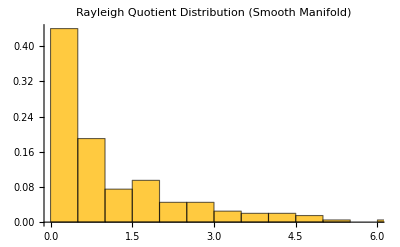

```mathematica
(* 5.3 Rayleigh distribution *)
Histogram[tkM["Rayleigh"], 30, "Probability",
 PlotLabel -> "Rayleigh Quotient Distribution (Smooth Manifold)"]
```

```mathematica
(* ::Section:: *)
(*6. LLM Data Engineering Toolset on Smooth Dataset*)
```

```mathematica
tools = ArrowSpaceLLMToolset[engine];
```

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`budgetFrac:0.5} in Function[{ArrowSpaceEpiplexity`Private`budgetFrac:0.5},Module[{ArrowSpaceEpiplexity`Private`ht$,ArrowSpaceEpiplexity`Private`lo$,ArrowSpaceEpiplexity`Private`hi$,ArrowSpaceEpiplexity`Private`idx$,ArrowSpaceEpiplexity`Private`nBudget$},«1»]] should be a symbol or a list of symbols.

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`q$,ArrowSpaceEpiplexity`Private`thresholdSigma:2.} in Function[{ArrowSpaceEpiplexity`Private`q$,ArrowSpaceEpiplexity`Private`thresholdSigma:2.},Module[{ArrowSpaceEpiplexity`Private`qLam$,ArrowSpaceEpiplexity`Private`mu$,ArrowSpaceEpiplexity`Private`sd$,ArrowSpaceEpiplexity`Private`z$},«1»]] should be a symbol or a list of symbols.

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`nEigs:6} in Function[{ArrowSpaceEpiplexity`Private`nEigs:6},Module[{ArrowSpaceEpiplexity`Private`ke$,ArrowSpaceEpiplexity`Private`evals$,ArrowSpaceEpiplexity`Private`lamQ$},ArrowSpaceEpiplexity`Private`ke$=Min[ArrowSpaceEpiplexity`Private`nEigs,«1»-1];ArrowSpaceEpiplexity`Private`evals$=Sort[Abs[Eigenvalues[«1»]]];«1»;Association[«1»]]] should be a symbol or a list of symbols.

General::stop: Further output of Function::flpar will be suppressed during this calculation.

```mathematica
(* 6.1 Epiplexity-style data selection *)
selectedIdx = tools["SelectForEpiplexity"][0.5];
Print["Selected ", Length[selectedIdx], "/", engine["N"], " items (mid H_T band)"];
```

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`budgetFrac:0.5} in Function[{ArrowSpaceEpiplexity`Private`budgetFrac:0.5},Module[{ArrowSpaceEpiplexity`Private`ht$,ArrowSpaceEpiplexity`Private`lo$,ArrowSpaceEpiplexity`Private`hi$,ArrowSpaceEpiplexity`Private`idx$,ArrowSpaceEpiplexity`Private`nBudget$},«1»]] should be a symbol or a list of symbols.

Selected 1/200 items (mid H_T band)

```mathematica
(* 6.2 Spectral anomaly guard: in-distribution vs synthetic OOD *)
guardIn  = tools["SpectralAnomalyGuard"][XSmooth[[5]]];
guardOut = tools["SpectralAnomalyGuard"][RandomVariate[NormalDistribution[10, 5], engine["F"]]];
```

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`q$,ArrowSpaceEpiplexity`Private`thresholdSigma:2.} in Function[{ArrowSpaceEpiplexity`Private`q$,ArrowSpaceEpiplexity`Private`thresholdSigma:2.},Module[{ArrowSpaceEpiplexity`Private`qLam$,ArrowSpaceEpiplexity`Private`mu$,ArrowSpaceEpiplexity`Private`sd$,ArrowSpaceEpiplexity`Private`z$},«1»]] should be a symbol or a list of symbols.

```mathematica
Print["In-dist Z: ", NumberForm[guardIn["ZScore"], {4, 2}], "  IsOOD? ", guardIn["IsOOD"]];
Print["OOD     Z: ", NumberForm[guardOut["ZScore"], {4, 2}], "  IsOOD? ", guardOut["IsOOD"]];
```

In-dist Z: Function[{ArrowSpaceEpiplexity`Private`q$,ArrowSpaceEpiplexity`Private`thresholdSigma:2.00},Module[{ArrowSpaceEpiplexity`Private`qLam$,ArrowSpaceEpiplexity`Private`mu$,ArrowSpaceEpiplexity`Private`sd$,ArrowSpaceEpiplexity`Private`z$},ArrowSpaceEpiplexity`Private`qLam$=ArrowSpaceEpiplexity`Private`mdl$9614[RayleighQuotient][ArrowSpaceEpiplexity`Private`q$];ArrowSpaceEpiplexity`Private`mu$=Mean[ArrowSpaceEpiplexity`Private`lambdas$9614];ArrowSpaceEpiplexity`Private`sd$=StandardDeviation[ArrowSpaceEpiplexity`Private`lambdas$9614];ArrowSpaceEpiplexity`Private`z$=(ArrowSpaceEpiplexity`Private`qLam$-ArrowSpaceEpiplexity`Private`mu$)/(ArrowSpaceEpiplexity`Private`sd$+1/10^12);Association[QueryLambda→ArrowSpaceEpiplexity`Private`qLam$,PopulationMu→ArrowSpaceEpiplexity`Private`mu$,PopulationSD→ArrowSpaceEpiplexity`Private`sd$,ZScore→ArrowSpaceEpiplexity`Private`z$,IsOOD→Abs[ArrowSpaceEpiplexity`Private`z$]>ArrowSpaceEpiplexity`Private`thresholdSigma]]][{0.57,0.72,1.21,-0.54,0.43,0.34,0.06,0.84,0.34,0.03,0.69,0.46,0.10,0.32,0.92,0.83,-0.22,0.74,-0.64,0.81}][ZScore]  IsOOD? Function[{ArrowSpaceEpiplexity`Private`q$,ArrowSpaceEpiplexity`Private`thresholdSigma:2.},Module[{ArrowSpaceEpiplexity`Private`qLam$,ArrowSpaceEpiplexity`Private`mu$,ArrowSpaceEpiplexity`Private`sd$,ArrowSpaceEpiplexity`Private`z$},ArrowSpaceEpiplexity`Private`qLam$=ArrowSpaceEpiplexity`Private`mdl$9614[RayleighQuotient][ArrowSpaceEpiplexity`Private`q$];ArrowSpaceEpiplexity`Private`mu$=Mean[ArrowSpaceEpiplexity`Private`lambdas$9614];ArrowSpaceEpiplexity`Private`sd$=StandardDeviation[ArrowSpaceEpiplexity`Private`lambdas$9614];ArrowSpaceEpiplexity`Private`z$=(ArrowSpaceEpiplexity`Private`qLam$-ArrowSpaceEpiplexity`Private`mu$)/(ArrowSpaceEpiplexity`Private`sd$+1/10^12);Association[QueryLambda→ArrowSpaceEpiplexity`Private`qLam$,PopulationMu→ArrowSpaceEpiplexity`Private`mu$,PopulationSD→ArrowSpaceEpiplexity`Private`sd$,ZScore→ArrowSpaceEpiplexity`Private`z$,IsOOD→Abs[ArrowSpaceEpiplexity`Private`z$]>ArrowSpaceEpiplexity`Private`thresholdSigma]]][{0.567275,0.720739,1.20549,-0.53583,0.427872,0.341841,0.057175,0.84116,0.335683,0.0271317,0.693743,0.463415,0.0957287,0.317493,0.915726,0.827375,-0.21633,0.744142,-0.640034,0.81286}][IsOOD]

OOD     Z: Function[{ArrowSpaceEpiplexity`Private`q$,ArrowSpaceEpiplexity`Private`thresholdSigma:2.00},Module[{ArrowSpaceEpiplexity`Private`qLam$,ArrowSpaceEpiplexity`Private`mu$,ArrowSpaceEpiplexity`Private`sd$,ArrowSpaceEpiplexity`Private`z$},ArrowSpaceEpiplexity`Private`qLam$=ArrowSpaceEpiplexity`Private`mdl$9614[RayleighQuotient][ArrowSpaceEpiplexity`Private`q$];ArrowSpaceEpiplexity`Private`mu$=Mean[ArrowSpaceEpiplexity`Private`lambdas$9614];ArrowSpaceEpiplexity`Private`sd$=StandardDeviation[ArrowSpaceEpiplexity`Private`lambdas$9614];ArrowSpaceEpiplexity`Private`z$=(ArrowSpaceEpiplexity`Private`qLam$-ArrowSpaceEpiplexity`Private`mu$)/(ArrowSpaceEpiplexity`Private`sd$+1/10^12);Association[QueryLambda→ArrowSpaceEpiplexity`Private`qLam$,PopulationMu→ArrowSpaceEpiplexity`Private`mu$,PopulationSD→ArrowSpaceEpiplexity`Private`sd$,ZScore→ArrowSpaceEpiplexity`Private`z$,IsOOD→Abs[ArrowSpaceEpiplexity`Private`z$]>ArrowSpaceEpiplexity`Private`thresholdSigma]]][{13.47,9.70,4.79,10.91,16.85,14.73,12.84,17.44,15.59,0.73,12.67,10.54,13.03,6.35,15.18,9.88,3.58,14.16,11.06,21.39}][ZScore]  IsOOD? Function[{ArrowSpaceEpiplexity`Private`q$,ArrowSpaceEpiplexity`Private`thresholdSigma:2.},Module[{ArrowSpaceEpiplexity`Private`qLam$,ArrowSpaceEpiplexity`Private`mu$,ArrowSpaceEpiplexity`Private`sd$,ArrowSpaceEpiplexity`Private`z$},ArrowSpaceEpiplexity`Private`qLam$=ArrowSpaceEpiplexity`Private`mdl$9614[RayleighQuotient][ArrowSpaceEpiplexity`Private`q$];ArrowSpaceEpiplexity`Private`mu$=Mean[ArrowSpaceEpiplexity`Private`lambdas$9614];ArrowSpaceEpiplexity`Private`sd$=StandardDeviation[ArrowSpaceEpiplexity`Private`lambdas$9614];ArrowSpaceEpiplexity`Private`z$=(ArrowSpaceEpiplexity`Private`qLam$-ArrowSpaceEpiplexity`Private`mu$)/(ArrowSpaceEpiplexity`Private`sd$+1/10^12);Association[QueryLambda→ArrowSpaceEpiplexity`Private`qLam$,PopulationMu→ArrowSpaceEpiplexity`Private`mu$,PopulationSD→ArrowSpaceEpiplexity`Private`sd$,ZScore→ArrowSpaceEpiplexity`Private`z$,IsOOD→Abs[ArrowSpaceEpiplexity`Private`z$]>ArrowSpaceEpiplexity`Private`thresholdSigma]]][{13.4681,9.70329,4.79361,10.9092,16.8548,14.7347,12.8441,17.4377,15.5871,0.73438,12.6688,10.5406,13.0302,6.35052,15.1849,9.87719,3.57672,14.1551,11.0634,21.3859}][IsOOD]

```mathematica
(* 6.3 Spectral drift between XSmooth and a noisy version *)
fp0 = tools["SpectralFingerprint"][];
```

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`nEigs:6} in Function[{ArrowSpaceEpiplexity`Private`nEigs:6},Module[{ArrowSpaceEpiplexity`Private`ke$,ArrowSpaceEpiplexity`Private`evals$,ArrowSpaceEpiplexity`Private`lamQ$},ArrowSpaceEpiplexity`Private`ke$=Min[ArrowSpaceEpiplexity`Private`nEigs,«1»-1];ArrowSpaceEpiplexity`Private`evals$=Sort[Abs[Eigenvalues[«1»]]];«1»;Association[«1»]]] should be a symbol or a list of symbols.

```mathematica
engineDrift =
  ArrowSpaceMultiClassEngine[
    XSmooth + RandomVariate[NormalDistribution[0, 3.], Dimensions[XSmooth]],
    4, 1.
  ];
toolsDrift = ArrowSpaceLLMToolset[engineDrift];
fp1 = toolsDrift["SpectralFingerprint"][];
```

General::munfl: Exp[-1629.49] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1832.16] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1851.41] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`nSamples:1} in Function[{ArrowSpaceEpiplexity`Private`nSamples:1},Module[{ArrowSpaceEpiplexity`Private`cov$,ArrowSpaceEpiplexity`Private`z$},ArrowSpaceEpiplexity`Private`cov$=ArrowSpaceEpiplexity`Private`Q$9962;«31»=«1»;If[ArrowSpaceEpiplexity`Private`nSamples==1,First[ArrowSpaceEpiplexity`Private`z$],ArrowSpaceEpiplexity`Private`z$]]] should be a symbol or a list of symbols.

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$,ArrowSpaceEpiplexity`Private`b:32} in Function[{ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$,ArrowSpaceEpiplexity`Private`b:32},Module[{ArrowSpaceEpiplexity`Private`header$,ArrowSpaceEpiplexity`Private`centroid$,ArrowSpaceEpiplexity`Private`topo$,ArrowSpaceEpiplexity`Private`params$},«1»]] should be a symbol or a list of symbols.

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`q$,ArrowSpaceEpiplexity`Private`topK:5,ArrowSpaceEpiplexity`Private`alpha:0.6} in Function[{ArrowSpaceEpiplexity`Private`q$,ArrowSpaceEpiplexity`Private`topK:5,ArrowSpaceEpiplexity`Private`alpha:0.6},Module[{ArrowSpaceEpiplexity`Private`qNorm$,ArrowSpaceEpiplexity`Private`xNorm$,ArrowSpaceEpiplexity`Private`cosine$,«34»,«37»,«36»,ArrowSpaceEpiplexity`Private`combined$,ArrowSpaceEpiplexity`Private`idx$},«1»]] should be a symbol or a list of symbols.

General::stop: Further output of Function::flpar will be suppressed during this calculation.

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`budgetFrac:0.5} in Function[{ArrowSpaceEpiplexity`Private`budgetFrac:0.5},Module[{ArrowSpaceEpiplexity`Private`ht$,ArrowSpaceEpiplexity`Private`lo$,ArrowSpaceEpiplexity`Private`hi$,ArrowSpaceEpiplexity`Private`idx$,ArrowSpaceEpiplexity`Private`nBudget$},«1»]] should be a symbol or a list of symbols.

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`q$,ArrowSpaceEpiplexity`Private`thresholdSigma:2.} in Function[{ArrowSpaceEpiplexity`Private`q$,ArrowSpaceEpiplexity`Private`thresholdSigma:2.},Module[{ArrowSpaceEpiplexity`Private`qLam$,ArrowSpaceEpiplexity`Private`mu$,ArrowSpaceEpiplexity`Private`sd$,ArrowSpaceEpiplexity`Private`z$},«1»]] should be a symbol or a list of symbols.

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`nEigs:6} in Function[{ArrowSpaceEpiplexity`Private`nEigs:6},Module[{ArrowSpaceEpiplexity`Private`ke$,ArrowSpaceEpiplexity`Private`evals$,ArrowSpaceEpiplexity`Private`lamQ$},ArrowSpaceEpiplexity`Private`ke$=Min[ArrowSpaceEpiplexity`Private`nEigs,«1»-1];ArrowSpaceEpiplexity`Private`evals$=Sort[Abs[Eigenvalues[«1»]]];«1»;Association[«1»]]] should be a symbol or a list of symbols.

General::stop: Further output of Function::flpar will be suppressed during this calculation.

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`nEigs:6} in Function[{ArrowSpaceEpiplexity`Private`nEigs:6},Module[{ArrowSpaceEpiplexity`Private`ke$,ArrowSpaceEpiplexity`Private`evals$,ArrowSpaceEpiplexity`Private`lamQ$},ArrowSpaceEpiplexity`Private`ke$=Min[ArrowSpaceEpiplexity`Private`nEigs,«1»-1];ArrowSpaceEpiplexity`Private`evals$=Sort[Abs[Eigenvalues[«1»]]];«1»;Association[«1»]]] should be a symbol or a list of symbols.

```mathematica
drift = tools["DetectDrift"][fp0, fp1];
drift
```

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`fp0,ArrowSpaceEpiplexity`Private`fp1,ArrowSpaceEpiplexity`Private`gapThreshold:0.1} in Function[{ArrowSpaceEpiplexity`Private`fp0,ArrowSpaceEpiplexity`Private`fp1,ArrowSpaceEpiplexity`Private`gapThreshold:0.1},Module[{ArrowSpaceEpiplexity`Private`gapChange,ArrowSpaceEpiplexity`Private`meanShift,ArrowSpaceEpiplexity`Private`drift},«1»]] should be a symbol or a list of symbols.

```mathematica
(* ::Section:: *)
(*7. Observer-Dependence: Sweep k*)
```

```mathematica
observerTable = ArrowSpaceObserverSweep[XSmooth, {2, 3, 4, 5, 6, 8, 10}];
```

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`nSamples:1} in Function[{ArrowSpaceEpiplexity`Private`nSamples:1},Module[{ArrowSpaceEpiplexity`Private`cov$,ArrowSpaceEpiplexity`Private`z$},ArrowSpaceEpiplexity`Private`cov$=ArrowSpaceEpiplexity`Private`Q$10690;«31»=«1»;If[ArrowSpaceEpiplexity`Private`nSamples==1,First[ArrowSpaceEpiplexity`Private`z$],ArrowSpaceEpiplexity`Private`z$]]] should be a symbol or a list of symbols.

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$,ArrowSpaceEpiplexity`Private`b:32} in Function[{ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$,ArrowSpaceEpiplexity`Private`b:32},Module[{ArrowSpaceEpiplexity`Private`header$,ArrowSpaceEpiplexity`Private`centroid$,ArrowSpaceEpiplexity`Private`topo$,ArrowSpaceEpiplexity`Private`params$},«1»]] should be a symbol or a list of symbols.

General::stop: Further output of Function::flpar will be suppressed during this calculation.

General::munfl: Exp[-800.648] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-811.681] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-857.33] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Grid[
  Join[
    {{"k", "|P_AS| KB", "Mean H_T", "Compression", "SpectralGap"}},
    (With[{r = #},
       {
         r["k"],
         NumberForm[r["StructuralKB"], {5, 2}],
         NumberForm[r["EntropyMean"], {5, 3}],
         NumberForm[r["Compression"], {5, 2}],
         NumberForm[r["SpectralGap"], {5, 4}]
       }
     ] &) /@ observerTable
  ],
  Frame -> All
]
```

```mathematica
ListLinePlot[
  {
    {#["k"], #["StructuralKB"]} & /@ observerTable,
    {#["k"], #["EntropyMean"]} & /@ observerTable
  },
  PlotLegends -> {"|P_AS| (KB)", "Mean H_T"},
  AxesLabel -> {"k", "Bits"},
  PlotLabel -> "Observer-Dependence: S_T ↑ and H_T ↓ with graph density k"
]
```

Function::flpar: Parameter specification {ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$,ArrowSpaceEpiplexity`Private`b:32.} in Function[{ArrowSpaceEpiplexity`Private`C0$,ArrowSpaceEpiplexity`Private`k$,ArrowSpaceEpiplexity`Private`b:32.},Module[{ArrowSpaceEpiplexity`Private`header$,ArrowSpaceEpiplexity`Private`centroid$,ArrowSpaceEpiplexity`Private`topo$,ArrowSpaceEpiplexity`Private`params$},«1»]] should be a symbol or a list of symbols.

General::stop: Further output of Function::flpar will be suppressed during this calculation.

Rule::rhs: Pattern ArrowSpaceEpiplexity`Private`b:32. appears on the right-hand side of rule System`ListPlotsDump`modelData[WrappedValues,{{{2.,0.0001220703125 Function[{«3»},Module[«2»]][28.,2.]},{3.,0.0001220703125 Function[{«3»},Module[«2»]][28.,3.]},«1»,{«1»},«1»,{8.,«19» «1»},{10.,0.0001220703125 Function[{«3»},Module[«2»]][28.,10.]}},«1»},Charting`Private`Tag]→«1».

General::stop: Further output of Rule::rhs will be suppressed during this calculation.

-Graphics-